# Results

### Clear Stagnant Parameters

```mathematica
Clear[ele,Vo,uVo,F,R,kB,T,β,e,eo,NA,a,ao ,aoSI,aSI,aCond,l,lcgs,lsi,Lcgs,Lsi,σo,η,ηSI,ϵo,ϵDL,ϵSL]
```

```mathematica
Clear[QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13,QpHi ]
```

```mathematica
Clear[λpH1 ,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13,λpHi]
```

```mathematica
Clear[σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13,σpHi,σoSI,σo]
```

## 1. Stagnant parameters

## Input Voltage

```mathematica
Vo=0.05
```

0.05

```mathematica
uVo=Quantity[Vo,"Volts"]
```

0.05 V

## Standard Constants

```mathematica
F=UnitConvert[Quantity["FaradayConstant"],"StatCoulombs"/"Moles"]
```

2.892558×10^14 statC/mol

```mathematica
(*R = = UnitConvert[UnitConvert[Quantity["GasConstant"],""],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]*)
```

```mathematica
R = UnitConvert[UnitConvert[Quantity["GasConstant"],"SIBase"],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]
```

8.3145×10^7 g cm^2/(s^2 K mol)

```mathematica
kB =UnitConvert[ Quantity["BoltzmannConstant"],"Ergs"/"Kelvins"]
```

1.3806×10^-16 ergs/K

```mathematica
T=Quantity[298.15,"Kelvins"]
```

298.15 K

```mathematica
β=1/kB/T
```

2.42931×10^13 per erg

```mathematica
e =UnitConvert[Quantity["ElementaryCharge"],"StatCoulombs"]
```

4.803205×10^-10 statC

```mathematica
eo=e
```

4.803205×10^-10 statC

```mathematica
NA =UnitConvert[Quantity["AvogadroConstant"],1/"Moles"]
```

6.022141×10^23 /mol

## Actin3

### radius

```mathematica
ao = UnitConvert[Quantity[(23.83)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
a = UnitConvert[Quantity[(23.83+0*2.5)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
aCond= a
```

2.383×10^-7 cm

```mathematica
aoSI = UnitConvert[ao,"SIBase"]
```

2.383×10^-9 m

```mathematica
aSI = UnitConvert[a,"SIBase"]
```

2.383×10^-9 m

### length

```mathematica
l=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
lsi=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
Lsi=Quantity[422.20*10^(-10),"Meters"]
```

4.222×10^-8 m

### Charge Q

```mathematica
(*Charge coming from tabulated values for Cong Model*)
QpH1 = 657*e;
QpH2=617*e;
QpH3=561*e;
QpH4=296*e;
QpH5=23*e;
QpH6=-82*e;
QpH7=-154*e;
QpH8=-184*e;
QpH9=-222*e;
QpH10=-269*e;
QpH11=-432*e;
QpH12=-476*e;
QpH13=-502*e;
```

```mathematica
QpHi = {QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13}
```

{3.155705×10^-7 statC,2.963577×10^-7 statC,2.694598×10^-7 statC,1.421749×10^-7 statC,1.104737×10^-8 statC,-3.938628×10^-8 statC,-7.396935×10^-8 statC,-8.837897×10^-8 statC,-1.066311×10^-7 statC,-1.292062×10^-7 statC,-2.074984×10^-7 statC,-2.286325×10^-7 statC,-2.411209×10^-7 statC}

### Linear Charge Density

```mathematica
λpH1 = QpH1/Lsi;
λpH2 = QpH2/Lsi;
λpH3 = QpH3/Lsi;
λpH4 = QpH4/Lsi;
λpH5 = QpH5/Lsi;
λpH6 = QpH6/Lsi;
λpH7 = QpH7/Lsi;
λpH8 = QpH8/Lsi;
λpH9 = QpH9/Lsi;
λpH10 = QpH10/Lsi;
λpH11 = QpH11/Lsi;
λpH12 = QpH12/Lsi;
λpH13 = QpH13/Lsi;
```

```mathematica
λpHi = {λpH1,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13}
```

{7.47443 statC/m,7.01937 statC/m,6.38228 statC/m,3.36748 statC/m,0.261662 statC/m,-0.932882 statC/m,-1.752 statC/m,-2.0933 statC/m,-2.52561 statC/m,-3.06031 statC/m,-4.9147 statC/m,-5.41527 statC/m,-5.71106 statC/m}

### Surface Charge Density

```mathematica
σpH1 = λpHi[[1]]/(2*Pi*aoSI);
σpH2 = λpHi[[2]]/(2*Pi*aoSI);
σpH3 = λpHi[[3]]/(2*Pi*aoSI);
σpH4 = λpHi[[4]]/(2*Pi*aoSI);
σpH5 = λpHi[[5]]/(2*Pi*aoSI);
σpH6 = λpHi[[6]]/(2*Pi*aoSI);
σpH7 = λpHi[[7]]/(2*Pi*aoSI);
σpH8 = λpHi[[8]]/(2*Pi*aoSI);
σpH9 = λpHi[[9]]/(2*Pi*aoSI);
σpH10 = λpHi[[10]]/(2*Pi*aoSI);
σpH11 = λpHi[[11]]/(2*Pi*aoSI);
σpH12 = λpHi[[12]]/(2*Pi*aoSI);
σpH13 = λpHi[[13]]/(2*Pi*aoSI);
```

```mathematica
σpHi = UnitConvert[{σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13},"Coulombs"/"Meters"^2]
```

{0.166515 C/m^2,0.156377 C/m^2,0.142184 C/m^2,0.0750205 C/m^2,0.0058293 C/m^2,-0.0207827 C/m^2,-0.0390309 C/m^2,-0.0466344 C/m^2,-0.0562654 C/m^2,-0.0681774 C/m^2,-0.109489 C/m^2,-0.120641 C/m^2,-0.127231 C/m^2}

```mathematica
σoSI=σpHi[[7]]
```

-0.0390309 C/m^2

```mathematica
(*σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e*)
```

### viscosity

```mathematica
(*actin viscosity*)
η=UnitConvert[Quantity[8.90×10^(-4),"Pascals"*"Seconds"],"Dynes"*"Seconds"/"Centimeters"^2]
```

0.0089 s dynes/cm^2

```mathematica
ηSI=Quantity[8.90×10^(-4),"Pascals"*"Seconds"]
```

0.00089 s Pa

## Permittivity

#### air

```mathematica
ϵo =  N[UnitConvert[ Quantity["ElectricConstant"],"SIBase"]]
```

8.85419×10^-12 s^4 A^2/(kg m^3)

#### Diffuse Layer

```mathematica
ϵDL =78.358
```

78.358

#### stern layer

```mathematica
ϵSL =5
```

5

```mathematica
(*ϵSL =78.358*)
```

## - pH7 σo = σ[7]/e= -2.43612×10^13 "/"("cm")^2 n6 ⇒ [Ca2+] ~ 10^(-6)

#### Clear Parameters of this notebook

```mathematica
Clear[zCa,zCl,zK,zp,zp,cCaSL,cCa,cCl,cK,cCaMolar,cClMolar,cKMolar,uCa,uCl,uK,lBDL,lBDLSI,lBSL,lBSLSI,κDL,κDLSI,κSL,κSLSI,λDL ,λDLSI,λSL,λSLSI,εDL,εSL,λεDL,λεSL,BDL,BSL,xcSLsig ,xcSLsig,δ,p,psiq,ζ ,q,ζo ,y1,βe,xcDLsig,xcεDL,xcDL,xc,xcSLsig,xcεSL,xcCondsPercnt]
```

```mathematica
Clear[κDLn6pH7,εDLxan6pH7,δn6pH7,pn6pH7,ζn6pH7,xcn6pH7,xcCondsPercntn6pH7,xcNonCondsPercntn6pH7]
```

```mathematica
Clear[σo,fpH7,fc1pH7 ,fc2pH7 ,fMpH7 ]
```

```mathematica
σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e
```

-2.43612×10^13 /cm^2

## 2. Parameters

Diffuse Layer

## Ions

### valence

```mathematica
zCa = 2;
```

```mathematica
zHPO42m = -2;
```

```mathematica
zCl = -1;
```

```mathematica
zK = 1;
```

```mathematica
zNa = 1;
```

### concentration

```mathematica
cCa = Quantity[((0.00005)),"Moles"/"Meters"^3]
```

0.00005 mol/m^3

```mathematica
cCl = Quantity[100+(2*QuantityMagnitude[cCa]),"Moles"/"Meters"^3]
```

100. mol/m^3

#### MM correction

```mathematica
(*cHPO42m = N[UnitConvert[Quantity[((77.50005)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

```mathematica
cK =Quantity[100,"Moles"/"Meters"^3]
```

100 mol/m^3

```mathematica
(*cNa =N[UnitConvert[Quantity[15,"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

#### Molar concentration value

```mathematica
cCaMolar=N[UnitConvert[cCa ,"Molar"]]
cCaMilliMolar=N[UnitConvert[cCa ,"MilliMolar"]]
cCaMicroMolar=N[UnitConvert[cCa ,"MicroMolar"]]
cCaNanoMolar=N[UnitConvert[cCa ,"NanoMolar"]]
```

5.×10^-8 M

0.00005 mM

0.05 μM

50. nM

```mathematica
cClMolar=N[UnitConvert[cCl ,"Molar"]]
```

0.1 M

```mathematica
cKMolar=N[UnitConvert[cK ,"Molar"]]
```

0.1 M

```mathematica
(*cNaMolar=UnitConvert[UnitConvert[cNa ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar=UnitConvert[UnitConvert[cHPO42m ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar2=UnitConvert[UnitConvert[cHPO42m2 ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
ElectroNeutrality=zCa cCa+zK cK+zCl cCl
```

-3.31965×10^-15 mol/m^3

#### MM correction

```mathematica
(*Solve[zCa cCaMolar+zK cKMolar(*+zNa cNaMolar+zHPO42m (cHPO42mMolar)*)+zCl ccClMolar==0,ccClMolar]*)
```

### concentration of divalent-monovalent mixture

```mathematica
zp=1+√(4 cCa/cK)
```

1.00141

```mathematica
1+√(4 cCa/cK)
```

1.00141

### ion size

```mathematica
(*size of ion radius; used for the self inductance calculations*)
```

#### monovalent

```mathematica
(*radius*)
```

```mathematica
srK = Quantity[1.52*10^(-10),"Meters"];
```

```mathematica
srNa = Quantity[1.16*10^(-10),"Meters"];
```

```mathematica
srCl = Quantity[1.67*10^(-10),"Meters"];
```

```mathematica
(*diameter*)
```

```mathematica
sCa = N[194*10^-12]
```

1.94×10^-10

```mathematica
sK = QuantityMagnitude[Quantity[3.04*10^(-10),"Meters"]];
```

```mathematica
sNa = QuantityMagnitude[Quantity[2.32*10^(-10),"Meters"]];
```

#### Divalent

```mathematica
(*radius*)
```

```mathematica
(*srCa =  Quantity[1.14*10^(-10),"Meters"];*)
```

```mathematica
sCa = N[Quantity[194*10^-12,"Meters"] ]
```

1.94×10^-10 m

```mathematica
sHPO42m=Quantity[5.5*10^(-10),"Meters"];
```

#### Rion

```mathematica
a
```

2.383×10^-7 cm

```mathematica
Rion=srK/a
```

0.0637851

```mathematica
Rion=0.0
```

0.

### mobility

```mathematica
mobilityPotassium=10.12*10^(-8);
```

```mathematica
uK=UnitConvert[Quantity[10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.04886×10^-15 cm^2 mol/(s statC statV)

```mathematica
uCa = UnitConvert[Quantity[2.06*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

2.13504×10^-16 cm^2 mol/(s statC statV)

```mathematica
(*uCl=UnitConvert[Quantity[6.88*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)*)
```

```mathematica
uCl=UnitConvert[Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.08893×10^-15 cm^2 mol/(s statC statV)

```mathematica
uNa = UnitConvert[Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

7.15325×10^-16 cm^2 mol/(s statC statV)

```mathematica
uHPO42mSIbase=Quantity[0.898*10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")]
```

9.08776×10^-8 m^2/(s V)

```mathematica
uHPO42m=UnitConvert[uHPO42mSIbase,"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

9.4188×10^-16 cm^2 mol/(s statC statV)

```mathematica
Quantity[9.418799447028083*^-16, (("Centimeters")^2 "Moles")/("Seconds" "StatCoulombs" "StatVolts")]
```

(9.4188×10^-16 cm^2 mol/(s statC statV))

#### SI units

```mathematica
uClSIbase=Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

1.05066×10^-7 m^2/(s V)

```mathematica
uNaSIbase = Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

6.90184×10^-8 m^2/(s V)

## bjerrum lengths

#### diffuse layer

```mathematica
lBDL =(e^2 β)/ϵDL
```

7.15255×10^-8 statC^2/erg

```mathematica
lBDLSI=UnitConvert[lBDL*(1/(4 π ϵo)),"SIBase"]
```

7.15255×10^-10 m

## Inverse Debye Length

#### diffuse layer

#### MM correction

```mathematica
lBDL
```

7.15255×10^-8 statC^2/erg

```mathematica
cK* NA* zK^2
```

6.022141×10^25 per meter^3

```mathematica
cCl*NA*zCl
```

-6.02215×10^25 per meter^3

```mathematica
(*κDL = √(8 π lBDL cK NA zK^2)*)
```

```mathematica
κDL = √(8 *π *lBDL*( cK* NA* zK^2+cCl*NA*zCl^2+cCa*NA*zCa^2))
```

1.47144×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κDL *(1/(√(4 π ϵo))),"SIBase"]
```

1.47144×10^9 per meter

## Debye Length

#### diffuse layer

```mathematica
λDL = 1/κDL
```

6.79609×10^-11 m^(3/2)√ergs/statC

```mathematica
λDLSI=UnitConvert[λDL  *(√(4 π ϵo)),"SIBase"]
```

6.79609×10^-10 m

## ε = κ a

#### diffuse layer

```mathematica
εDL =  QuantityMagnitude[κDL* a]
```

3.50643

```mathematica
UnitSimplify[κDLSI* aSI]
```

UnitSimplify[κDLSI (2.383×10^-9 m)]

## Dimensionless Debye Length

#### diffuse layer

```mathematica
λεDL=1/εDL
```

0.28519

```mathematica
(*λεDL=0.49/εDL^0.89*)
```

## B = 4 π lB z a σa

```mathematica
(*statC^2/(cm erg)=statC^2/1 1/cm 1/erg=(cm^2 g)/s^2 1/cm s^2/(g cm^2)=1*)
```

#### diffuse layer

```mathematica
BDL = QuantityMagnitude[ 4 π lBDL a zp σo]
```

-5.22525

## Diffuse Layer Parameters

```mathematica
δ=BesselK[0,εDL]/BesselK[1,εDL]
```

0.881452

```mathematica
p =(BDL*δ)/(2 εDL)
```

-0.656766

```mathematica
FindRoot[Sqrt[(psiq*p)^2+1]-1==δ^2*(1/2/p*Sinh[2/psiq*ArcSinh[psiq*p]]-1),{psiq,0.7}] /.Rule->Set
```

{0.91177}

```mathematica
ζ=psiq
```

0.91177

```mathematica
ζ*p
```

-0.598819

```mathematica
q = √((ζ p)^2+1)
```

1.16558

```mathematica
(* Limits on ζ: ζo < ζ < 1 *)   (*22*)
ζo = √((2*δ)/(3+δ^2))
```

0.683193

```mathematica
(* Surface Potential given by NLDH *)   (*21*)
y1=2/ζ ArcSinh[ζ p]
```

-1.24552

```mathematica
βe=zp*e β (* in 1/V*)
```

11685. statC/erg

## percent condensed

```mathematica
xcCondsPercnt=1-2/(1+q)
```

0.0764613

```mathematica
(-xcCondsPercnt+1)
```

0.923539

Stagnant Layer

#### MM correction

```mathematica
Clear[xxc2]
```

### Option 1

```mathematica
(*FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)*(Exp[-yDL[xxc2]]+Exp[-yDL[1]])/2-2/(1+q)*xxc2*σoSI/a*BesselK[1,xxc2*εDL]/BesselK[1,εDL]==-σoSI/a,{xxc2,1.3},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set*)
```

### Option 2

```mathematica
FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar*Exp[-yDL[xxc2]]+2*cCaMolar*Exp[-yDL[xxc2]])==-(1-2/(1+q))*σoSI/a,{xxc2,1.},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set
```

FindRoot::precw: The precision of the argument function ((-1+xxc2^2) (ⅇ^(62.3494 BesselK[0,Times[«1»]]) (1.×10^-7)+ⅇ^(62.3494 «1») (0.1)) (1.446279×10^14)==1.25235) is less than WorkingPrecision (10.).

{1.046213732}

```mathematica
(*xcεDL=xcDLsig*)
```

```mathematica
xcεDL=xxc2
```

1.046213732

```mathematica
(*xcDL=xcDLsig*)
```

```mathematica
xcDL=xxc2
```

1.046213732

```mathematica
xc=xcDL
```

1.046213732

## Ions SL

#### MM correction

```mathematica
xcCondsPercnt=(xc^2-1)/2*(Exp[-yDL[xc]]+Exp[-yDL[1]])/2
```

0.144424

```mathematica
cCaSL =cCa*xcCondsPercnt
```

7.22118×10^-6 mol/m^3

```mathematica
cKSL = cK*xcCondsPercnt
```

14.4424 mol/m^3

```mathematica
cNaSL = cNa*xcCondsPercnt
```

0.144424 cNa

#### Molar concentration value

```mathematica
cCaSLMolar=UnitConvert[UnitConvert[cCaSL ,"Moles"/"Meters"^3],"Molar"]
```

7.22118×10^-9 M

```mathematica
cKSLMolar=UnitConvert[UnitConvert[cKSL ,"Moles"/"Meters"^3],"Molar"]
```

0.0144424 M

```mathematica
cNaSLMolar=UnitConvert[UnitConvert[cNaSL ,"Moles"/"Meters"^3],"Molar"]
```

UnitConvert[UnitConvert[0.144424 cNa,Moles/Meters^3],Molar]

#### ...

```mathematica
(*cCa = N[UnitConvert[Quantity[((10*0.5)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*(-xcCondsPercnt+1)*)
```

## bjerrum lengths SL

#### stagnant layer

```mathematica
lBSL =(e^2 β)/ϵSL
```

1.12092×10^-6 statC^2/erg

```mathematica
lBSLSI=UnitConvert[lBSL *(1/(4 π ϵo)),"SIBase"]
```

1.12092×10^-8 m

## Inverse Debye Length SL

#### stagnant

```mathematica
(*κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA zp )*)
```

```mathematica
κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA(**xcCondsPercnt*))
```

1.56532×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κSL *(1/(√(4 π ϵo))),"SIBase"]
```

1.56532×10^9 per meter

## Debye Length SL

#### stagnant

```mathematica
λSL=1/κSL
```

6.38849×10^-11 m^(3/2)√ergs/statC

```mathematica
λSLSI=UnitConvert[λSL  *(√(4 π ϵo)),"SIBase"]
```

6.38849×10^-10 m

## ε = κ a -SL-

#### stern

```mathematica
εSL =   QuantityMagnitude[κSL* a]
```

3.73015

```mathematica
(*ϵMix = QuantityMagnitude[κMix*a]*)
```

### Dimensionless Debye Length SL

#### stern

```mathematica
λεSL= 1/εSL
```

0.268086

## B = 4 π lB z a σa -SL-

#### stern

```mathematica
BSL = QuantityMagnitude[4 π lBSL zp a σo]
```

-81.888

## 2a. Condensation Distance

### Condensation Distance

### Analysis on SL

#### MM correction

#### If we use HD solution, the (dimensionless) total charge accumulated in the Dl cancel out the (dimensionless) total charge of the cylinder providing electroneutrality. Thus, it does not allow for condensation in the SL.

```mathematica
NIntegrate[BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

1.

#### If we use NLHD solution, the (dimensionless) total charge accumulated in the DL partially cancel out the (dimensionless) total charge of the cylinder. Thus, some (dimensionless) charge should be condensation in the SL.

```mathematica
NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.923539

#### the (dimensionless) charge accumulated in the SL that provide electroneutrality is given by

```mathematica
1.0-NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.0764613

#### Cylinder charge per radius

```mathematica
totalcharge=-σoSI/a
```

16.3789 C/cm^3

#### contribution from SL

```mathematica
contsl=UnitConvert[(xc^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)(Exp[-yDL[xc]]+Exp[-yDL[1]])/2,"Coulombs"/"Centimeters"^3]
```

1.39348 C/cm^3

#### contribution from DL

#### option 1

```mathematica
(*contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,xc*εDL]*xc,"Coulombs"/"Centimeters"^3]*)
```

```mathematica
-2/(1+q)*xc*σoSI/a*BesselK[1,xc*εDL]/BesselK[1,εDL]
```

13.1084 C/cm^3

#### option 2

```mathematica
contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,1*εDL],"Coulombs"/"Centimeters"^3]
```

15.1266 C/cm^3

#### electroneutrality validation

```mathematica
totalcharge-contdl-contsl
```

-0.141124 C/cm^3

#### fraction of condensed ions (Manning theory)

```mathematica
(*1-2/Abs[BDL]*)
```

```mathematica
manningTheoryVoEQ0p05VepsiEQ5cCa50nM=1-2/(Abs[BDL] zCa/zp)
```

0.808351

#### Our approach: fraction of total charge condensed in SL (same as 1-2/(1+q) )

```mathematica
contsl/totalcharge
```

0.0850775

```mathematica
prcntCondSLVoEQ0p05VepsiEQ5cCaEQ50nM=contsl/totalcharge
```

0.0850775

#### Our approach: fraction of total charge condensed in DL (same as 2/(1+q) )

```mathematica
contdl/totalcharge
```

0.923539

```mathematica
prcntCondDLVoEQ0p05VepsiEQ5cCaEQ50nM=contdl/totalcharge
```

0.923539

#### SL thickness

```mathematica
UnitConvert[(xc-1)*a,"Angstroms"]
```

1.10127 Å

```mathematica
δCL=UnitConvert[(xc-1)*a,"Angstroms"]
```

1.10127 Å

```mathematica
SLthickVoEQ0p05VepsiEQ5cCaEQ50nM=δCL
```

1.10127 Å

#### SL

```mathematica
FindRoot[xcSLsig ySL'[xcSLsig]/ySL'[1]+((ζ p)/(1+q)*ySL[xcSLsig]/ySL[1])^2==1,{xcSLsig,1.0}]/.Rule->Set
```

{1.04533}

```mathematica
xcεSL=xcSLsig
```

1.04533

```mathematica
xcSL=xcεSL
```

1.04533

```mathematica
(*xcDL=xcSLsig*)
```

```mathematica
(*xc=xcDL*)
```

## 2b. Electric Potential

## SL

#### dimensionless

```mathematica
ySL[x]
```

-1.00985+1.73925 (1.09456317-x^2)-85.6724 (0.045177677-Log[x])+3.80744 (-0.045177677+Log[x])

#### plots with dimensions

```mathematica
(*unitless CL thickness*)
nuδCL=QuantityMagnitude[δCL]
```

1.10127

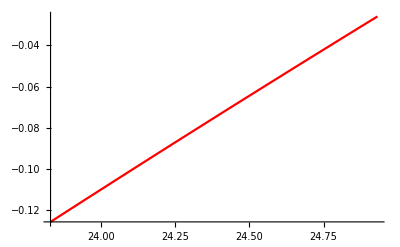

```mathematica
uSLplot=Plot[ UnitConvert[1/(β e)ySL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"],{x,23.83,23.83+nuδCL},PlotStyle->Red]
```

## DL

#### dimensionless

```mathematica
yDL[x]
```

-62.3494 BesselK[0,3.50643 x]

#### plots with dimensions

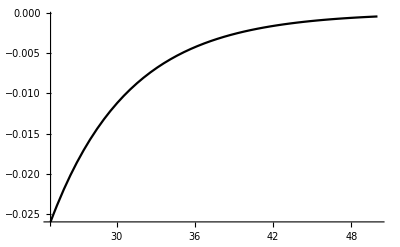

```mathematica
uDLplot=Plot[{UnitConvert[1/(β e)yDL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"]},{x,23.83+nuδCL,50},PlotRange->Full,PlotStyle->Black,PlotLegends->"Expressions"]
```

```mathematica
UnitConvert[UnitConvert[1/(β e)yDL[(23.83+1.1012732237538216)*Quantity[10^(-10),"Meters"]/a],"SIBase"],"Volts"]
```

-0.0259457 V

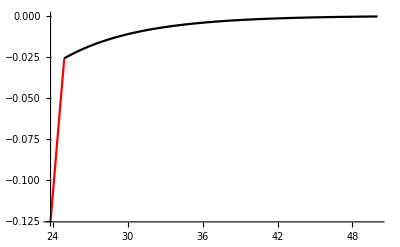

```mathematica
Show[uSLplot,uDLplot,PlotRange->All]
```

## 3. BDL vs “f”

eqn 44

```mathematica
fpH7 = 1-2/(1+√(1+√((-p/Log[δ])^2+1)))
```

0.430196

eqn 45 - NLDH

```mathematica
fc1pH7 = 1-4/(2+√(Abs[BDL]^2+4))
```

0.473333

eqn 46 - NLDH

```mathematica
fc2pH7 = 1-4/(2+√((Abs[BDL]*ArcSinh[BDL/2])^2+4))
```

0.637861

eqn 47 - Manning

```mathematica
fMpH7 = 1-2/Abs[BDL]
```

0.617243

## 4. Current

Transversal (Axial) Current

## SL

```mathematica
ΔVSLt=Vo
currRadial=CurrentTransSL
```

0.05

-4759.28 statC/(s statV)

```mathematica
(*currRadial=CurrentTransSL/.ΔVSLt->Vo*)
```

#### CGS

```mathematica
currRadial*UnitConvert[uVo,"StatVolts"]
```

-0.793762 statC/s

```mathematica
ItSLcgs =UnitConvert[currRadial*UnitConvert[uVo,"StatVolts"],"StatAmperes"]
```

-0.793762 statA

#### SI

```mathematica
ItSLsi =UnitConvert[ UnitSimplify[currRadial]*uVo,"Amperes"]
```

-2.64771×10^-10 A

## DL

```mathematica
ΔVDLt=Vo
```

0.05

```mathematica
CurrentTransDL
```

85457.3 statC/(s statV)

#### CGS

```mathematica
UnitConvert[CurrentTransDL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

14.2527 s statC^2 statV/(g cm^2)

```mathematica
ItDLcgs =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"StatAmperes"]
```

14.2527 statA

#### SI

```mathematica
ItDLsi =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"Amperes"]
```

4.75421×10^-9 A

Longitudinal (Axial) Current

## SL

```mathematica
ΔVSLl=Vo
ilSL=IlSL
```

0.05

1.97978 statC/(s statV)

```mathematica
(*ilSL=IlSL/.ΔVSLl->Vo*)
```

```mathematica
(*IlSL=ilSL/.ΔV->Vo*)
```

```mathematica
ilSL*uVo
```

0.000330192 statC/s

#### CGS

```mathematica
UnitConvert[ilSL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

0.000330192 s statC^2 statV/(g cm^2)

```mathematica
Ilslcgs=UnitConvert[ilSL*uVo,"StatAmperes"]
```

0.000330192 statA

```mathematica
UnitConvert[IlcSL (Quantity[0.05, "Volts"]),"StatAmperes"]
```

UnitConvert[IlcSL (0.05 V),StatAmperes]

#### SI

```mathematica
Ilslsi=UnitConvert[ilSL*uVo,"Amperes"]
```

1.1014×10^-13 A

## DL

```mathematica
ΔVDLl=Vo
ilDL=IlDL*uVo
```

0.05

0.0405006 statC/s

```mathematica
(*ilDL=IlDL*uVo/.ΔVDLl->Vo*)
```

#### CGS

```mathematica
IlDLcgs=UnitConvert[ilDL,"StatAmperes"]
```

0.0405006 statA

#### SI

```mathematica
IlDLsi=UnitConvert[ilDL,"Amperes"]
```

1.35095×10^-11 A

## 5. Resistance

Transversal (Axial) Resistance

## SL

```mathematica
RtSL
```

-0.0000105058 s statV/statC

```mathematica
RtSLsi=UnitConvert[RtSL,"Ohms"]
```

-9.44214×10^6 Ω

```mathematica
uRtSLsi=Abs[RtSLsi]
```

9.44214×10^6 Ω

## DL

```mathematica
RtDL
```

4.20823×10^-6 s statV/statC

```mathematica
RtDLsi=UnitConvert[RtDL,"Ohms"]
```

3.78217×10^6 Ω

```mathematica
uRtDLsi=RtDLsi
```

3.78217×10^6 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRtDLsi=Quantity[0.524*10^7,"Ohms"]*)
```

```mathematica
1.0868426051953934*^7/(4.74*10^6)
```

2.29292

## Equivalent Resistance

```mathematica
uRtEqsi =uRtDLsi +uRtSLsi
```

1.32243×10^7 Ω

Longitudinal (Axial) Resistance

## SL

```mathematica
RlSL
```

0.0252553 s statV/statC

```mathematica
RlSLsi=UnitConvert[RlSL,"Ohms"]
```

2.26983×10^10 Ω

```mathematica
uRlSLsi=RlSLsi
```

2.26983×10^10 Ω

## DL

```mathematica
RlDL
```

0.000205901 s statV/statC

```mathematica
RlDLsi=UnitConvert[RlDL,"Ohms"]
```

1.85054×10^8 Ω

```mathematica
uRlDLsi=RlDLsi
```

1.85054×10^8 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRlDLsi=Quantity[0.199*10^9,"Ohms"]*)
```

```mathematica
1.7434096079950902*^8/(195*10^6)
```

0.894056

## Equivalent Resistance

```mathematica
uRlEqsi = uRlDLsi*uRlSLsi /(uRlDLsi+uRlSLsi)
```

1.83558×10^8 Ω

## 6. Capacitance

## SL

### q, L, M, NN terms

```mathematica
ζv =2*δ √(1/(3+δ^2))
```

0.907105

#### for q

```mathematica
(*BSL=*)4 π lBSL zp a σo/eo*(1/(4 π ϵo))
```

-1.53225×10^23 kg m^2 statC/(s^4 A^2 erg)

```mathematica
(*p =*) BSL/(2 εSL)δ
```

-9.67527

```mathematica
(*ζζ =√(ζ^2+(9 (1-δ^2)δ^2 p^2)/(5(3+δ^2)^3))*)
```

```mathematica
(*q =*)√(Expand[ζζ^2 p^2]+1)
```

√(1+0.431341 ζζ^2)

#### check q

```mathematica
(*α=(9 δ^2 (1-δ^2))/(5 (3+δ^2)^3)*)
```

```mathematica
γSL=UnitConvert[(2 a lBSL π zp δ)/(eo εSL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]
```

247.887 m^2/C

```mathematica
(*p=γ σo*)
```

```mathematica
(*q=√(Expand[(γ^2 ζ^2 +α γ^4 σo^2)σo^2]+1)*)
```

#### L, M, NN in SI

```mathematica
L=UnitSimplify[1/(8 eo zp β)εSL^2 (-1+xcεDL^2 (1-2 Log[xcεDL]))]
```

-0.000193505 V

```mathematica
M=UnitSimplify[(4 a π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]
```

2.54419 m V^2/N

```mathematica
NN=UnitSimplify[(8 a π BesselK[0,xcεDL εDL])/(ϵDL εDL BesselK[1,εDL])(1/(4 π ϵo))]
```

1.43753 m V^2/N

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
UnitConvert[a0SL,"Coulombs"/"Meters"^2]
```

0.0000593042 C/m^2

```mathematica
UnitConvert[a1SL,"Coulombs"/"Meters"^2/"Volts"]
```

0.30648 C/(m^2 V)

```mathematica
UnitConvert[a2SL,"Coulombs"/"Meters"^2/"Volts"^2]
```

0.0465285 C/(m^2 V^2)

```mathematica
UnitConvert[a3SL,"Coulombs"/"Meters"^2/"Volts"^3]
```

80.1505 C/(m^2 V^3)

### bSL

```mathematica
bSL
```

-0.151816 /V

```mathematica
bSLsi= UnitConvert[bSL,"Volts"]
```

-0.151816 /V

```mathematica
ubSLsi=bSLsi
```

-0.151816 /V

```mathematica
bSLVoEQ0p05VepsiEQ5cCa50nM=ubSLsi
```

-0.151816 /V

### CoSL

```mathematica
Coslsi=UnitConvert[a1SL,"Farads"/"Meters"^2]
```

0.30648 F/m^2

```mathematica
CoSLsi = UnitConvert[2*Pi*l*a*Coslsi,"Farads"]
```

2.47799×10^-17 F

```mathematica
uCoSLsi=CoSLsi
```

2.47799×10^-17 F

```mathematica
CoSLVoEQ0p05VepsiEQ5cCa50nM=uCoSLsi
```

2.47799×10^-17 F

## DL

### q, A, W terms

#### check q

```mathematica
(*ζv =2*δ √(1/(3+δ^2))*)
```

```mathematica
(*(2 a lBDL π zp δ)/(eo εDL)*)
```

```mathematica
(*γDL=UnitConvert[(2 a lBDL π zp δ)/(eo εDL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]*)
```

#### A, W

```mathematica
(*A = UnitConvert[(8 a π BesselK[0,xc εDL])/(ϵDL εDL BesselK[1,εDL]),"SIBase"]*)
```

```mathematica
(*W=UnitConvert[A/(4 π ϵo),"Volts"*"Meters"^2/"Coulombs"]*)
```

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
(*a0DL*)
```

```mathematica
(*UnitConvert[a1DL,"Coulombs"/"Meters"^2/"Volts"]*)
```

```mathematica
(*a2DL*)
```

```mathematica
(*a3DL*)
```

```mathematica
(*UnitConvert[a3DL,"Coulombs"/"Meters"^2/"Volts"^3]*)
```

### bDL

```mathematica
(*ubDLsi=bDL*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
```

```mathematica
ubDLsi=-1/2 Quantity[0.49662052587250521,1/"Volts"]
```

-0.24831 /V

```mathematica
bDL= ubDLsi
```

-0.24831 /V

```mathematica
bDLVoEQ0p05VepsiEQ5cCa50nM=ubDLsi
```

-0.24831 /V

### CoDL

```mathematica
(*Codlsi = UnitConvert[a1DL,"Farads"/"Meters"^2]*)
```

```mathematica
(*CoDLsi=UnitConvert[2*Pi*l*a*Codlsi,"Farads"]*)
```

```mathematica
(*uCoDLsi=CoDLsi*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/preInflux/NaKCa_ClHPO4m2/07-30-2020__04-53-52_simulationresults*)
```

```mathematica
CoDLsi=Quantity[0.81534214273944006*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]
```

6.59231×10^-17 F

```mathematica
uCoDLsi=CoDLsi
```

6.59231×10^-17 F

```mathematica
CoDLVoEQ0p05VepsiEQ5cCa50nM=uCoDLsi
```

6.59231×10^-17 F

## Equivalent Capacitance and b parameter

### b parameter

```mathematica
btsi=(bSL  CoDLsi+bDL  CoSLsi)/(CoSLsi+CoDLsi)
```

-0.178178 /V

```mathematica
btsi
```

-0.178178 /V

```mathematica
ubtsi=btsi
```

-0.178178 /V

```mathematica
(*ubtsi=0.4489584775618532(*b parameter from SP1*)*)
```

```mathematica
0.4489584775618532
```

0.448958

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*ubtsi=Quantity[3.2381738940483373,1/"Volts"]*)
```

### Capacitance

```mathematica
uCoEqsi = (uCoSLsi*uCoDLsi)/(uCoSLsi+uCoDLsi)
```

1.80101×10^-17 F

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*uCoEqsi =Quantity[0.85545751961533945*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]*)
```

## 8. Self Inductance

## SL:

```mathematica
LSL
```

0

```mathematica
LSLsi=LSL
```

0

## DL:

```mathematica
LDL
```

0

```mathematica
LDLsi=LDL
```

0

## Equivalent:

```mathematica
LEq
```

0

#### CGS

```mathematica
LEqcgs=LEq
```

0

#### SI

```mathematica
LEqsi=LEq
```

0

## 8. Clear Parameters

### Clear Units

```mathematica
nuVo=QuantityMagnitude[uVo]
```

0.05

```mathematica
nul =QuantityMagnitude[l]
```

5.4×10^-9

#### Total

```mathematica
nuRtEq =QuantityMagnitude[uRtEqsi ]
```

1.32243×10^7

```mathematica
(*nuRtEq=4.748252092201714*^6*)
```

```mathematica
nuRlEq =QuantityMagnitude[uRlEqsi ]
```

1.83558×10^8

```mathematica
nuRtEq/nuRlEq
```

0.0720444

```mathematica
(*nuRlEq=195.0272920991057128*^6*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*nuZe=QuantityMagnitude[uZesi ]*)
```

```mathematica
(*nuZe=4.8972506598688365*^9*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*Vo=QuantityMagnitude[uVo]*)
```

```mathematica
(*MM: this parameter is negative*)
```

```mathematica
nubt=QuantityMagnitude[ubtsi]
```

-0.178178

```mathematica
(*nubt=0.47*)
```

```mathematica
nuCoEq=QuantityMagnitude[uCoEqsi]
```

1.80101×10^-17

```mathematica
(*l =5.4*10^(-10)*)
```

```mathematica
(*μ3 =(24 RlEq)/Ze*)
```

```mathematica
(*μ2 =(6 RtEq)/Ze*)
```

## 9. Impedance

### NEW IMPEDANCE ( newImpead )

```mathematica
Impedance=Sqrt[32/225 (25 π^4 nuRlEq^2+80 nubt π^4 nuRlEq nuRtEq nuVo+64 nubt^2 π^4 nuRtEq^2 nuVo^2)+8/225 √(-5625 π^4 nuRlEq^4+10000 π^8 nuRlEq^4-11250 π^4 nuRlEq^3 nuRtEq-5625 π^4 nuRlEq^2 nuRtEq^2-18000 nubt π^4 nuRlEq^3 nuRtEq nuVo+64000 nubt π^8 nuRlEq^3 nuRtEq nuVo-36000 nubt π^4 nuRlEq^2 nuRtEq^2 nuVo-18000 nubt π^4 nuRlEq nuRtEq^3 nuVo-14400 nubt^2 π^4 nuRlEq^2 nuRtEq^2 nuVo^2+153600 nubt^2 π^8 nuRlEq^2 nuRtEq^2 nuVo^2-28800 nubt^2 π^4 nuRlEq nuRtEq^3 nuVo^2-14400 nubt^2 π^4 nuRtEq^4 nuVo^2+163840 nubt^3 π^8 nuRlEq nuRtEq^3 nuVo^3+65536 nubt^4 π^8 nuRtEq^4 nuVo^4)];
```

```mathematica
nuZe= Impedance
```

4.82207×10^9

## Soliton

### KdV equation and more parameters Here we . . - solve for soliton

#### gamma

```mathematica
(*propagation of electrical impulse along actin filaments*)
(*alfa=(L/Ze+Co*Ze)*)

gamma=3*(LEq/nuZe+nuCoEq*nuZe)/(nubt*nuZe^(3/2)*nuCoEq);
```

#### μ2

```mathematica
μ2=nuRtEq*6/nuZe
```

0.0164547

#### μ3

```mathematica
μ3=nuRlEq*24/nuZe
```

0.913589

#### wo

```mathematica
(*      (*max possible value is 4.8*) (*Subscript[Ω, o] in equation 12 from Cameroon Paper*)*)
(* MM: I used the expression from our paper*)
```

```mathematica
wo=(nuVo*12/(Abs[gamma]*nuZe^(1/2)))^(1/2)
```

0.188774

#### alfa

```mathematica
alfa=(LEq/nuZe+nuCoEq*nuZe)
```

8.68457×10^-8

#### beta

```mathematica
beta=2*nul;
```

#### Ω

```mathematica
(*cwq=1/Sqrt[LEq*CEq];*)
```

```mathematica
Ω[τ1_]:=√((wo^2 ⅇ^(-(4 τ1 μ3)/3))/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 τ1 μ3)/3))));
```

#### ηe

```mathematica
(*MM: I changed from eta to etae. from some reason eta is protected....*)
```

```mathematica
ηe[τ1_] := -((5 (4 μ3 τ1+3 Log[5 μ3]-3 Log[-4 wo^2 μ2+ⅇ^((4 μ3 τ1)/3) (4 wo^2 μ2+5 μ3)]))/(4 μ2));
```

#### cW

```mathematica
cW[psi_,taoprima_]:=-2*(Ω[taoprima])^2*(Sech[Ω[taoprima]*(psi-ηe[taoprima])])^2;
```

#### velocityprop

```mathematica
(*MM: from our paper*)
```

```mathematica
(*velocityprop2[t_]:=4*wo^2* ⅇ^((-4 t μ3)/3)/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 t μ3)/3)));*)
```

```mathematica
velocityprop[t_]:=-1/(4 μ2)5 (4 μ3-(4 ⅇ^((4 t μ3)/3) μ3 (4 wo^2 μ2+5 μ3))/(-4 wo^2 μ2+ⅇ^((4 t μ3)/3) (4 wo^2 μ2+5 μ3)));
```

#### decaytime

```mathematica
decaytime=w/. Solve[Ω[w]==0.1*Ω[0],w][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.78014

```mathematica
(velocityprop[0]/24+1)/alfa*beta
```

0.125097

#### vavg

```mathematica
vavg = Integrate[(velocityprop[t/alfa/24]/24+1)/alfa*beta,{t,0,24*decaytime*alfa}]/(24*decaytime*alfa)
```

0.124517

```mathematica
avgVelocityVoEQ0p05VepsiEQ5cCaEQ50nM=vavg
```

0.124517

#### tmax

```mathematica
te=24*decaytime*alfa
tmax=te;
```

7.87894×10^-6

```mathematica
tmaxVoEQ0p05VϵSLEQ05cCaEQ50nM=7.878938877677274*^-6
```

7.87894×10^-6

#### xmax

```mathematica
xe=Abs[(1-te/alfa)*beta]*(1*10^6)
xmax=xe;
```

0.969013

```mathematica
xmaxVoEQ0p05VϵSLEQ05cCaEQ50nM=xmax
```

0.969013

#### velo

```mathematica
velo=xe/te*(1*10^-6)
```

0.122988

```mathematica
velocityVoEQ0p05VepsiEQ5cCaEQ50nM=velo
```

0.122988

#### Wx

```mathematica
(* with Dimensions *)
```

```mathematica
Wx[x_,t_]:=-2*(Ω[t/alfa/24])^2*(Sech[Ω[t/alfa/24]*((x/beta-t/alfa)-ηe[t/alfa/24])])^2
```

```mathematica
Wx[x,t]
```

-((0.0712712 ⅇ^(-584427. t) Sech[0.188774 √(ⅇ^(-584427. t)/(1+0.000513469 (1-ⅇ^(-584427. t)))) (-1.15147×10^7 t+9.25926×10^7 x+75.9659 (4.55719+1.75328×10^6 t-3 Log[-0.0023455+4.57029 ⅇ^(584427. t)]))]^2)/(1+0.000513469 (1-ⅇ^(-584427. t))))

#### Snapshot times for Soliton Plot

```mathematica
0
24*decaytime*alfa/10
24*decaytime*alfa/5
24*decaytime*alfa/3
24*decaytime*alfa/2
24*decaytime*alfa
```

0

7.87894×10^-7

1.57579×10^-6

2.62631×10^-6

3.93947×10^-6

7.87894×10^-6

Plots

### Velocity plots

#### Total

Intracellular conditions

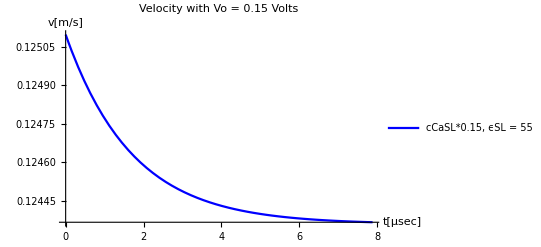

```mathematica
Print["Intracellular conditions"]

veloSP2=Plot[(velocityprop[t/alfa/24*10^-6]/24+1)/alfa*beta,{t,0,24*decaytime*alfa*10^6},PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Velocity with Vo = 0.15 Volts",PlotStyle->Blue,PlotRange->Full,Axes->True,AxesLabel->{"t[μsec]","v[m/s]"}]
```

```mathematica
24*0.329*3.6
```

28.4256

```mathematica
veloSP2Data=Cases[veloSP2,Line[{x__}]->x,∞];
```

{{1.60795×10^-7,0.125097},{0.00241661,0.125096},{0.00483306,0.125095},{0.00966596,0.125093},{0.0193318,0.125089},{0.0386634,0.125081},{0.0773266,0.125064},{0.154653,0.125033},{0.322314,0.12497},{0.478865,0.124917},{0.632345,0.124869},{0.798834,0.124821},{0.954211,0.124781},{1.1226,0.124742},{1.28791,0.124706},{1.44212,0.124676},{1.60933,0.124647},{1.76543,0.124622},{1.91847,0.124599},{2.08451,0.124577},{2.23944,0.124558},{2.40737,0.124539},{2.57224,0.124523},{2.726,0.124509},{2.89276,0.124495},{3.04842,0.124483},{3.21708,0.124471},{3.38267,0.124461},{3.53716,0.124452},{3.70465,0.124443},{3.86103,0.124436},{4.01433,0.124429},{4.18065,0.124423},{4.33586,0.124417},{4.50407,0.124412},{4.66922,0.124407},{4.82325,0.124403},{4.99029,0.124398},{5.14623,0.124395},{5.29909,0.124392},{5.46496,0.124389},{5.61971,0.124386},{5.78748,0.124384},{5.94414,0.124381},{6.09772,0.124379},{6.26432,0.124377},{6.4198,0.124376},{6.58829,0.124374},{6.75371,0.124373},{6.90803,0.124371},{7.07534,0.12437},{7.23155,0.124369},{7.38469,0.124368},{7.55084,0.124367},{7.70587,0.124367},{7.70858,0.124367},{7.71128,0.124367},{7.71669,0.124367},{7.72751,0.124367},{7.74914,0.124366},{7.79241,0.124366},{7.79511,0.124366},{7.79781,0.124366},{7.80322,0.124366},{7.81404,0.124366},{7.83567,0.124366},{7.83838,0.124366},{7.84108,0.124366},{7.84649,0.124366},{7.85731,0.124366},{7.86001,0.124366},{7.86271,0.124366},{7.86812,0.124366},{7.87083,0.124366},{7.87353,0.124366},{7.87623,0.124366},{7.87894,0.124366}}

### Soliton Peak Attenuation plots

```mathematica
(*MM: added ABS[] and divided by 24, not 12*)
```

#### Total

Intracellular conditions

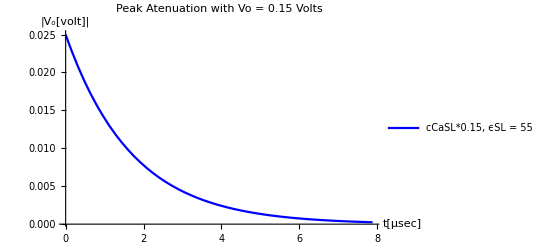

```mathematica
Print["Intracellular conditions"]

peakDecaySP2wSP1Capa=Plot[{Abs[Ω[t/alfa/24*10^-6]^2*gamma*nuZe^(1/2)/24]},{t,0,24*decaytime*alfa*10^6},PlotStyle->Blue,PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Peak Atenuation with Vo = 0.15 Volts",Axes->True,AxesLabel->{"t[μsec]","|V_o[volt]|"},PlotRange->All]
```

```mathematica
peakDecaySP2wSP1CapaData=Cases[peakDecaySP2wSP1Capa,Line[{x__}]->x,∞];
```

{{1.60795×10^-7,0.025},{0.00241661,0.0249647},{0.00483306,0.0249294},{0.00966596,0.0248591},{0.0193318,0.024719},{0.0386634,0.0244412},{0.0773266,0.0238948},{0.154653,0.0228385},{0.322314,0.0207059},{0.478865,0.0188948},{0.632345,0.0172732},{0.798834,0.0156712},{0.954211,0.0143104},{1.1226,0.0129689},{1.28791,0.0117742},{1.44212,0.0107593},{1.60933,0.00975741},{1.76543,0.00890648},{1.91847,0.00814437},{2.08451,0.00739107},{2.23944,0.00675116},{2.40737,0.00611995},{2.57224,0.00555773},{2.726,0.00508005},{2.89276,0.00460825},{3.04842,0.00420751},{3.21708,0.00381253},{3.38267,0.00346083},{3.53716,0.00316205},{3.70465,0.00286718},{3.86103,0.00261674},{4.01433,0.00239247},{4.18065,0.00217086},{4.33586,0.00198261},{4.50407,0.00179696},{4.66922,0.00163163},{4.82325,0.00149116},{4.99029,0.00135247},{5.14623,0.00123466},{5.29909,0.00112914},{5.46496,0.00102482},{5.61971,0.000936197},{5.78748,0.00084876},{5.94414,0.000774502},{6.09772,0.000708011},{6.26432,0.000642326},{6.4198,0.000586532},{6.58829,0.000531527},{6.75371,0.000482546},{6.90803,0.000440933},{7.07534,0.000399857},{7.23155,0.000364969},{7.38469,0.000333724},{7.55084,0.000302843},{7.70587,0.000276609},{7.70858,0.000276172},{7.71128,0.000275736},{7.71669,0.000274866},{7.72751,0.000273134},{7.74914,0.000269703},{7.79241,0.000262968},{7.79511,0.000262553},{7.79781,0.000262138},{7.80322,0.000261311},{7.81404,0.000259664},{7.83567,0.000256402},{7.83838,0.000255997},{7.84108,0.000255593},{7.84649,0.000254786},{7.85731,0.000253181},{7.86001,0.000252781},{7.86271,0.000252382},{7.86812,0.000251585},{7.87083,0.000251188},{7.87353,0.000250791},{7.87623,0.000250395},{7.87894,0.00025}}

Soliton Propagation plots

```mathematica
(*Vo=0.15V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p15VϵSLEQ78p358cCaEQ50nM=0.000016722898823157003
```

0.0000167229

```mathematica
(*Vo=0.05V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM=0.000016787268912085657
```

0.0000167873

```mathematica
tmaxThisFile=24*decaytime*alfa
```

7.87894×10^-6

## Soliton Normalized

#### Normalized - regular

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

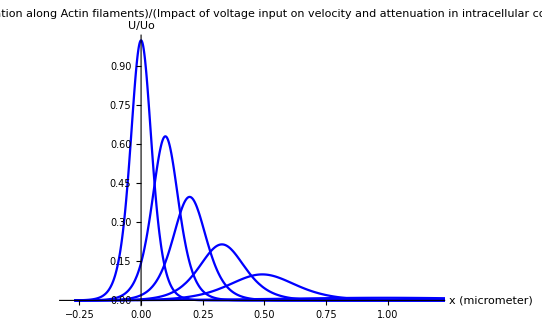

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/10]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/5]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/3]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/2]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data=Cases[SolNormTot,Line[{x__}]->x,∞];
```

{{-0.27,0.000318286},{-0.268476,0.000335696},{-0.266953,0.000354058},{-0.263905,0.00039385},{-0.262382,0.000415393},{-0.260858,0.000438114},{-0.257811,0.00048735},{-0.256287,0.000514006},{-0.254763,0.000542119},{-0.251716,0.000603041},{-0.250192,0.000636022},{-0.248668,0.000670806},{-0.245621,0.000746184},{-0.244097,0.000786991},{-0.242574,0.000830028},{-0.239526,0.000923289},{-0.238003,0.000973777},{-0.236479,0.00102702},{-0.233432,0.00114241},{-0.231908,0.00120487},{-0.230384,0.00127074},{-0.227337,0.00141349},{-0.225813,0.00149076},{-0.22429,0.00157225},{-0.221242,0.00174884},{-0.219719,0.00184443},{-0.218195,0.00194524},{-0.215148,0.00216366},{-0.213624,0.0022819},{-0.2121,0.00240659},{-0.209053,0.00267676},{-0.207529,0.00282299},{-0.206006,0.0029772},{-0.202958,0.00331132},{-0.201435,0.00349216},{-0.199911,0.00368286},{-0.196864,0.00409601},{-0.19534,0.00431961},{-0.193816,0.00455539},{-0.190769,0.00506617},{-0.189245,0.00534259},{-0.187722,0.00563405},{-0.184674,0.00626539},{-0.183151,0.00660703},{-0.181627,0.00696724},{-0.17858,0.00774739},{-0.177056,0.00816951},{-0.175532,0.00861452},{-0.172485,0.00957824},{-0.170833,0.0101447},{-0.169181,0.0107445},{-0.165877,0.012052},{-0.164226,0.0127638},{-0.162574,0.0135174},{-0.15927,0.0151597},{-0.157618,0.0160536},{-0.155966,0.0169997},{-0.152663,0.019061},{-0.151011,0.0201826},{-0.149359,0.0213694},{-0.146055,0.023954},{-0.144404,0.0253598},{-0.142752,0.0268469},{-0.139448,0.0300838},{-0.137796,0.0318435},{-0.136144,0.0337043},{-0.132841,0.0377519},{-0.131189,0.0399507},{-0.129537,0.0422749},{-0.126233,0.0473265},{-0.124582,0.0500685},{-0.12293,0.0529649},{-0.119626,0.0592542},{-0.117974,0.0626645},{-0.116322,0.0662641},{-0.113019,0.0740705},{-0.111367,0.0782978},{-0.109715,0.0827556},{-0.106411,0.092408},{-0.10476,0.0976263},{-0.103108,0.103123},{-0.099804,0.115},{-0.0981522,0.121408},{-0.0965003,0.128148},{-0.0931967,0.142676},{-0.0915448,0.150494},{-0.089893,0.158701},{-0.0865893,0.176338},{-0.0849375,0.185798},{-0.0832856,0.195705},{-0.079982,0.216915},{-0.0783301,0.228245},{-0.0766783,0.240076},{-0.0733746,0.265285},{-0.0667673,0.322148},{-0.0652249,0.336691},{-0.0636825,0.351718},{-0.0605978,0.383218},{-0.0544283,0.451813},{-0.0528859,0.470058},{-0.0513436,0.488706},{-0.0482588,0.527112},{-0.0420893,0.607461},{-0.040547,0.628052},{-0.0390046,0.648748},{-0.0359198,0.690233},{-0.0297504,0.771796},{-0.028208,0.791486},{-0.0266656,0.810745},{-0.0235809,0.847654},{-0.0220385,0.865145},{-0.0204961,0.881888},{-0.0174114,0.912813},{-0.015869,0.926844},{-0.0143266,0.939823},{-0.0127843,0.951683},{-0.0112419,0.962361},{-0.00969952,0.971799},{-0.00815715,0.979943},{-0.00661477,0.98675},{-0.0050724,0.99218},{-0.00353003,0.996203},{-0.00198766,0.998794},{-0.000445286,0.999939},{0.00109709,0.999632},{0.00263946,0.997875},{0.00418183,0.994676},{0.0057242,0.990056},{0.00726657,0.98404},{0.00880895,0.976662},{0.0103513,0.967965},{0.0118937,0.957997},{0.0134361,0.946812},{0.0149784,0.934471},{0.0165208,0.921039},{0.0196055,0.891183},{0.0211479,0.874909},{0.0226903,0.85784},{0.025775,0.821638},{0.0319445,0.743194},{0.0334566,0.723178},{0.0349688,0.70299},{0.037993,0.662353},{0.0440415,0.58163},{0.0455536,0.561854},{0.0470657,0.542324},{0.0500899,0.504144},{0.0561384,0.432079},{0.0576505,0.415081},{0.0591626,0.398521},{0.0621869,0.366752},{0.063699,0.351555},{0.0652111,0.336823},{0.0682353,0.308755},{0.0697474,0.295417},{0.0712596,0.282538},{0.0742838,0.258139},{0.0803323,0.214575},{0.0818444,0.204725},{0.0833565,0.19527},{0.0863807,0.177508},{0.0878928,0.169179},{0.089405,0.161202},{0.0924292,0.146261},{0.0939413,0.139275},{0.0954534,0.132597},{0.0984777,0.12012},{0.0999898,0.1143},{0.101502,0.108744},{0.104526,0.0983857},{0.106038,0.093563},{0.10755,0.0889651},{0.110575,0.0804064},{0.112087,0.0764279},{0.113599,0.0726385},{0.116623,0.0655943},{0.118135,0.062324},{0.119647,0.0592115},{0.122672,0.0534321},{0.124184,0.0507518},{0.125696,0.0482024},{0.12872,0.0434729},{0.13036,0.0411005},{0.132001,0.038855},{0.135281,0.0347188},{0.136921,0.032816},{0.138562,0.0310159},{0.141842,0.0277022},{0.143483,0.0261787},{0.145123,0.024738},{0.148403,0.0220874},{0.150044,0.0208694},{0.151684,0.0197179},{0.154964,0.0176004},{0.156605,0.0166277},{0.158245,0.0157084},{0.161526,0.0140184},{0.163166,0.0132423},{0.164806,0.012509},{0.168087,0.0111612},{0.169727,0.0105425},{0.171367,0.00995793},{0.174648,0.00888379},{0.176288,0.00839079},{0.177928,0.00792505},{0.181209,0.0070694},{0.182849,0.00667676},{0.18449,0.00630585},{0.18777,0.00562453},{0.18941,0.00531192},{0.191051,0.00501664},{0.194331,0.0044743},{0.195971,0.00422548},{0.197612,0.00399048},{0.200892,0.00355888},{0.202533,0.00336088},{0.204173,0.00317388},{0.207453,0.00283048},{0.209094,0.00267295},{0.210734,0.00252418},{0.214015,0.00225099},{0.215655,0.00212568},{0.217295,0.00200734},{0.220576,0.00179004},{0.222216,0.00169037},{0.223856,0.00159624},{0.227137,0.00142341},{0.228777,0.00134414},{0.230417,0.00126928},{0.233698,0.00113183},{0.235229,0.00107289},{0.23676,0.00101701},{0.239821,0.000913829},{0.241352,0.000866232},{0.242883,0.000821113},{0.245944,0.000737801},{0.247475,0.000699369},{0.249006,0.000662939},{0.252068,0.00059567},{0.253599,0.00056464},{0.255129,0.000535226},{0.258191,0.000480913},{0.259722,0.000455859},{0.261253,0.000432111},{0.264314,0.00038826},{0.265845,0.000368032},{0.267376,0.000348858},{0.270437,0.000313455},{0.271968,0.000297124},{0.273499,0.000281643},{0.276561,0.00025306},{0.278092,0.000239875},{0.279622,0.000227377},{0.282684,0.000204301},{0.284215,0.000193656},{0.285746,0.000183566},{0.288807,0.000164936},{0.290338,0.000156342},{0.291869,0.000148196},{0.294931,0.000133155},{0.296461,0.000126217},{0.297992,0.00011964},{0.301054,0.000107498},{0.302585,0.000101896},{0.304115,0.000096587},{0.307177,0.0000867838},{0.308708,0.0000822619},{0.310239,0.0000779756},{0.3133,0.0000700613},{0.314831,0.0000664107},{0.316362,0.0000629503},{0.319424,0.000056561},{0.320954,0.0000536138},{0.322485,0.0000508202},{0.325547,0.000045662},{0.327078,0.0000432827},{0.328608,0.0000410274},{0.33167,0.0000368632},{0.333329,0.0000347862},{0.334988,0.0000328262},{0.338306,0.0000292312},{0.339965,0.0000275842},{0.341624,0.00002603},{0.344942,0.0000231794},{0.346601,0.0000218733},{0.34826,0.0000206409},{0.351578,0.0000183804},{0.353237,0.0000173448},{0.354896,0.0000163675},{0.358214,0.000014575},{0.359873,0.0000137538},{0.361532,0.0000129788},{0.36485,0.0000115574},{0.366509,0.0000109062},{0.368168,0.0000102917},{0.371486,9.16463×10^-6},{0.373145,8.64825×10^-6},{0.374804,8.16097×10^-6},{0.378122,7.26722×10^-6},{0.37978,6.85775×10^-6},{0.381439,6.47135×10^-6},{0.384757,5.76264×10^-6},{0.386416,5.43794×10^-6},{0.388075,5.13154×10^-6},{0.391393,4.56956×10^-6},{0.393052,4.31209×10^-6},{0.394711,4.06912×10^-6},{0.398029,3.62349×10^-6},{0.399688,3.41932×10^-6},{0.401347,3.22666×10^-6},{0.404665,2.87329×10^-6},{0.406324,2.7114×10^-6},{0.407983,2.55862×10^-6},{0.411301,2.27841×10^-6},{0.41296,2.15004×10^-6},{0.414619,2.02889×10^-6},{0.417937,1.8067×10^-6},{0.419596,1.7049×10^-6},{0.421255,1.60884×10^-6},{0.424573,1.43264×10^-6},{0.426232,1.35192×10^-6},{0.427891,1.27575×10^-6},{0.431209,1.13603×10^-6},{0.432868,1.07202×10^-6},{0.434527,1.01162×10^-6},{0.437845,9.00832×10^-7},{0.439473,8.50974×10^-7},{0.441102,8.03875×10^-7},{0.44436,7.17354×10^-7},{0.445988,6.77651×10^-7},{0.447617,6.40146×10^-7},{0.450875,5.71247×10^-7},{0.452503,5.3963×10^-7},{0.454132,5.09764×10^-7},{0.457389,4.54898×10^-7},{0.459018,4.29721×10^-7},{0.460647,4.05937×10^-7},{0.463904,3.62246×10^-7},{0.465533,3.42197×10^-7},{0.467162,3.23258×10^-7},{0.470419,2.88466×10^-7},{0.472048,2.725×10^-7},{0.473677,2.57418×10^-7},{0.476934,2.29712×10^-7},{0.478563,2.16998×10^-7},{0.480192,2.04988×10^-7},{0.483449,1.82925×10^-7},{0.485078,1.72801×10^-7},{0.486706,1.63237×10^-7},{0.489964,1.45668×10^-7},{0.491593,1.37606×10^-7},{0.493221,1.2999×10^-7},{0.496479,1.15999×10^-7},{0.498108,1.09579×10^-7},{0.499736,1.03514×10^-7},{0.502994,9.23728×10^-8},{0.504622,8.72603×10^-8},{0.506251,8.24307×10^-8},{0.509509,7.35587×10^-8},{0.511137,6.94875×10^-8},{0.512766,6.56416×10^-8},{0.516023,5.85766×10^-8},{0.517652,5.53346×10^-8},{0.519281,5.2272×10^-8},{0.522538,4.6646×10^-8},{0.524167,4.40643×10^-8},{0.525796,4.16255×10^-8},{0.529053,3.71453×10^-8},{0.530682,3.50895×10^-8},{0.532311,3.31474×10^-8},{0.535568,2.95797×10^-8},{0.537197,2.79426×10^-8},{0.538826,2.63961×10^-8},{0.542083,2.35551×10^-8},{0.543602,2.23367×10^-8},{0.545122,2.11813×10^-8},{0.54816,1.90468×10^-8},{0.549679,1.80616×10^-8},{0.551199,1.71274×10^-8},{0.554237,1.54014×10^-8},{0.555756,1.46047×10^-8},{0.557276,1.38493×10^-8},{0.560314,1.24537×10^-8},{0.561833,1.18095×10^-8},{0.563353,1.11987×10^-8},{0.566391,1.00701×10^-8},{0.56791,9.54925×10^-9},{0.56943,9.05532×10^-9},{0.572468,8.14278×10^-9},{0.573987,7.72159×10^-9},{0.575507,7.3222×10^-9},{0.578545,6.58431×10^-9},{0.580065,6.24374×10^-9},{0.581584,5.92078×10^-9},{0.584622,5.32412×10^-9},{0.586142,5.04873×10^-9},{0.587661,4.78759×10^-9},{0.590699,4.30512×10^-9},{0.592219,4.08244×10^-9},{0.593738,3.87128×10^-9},{0.596776,3.48115×10^-9},{0.598296,3.30109×10^-9},{0.599815,3.13034×10^-9},{0.602853,2.81489×10^-9},{0.604373,2.66929×10^-9},{0.605892,2.53122×10^-9},{0.60893,2.27614×10^-9},{0.61045,2.1584×10^-9},{0.611969,2.04676×10^-9},{0.615007,1.8405×10^-9},{0.616527,1.7453×10^-9},{0.618046,1.65503×10^-9},{0.621085,1.48824×10^-9},{0.622604,1.41126×10^-9},{0.624123,1.33827×10^-9},{0.627162,1.2034×10^-9},{0.628681,1.14116×10^-9},{0.6302,1.08213×10^-9},{0.633239,9.73081×10^-10},{0.634758,9.22748×10^-10},{0.636277,8.75019×10^-10},{0.639316,7.8684×10^-10},{0.640963,7.42806×10^-10},{0.64261,7.01235×10^-10},{0.645905,6.24944×10^-10},{0.647553,5.8997×10^-10},{0.6492,5.56953×10^-10},{0.652495,4.96359×10^-10},{0.654142,4.6858×10^-10},{0.65579,4.42357×10^-10},{0.659085,3.9423×10^-10},{0.660732,3.72168×10^-10},{0.66238,3.5134×10^-10},{0.665674,3.13115×10^-10},{0.667322,2.95592×10^-10},{0.668969,2.7905×10^-10},{0.672264,2.4869×10^-10},{0.673911,2.34773×10^-10},{0.675559,2.21634×10^-10},{0.678854,1.97521×10^-10},{0.680501,1.86467×10^-10},{0.682149,1.76032×10^-10},{0.685443,1.5688×10^-10},{0.687091,1.48101×10^-10},{0.688738,1.39812×10^-10},{0.692033,1.24601×10^-10},{0.693681,1.17628×10^-10},{0.695328,1.11045×10^-10},{0.698623,9.89639×10^-11},{0.70027,9.34255×10^-11},{0.701918,8.81971×10^-11},{0.705213,7.86016×10^-11},{0.70686,7.42027×10^-11},{0.708507,7.00501×10^-11},{0.711802,6.24289×10^-11},{0.71345,5.89352×10^-11},{0.715097,5.56369×10^-11},{0.718392,4.95839×10^-11},{0.720039,4.6809×10^-11},{0.721687,4.41893×10^-11},{0.724982,3.93817×10^-11},{0.726629,3.71778×10^-11},{0.728276,3.50972×10^-11},{0.731571,3.12787×10^-11},{0.733219,2.95283×10^-11},{0.734866,2.78757×10^-11},{0.738161,2.4843×10^-11},{0.739808,2.34527×10^-11},{0.741456,2.21402×10^-11},{0.744751,1.97314×10^-11},{0.746289,1.86986×10^-11},{0.747827,1.77198×10^-11},{0.750902,1.59133×10^-11},{0.75244,1.50803×10^-11},{0.753978,1.4291×10^-11},{0.757054,1.2834×10^-11},{0.758592,1.21622×10^-11},{0.76013,1.15256×10^-11},{0.763206,1.03506×10^-11},{0.764744,9.80878×10^-12},{0.766282,9.29535×10^-12},{0.769358,8.3477×10^-12},{0.770896,7.91074×10^-12},{0.772434,7.49666×10^-12},{0.77551,6.73238×10^-12},{0.777048,6.37998×10^-12},{0.778586,6.04602×10^-12},{0.781662,5.42964×10^-12},{0.7832,5.14543×10^-12},{0.784738,4.87609×10^-12},{0.787813,4.37898×10^-12},{0.789351,4.14976×10^-12},{0.790889,3.93255×10^-12},{0.793965,3.53163×10^-12},{0.795503,3.34677×10^-12},{0.797041,3.17158×10^-12},{0.800117,2.84824×10^-12},{0.801655,2.69915×10^-12},{0.803193,2.55787×10^-12},{0.806269,2.2971×10^-12},{0.807807,2.17686×10^-12},{0.809345,2.06291×10^-12},{0.812421,1.8526×10^-12},{0.813959,1.75563×10^-12},{0.815497,1.66373×10^-12},{0.818573,1.49411×10^-12},{0.820111,1.4159×10^-12},{0.821649,1.34179×10^-12},{0.824724,1.205×10^-12},{0.826262,1.14192×10^-12},{0.8278,1.08215×10^-12},{0.830876,9.71824×10^-13},{0.832414,9.20954×10^-13},{0.833952,8.72747×10^-13},{0.837028,7.83772×10^-13},{0.838566,7.42746×10^-13},{0.840104,7.03867×10^-13},{0.84318,6.32109×10^-13},{0.844688,5.99655×10^-13},{0.846195,5.68868×10^-13},{0.849211,5.11954×10^-13},{0.850718,4.8567×10^-13},{0.852226,4.60735×10^-13},{0.855242,4.14639×10^-13},{0.856749,3.93351×10^-13},{0.858257,3.73156×10^-13},{0.861272,3.35823×10^-13},{0.86278,3.18581×10^-13},{0.864288,3.02225×10^-13},{0.867303,2.71988×10^-13},{0.868811,2.58024×10^-13},{0.870319,2.44776×10^-13},{0.873334,2.20287×10^-13},{0.874842,2.08977×10^-13},{0.876349,1.98248×10^-13},{0.879365,1.78414×10^-13},{0.880873,1.69254×10^-13},{0.88238,1.60564×10^-13},{0.885396,1.445×10^-13},{0.886903,1.37081×10^-13},{0.888411,1.30043×10^-13},{0.891426,1.17033×10^-13},{0.892934,1.11024×10^-13},{0.894442,1.05324×10^-13},{0.897457,9.47866×10^-14},{0.898965,8.99201×10^-14},{0.900473,8.53034×10^-14},{0.903488,7.67691×10^-14},{0.904996,7.28276×10^-14},{0.906503,6.90885×10^-14},{0.909519,6.21764×10^-14},{0.911027,5.89842×10^-14},{0.912534,5.59558×10^-14},{0.91555,5.03576×10^-14},{0.917057,4.77722×10^-14},{0.918565,4.53195×10^-14},{0.92158,4.07854×10^-14},{0.923088,3.86914×10^-14},{0.924596,3.67049×10^-14},{0.927611,3.30327×10^-14},{0.929119,3.13367×10^-14},{0.930627,2.97279×10^-14},{0.933642,2.67537×10^-14},{0.93515,2.53801×10^-14},{0.936658,2.4077×10^-14},{0.939673,2.16682×10^-14},{0.941309,2.04638×10^-14},{0.942945,1.93264×10^-14},{0.946216,1.72377×10^-14},{0.947852,1.62796×10^-14},{0.949488,1.53747×10^-14},{0.95276,1.37131×10^-14},{0.954396,1.29509×10^-14},{0.956032,1.2231×10^-14},{0.959303,1.09092×10^-14},{0.960939,1.03028×10^-14},{0.962575,9.73016×10^-15},{0.965847,8.67857×10^-15},{0.967483,8.19619×10^-15},{0.969118,7.74063×10^-15},{0.97239,6.90406×10^-15},{0.974026,6.52031×10^-15},{0.975662,6.1579×10^-15},{0.978934,5.49238×10^-15},{0.98057,5.1871×10^-15},{0.982205,4.89879×10^-15},{0.985477,4.36935×10^-15},{0.988749,3.89713×10^-15},{0.992021,3.47595×10^-15},{0.995292,3.10028×10^-15},{0.998564,2.76522×10^-15},{1.00184,2.46637×10^-15},{1.00511,2.19981×10^-15},{1.00838,1.96207×10^-15},{1.01165,1.75002×10^-15},{1.01492,1.56088×10^-15},{1.01819,1.39219×10^-15},{1.02147,1.24173×10^-15},{1.02474,1.10753×10^-15},{1.02801,9.87831×10^-16},{1.03128,8.81071×10^-16},{1.03782,7.00918×10^-16},{1.04437,5.57601×10^-16},{1.04589,5.28627×10^-16},{1.04742,5.01159×10^-16},{1.05047,4.5043×10^-16},{1.05658,3.63857×10^-16},{1.05811,3.44951×10^-16},{1.05963,3.27027×10^-16},{1.06269,2.93924×10^-16},{1.06879,2.37432×10^-16},{1.07032,2.25095×10^-16},{1.07184,2.13398×10^-16},{1.0749,1.91798×10^-16},{1.081,1.54934×10^-16},{1.09321,1.01101×10^-16},{1.09474,9.58475×10^-17},{1.09627,9.08671×10^-17},{1.09932,8.16693×10^-17},{1.10542,6.59724×10^-17},{1.11764,4.30497×10^-17},{1.14206,1.8331×10^-17},{1.14371,1.73008×10^-17},{1.14537,1.63285×10^-17},{1.14868,1.45448×10^-17},{1.15529,1.15406×10^-17},{1.16853,7.26556×10^-18},{1.195,2.87973×10^-18},{1.24795,4.52395×10^-19},{1.35191,1.19467×10^-20},{1.44886,4.03031×10^-22},{1.55401,1.0207×10^-23},{1.65216,3.30234×10^-25},{1.7585,8.02073×10^-27},{1.86292,2.08451×10^-28},{1.96032,6.92078×10^-30},{2.06593,1.72495×10^-31},{2.16454,5.49236×10^-33},{2.26121,1.87128×10^-34},{2.36608,4.78618×10^-36},{2.46394,1.56387×10^-37},{2.57001,3.83603×10^-39},{2.67414,1.00684×10^-40},{2.77126,3.37599×10^-42},{2.87659,8.49789×10^-44},{2.97491,2.73264×10^-45},{3.0713,9.40269×10^-47},{3.17588,2.4288×10^-48},{3.27346,8.01478×10^-50},{3.37925,1.98546×10^-51},{3.47803,6.28339×10^-53},{3.57487,2.12776×10^-54},{3.67991,5.40907×10^-56},{3.77795,1.75664×10^-57},{3.88419,4.28266×10^-59},{3.9885,1.11723×10^-60},{4.0858,3.72333×10^-62},{4.1913,9.31516×10^-64},{4.2898,2.97722×10^-65},{4.38636,1.01819×10^-66},{4.49112,2.61408×10^-68},{4.58887,8.57369×10^-70},{4.59058,8.07758×10^-70},{4.59228,7.61017×10^-70},{4.59569,6.75493×10^-70},{4.60252,5.32198×10^-70},{4.61616,3.30353×10^-70},{4.64344,1.27289×10^-70},{4.64514,1.19923×10^-70},{4.64685,1.12984×10^-70},{4.65026,1.00286×10^-70},{4.65708,7.90123×10^-71},{4.67072,4.90456×10^-71},{4.67242,4.62076×10^-71},{4.67413,4.35338×10^-71},{4.67754,3.86414×10^-71},{4.68436,3.04443×10^-71},{4.68606,2.86826×10^-71},{4.68777,2.70229×10^-71},{4.69118,2.3986×10^-71},{4.69288,2.25981×10^-71},{4.69459,2.12904×10^-71},{4.69629,2.00585×10^-71},{4.698,1.88978×10^-71},{-0.27,0.0000909806},{-0.268476,0.000094912},{-0.266953,0.0000990133},{-0.263905,0.000107755},{-0.262382,0.000112411},{-0.260858,0.000117269},{-0.257811,0.000127622},{-0.256287,0.000133136},{-0.254763,0.000138889},{-0.251716,0.000151151},{-0.245621,0.000179018},{-0.244097,0.000186753},{-0.242574,0.000194822},{-0.239526,0.000212021},{-0.238003,0.000221182},{-0.236479,0.000230739},{-0.233432,0.000251108},{-0.231908,0.000261957},{-0.230384,0.000273275},{-0.227337,0.000297399},{-0.221242,0.00035222},{-0.219719,0.000367437},{-0.218195,0.000383311},{-0.215148,0.000417145},{-0.213624,0.000435165},{-0.2121,0.000453964},{-0.209053,0.000494031},{-0.207529,0.000515372},{-0.206006,0.000537634},{-0.202958,0.000585083},{-0.196864,0.000692907},{-0.19534,0.000722833},{-0.193816,0.000754051},{-0.190769,0.000820588},{-0.189245,0.000856025},{-0.187722,0.000892992},{-0.184674,0.000971779},{-0.183151,0.00101374},{-0.181627,0.00105751},{-0.17858,0.0011508},{-0.172485,0.00136277},{-0.170833,0.00142665},{-0.169181,0.00149353},{-0.165877,0.00163683},{-0.164226,0.00171355},{-0.162574,0.00179386},{-0.15927,0.00196592},{-0.157618,0.00205804},{-0.155966,0.00215447},{-0.152663,0.00236106},{-0.151011,0.00247165},{-0.149359,0.00258742},{-0.146055,0.00283543},{-0.144404,0.00296819},{-0.142752,0.00310716},{-0.139448,0.00340486},{-0.137796,0.00356421},{-0.136144,0.00373099},{-0.132841,0.00408826},{-0.131189,0.00427949},{-0.129537,0.00447963},{-0.126233,0.0049083},{-0.124582,0.00513773},{-0.12293,0.00537783},{-0.119626,0.00589206},{-0.117974,0.00616724},{-0.116322,0.0064552},{-0.113019,0.00707187},{-0.111367,0.00740182},{-0.109715,0.00774708},{-0.106411,0.00848632},{-0.10476,0.0088818},{-0.103108,0.00929557},{-0.099804,0.0101814},{-0.0981522,0.0106552},{-0.0965003,0.0111508},{-0.0931967,0.0122116},{-0.0915448,0.0127789},{-0.089893,0.0133723},{-0.0865893,0.014642},{-0.0849375,0.0153208},{-0.0832856,0.0160307},{-0.079982,0.0175492},{-0.0783301,0.0183607},{-0.0766783,0.0192092},{-0.0733746,0.0210237},{-0.0717228,0.021993},{-0.070071,0.0230063},{-0.0667673,0.0251719},{-0.0652249,0.0262502},{-0.0636825,0.0273736},{-0.0605978,0.0297632},{-0.0590554,0.0310331},{-0.0575131,0.0323557},{-0.0544283,0.0351674},{-0.0528859,0.0366608},{-0.0513436,0.0382156},{-0.0482588,0.0415189},{-0.0420893,0.04897},{-0.040547,0.0510243},{-0.0390046,0.0531609},{-0.0359198,0.0576925},{-0.0343775,0.0600938},{-0.0328351,0.0625895},{-0.0297504,0.0678773},{-0.028208,0.0706762},{-0.0266656,0.0735829},{-0.0235809,0.0797339},{-0.0174114,0.0934876},{-0.015869,0.0972501},{-0.0143266,0.10115},{-0.0112419,0.109375},{-0.00969952,0.113709},{-0.00815715,0.118195},{-0.0050724,0.127637},{-0.00353003,0.132601},{-0.00198766,0.137732},{0.00109709,0.148506},{0.00726657,0.172191},{0.00880895,0.178572},{0.0103513,0.185142},{0.0134361,0.198853},{0.0196055,0.228583},{0.0211479,0.236496},{0.0226903,0.244598},{0.025775,0.261363},{0.0319445,0.297031},{0.0334566,0.306179},{0.0349688,0.315474},{0.037993,0.334471},{0.0440415,0.373823},{0.0561384,0.454985},{0.0576505,0.465035},{0.0591626,0.474999},{0.0621869,0.494579},{0.063699,0.50415},{0.0652111,0.513544},{0.0682353,0.531709},{0.0697474,0.540432},{0.0712596,0.548884},{0.0742838,0.564878},{0.0757959,0.572374},{0.077308,0.579506},{0.0803323,0.592591},{0.0818444,0.598503},{0.0833565,0.603968},{0.0848686,0.60897},{0.0863807,0.613491},{0.0878928,0.617515},{0.089405,0.621031},{0.0909171,0.624024},{0.0924292,0.626486},{0.0939413,0.628407},{0.0954534,0.629781},{0.0969655,0.630603},{0.0984777,0.63087},{0.0999898,0.630581},{0.101502,0.629737},{0.103014,0.628341},{0.104526,0.626398},{0.106038,0.623915},{0.10755,0.620901},{0.109062,0.617365},{0.110575,0.61332},{0.112087,0.60878},{0.113599,0.60376},{0.115111,0.598276},{0.116623,0.592347},{0.118135,0.585991},{0.119647,0.579229},{0.122672,0.564572},{0.124184,0.556722},{0.125696,0.548553},{0.12872,0.531357},{0.13036,0.521606},{0.132001,0.511594},{0.135281,0.490912},{0.141842,0.447729},{0.154964,0.359915},{0.156605,0.349229},{0.158245,0.338665},{0.161526,0.317961},{0.168087,0.278556},{0.169727,0.269174},{0.171367,0.259993},{0.174648,0.242252},{0.181209,0.209339},{0.182849,0.201655},{0.18449,0.194188},{0.18777,0.179903},{0.18941,0.173082},{0.191051,0.166472},{0.194331,0.153875},{0.195971,0.147882},{0.197612,0.142088},{0.200892,0.131081},{0.207453,0.111278},{0.209094,0.106762},{0.210734,0.102412},{0.214015,0.0941896},{0.215655,0.090308},{0.217295,0.0865735},{0.220576,0.079528},{0.222216,0.0762081},{0.223856,0.0730176},{0.227137,0.067008},{0.233698,0.0563593},{0.235229,0.0541168},{0.23676,0.0519596},{0.239821,0.047889},{0.241352,0.0459702},{0.242883,0.0441253},{0.245944,0.0406471},{0.247475,0.0390087},{0.249006,0.0374343},{0.252068,0.0344681},{0.258191,0.0292053},{0.259722,0.0280172},{0.261253,0.0268764},{0.264314,0.0247294},{0.265845,0.0237199},{0.267376,0.0227507},{0.270437,0.0209276},{0.271968,0.0200707},{0.273499,0.0192483},{0.276561,0.0177018},{0.282684,0.0149671},{0.284215,0.0143514},{0.285746,0.0137607},{0.288807,0.0126506},{0.290338,0.0121292},{0.291869,0.0116291},{0.294931,0.0106895},{0.296461,0.0102483},{0.297992,0.00982512},{0.301054,0.00903016},{0.307177,0.00762683},{0.308708,0.00731129},{0.310239,0.00700873},{0.3133,0.00644046},{0.314831,0.00617376},{0.316362,0.00591805},{0.319424,0.00543783},{0.320954,0.00521248},{0.322485,0.00499642},{0.325547,0.00459071},{0.33167,0.00387515},{0.333329,0.00370121},{0.334988,0.00353505},{0.338306,0.00322472},{0.339965,0.00307991},{0.341624,0.00294158},{0.344942,0.00268324},{0.346601,0.00256268},{0.34826,0.00244754},{0.351578,0.00223251},{0.353237,0.00213217},{0.354896,0.00203634},{0.358214,0.00185739},{0.359873,0.00177389},{0.361532,0.00169413},{0.36485,0.00154521},{0.366509,0.00147573},{0.368168,0.00140937},{0.371486,0.00128546},{0.373145,0.00122764},{0.374804,0.00117243},{0.378122,0.00106933},{0.37978,0.00102123},{0.381439,0.000975288},{0.384757,0.000889513},{0.386416,0.000849495},{0.388075,0.000811276},{0.391393,0.000739916},{0.393052,0.000706625},{0.394711,0.00067483},{0.398029,0.000615467},{0.399688,0.000587772},{0.401347,0.000561323},{0.404665,0.00051194},{0.406324,0.000488902},{0.407983,0.000466901},{0.411301,0.000425822},{0.41296,0.000406658},{0.414619,0.000388357},{0.417937,0.000354186},{0.419596,0.000338246},{0.421255,0.000323022},{0.424573,0.000294599},{0.426232,0.00028134},{0.427891,0.000268677},{0.431209,0.000245035},{0.432868,0.000234006},{0.434527,0.000223473},{0.437845,0.000203808},{0.439473,0.000194798},{0.441102,0.000186186},{0.44436,0.000170087},{0.445988,0.000162567},{0.447617,0.00015538},{0.450875,0.000141945},{0.452503,0.000135669},{0.454132,0.000129671},{0.457389,0.000118458},{0.459018,0.000113221},{0.460647,0.000108215},{0.463904,0.0000988578},{0.465533,0.000094487},{0.467162,0.0000903095},{0.470419,0.0000825002},{0.472048,0.0000788526},{0.473677,0.0000753662},{0.476934,0.0000688491},{0.478563,0.000065805},{0.480192,0.0000628955},{0.483449,0.0000574567},{0.485078,0.0000549163},{0.486706,0.0000524882},{0.489964,0.0000479493},{0.491593,0.0000458293},{0.493221,0.0000438029},{0.496479,0.0000400151},{0.498108,0.0000382458},{0.499736,0.0000365548},{0.502994,0.0000333937},{0.504622,0.0000319172},{0.506251,0.000030506},{0.509509,0.0000278679},{0.511137,0.0000266357},{0.512766,0.000025458},{0.516023,0.0000232565},{0.517652,0.0000222282},{0.519281,0.0000212454},{0.522538,0.0000194082},{0.524167,0.00001855},{0.525796,0.0000177298},{0.529053,0.0000161966},{0.530682,0.0000154805},{0.532311,0.000014796},{0.535568,0.0000135165},{0.537197,0.0000129188},{0.538826,0.0000123476},{0.542083,0.0000112798},{0.543602,0.0000108139},{0.545122,0.0000103672},{0.54816,9.52844×10^-6},{0.549679,9.13485×10^-6},{0.551199,8.75752×10^-6},{0.554237,8.04898×10^-6},{0.555756,7.7165×10^-6},{0.557276,7.39776×10^-6},{0.560314,6.79923×10^-6},{0.566391,5.74353×10^-6},{0.56791,5.50628×10^-6},{0.56943,5.27883×10^-6},{0.572468,4.85174×10^-6},{0.573987,4.65133×10^-6},{0.575507,4.4592×10^-6},{0.578545,4.09842×10^-6},{0.580065,3.92912×10^-6},{0.581584,3.76683×10^-6},{0.584622,3.46206×10^-6},{0.590699,2.92451×10^-6},{0.592219,2.80371×10^-6},{0.593738,2.6879×10^-6},{0.596776,2.47043×10^-6},{0.598296,2.36838×10^-6},{0.599815,2.27055×10^-6},{0.602853,2.08685×10^-6},{0.604373,2.00065×10^-6},{0.605892,1.91801×10^-6},{0.60893,1.76283×10^-6},{0.615007,1.48911×10^-6},{0.616527,1.4276×10^-6},{0.618046,1.36863×10^-6},{0.621085,1.2579×10^-6},{0.622604,1.20594×10^-6},{0.624123,1.15613×10^-6},{0.627162,1.06259×10^-6},{0.628681,1.0187×10^-6},{0.6302,9.76617×10^-7},{0.633239,8.97601×10^-7},{0.639316,7.58232×10^-7},{0.640963,7.2433×10^-7},{0.64261,6.91943×10^-7},{0.645905,6.3145×10^-7},{0.647553,6.03216×10^-7},{0.6492,5.76245×10^-7},{0.652495,5.25866×10^-7},{0.654142,5.02353×10^-7},{0.65579,4.79892×10^-7},{0.659085,4.37937×10^-7},{0.660732,4.18356×10^-7},{0.66238,3.9965×10^-7},{0.665674,3.64711×10^-7},{0.667322,3.48403×10^-7},{0.668969,3.32826×10^-7},{0.672264,3.03728×10^-7},{0.673911,2.90148×10^-7},{0.675559,2.77174×10^-7},{0.678854,2.52942×10^-7},{0.680501,2.41633×10^-7},{0.682149,2.30829×10^-7},{0.685443,2.10648×10^-7},{0.687091,2.0123×10^-7},{0.688738,1.92232×10^-7},{0.692033,1.75426×10^-7},{0.693681,1.67582×10^-7},{0.695328,1.60089×10^-7},{0.698623,1.46094×10^-7},{0.70027,1.39561×10^-7},{0.701918,1.33321×10^-7},{0.705213,1.21666×10^-7},{0.70686,1.16226×10^-7},{0.708507,1.11029×10^-7},{0.711802,1.01322×10^-7},{0.71345,9.67917×10^-8},{0.715097,9.24639×10^-8},{0.718392,8.43802×10^-8},{0.720039,8.06074×10^-8},{0.721687,7.70032×10^-8},{0.724982,7.02712×10^-8},{0.726629,6.71292×10^-8},{0.728276,6.41277×10^-8},{0.731571,5.85213×10^-8},{0.733219,5.59046×10^-8},{0.734866,5.3405×10^-8},{0.738161,4.8736×10^-8},{0.739808,4.65569×10^-8},{0.741456,4.44753×10^-8},{0.744751,4.0587×10^-8},{0.746289,3.88903×10^-8},{0.747827,3.72645×10^-8},{0.750902,3.4214×10^-8},{0.75244,3.27837×10^-8},{0.753978,3.14132×10^-8},{0.757054,2.88416×10^-8},{0.758592,2.76359×10^-8},{0.76013,2.64806×10^-8},{0.763206,2.43129×10^-8},{0.769358,2.04952×10^-8},{0.770896,1.96384×10^-8},{0.772434,1.88175×10^-8},{0.77551,1.7277×10^-8},{0.777048,1.65548×10^-8},{0.778586,1.58627×10^-8},{0.781662,1.45642×10^-8},{0.7832,1.39553×10^-8},{0.784738,1.33719×10^-8},{0.787813,1.22773×10^-8},{0.793965,1.03495×10^-8},{0.795503,9.91684×10^-9},{0.797041,9.50227×10^-9},{0.800117,8.7244×10^-9},{0.801655,8.35968×10^-9},{0.803193,8.01021×10^-9},{0.806269,7.35449×10^-9},{0.807807,7.04704×10^-9},{0.809345,6.75244×10^-9},{0.812421,6.19967×10^-9},{0.818573,5.22619×10^-9},{0.820111,5.00771×10^-9},{0.821649,4.79837×10^-9},{0.824724,4.40557×10^-9},{0.826262,4.2214×10^-9},{0.8278,4.04492×10^-9},{0.830876,3.7138×10^-9},{0.832414,3.55855×10^-9},{0.833952,3.40978×10^-9},{0.837028,3.13065×10^-9},{0.84318,2.63907×10^-9},{0.844688,2.53087×10^-9},{0.846195,2.42711×10^-9},{0.849211,2.23217×10^-9},{0.850718,2.14065×10^-9},{0.852226,2.05289×10^-9},{0.855242,1.88801×10^-9},{0.856749,1.8106×10^-9},{0.858257,1.73637×10^-9},{0.861272,1.59691×10^-9},{0.867303,1.35069×10^-9},{0.868811,1.29531×10^-9},{0.870319,1.2422×10^-9},{0.873334,1.14243×10^-9},{0.874842,1.0956×10^-9},{0.876349,1.05068×10^-9},{0.879365,9.66289×10^-10},{0.880873,9.26672×10^-10},{0.88238,8.88679×10^-10},{0.885396,8.17303×10^-10},{0.891426,6.91288×10^-10},{0.892934,6.62946×10^-10},{0.894442,6.35765×10^-10},{0.897457,5.84702×10^-10},{0.898965,5.6073×10^-10},{0.900473,5.3774×10^-10},{0.903488,4.94551×10^-10},{0.904996,4.74274×10^-10},{0.906503,4.5483×10^-10},{0.909519,4.18299×10^-10},{0.91555,3.53804×10^-10},{0.917057,3.39298×10^-10},{0.918565,3.25387×10^-10},{0.92158,2.99253×10^-10},{0.923088,2.86984×10^-10},{0.924596,2.75218×10^-10},{0.927611,2.53113×10^-10},{0.929119,2.42735×10^-10},{0.930627,2.32784×10^-10},{0.933642,2.14087×10^-10},{0.939673,1.81078×10^-10},{0.941309,1.73037×10^-10},{0.942945,1.65353×10^-10},{0.946216,1.50994×10^-10},{0.947852,1.44289×10^-10},{0.949488,1.37882×10^-10},{0.95276,1.25908×10^-10},{0.954396,1.20317×10^-10},{0.956032,1.14974×10^-10},{0.959303,1.0499×10^-10},{0.960939,1.00328×10^-10},{0.962575,9.58727×10^-11},{0.965847,8.75471×10^-11},{0.967483,8.36595×10^-11},{0.969118,7.99446×10^-11},{0.97239,7.30022×10^-11},{0.974026,6.97605×10^-11},{0.975662,6.66627×10^-11},{0.978934,6.08737×10^-11},{0.98057,5.81706×10^-11},{0.982205,5.55875×10^-11},{0.985477,5.07603×10^-11},{0.987113,4.85062×10^-11},{0.988749,4.63522×10^-11},{0.992021,4.2327×10^-11},{0.993656,4.04475×10^-11},{0.995292,3.86514×10^-11},{0.998564,3.52949×10^-11},{1.0002,3.37276×10^-11},{1.00184,3.22299×10^-11},{1.00511,2.9431×10^-11},{1.00674,2.81241×10^-11},{1.00838,2.68753×10^-11},{1.01165,2.45414×10^-11},{1.01329,2.34516×10^-11},{1.01492,2.24102×10^-11},{1.01819,2.04641×10^-11},{1.01983,1.95554×10^-11},{1.02147,1.8687×10^-11},{1.02474,1.70643×10^-11},{1.02637,1.63065×10^-11},{1.02801,1.55824×10^-11},{1.03128,1.42292×10^-11},{1.03292,1.35974×10^-11},{1.03455,1.29936×10^-11},{1.03782,1.18652×10^-11},{1.03946,1.13383×10^-11},{1.0411,1.08348×10^-11},{1.04437,9.89394×10^-12},{1.04589,9.48337×10^-12},{1.04742,9.08984×10^-12},{1.05047,8.35109×10^-12},{1.052,8.00455×10^-12},{1.05353,7.67238×10^-12},{1.05658,7.04884×10^-12},{1.05811,6.75633×10^-12},{1.05963,6.47596×10^-12},{1.06269,5.94965×10^-12},{1.06879,5.02187×10^-12},{1.07032,4.81348×10^-12},{1.07184,4.61373×10^-12},{1.0749,4.23876×10^-12},{1.07642,4.06287×10^-12},{1.07795,3.89427×10^-12},{1.081,3.57778×10^-12},{1.08253,3.42931×10^-12},{1.08405,3.287×10^-12},{1.08711,3.01986×10^-12},{1.09321,2.54895×10^-12},{1.09474,2.44318×10^-12},{1.09627,2.34179×10^-12},{1.09932,2.15147×10^-12},{1.10085,2.06219×10^-12},{1.10237,1.97662×10^-12},{1.10542,1.81597×10^-12},{1.10695,1.74061×10^-12},{1.10848,1.66838×10^-12},{1.11153,1.53279×10^-12},{1.11764,1.29377×10^-12},{1.11916,1.24008×10^-12},{1.12069,1.18862×10^-12},{1.12374,1.09202×10^-12},{1.12527,1.04671×10^-12},{1.12679,1.00327×10^-12},{1.12985,9.21733×10^-13},{1.13137,8.83484×10^-13},{1.1329,8.46822×10^-13},{1.13595,7.77999×10^-13},{1.14206,6.56679×10^-13},{1.14371,6.27193×10^-13},{1.14537,5.99031×10^-13},{1.14868,5.46443×10^-13},{1.15033,5.21907×10^-13},{1.15199,4.98472×10^-13},{1.15529,4.54713×10^-13},{1.15695,4.34295×10^-13},{1.1586,4.14795×10^-13},{1.16191,3.78381×10^-13},{1.16357,3.61391×10^-13},{1.16522,3.45164×10^-13},{1.16853,3.14863×10^-13},{1.17019,3.00725×10^-13},{1.17184,2.87222×10^-13},{1.17515,2.62007×10^-13},{1.1768,2.50243×10^-13},{1.17846,2.39006×10^-13},{1.18177,2.18024×10^-13},{1.18342,2.08235×10^-13},{1.18508,1.98885×10^-13},{1.18839,1.81425×10^-13},{1.19004,1.73279×10^-13},{1.19169,1.65498×10^-13},{1.195,1.50969×10^-13},{1.19666,1.44191×10^-13},{1.19831,1.37716×10^-13},{1.20162,1.25626×10^-13},{1.20328,1.19986×10^-13},{1.20493,1.14598×10^-13},{1.20824,1.04538×10^-13},{1.2099,9.98438×10^-14},{1.21155,9.53607×10^-14},{1.21486,8.69892×10^-14},{1.21651,8.30832×10^-14},{1.21817,7.93526×10^-14},{1.22148,7.23864×10^-14},{1.22313,6.91362×10^-14},{1.22479,6.60318×10^-14},{1.2281,6.0235×10^-14},{1.22975,5.75304×10^-14},{1.2314,5.49472×10^-14},{1.23471,5.01235×10^-14},{1.23637,4.78729×10^-14},{1.23802,4.57233×10^-14},{1.24133,4.17093×10^-14},{1.24299,3.98365×10^-14},{1.24464,3.80478×10^-14},{1.24795,3.47077×10^-14},{1.24957,3.31771×10^-14},{1.2512,3.1714×10^-14},{1.25445,2.89786×10^-14},{1.25607,2.77006×10^-14},{1.2577,2.6479×10^-14},{1.26094,2.41951×10^-14},{1.26257,2.31282×10^-14},{1.26419,2.21082×10^-14},{1.26744,2.02013×10^-14},{1.26907,1.93104×10^-14},{1.27069,1.84589×10^-14},{1.27394,1.68667×10^-14},{1.27556,1.61229×10^-14},{1.27719,1.54119×10^-14},{1.28044,1.40826×10^-14},{1.28206,1.34616×10^-14},{1.28368,1.28679×10^-14},{1.28693,1.1758×10^-14},{1.28856,1.12395×10^-14},{1.29018,1.07438×10^-14},{1.29343,9.81714×10^-15},{1.29506,9.38421×10^-15},{1.29668,8.97038×10^-15},{1.29993,8.19665×10^-15},{1.30155,7.83518×10^-15},{1.30318,7.48966×10^-15},{1.30643,6.84365×10^-15},{1.30967,6.25336×10^-15},{1.31292,5.71399×10^-15},{1.31617,5.22113×10^-15},{1.31942,4.77079×10^-15},{1.32267,4.35929×10^-15},{1.32592,3.98329×10^-15},{1.32917,3.63972×10^-15},{1.33241,3.32578×10^-15},{1.33566,3.03892×10^-15},{1.33891,2.7768×10^-15},{1.34216,2.53729×10^-15},{1.34541,2.31844×10^-15},{1.34866,2.11847×10^-15},{1.35191,1.93574×10^-15},{1.35797,1.63598×10^-15},{1.36402,1.38264×10^-15},{1.37008,1.16853×10^-15},{1.37614,9.87582×10^-16},{1.3822,8.3465×10^-16},{1.38826,7.05401×10^-16},{1.38978,6.76346×10^-16},{1.39129,6.48487×10^-16},{1.39432,5.96166×10^-16},{1.40038,5.03847×10^-16},{1.4125,3.59883×10^-16},{1.42462,2.57054×10^-16},{1.42613,2.46466×10^-16},{1.42765,2.36314×10^-16},{1.43068,2.17248×10^-16},{1.43674,1.83606×10^-16},{1.44886,1.31144×10^-16},{1.4505,1.25296×10^-16},{1.45214,1.19708×10^-16},{1.45543,1.0927×10^-16},{1.462,9.10435×10^-17},{1.47514,6.32044×10^-17},{1.50143,3.04611×10^-17},{1.55401,7.07524×10^-18},{1.65216,4.63674×10^-19},{1.7585,2.41976×10^-20},{1.86292,1.33255×10^-21},{1.96032,8.91401×10^-23},{2.06593,4.74845×10^-24},{2.16454,3.07264×10^-25},{2.26121,2.09807×10^-26},{2.36608,1.14082×10^-27},{2.46394,7.53523×10^-29},{2.57001,3.96336×10^-30},{2.67414,2.19978×10^-31},{2.77126,1.48312×10^-32},{2.87659,7.96274×10^-34},{2.97491,5.19312×10^-35},{3.0713,3.57392×10^-36},{3.17588,1.95861×10^-37},{3.27346,1.30387×10^-38},{3.37925,6.91205×10^-40},{3.47803,4.45104×10^-41},{3.57487,3.02458×10^-42},{3.67991,1.63665×10^-43},{3.77795,1.0758×10^-44},{3.88419,5.63107×10^-46},{3.9885,3.1103×10^-47},{4.0858,2.08686×10^-48},{4.1913,1.115×10^-49},{4.2898,7.2366×10^-51},{4.38636,4.95616×10^-52},{4.49112,2.70299×10^-53},{4.58887,1.7907×10^-54},{4.59058,1.7079×10^-54},{4.59228,1.62893×10^-54},{4.59569,1.48176×10^-54},{4.60252,1.22612×10^-54},{4.61616,8.39545×10^-55},{4.64344,3.93609×10^-55},{4.64514,3.75408×10^-55},{4.64685,3.58049×10^-55},{4.65026,3.25702×10^-55},{4.65708,2.6951×10^-55},{4.67072,1.84538×10^-55},{4.67242,1.76005×10^-55},{4.67413,1.67866×10^-55},{4.67754,1.52701×10^-55},{4.68436,1.26356×10^-55},{4.68606,1.20513×10^-55},{4.68777,1.14941×10^-55},{4.69118,1.04556×10^-55},{4.69288,9.97217×10^-56},{4.69459,9.51105×10^-56},{4.69629,9.07125×10^-56},{4.698,8.65179×10^-56},{-0.27,0.0000538934},{-0.268476,0.0000557351},{-0.266953,0.0000576397},{-0.263905,0.0000616464},{-0.262382,0.0000637531},{-0.260858,0.0000659317},{-0.257811,0.0000705147},{-0.256287,0.0000729244},{-0.254763,0.0000754164},{-0.251716,0.0000806587},{-0.245621,0.0000922617},{-0.244097,0.0000954144},{-0.242574,0.0000986748},{-0.239526,0.000105534},{-0.238003,0.00010914},{-0.236479,0.000112869},{-0.233432,0.000120714},{-0.231908,0.000124839},{-0.230384,0.000129105},{-0.227337,0.000138079},{-0.221242,0.00015794},{-0.219719,0.000163337},{-0.218195,0.000168918},{-0.215148,0.000180658},{-0.213624,0.00018683},{-0.2121,0.000193214},{-0.209053,0.000206642},{-0.207529,0.000213702},{-0.206006,0.000221004},{-0.202958,0.000236363},{-0.196864,0.000270357},{-0.19534,0.000279593},{-0.193816,0.000289145},{-0.190769,0.000309238},{-0.189245,0.000319802},{-0.187722,0.000330727},{-0.184674,0.000353709},{-0.183151,0.000365791},{-0.181627,0.000378286},{-0.17858,0.000404571},{-0.172485,0.000462743},{-0.170833,0.000479901},{-0.169181,0.000497696},{-0.165877,0.000535287},{-0.164226,0.000555134},{-0.162574,0.000575716},{-0.15927,0.000619196},{-0.157618,0.000642151},{-0.155966,0.000665957},{-0.152663,0.000716246},{-0.146055,0.000828491},{-0.144404,0.000859197},{-0.142752,0.00089104},{-0.139448,0.000958306},{-0.137796,0.000993817},{-0.136144,0.00103064},{-0.132841,0.00110843},{-0.131189,0.0011495},{-0.129537,0.00119208},{-0.126233,0.00128204},{-0.119626,0.00148279},{-0.117974,0.00153769},{-0.116322,0.00159463},{-0.113019,0.0017149},{-0.111367,0.00177838},{-0.109715,0.00184421},{-0.106411,0.00198325},{-0.10476,0.00205665},{-0.103108,0.00213275},{-0.099804,0.00229348},{-0.0931967,0.00265208},{-0.0915448,0.00275013},{-0.089893,0.00285181},{-0.0865893,0.00306652},{-0.0849375,0.00317984},{-0.0832856,0.00329733},{-0.079982,0.00354544},{-0.0783301,0.00367637},{-0.0766783,0.00381212},{-0.0733746,0.00409876},{-0.0667673,0.00473793},{-0.0652249,0.00490085},{-0.0636825,0.00506935},{-0.0605978,0.0054238},{-0.0590554,0.00561014},{-0.0575131,0.00580285},{-0.0544283,0.00620817},{-0.0528859,0.00642125},{-0.0513436,0.00664158},{-0.0482588,0.00710496},{-0.0420893,0.00812994},{-0.040547,0.00840826},{-0.0390046,0.00869601},{-0.0359198,0.00930103},{-0.0343775,0.00961895},{-0.0328351,0.0099476},{-0.0297504,0.0106385},{-0.028208,0.0110015},{-0.0266656,0.0113767},{-0.0235809,0.0121653},{-0.0174114,0.0139072},{-0.015869,0.0143797},{-0.0143266,0.0148679},{-0.0112419,0.0158935},{-0.00969952,0.016432},{-0.00815715,0.0169883},{-0.0050724,0.0181567},{-0.00353003,0.0187699},{-0.00198766,0.0194034},{0.00109709,0.0207334},{0.00726657,0.0236643},{0.00880895,0.0244576},{0.0103513,0.0252766},{0.0134361,0.0269947},{0.0149784,0.0278954},{0.0165208,0.0288251},{0.0196055,0.0307744},{0.0211479,0.0317959},{0.0226903,0.0328497},{0.025775,0.0350582},{0.0319445,0.0399058},{0.0334566,0.0411872},{0.0349688,0.0425072},{0.037993,0.0452675},{0.0440415,0.0512977},{0.0455536,0.0529176},{0.0470657,0.0545846},{0.0500899,0.0580644},{0.0561384,0.0656384},{0.0576505,0.0676664},{0.0591626,0.0697505},{0.0621869,0.0740914},{0.0682353,0.0834945},{0.0697474,0.0860017},{0.0712596,0.0885737},{0.0742838,0.0939153},{0.0803323,0.105415},{0.0818444,0.108465},{0.0833565,0.111586},{0.0863807,0.118044},{0.0924292,0.131837},{0.0939413,0.13547},{0.0954534,0.139176},{0.0984777,0.146809},{0.104526,0.162944},{0.106038,0.167155},{0.10755,0.171435},{0.110575,0.180196},{0.116623,0.198472},{0.12872,0.237487},{0.13036,0.242958},{0.132001,0.248457},{0.135281,0.259509},{0.141842,0.281645},{0.143483,0.287141},{0.145123,0.292607},{0.148403,0.303412},{0.154964,0.324265},{0.156605,0.329266},{0.158245,0.334163},{0.161526,0.343608},{0.163166,0.348136},{0.164806,0.352522},{0.168087,0.360831},{0.169727,0.364734},{0.171367,0.36846},{0.173008,0.371997},{0.174648,0.375339},{0.176288,0.378478},{0.177928,0.381405},{0.179569,0.384114},{0.181209,0.386599},{0.182849,0.388852},{0.18449,0.390868},{0.18613,0.392642},{0.18777,0.39417},{0.18941,0.395448},{0.191051,0.396471},{0.192691,0.397239},{0.194331,0.397748},{0.195971,0.397997},{0.197612,0.397986},{0.199252,0.397715},{0.200892,0.397184},{0.202533,0.396396},{0.204173,0.39535},{0.205813,0.394052},{0.207453,0.392503},{0.209094,0.390709},{0.210734,0.388672},{0.212374,0.3864},{0.214015,0.383897},{0.215655,0.381169},{0.217295,0.378224},{0.220576,0.371709},{0.222216,0.368155},{0.223856,0.364415},{0.227137,0.356409},{0.233698,0.338552},{0.235229,0.334081},{0.23676,0.329513},{0.239821,0.32011},{0.245944,0.300462},{0.258191,0.259422},{0.259722,0.254257},{0.261253,0.249105},{0.264314,0.238858},{0.270437,0.218724},{0.282684,0.180747},{0.284215,0.176272},{0.285746,0.171864},{0.288807,0.163256},{0.294931,0.146906},{0.296461,0.143004},{0.297992,0.139177},{0.301054,0.13175},{0.307177,0.1178},{0.308708,0.1145},{0.310239,0.111275},{0.3133,0.105044},{0.319424,0.0934433},{0.320954,0.0907179},{0.322485,0.0880605},{0.325547,0.082946},{0.33167,0.0734879},{0.333329,0.0710953},{0.334988,0.0687724},{0.338306,0.0643297},{0.339965,0.0622069},{0.341624,0.0601479},{0.344942,0.0562152},{0.346601,0.0543385},{0.34826,0.0525198},{0.351578,0.0490499},{0.358214,0.0427414},{0.359873,0.0412877},{0.361532,0.0398806},{0.36485,0.0372014},{0.366509,0.0359266},{0.368168,0.0346934},{0.371486,0.032347},{0.373145,0.0312314},{0.374804,0.0301527},{0.378122,0.0281016},{0.384757,0.0243948},{0.386416,0.0235447},{0.388075,0.0227233},{0.391393,0.0211631},{0.393052,0.0204226},{0.394711,0.0197072},{0.398029,0.0183491},{0.399688,0.0177047},{0.401347,0.0170824},{0.404665,0.0159013},{0.411301,0.0137742},{0.41296,0.0132877},{0.414619,0.012818},{0.417937,0.0119272},{0.419596,0.0115049},{0.421255,0.0110974},{0.424573,0.0103245},{0.426232,0.00995829},{0.427891,0.00960486},{0.431209,0.00893476},{0.437845,0.00773018},{0.439473,0.00746},{0.441102,0.00719918},{0.44436,0.00670433},{0.445988,0.00646971},{0.447617,0.00624323},{0.450875,0.00581361},{0.452503,0.00560993},{0.454132,0.00541335},{0.457389,0.00504046},{0.463904,0.00436957},{0.465533,0.00421621},{0.467162,0.00406821},{0.470419,0.00378754},{0.472048,0.00365451},{0.473677,0.00352614},{0.476934,0.00328271},{0.478563,0.00316735},{0.480192,0.00305602},{0.483449,0.00284493},{0.489964,0.00246535},{0.491593,0.00237862},{0.493221,0.00229494},{0.496479,0.00213627},{0.498108,0.00206109},{0.499736,0.00198855},{0.502994,0.00185102},{0.504622,0.00178586},{0.506251,0.00172298},{0.509509,0.00160378},{0.516023,0.00138951},{0.517652,0.00134056},{0.519281,0.00129334},{0.522538,0.00120382},{0.524167,0.00116141},{0.525796,0.00112048},{0.529053,0.00104291},{0.530682,0.00100616},{0.532311,0.000970703},{0.535568,0.000903487},{0.542083,0.000782684},{0.543602,0.000756918},{0.545122,0.000731999},{0.54816,0.000684593},{0.549679,0.000662053},{0.551199,0.000640255},{0.554237,0.000598786},{0.555756,0.00057907},{0.557276,0.000560002},{0.560314,0.000523727},{0.566391,0.000458072},{0.56791,0.000442986},{0.56943,0.000428397},{0.572468,0.000400643},{0.573987,0.000387447},{0.575507,0.000374686},{0.578545,0.000350411},{0.580065,0.000338869},{0.581584,0.000327707},{0.584622,0.000306474},{0.590699,0.000268045},{0.592219,0.000259215},{0.593738,0.000250676},{0.596776,0.000234433},{0.598296,0.00022671},{0.599815,0.000219241},{0.602853,0.000205034},{0.604373,0.00019828},{0.605892,0.000191748},{0.60893,0.000179322},{0.615007,0.000156833},{0.616527,0.000151666},{0.618046,0.000146669},{0.621085,0.000137164},{0.622604,0.000132645},{0.624123,0.000128275},{0.627162,0.000119962},{0.628681,0.000116009},{0.6302,0.000112187},{0.633239,0.000104916},{0.639316,0.0000917577},{0.640963,0.000088484},{0.64261,0.0000853271},{0.645905,0.0000793472},{0.647553,0.0000765162},{0.6492,0.0000737863},{0.652495,0.0000686151},{0.654142,0.000066167},{0.65579,0.0000638062},{0.659085,0.0000593344},{0.665674,0.0000513089},{0.667322,0.0000494783},{0.668969,0.0000477129},{0.672264,0.0000443689},{0.673911,0.0000427859},{0.675559,0.0000412593},{0.678854,0.0000383676},{0.680501,0.0000369986},{0.682149,0.0000356785},{0.685443,0.0000331779},{0.692033,0.0000286902},{0.693681,0.0000276665},{0.695328,0.0000266794},{0.698623,0.0000248095},{0.70027,0.0000239243},{0.701918,0.0000230707},{0.705213,0.0000214537},{0.70686,0.0000206882},{0.708507,0.00001995},{0.711802,0.0000185518},{0.718392,0.0000160424},{0.720039,0.00001547},{0.721687,0.000014918},{0.724982,0.0000138724},{0.726629,0.0000133774},{0.728276,0.0000129001},{0.731571,0.000011996},{0.733219,0.0000115679},{0.734866,0.0000111552},{0.738161,0.0000103733},{0.744751,8.97018×10^-6},{0.746289,8.67102×10^-6},{0.747827,8.38184×10^-6},{0.750902,7.83209×10^-6},{0.75244,7.57089×10^-6},{0.753978,7.3184×10^-6},{0.757054,6.8384×10^-6},{0.758592,6.61034×10^-6},{0.76013,6.38988×10^-6},{0.763206,5.97078×10^-6},{0.769358,5.21324×10^-6},{0.770896,5.03937×10^-6},{0.772434,4.87131×10^-6},{0.77551,4.55181×10^-6},{0.777048,4.4×10^-6},{0.778586,4.25326×10^-6},{0.781662,3.97429×10^-6},{0.7832,3.84175×10^-6},{0.784738,3.71363×10^-6},{0.787813,3.47005×10^-6},{0.793965,3.02979×10^-6},{0.795503,2.92875×10^-6},{0.797041,2.83107×10^-6},{0.800117,2.64538×10^-6},{0.801655,2.55716×10^-6},{0.803193,2.47188×10^-6},{0.806269,2.30975×10^-6},{0.807807,2.23272×10^-6},{0.809345,2.15826×10^-6},{0.812421,2.0167×10^-6},{0.818573,1.76083×10^-6},{0.820111,1.70211×10^-6},{0.821649,1.64534×10^-6},{0.824724,1.53742×10^-6},{0.826262,1.48615×10^-6},{0.8278,1.43659×10^-6},{0.830876,1.34236×10^-6},{0.832414,1.29759×10^-6},{0.833952,1.25432×10^-6},{0.837028,1.17205×10^-6},{0.84318,1.02334×10^-6},{0.844688,9.89876×10^-7},{0.846195,9.57501×10^-7},{0.849211,8.95895×10^-7},{0.850718,8.66594×10^-7},{0.852226,8.38252×10^-7},{0.855242,7.84318×10^-7},{0.856749,7.58667×10^-7},{0.858257,7.33854×10^-7},{0.861272,6.86638×10^-7},{0.867303,6.01122×10^-7},{0.868811,5.81462×10^-7},{0.870319,5.62445×10^-7},{0.873334,5.26257×10^-7},{0.874842,5.09046×10^-7},{0.876349,4.92397×10^-7},{0.879365,4.60716×10^-7},{0.880873,4.45648×10^-7},{0.88238,4.31073×10^-7},{0.885396,4.03337×10^-7},{0.891426,3.53105×10^-7},{0.892934,3.41556×10^-7},{0.894442,3.30386×10^-7},{0.897457,3.09128×10^-7},{0.898965,2.99018×10^-7},{0.900473,2.89239×10^-7},{0.903488,2.70629×10^-7},{0.904996,2.61778×10^-7},{0.906503,2.53216×10^-7},{0.909519,2.36924×10^-7},{0.91555,2.07417×10^-7},{0.917057,2.00633×10^-7},{0.918565,1.94072×10^-7},{0.92158,1.81585×10^-7},{0.923088,1.75646×10^-7},{0.924596,1.69902×10^-7},{0.927611,1.5897×10^-7},{0.929119,1.53771×10^-7},{0.930627,1.48742×10^-7},{0.933642,1.39171×10^-7},{0.939673,1.21839×10^-7},{0.941309,1.17521×10^-7},{0.942945,1.13357×10^-7},{0.946216,1.05465×10^-7},{0.947852,1.01728×10^-7},{0.949488,9.81234×10^-8},{0.95276,9.12925×10^-8},{0.954396,8.80575×10^-8},{0.956032,8.49371×10^-8},{0.959303,7.90242×10^-8},{0.965847,6.84045×10^-8},{0.967483,6.59805×10^-8},{0.969118,6.36425×10^-8},{0.97239,5.9212×10^-8},{0.974026,5.71138×10^-8},{0.975662,5.50899×10^-8},{0.978934,5.12548×10^-8},{0.98057,4.94385×10^-8},{0.982205,4.76867×10^-8},{0.985477,4.43669×10^-8},{0.992021,3.84047×10^-8},{0.993656,3.70438×10^-8},{0.995292,3.57311×10^-8},{0.998564,3.32437×10^-8},{1.0002,3.20657×10^-8},{1.00184,3.09294×10^-8},{1.00511,2.87762×10^-8},{1.00674,2.77565×10^-8},{1.00838,2.6773×10^-8},{1.01165,2.49091×10^-8},{1.01819,2.15617×10^-8},{1.01983,2.07977×10^-8},{1.02147,2.00607×10^-8},{1.02474,1.86642×10^-8},{1.02637,1.80028×10^-8},{1.02801,1.73648×10^-8},{1.03128,1.6156×10^-8},{1.03292,1.55835×10^-8},{1.03455,1.50313×10^-8},{1.03782,1.39849×10^-8},{1.04437,1.21055×10^-8},{1.04589,1.17048×10^-8},{1.04742,1.13173×10^-8},{1.05047,1.05804×10^-8},{1.052,1.02301×10^-8},{1.05353,9.89148×10^-9},{1.05658,9.24742×10^-9},{1.05811,8.94129×10^-9},{1.05963,8.6453×10^-9},{1.06269,8.08238×10^-9},{1.06879,7.06412×10^-9},{1.07032,6.83027×10^-9},{1.07184,6.60416×10^-9},{1.0749,6.17415×10^-9},{1.07642,5.96976×10^-9},{1.07795,5.77213×10^-9},{1.081,5.39629×10^-9},{1.08253,5.21765×10^-9},{1.08405,5.04493×10^-9},{1.08711,4.71644×10^-9},{1.09321,4.12224×10^-9},{1.09474,3.98578×10^-9},{1.09627,3.85383×10^-9},{1.09932,3.6029×10^-9},{1.10085,3.48363×10^-9},{1.10237,3.3683×10^-9},{1.10542,3.14899×10^-9},{1.10695,3.04474×10^-9},{1.10848,2.94395×10^-9},{1.11153,2.75226×10^-9},{1.11764,2.40552×10^-9},{1.11916,2.32588×10^-9},{1.12069,2.24889×10^-9},{1.12374,2.10246×10^-9},{1.12527,2.03286×10^-9},{1.12679,1.96556×10^-9},{1.12985,1.83758×10^-9},{1.13137,1.77675×10^-9},{1.1329,1.71793×10^-9},{1.13595,1.60607×10^-9},{1.14206,1.40373×10^-9},{1.14371,1.35343×10^-9},{1.14537,1.30493×10^-9},{1.14868,1.21309×10^-9},{1.15033,1.16962×10^-9},{1.15199,1.12771×10^-9},{1.15529,1.04834×10^-9},{1.15695,1.01077×10^-9},{1.1586,9.74551×10^-10},{1.16191,9.05959×10^-10},{1.16853,7.8292×10^-10},{1.17019,7.54865×10^-10},{1.17184,7.27816×10^-10},{1.17515,6.7659×10^-10},{1.1768,6.52346×10^-10},{1.17846,6.2897×10^-10},{1.18177,5.84701×10^-10},{1.18342,5.6375×10^-10},{1.18508,5.43549×10^-10},{1.18839,5.05292×10^-10},{1.195,4.36668×10^-10},{1.19666,4.2102×10^-10},{1.19831,4.05934×10^-10},{1.20162,3.77363×10^-10},{1.20328,3.63841×10^-10},{1.20493,3.50803×10^-10},{1.20824,3.26113×10^-10},{1.2099,3.14427×10^-10},{1.21155,3.0316×10^-10},{1.21486,2.81823×10^-10},{1.22148,2.43548×10^-10},{1.22313,2.34821×10^-10},{1.22479,2.26407×10^-10},{1.2281,2.10471×10^-10},{1.22975,2.0293×10^-10},{1.2314,1.95658×10^-10},{1.23471,1.81887×10^-10},{1.23637,1.75369×10^-10},{1.23802,1.69085×10^-10},{1.24133,1.57185×10^-10},{1.24795,1.35837×10^-10},{1.24957,1.31057×10^-10},{1.2512,1.26445×10^-10},{1.25445,1.17703×10^-10},{1.25607,1.13561×10^-10},{1.2577,1.09565×10^-10},{1.26094,1.01989×10^-10},{1.26257,9.84001×10^-11},{1.26419,9.49375×10^-11},{1.26744,8.83734×10^-11},{1.27394,7.65754×10^-11},{1.27556,7.38807×10^-11},{1.27719,7.12808×10^-11},{1.28044,6.63524×10^-11},{1.28206,6.40175×10^-11},{1.28368,6.17647×10^-11},{1.28693,5.74942×10^-11},{1.28856,5.5471×10^-11},{1.29018,5.3519×10^-11},{1.29343,4.98186×10^-11},{1.29993,4.31678×10^-11},{1.30155,4.16487×10^-11},{1.30318,4.01831×10^-11},{1.30643,3.74048×10^-11},{1.30805,3.60885×10^-11},{1.30967,3.48186×10^-11},{1.31292,3.24112×10^-11},{1.31455,3.12706×10^-11},{1.31617,3.01702×10^-11},{1.31942,2.80842×10^-11},{1.32592,2.43349×10^-11},{1.32754,2.34786×10^-11},{1.32917,2.26524×10^-11},{1.33241,2.10862×10^-11},{1.33404,2.03441×10^-11},{1.33566,1.96282×10^-11},{1.33891,1.82711×10^-11},{1.34054,1.76282×10^-11},{1.34216,1.70078×10^-11},{1.34541,1.58319×10^-11},{1.35191,1.37183×10^-11},{1.35342,1.32676×10^-11},{1.35494,1.28316×10^-11},{1.35797,1.20022×10^-11},{1.35948,1.16079×10^-11},{1.361,1.12265×10^-11},{1.36402,1.05008×10^-11},{1.36554,1.01558×10^-11},{1.36705,9.8221×10^-12},{1.37008,9.18724×10^-12},{1.37614,8.03797×10^-12},{1.37766,7.77387×10^-12},{1.37917,7.51843×10^-12},{1.3822,7.03247×10^-12},{1.38372,6.8014×10^-12},{1.38523,6.57793×10^-12},{1.38826,6.15276×10^-12},{1.38978,5.95059×10^-12},{1.39129,5.75507×10^-12},{1.39432,5.38309×10^-12},{1.40038,4.7097×10^-12},{1.4019,4.55495×10^-12},{1.40341,4.40528×10^-12},{1.40644,4.12054×10^-12},{1.40796,3.98515×10^-12},{1.40947,3.85421×10^-12},{1.4125,3.60509×10^-12},{1.41401,3.48663×10^-12},{1.41553,3.37207×10^-12},{1.41856,3.15411×10^-12},{1.42462,2.75955×10^-12},{1.42613,2.66888×10^-12},{1.42765,2.58119×10^-12},{1.43068,2.41435×10^-12},{1.43219,2.33502×10^-12},{1.43371,2.2583×10^-12},{1.43674,2.11233×10^-12},{1.43825,2.04293×10^-12},{1.43977,1.9758×10^-12},{1.4428,1.84809×10^-12},{1.44886,1.61691×10^-12},{1.4505,1.55937×10^-12},{1.45214,1.50387×10^-12},{1.45543,1.39874×10^-12},{1.45707,1.34896×10^-12},{1.45871,1.30095×10^-12},{1.462,1.21001×10^-12},{1.46364,1.16694×10^-12},{1.46529,1.12542×10^-12},{1.46857,1.04674×10^-12},{1.47514,9.05503×10^-13},{1.47679,8.73279×10^-13},{1.47843,8.42201×10^-13},{1.48172,7.83324×10^-13},{1.48336,7.55447×10^-13},{1.485,7.28562×10^-13},{1.48829,6.7763×10^-13},{1.48993,6.53514×10^-13},{1.49157,6.30257×10^-13},{1.49486,5.86197×10^-13},{1.50143,5.07101×10^-13},{1.50308,4.89055×10^-13},{1.50472,4.71651×10^-13},{1.508,4.38678×10^-13},{1.50965,4.23067×10^-13},{1.51129,4.08011×10^-13},{1.51458,3.79487×10^-13},{1.51622,3.65982×10^-13},{1.51786,3.52958×10^-13},{1.52115,3.28283×10^-13},{1.52772,2.83988×10^-13},{1.52936,2.73881×10^-13},{1.53101,2.64135×10^-13},{1.53429,2.45669×10^-13},{1.53594,2.36927×10^-13},{1.53758,2.28495×10^-13},{1.54086,2.12521×10^-13},{1.54251,2.04958×10^-13},{1.54415,1.97664×10^-13},{1.54744,1.83846×10^-13},{1.55401,1.59039×10^-13},{1.55554,1.5375×10^-13},{1.55708,1.48637×10^-13},{1.56014,1.38915×10^-13},{1.56168,1.34295×10^-13},{1.56321,1.29829×10^-13},{1.56628,1.21337×10^-13},{1.56781,1.17302×10^-13},{1.56934,1.13401×10^-13},{1.57241,1.05984×10^-13},{1.57855,9.25732×10^-14},{1.58008,8.94945×10^-14},{1.58161,8.65182×10^-14},{1.58468,8.08593×10^-14},{1.58621,7.81702×10^-14},{1.58775,7.55706×10^-14},{1.59081,7.06277×10^-14},{1.59235,6.82789×10^-14},{1.59388,6.60082×10^-14},{1.59695,6.16908×10^-14},{1.60308,5.38847×10^-14},{1.60462,5.20927×10^-14},{1.60615,5.03603×10^-14},{1.60922,4.70664×10^-14},{1.61075,4.55011×10^-14},{1.61228,4.39879×10^-14},{1.61535,4.11108×10^-14},{1.61688,3.97436×10^-14},{1.61842,3.84219×10^-14},{1.62148,3.59088×10^-14},{1.62762,3.13651×10^-14},{1.62915,3.0322×10^-14},{1.63069,2.93136×10^-14},{1.63375,2.73963×10^-14},{1.63529,2.64852×10^-14},{1.63682,2.56044×10^-14},{1.63989,2.39297×10^-14},{1.64142,2.31338×10^-14},{1.64295,2.23645×10^-14},{1.64602,2.09017×10^-14},{1.65216,1.82569×10^-14},{1.65382,1.75999×10^-14},{1.65548,1.69666×10^-14},{1.6588,1.57675×10^-14},{1.66046,1.52001×10^-14},{1.66213,1.46531×10^-14},{1.66545,1.36175×10^-14},{1.66711,1.31274×10^-14},{1.66877,1.2655×10^-14},{1.6721,1.17606×10^-14},{1.67874,1.0157×10^-14},{1.68207,9.43916×10^-15},{1.68539,8.77204×10^-15},{1.68871,8.15207×10^-15},{1.69204,7.57592×10^-15},{1.69536,7.04049×10^-15},{1.69868,6.5429×10^-15},{1.70533,5.65074×10^-15},{1.70865,5.25137×10^-15},{1.71198,4.88023×10^-15},{1.7153,4.53531×10^-15},{1.71862,4.21478×10^-15},{1.72195,3.9169×10^-15},{1.72527,3.64007×10^-15},{1.73192,3.14372×10^-15},{1.73524,2.92154×10^-15},{1.73856,2.71506×10^-15},{1.74189,2.52317×10^-15},{1.74521,2.34484×10^-15},{1.75186,2.02511×10^-15},{1.7585,1.74897×10^-15},{1.76503,1.51453×10^-15},{1.77156,1.31151×10^-15},{1.77808,1.1357×10^-15},{1.78461,9.83466×10^-16},{1.79113,8.51635×10^-16},{1.79766,7.37475×10^-16},{1.79929,7.11411×10^-16},{1.80092,6.86269×10^-16},{1.80419,6.38618×10^-16},{1.81071,5.53013×10^-16},{1.82376,4.1469×10^-16},{1.83681,3.10965×10^-16},{1.83845,2.99975×10^-16},{1.84008,2.89373×10^-16},{1.84334,2.69281×10^-16},{1.84987,2.33184×10^-16},{1.86292,1.74859×10^-16},{1.86444,1.69087×10^-16},{1.86596,1.63505×10^-16},{1.86901,1.52889×10^-16},{1.87509,1.33679×10^-16},{1.88727,1.02197×10^-16},{1.91162,5.97297×10^-17},{1.96032,2.0403×10^-17},{2.06593,1.98671×10^-18},{2.16454,2.25776×10^-19},{2.26121,2.67774×10^-20},{2.36608,2.6503×10^-21},{2.46394,3.06142×10^-22},{2.57001,2.95111×10^-23},{2.67414,2.96889×10^-24},{2.77126,3.48584×10^-25},{2.87659,3.4155×10^-26},{2.97491,3.90574×10^-27},{3.0713,4.66123×10^-28},{3.17588,4.64228×10^-29},{3.27346,5.39592×10^-30},{3.37925,5.23401×10^-31},{3.47803,5.92524×10^-32},{3.57487,7.00042×10^-33},{3.67991,6.90203×10^-34},{3.77795,7.94205×10^-35},{3.88419,7.62646×10^-36},{3.9885,7.64294×10^-37},{4.0858,8.93923×10^-38},{4.1913,8.72519×10^-39},{4.2898,9.93922×10^-40},{4.38636,1.18162×10^-40},{4.49112,1.17229×10^-41},{4.58887,1.35737×10^-42},{4.59058,1.30727×10^-42},{4.59228,1.25902×10^-42},{4.59569,1.1678×10^-42},{4.60252,1.00471×10^-42},{4.61616,7.43684×10^-43},{4.64344,4.07455×10^-43},{4.64514,3.92417×10^-43},{4.64685,3.77934×10^-43},{4.65026,3.50552×10^-43},{4.65708,3.01596×10^-43},{4.67072,2.2324×10^-43},{4.67242,2.15×10^-43},{4.67413,2.07065×10^-43},{4.67754,1.92063×10^-43},{4.68436,1.65241×10^-43},{4.68606,1.59142×10^-43},{4.68777,1.53269×10^-43},{4.69118,1.42164×10^-43},{4.69288,1.36917×10^-43},{4.69459,1.31864×10^-43},{4.69629,1.26997×10^-43},{4.698,1.2231×10^-43},{-0.27,0.0000530301},{-0.268476,0.0000543571},{-0.266953,0.0000557175},{-0.263905,0.000058541},{-0.257811,0.0000646246},{-0.256287,0.0000662418},{-0.254763,0.0000678995},{-0.251716,0.0000713403},{-0.245621,0.0000787538},{-0.244097,0.0000807245},{-0.242574,0.0000827445},{-0.239526,0.0000869375},{-0.233432,0.0000959714},{-0.231908,0.0000983728},{-0.230384,0.000100834},{-0.227337,0.000105944},{-0.221242,0.000116952},{-0.219719,0.000119878},{-0.218195,0.000122878},{-0.215148,0.000129104},{-0.209053,0.000142518},{-0.207529,0.000146084},{-0.206006,0.000149739},{-0.202958,0.000157325},{-0.196864,0.000173671},{-0.19534,0.000178015},{-0.193816,0.000182469},{-0.190769,0.000191713},{-0.184674,0.000211629},{-0.183151,0.000216923},{-0.181627,0.00022235},{-0.17858,0.000233613},{-0.172485,0.000257879},{-0.170833,0.000264879},{-0.169181,0.00027207},{-0.165877,0.00028704},{-0.15927,0.000319497},{-0.157618,0.000328168},{-0.155966,0.000337075},{-0.152663,0.00035562},{-0.146055,0.000395823},{-0.144404,0.000406564},{-0.142752,0.000417597},{-0.139448,0.000440567},{-0.132841,0.000490363},{-0.131189,0.000503667},{-0.129537,0.000517331},{-0.126233,0.00054578},{-0.119626,0.000607451},{-0.117974,0.000623927},{-0.116322,0.000640849},{-0.113019,0.00067608},{-0.106411,0.000752449},{-0.10476,0.00077285},{-0.103108,0.000793804},{-0.099804,0.000837427},{-0.0931967,0.000931982},{-0.0915448,0.00095724},{-0.089893,0.000983181},{-0.0865893,0.00103719},{-0.079982,0.00115424},{-0.0783301,0.0011855},{-0.0766783,0.00121761},{-0.0733746,0.00128445},{-0.0667673,0.00142932},{-0.0652249,0.00146541},{-0.0636825,0.00150241},{-0.0605978,0.00157924},{-0.0544283,0.00174482},{-0.0528859,0.00178885},{-0.0513436,0.00183398},{-0.0482588,0.00192768},{-0.0420893,0.00212961},{-0.040547,0.0021833},{-0.0390046,0.00223834},{-0.0359198,0.00235258},{-0.0297504,0.00259876},{-0.028208,0.0026642},{-0.0266656,0.00273128},{-0.0235809,0.00287052},{-0.0174114,0.00317048},{-0.015869,0.00325021},{-0.0143266,0.00333193},{-0.0112419,0.00350153},{-0.0050724,0.00386684},{-0.00353003,0.00396392},{-0.00198766,0.00406341},{0.00109709,0.00426987},{0.00726657,0.00471444},{0.00880895,0.00483255},{0.0103513,0.00495359},{0.0134361,0.00520473},{0.0196055,0.00574531},{0.0211479,0.00588889},{0.0226903,0.006036},{0.025775,0.00634118},{0.0319445,0.00699783},{0.0334566,0.00716871},{0.0349688,0.0073437},{0.037993,0.00770634},{0.0440415,0.00848513},{0.0455536,0.00869157},{0.0470657,0.00890293},{0.0500899,0.00934085},{0.0561384,0.0102807},{0.0576505,0.0105297},{0.0591626,0.0107846},{0.0621869,0.0113125},{0.0682353,0.0124448},{0.0697474,0.0127446},{0.0712596,0.0130514},{0.0742838,0.0136865},{0.0803323,0.0150476},{0.0818444,0.0154077},{0.0833565,0.0157761},{0.0863807,0.0165384},{0.0924292,0.0181702},{0.0939413,0.0186016},{0.0954534,0.0190427},{0.0984777,0.0199549},{0.104526,0.0219051},{0.106038,0.0224201},{0.10755,0.0229465},{0.110575,0.0240342},{0.116623,0.026356},{0.12872,0.0316363},{0.13036,0.0324227},{0.132001,0.0332269},{0.135281,0.0348899},{0.141842,0.0384427},{0.143483,0.03938},{0.145123,0.0403376},{0.148403,0.0423146},{0.154964,0.0465245},{0.156605,0.0476319},{0.158245,0.0487619},{0.161526,0.0510906},{0.168087,0.0560296},{0.181209,0.067079},{0.182849,0.068573},{0.18449,0.0700923},{0.18777,0.0732073},{0.194331,0.0797416},{0.207453,0.0940012},{0.209094,0.0958906},{0.210734,0.0978026},{0.214015,0.101692},{0.220576,0.109719},{0.233698,0.126593},{0.235229,0.128616},{0.23676,0.130648},{0.239821,0.134732},{0.245944,0.142951},{0.258191,0.159323},{0.259722,0.161336},{0.261253,0.163337},{0.264314,0.167296},{0.270437,0.174996},{0.271968,0.176866},{0.273499,0.178711},{0.276561,0.182318},{0.282684,0.189155},{0.284215,0.190776},{0.285746,0.192358},{0.288807,0.1954},{0.290338,0.196857},{0.291869,0.198268},{0.294931,0.20095},{0.296461,0.202217},{0.297992,0.203434},{0.301054,0.205709},{0.302585,0.206764},{0.304115,0.207764},{0.307177,0.20959},{0.308708,0.210415},{0.310239,0.211179},{0.31177,0.211882},{0.3133,0.212522},{0.314831,0.2131},{0.316362,0.213614},{0.317893,0.214064},{0.319424,0.214449},{0.320954,0.214769},{0.322485,0.215023},{0.324016,0.215212},{0.325547,0.215334},{0.327078,0.215389},{0.328608,0.215379},{0.330139,0.215302},{0.33167,0.215158},{0.333329,0.214928},{0.334988,0.21462},{0.336647,0.214236},{0.338306,0.213775},{0.339965,0.213239},{0.341624,0.212628},{0.343283,0.211942},{0.344942,0.211184},{0.346601,0.210353},{0.34826,0.209452},{0.349919,0.208481},{0.351578,0.207442},{0.353237,0.206336},{0.354896,0.205165},{0.358214,0.202633},{0.359873,0.201276},{0.361532,0.19986},{0.36485,0.19686},{0.371486,0.190241},{0.373145,0.188469},{0.374804,0.186655},{0.378122,0.182906},{0.384757,0.174991},{0.386416,0.172938},{0.388075,0.170859},{0.391393,0.166632},{0.398029,0.157963},{0.411301,0.140189},{0.437845,0.105729},{0.439473,0.103745},{0.441102,0.101781},{0.44436,0.0979168},{0.450875,0.0904522},{0.452503,0.0886435},{0.454132,0.0868585},{0.457389,0.0833607},{0.463904,0.0766592},{0.465533,0.075046},{0.467162,0.0734577},{0.470419,0.0703564},{0.476934,0.0644541},{0.489964,0.0538302},{0.491593,0.05261},{0.493221,0.051413},{0.496479,0.049088},{0.502994,0.0447066},{0.504622,0.0436656},{0.506251,0.0426459},{0.509509,0.040669},{0.516023,0.036957},{0.517652,0.0360777},{0.519281,0.0352172},{0.522538,0.0335517},{0.529053,0.0304336},{0.530682,0.0296967},{0.532311,0.0289762},{0.535568,0.0275835},{0.542083,0.0249824},{0.543602,0.0244097},{0.545122,0.0238492},{0.54816,0.0227644},{0.554237,0.0207326},{0.555756,0.0202521},{0.557276,0.0197823},{0.560314,0.0188734},{0.566391,0.0171735},{0.56791,0.016772},{0.56943,0.0163795},{0.572468,0.0156207},{0.578545,0.0142033},{0.580065,0.0138688},{0.581584,0.0135419},{0.584622,0.0129103},{0.590699,0.0117317},{0.592219,0.0114537},{0.593738,0.0111822},{0.596776,0.0106578},{0.602853,0.00967989},{0.604373,0.00944944},{0.605892,0.00922435},{0.60893,0.00878979},{0.615007,0.00797995},{0.616527,0.0077892},{0.618046,0.00760293},{0.621085,0.00724342},{0.627162,0.00657379},{0.628681,0.00641614},{0.6302,0.00626221},{0.633239,0.00596518},{0.639316,0.00541219},{0.640963,0.00527121},{0.64261,0.00513385},{0.645905,0.00486966},{0.652495,0.00438094},{0.654142,0.00426655},{0.65579,0.00415511},{0.659085,0.00394082},{0.665674,0.00354454},{0.667322,0.0034518},{0.668969,0.00336148},{0.672264,0.0031878},{0.678854,0.00286673},{0.680501,0.00279162},{0.682149,0.00271846},{0.685443,0.0025778},{0.692033,0.00231783},{0.693681,0.00225703},{0.695328,0.0021978},{0.698623,0.00208396},{0.705213,0.00187357},{0.70686,0.00182437},{0.708507,0.00177645},{0.711802,0.00168434},{0.718392,0.00151416},{0.720039,0.00147436},{0.721687,0.00143561},{0.724982,0.00136112},{0.731571,0.0012235},{0.733219,0.00119132},{0.734866,0.00115998},{0.738161,0.00109976},{0.744751,0.000988502},{0.746289,0.000964197},{0.747827,0.000940487},{0.750902,0.0008948},{0.757054,0.000809963},{0.758592,0.00079004},{0.76013,0.000770605},{0.763206,0.000733156},{0.769358,0.000663622},{0.770896,0.000647292},{0.772434,0.000631364},{0.77551,0.000600672},{0.781662,0.000543687},{0.7832,0.000530305},{0.784738,0.000517252},{0.787813,0.000492101},{0.793965,0.000445405},{0.795503,0.00043444},{0.797041,0.000423744},{0.800117,0.000403136},{0.806269,0.000364875},{0.807807,0.00035589},{0.809345,0.000347127},{0.812421,0.000330242},{0.818573,0.000298894},{0.820111,0.000291533},{0.821649,0.000284354},{0.824724,0.00027052},{0.830876,0.000244838},{0.832414,0.000238808},{0.833952,0.000232926},{0.837028,0.000221593},{0.84318,0.000200554},{0.844688,0.00019571},{0.846195,0.000190983},{0.849211,0.000181868},{0.855242,0.000164922},{0.856749,0.000160939},{0.858257,0.000157051},{0.861272,0.000149555},{0.867303,0.000135619},{0.868811,0.000132343},{0.870319,0.000129146},{0.873334,0.000122982},{0.879365,0.000111522},{0.880873,0.000108827},{0.88238,0.000106198},{0.885396,0.000101129},{0.891426,0.0000917047},{0.892934,0.0000894891},{0.894442,0.0000873271},{0.897457,0.0000831584},{0.903488,0.0000754085},{0.904996,0.0000735866},{0.906503,0.0000718087},{0.909519,0.0000683807},{0.91555,0.0000620078},{0.917057,0.0000605097},{0.918565,0.0000590477},{0.92158,0.0000562288},{0.927611,0.0000509883},{0.929119,0.0000497563},{0.930627,0.0000485541},{0.933642,0.0000462361},{0.939673,0.0000419268},{0.941309,0.0000408288},{0.942945,0.0000397595},{0.946216,0.0000377043},{0.95276,0.0000339069},{0.954396,0.0000330189},{0.956032,0.0000321542},{0.959303,0.000030492},{0.965847,0.000027421},{0.967483,0.0000267028},{0.969118,0.0000260035},{0.97239,0.0000246593},{0.978934,0.0000221757},{0.98057,0.0000215949},{0.982205,0.0000210293},{0.985477,0.0000199422},{0.992021,0.0000179337},{0.993656,0.000017464},{0.995292,0.0000170066},{0.998564,0.0000161274},{1.00511,0.0000145031},{1.00674,0.0000141233},{1.00838,0.0000137534},{1.01165,0.0000130424},{1.01819,0.0000117288},{1.01983,0.0000114216},{1.02147,0.0000111224},{1.02474,0.0000105474},{1.03128,9.48511×10^-6},{1.03292,9.23669×10^-6},{1.03455,8.99477×10^-6},{1.03782,8.52977×10^-6},{1.04437,7.67065×10^-6},{1.04589,7.48303×10^-6},{1.04742,7.29999×10^-6},{1.05047,6.94724×10^-6},{1.05658,6.29205×10^-6},{1.05811,6.13815×10^-6},{1.05963,5.98801×10^-6},{1.06269,5.69865×10^-6},{1.06879,5.16122×10^-6},{1.07032,5.03497×10^-6},{1.07184,4.91182×10^-6},{1.0749,4.67447×10^-6},{1.081,4.23362×10^-6},{1.08253,4.13006×10^-6},{1.08405,4.02904×10^-6},{1.08711,3.83435×10^-6},{1.09321,3.47273×10^-6},{1.09474,3.38779×10^-6},{1.09627,3.30492×10^-6},{1.09932,3.14522×10^-6},{1.10542,2.84859×10^-6},{1.10695,2.77891×10^-6},{1.10848,2.71094×10^-6},{1.11153,2.57994×10^-6},{1.11764,2.33663×10^-6},{1.11916,2.27947×10^-6},{1.12069,2.22372×10^-6},{1.12374,2.11626×10^-6},{1.12985,1.91667×10^-6},{1.13137,1.86979×10^-6},{1.1329,1.82406×10^-6},{1.13595,1.73591×10^-6},{1.14206,1.5722×10^-6},{1.14371,1.53056×10^-6},{1.14537,1.49002×10^-6},{1.14868,1.41213×10^-6},{1.15529,1.26836×10^-6},{1.15695,1.23476×10^-6},{1.1586,1.20206×10^-6},{1.16191,1.13922×10^-6},{1.16853,1.02324×10^-6},{1.17019,9.96135×10^-7},{1.17184,9.6975×10^-7},{1.17515,9.19059×10^-7},{1.18177,8.25488×10^-7},{1.18342,8.03623×10^-7},{1.18508,7.82338×10^-7},{1.18839,7.41443×10^-7},{1.195,6.65955×10^-7},{1.19666,6.48316×10^-7},{1.19831,6.31144×10^-7},{1.20162,5.98153×10^-7},{1.20824,5.37254×10^-7},{1.2099,5.23024×10^-7},{1.21155,5.0917×10^-7},{1.21486,4.82555×10^-7},{1.22148,4.33425×10^-7},{1.22313,4.21945×10^-7},{1.22479,4.10769×10^-7},{1.2281,3.89297×10^-7},{1.23471,3.49662×10^-7},{1.23637,3.404×10^-7},{1.23802,3.31384×10^-7},{1.24133,3.14062×10^-7},{1.24795,2.82087×10^-7},{1.24957,2.7475×10^-7},{1.2512,2.67604×10^-7},{1.25445,2.53865×10^-7},{1.26094,2.28466×10^-7},{1.26257,2.22524×10^-7},{1.26419,2.16736×10^-7},{1.26744,2.05609×10^-7},{1.27394,1.85038×10^-7},{1.27556,1.80226×10^-7},{1.27719,1.75538×10^-7},{1.28044,1.66526×10^-7},{1.28693,1.49865×10^-7},{1.28856,1.45968×10^-7},{1.29018,1.42171×10^-7},{1.29343,1.34872×10^-7},{1.29993,1.21378×10^-7},{1.30155,1.18221×10^-7},{1.30318,1.15147×10^-7},{1.30643,1.09235×10^-7},{1.31292,9.83062×10^-8},{1.31455,9.57493×10^-8},{1.31617,9.3259×10^-8},{1.31942,8.84709×10^-8},{1.32592,7.96197×10^-8},{1.32754,7.75489×10^-8},{1.32917,7.55319×10^-8},{1.33241,7.1654×10^-8},{1.33891,6.44852×10^-8},{1.34054,6.2808×10^-8},{1.34216,6.11744×10^-8},{1.34541,5.80337×10^-8},{1.35191,5.22276×10^-8},{1.35342,5.09596×10^-8},{1.35494,4.97224×10^-8},{1.35797,4.73374×10^-8},{1.36402,4.29052×10^-8},{1.36554,4.18635×10^-8},{1.36705,4.08472×10^-8},{1.37008,3.88879×10^-8},{1.37614,3.52468×10^-8},{1.37766,3.43911×10^-8},{1.37917,3.35562×10^-8},{1.3822,3.19466×10^-8},{1.38826,2.89554×10^-8},{1.38978,2.82524×10^-8},{1.39129,2.75665×10^-8},{1.39432,2.62443×10^-8},{1.40038,2.3787×10^-8},{1.4019,2.32095×10^-8},{1.40341,2.2646×10^-8},{1.40644,2.15598×10^-8},{1.4125,1.95411×10^-8},{1.41401,1.90667×10^-8},{1.41553,1.86038×10^-8},{1.41856,1.77115×10^-8},{1.42462,1.60531×10^-8},{1.42613,1.56634×10^-8},{1.42765,1.52831×10^-8},{1.43068,1.45501×10^-8},{1.43674,1.31877×10^-8},{1.43825,1.28676×10^-8},{1.43977,1.25552×10^-8},{1.4428,1.19529×10^-8},{1.44886,1.08338×10^-8},{1.4505,1.05488×10^-8},{1.45214,1.02713×10^-8},{1.45543,9.73807×10^-9},{1.462,8.75318×10^-9},{1.46364,8.52293×10^-9},{1.46529,8.29874×10^-9},{1.46857,7.86789×10^-9},{1.47514,7.07215×10^-9},{1.47679,6.88612×10^-9},{1.47843,6.70498×10^-9},{1.48172,6.35688×10^-9},{1.48829,5.71396×10^-9},{1.48993,5.56365×10^-9},{1.49157,5.41731×10^-9},{1.49486,5.13606×10^-9},{1.50143,4.6166×10^-9},{1.50308,4.49517×10^-9},{1.50472,4.37692×10^-9},{1.508,4.14969×10^-9},{1.51458,3.72999×10^-9},{1.51622,3.63188×10^-9},{1.51786,3.53634×10^-9},{1.52115,3.35275×10^-9},{1.52772,3.01366×10^-9},{1.52936,2.93438×10^-9},{1.53101,2.8572×10^-9},{1.53429,2.70886×10^-9},{1.54086,2.43489×10^-9},{1.54251,2.37084×10^-9},{1.54415,2.30848×10^-9},{1.54744,2.18863×10^-9},{1.55401,1.96727×10^-9},{1.55554,1.91893×10^-9},{1.55708,1.87178×10^-9},{1.56014,1.78091×10^-9},{1.56628,1.61221×10^-9},{1.56781,1.57259×10^-9},{1.56934,1.53395×10^-9},{1.57241,1.45948×10^-9},{1.57855,1.32123×10^-9},{1.58008,1.28876×10^-9},{1.58161,1.25709×10^-9},{1.58468,1.19607×10^-9},{1.59081,1.08276×10^-9},{1.59235,1.05615×10^-9},{1.59388,1.0302×10^-9},{1.59695,9.80192×10^-10},{1.60308,8.87338×10^-10},{1.60462,8.65533×10^-10},{1.60615,8.44264×10^-10},{1.60922,8.0328×10^-10},{1.61535,7.27185×10^-10},{1.61688,7.09316×10^-10},{1.61842,6.91885×10^-10},{1.62148,6.58299×10^-10},{1.62762,5.95938×10^-10},{1.62915,5.81294×10^-10},{1.63069,5.67009×10^-10},{1.63375,5.39485×10^-10},{1.63989,4.88379×10^-10},{1.64142,4.76378×10^-10},{1.64295,4.64671×10^-10},{1.64602,4.42115×10^-10},{1.65216,4.00233×10^-10},{1.65382,3.89587×10^-10},{1.65548,3.79224×10^-10},{1.6588,3.59318×10^-10},{1.66545,3.22585×10^-10},{1.66711,3.14005×10^-10},{1.66877,3.05652×10^-10},{1.6721,2.89608×10^-10},{1.67874,2.60002×10^-10},{1.6804,2.53086×10^-10},{1.68207,2.46354×10^-10},{1.68539,2.33422×10^-10},{1.69204,2.0956×10^-10},{1.6937,2.03985×10^-10},{1.69536,1.9856×10^-10},{1.69868,1.88137×10^-10},{1.70533,1.68904×10^-10},{1.70699,1.64411×10^-10},{1.70865,1.60038×10^-10},{1.71198,1.51637×10^-10},{1.71862,1.36135×10^-10},{1.72029,1.32514×10^-10},{1.72195,1.28989×10^-10},{1.72527,1.22218×10^-10},{1.73192,1.09724×10^-10},{1.73358,1.06806×10^-10},{1.73524,1.03965×10^-10},{1.73856,9.85073×10^-11},{1.74521,8.8437×10^-11},{1.74687,8.60846×10^-11},{1.74853,8.37948×10^-11},{1.75186,7.93963×10^-11},{1.7585,7.12797×10^-11},{1.76014,6.94177×10^-11},{1.76177,6.76044×10^-11},{1.76503,6.41186×10^-11},{1.77156,5.7677×10^-11},{1.77319,5.61704×10^-11},{1.77482,5.47031×10^-11},{1.77808,5.18826×10^-11},{1.78461,4.66702×10^-11},{1.78624,4.54511×10^-11},{1.78787,4.42638×10^-11},{1.79113,4.19815×10^-11},{1.79766,3.77639×10^-11},{1.79929,3.67774×10^-11},{1.80092,3.58168×10^-11},{1.80419,3.397×10^-11},{1.81071,3.05572×10^-11},{1.81234,2.9759×10^-11},{1.81397,2.89817×10^-11},{1.81724,2.74873×10^-11},{1.82376,2.47258×10^-11},{1.82539,2.408×10^-11},{1.82703,2.34509×10^-11},{1.83029,2.22418×10^-11},{1.83681,2.00073×10^-11},{1.83845,1.94847×10^-11},{1.84008,1.89757×10^-11},{1.84334,1.79973×10^-11},{1.84987,1.61892×10^-11},{1.8515,1.57663×10^-11},{1.85313,1.53545×10^-11},{1.85639,1.45628×10^-11},{1.86292,1.30997×10^-11},{1.86444,1.27802×10^-11},{1.86596,1.24685×10^-11},{1.86901,1.18677×10^-11},{1.87509,1.07515×10^-11},{1.87662,1.04893×10^-11},{1.87814,1.02334×10^-11},{1.88118,9.74032×10^-12},{1.88727,8.82423×10^-12},{1.88879,8.60901×10^-12},{1.89031,8.39903×10^-12},{1.89336,7.99431×10^-12},{1.89945,7.24243×10^-12},{1.90097,7.06578×10^-12},{1.90249,6.89345×10^-12},{1.90553,6.56127×10^-12},{1.91162,5.94418×10^-12},{1.91314,5.7992×10^-12},{1.91467,5.65775×10^-12},{1.91771,5.38512×10^-12},{1.9238,4.87865×10^-12},{1.92532,4.75965×10^-12},{1.92684,4.64356×10^-12},{1.92988,4.4198×10^-12},{1.93597,4.00412×10^-12},{1.93749,3.90645×10^-12},{1.93902,3.81117×10^-12},{1.94206,3.62753×10^-12},{1.94815,3.28635×10^-12},{1.94967,3.2062×10^-12},{1.95119,3.12799×10^-12},{1.95424,2.97727×10^-12},{1.96032,2.69725×10^-12},{1.96197,2.626×10^-12},{1.96362,2.55663×10^-12},{1.96693,2.42333×10^-12},{1.97353,2.17723×10^-12},{1.97518,2.11972×10^-12},{1.97683,2.06372×10^-12},{1.98013,1.95612×10^-12},{1.98673,1.75747×10^-12},{1.98838,1.71104×10^-12},{1.99003,1.66584×10^-12},{1.99333,1.57899×10^-12},{1.99993,1.41863×10^-12},{2.00158,1.38116×10^-12},{2.00323,1.34467×10^-12},{2.00653,1.27457×10^-12},{2.01313,1.14513×10^-12},{2.01478,1.11488×10^-12},{2.01643,1.08542×10^-12},{2.01973,1.02883×10^-12},{2.02633,9.24351×10^-13},{2.02798,8.99932×10^-13},{2.02963,8.76158×10^-13},{2.03293,8.30478×10^-13},{2.03953,7.46139×10^-13},{2.04118,7.26428×10^-13},{2.04283,7.07238×10^-13},{2.04613,6.70365×10^-13},{2.05273,6.02286×10^-13},{2.05438,5.86375×10^-13},{2.05603,5.70885×10^-13},{2.05933,5.41121×10^-13},{2.06593,4.86167×10^-13},{2.06747,4.74166×10^-13},{2.06902,4.6246×10^-13},{2.0721,4.39909×10^-13},{2.07826,3.98051×10^-13},{2.0798,3.88225×10^-13},{2.08134,3.78641×10^-13},{2.08442,3.60177×10^-13},{2.09059,3.25906×10^-13},{2.09213,3.17861×10^-13},{2.09367,3.10014×10^-13},{2.09675,2.94896×10^-13},{2.10291,2.66837×10^-13},{2.10445,2.6025×10^-13},{2.10599,2.53825×10^-13},{2.10907,2.41447×10^-13},{2.11524,2.18474×10^-13},{2.11678,2.1308×10^-13},{2.11832,2.0782×10^-13},{2.1214,1.97686×10^-13},{2.12756,1.78876×10^-13},{2.1291,1.7446×10^-13},{2.13064,1.70154×10^-13},{2.13372,1.61856×10^-13},{2.13989,1.46456×10^-13},{2.14143,1.4284×10^-13},{2.14297,1.39314×10^-13},{2.14605,1.3252×10^-13},{2.15221,1.19911×10^-13},{2.15375,1.16951×10^-13},{2.15529,1.14064×10^-13},{2.15838,1.08502×10^-13},{2.16454,9.81777×10^-14},{2.16605,9.58011×10^-14},{2.16756,9.34819×10^-14},{2.17058,8.90107×10^-14},{2.17662,8.06997×10^-14},{2.17813,7.87461×10^-14},{2.17964,7.68399×10^-14},{2.18266,7.31646×10^-14},{2.18871,6.63332×10^-14},{2.19022,6.47274×10^-14},{2.19173,6.31605×10^-14},{2.19475,6.01395×10^-14},{2.20079,5.45242×10^-14},{2.2023,5.32043×10^-14},{2.20381,5.19164×10^-14},{2.20683,4.94332×10^-14},{2.21287,4.48176×10^-14},{2.21438,4.37326×10^-14},{2.21589,4.2674×10^-14},{2.21891,4.06329×10^-14},{2.22496,3.68389×10^-14},{2.22647,3.59472×10^-14},{2.22798,3.5077×10^-14},{2.231,3.33992×10^-14},{2.23704,3.02807×10^-14},{2.23855,2.95477×10^-14},{2.24006,2.88324×10^-14},{2.24308,2.74534×10^-14},{2.24912,2.489×10^-14},{2.25063,2.42875×10^-14},{2.25214,2.36995×10^-14},{2.25516,2.2566×10^-14},{2.26121,2.0459×10^-14},{2.26448,1.93996×10^-14},{2.26776,1.83951×10^-14},{2.27431,1.65393×10^-14},{2.27759,1.56829×10^-14},{2.28087,1.48708×10^-14},{2.28742,1.33707×10^-14},{2.2907,1.26783×10^-14},{2.29398,1.20218×10^-14},{2.30053,1.0809×10^-14},{2.30381,1.02493×10^-14},{2.30709,9.71861×10^-15},{2.31364,8.73819×10^-15},{2.31692,8.28572×10^-15},{2.3202,7.85667×10^-15},{2.32675,7.06409×10^-15},{2.33003,6.6983×10^-15},{2.3333,6.35145×10^-15},{2.33986,5.71071×10^-15},{2.34314,5.41501×10^-15},{2.34641,5.13461×10^-15},{2.35297,4.61663×10^-15},{2.35952,4.1509×10^-15},{2.36608,3.73215×10^-15},{2.37219,3.37957×10^-15},{2.37831,3.0603×10^-15},{2.38443,2.77119×10^-15},{2.39054,2.50939×10^-15},{2.39666,2.27233×10^-15},{2.40277,2.05766×10^-15},{2.40889,1.86327×10^-15},{2.41501,1.68725×10^-15},{2.42724,1.38351×10^-15},{2.43947,1.13446×10^-15},{2.45171,9.30236×10^-16},{2.46394,7.62778×10^-16},{2.4772,6.15146×10^-16},{2.49046,4.96088×10^-16},{2.49211,4.82927×10^-16},{2.49377,4.70115×10^-16},{2.49709,4.45501×10^-16},{2.50372,4.00073×10^-16},{2.51697,3.22641×10^-16},{2.51863,3.14081×10^-16},{2.52029,3.05749×10^-16},{2.5236,2.89741×10^-16},{2.53023,2.60196×10^-16},{2.54349,2.09836×10^-16},{2.57001,1.36471×10^-16},{2.57163,1.32916×10^-16},{2.57326,1.29453×10^-16},{2.57651,1.22796×10^-16},{2.58302,1.10491×10^-16},{2.59604,8.94567×10^-17},{2.62207,5.86388×10^-17},{2.67414,2.51958×10^-17},{2.77126,5.21169×10^-18},{2.87659,9.43698×10^-19},{2.97491,1.91448×10^-19},{3.0713,4.00786×10^-20},{3.17588,7.34477×10^-21},{3.27346,1.50802×10^-21},{3.37925,2.71045×10^-22},{3.47803,5.45806×10^-23},{3.57487,1.13417×10^-23},{3.67991,2.06312×10^-24},{3.77795,4.20468×10^-25},{3.88419,7.50146×10^-26},{3.9885,1.38103×10^-26},{4.0858,2.84854×10^-27},{4.1913,5.14336×10^-28},{4.2898,1.04048×10^-28},{4.38636,2.17203×10^-29},{4.49112,3.96918×10^-30},{4.58887,8.12643×10^-31},{4.59058,7.90471×10^-31},{4.59228,7.68903×10^-31},{4.59569,7.27517×10^-31},{4.60252,6.51308×10^-31},{4.61616,5.22003×10^-31},{4.64344,3.35309×10^-31},{4.64514,3.26161×10^-31},{4.64685,3.17261×10^-31},{4.65026,3.00185×10^-31},{4.65708,2.6874×10^-31},{4.67072,2.15387×10^-31},{4.67242,2.0951×10^-31},{4.67413,2.03793×10^-31},{4.67754,1.92824×10^-31},{4.68436,1.72625×10^-31},{4.68606,1.67915×10^-31},{4.68777,1.63334×10^-31},{4.69118,1.54543×10^-31},{4.69288,1.50326×10^-31},{4.69459,1.46224×10^-31},{4.69629,1.42235×10^-31},{4.698,1.38354×10^-31},{-0.27,0.000088793},{-0.268476,0.0000903004},{-0.266953,0.0000918334},{-0.263905,0.0000949779},{-0.257811,0.000101594},{-0.256287,0.000103318},{-0.254763,0.000105072},{-0.251716,0.00010867},{-0.245621,0.000116238},{-0.244097,0.000118211},{-0.242574,0.000120218},{-0.239526,0.000124334},{-0.233432,0.000132993},{-0.221242,0.000152161},{-0.219719,0.000154743},{-0.218195,0.000157369},{-0.215148,0.000162756},{-0.209053,0.000174088},{-0.207529,0.000177043},{-0.206006,0.000180047},{-0.202958,0.000186209},{-0.196864,0.000199173},{-0.19534,0.000202552},{-0.193816,0.000205989},{-0.190769,0.000213038},{-0.184674,0.000227868},{-0.172485,0.000260692},{-0.170833,0.000265489},{-0.169181,0.000270374},{-0.165877,0.000280416},{-0.15927,0.00030163},{-0.157618,0.00030718},{-0.155966,0.000312831},{-0.152663,0.000324447},{-0.146055,0.000348987},{-0.144404,0.000355406},{-0.142752,0.000361943},{-0.139448,0.00037538},{-0.132841,0.000403764},{-0.119626,0.000467118},{-0.117974,0.000475705},{-0.116322,0.000484449},{-0.113019,0.000502422},{-0.106411,0.000540386},{-0.10476,0.000550316},{-0.103108,0.000560428},{-0.099804,0.000581211},{-0.0931967,0.00062511},{-0.0915448,0.000636592},{-0.089893,0.000648284},{-0.0865893,0.000672314},{-0.079982,0.00072307},{-0.0667673,0.000836315},{-0.0652249,0.000850634},{-0.0636825,0.000865197},{-0.0605978,0.000895073},{-0.0544283,0.000957938},{-0.0528859,0.000974329},{-0.0513436,0.000991},{-0.0482588,0.0010252},{-0.0420893,0.00109715},{-0.040547,0.00111591},{-0.0390046,0.00113499},{-0.0359198,0.00117412},{-0.0297504,0.00125647},{-0.0174114,0.00143875},{-0.015869,0.0014633},{-0.0143266,0.00148828},{-0.0112419,0.0015395},{-0.0050724,0.00164725},{-0.00353003,0.00167533},{-0.00198766,0.0017039},{0.00109709,0.00176247},{0.00726657,0.00188568},{0.00880895,0.00191779},{0.0103513,0.00195044},{0.0134361,0.00201741},{0.0196055,0.00215824},{0.0319445,0.0024697},{0.0334566,0.0025108},{0.0349688,0.00255258},{0.037993,0.0026382},{0.0440415,0.00281802},{0.0455536,0.00286484},{0.0470657,0.00291241},{0.0500899,0.00300991},{0.0561384,0.00321466},{0.0576505,0.00326795},{0.0591626,0.0033221},{0.0621869,0.00343308},{0.0682353,0.00366606},{0.0803323,0.00417948},{0.0818444,0.00424841},{0.0833565,0.00431845},{0.0863807,0.00446194},{0.0924292,0.00476302},{0.0939413,0.00484133},{0.0954534,0.00492089},{0.0984777,0.00508387},{0.104526,0.00542571},{0.106038,0.0055146},{0.10755,0.00560491},{0.110575,0.00578984},{0.116623,0.00617761},{0.12872,0.00702982},{0.13036,0.00715375},{0.132001,0.00727978},{0.135281,0.00753828},{0.141842,0.00808191},{0.143483,0.00822357},{0.145123,0.0083676},{0.148403,0.00866291},{0.154964,0.00928355},{0.156605,0.00944519},{0.158245,0.00960949},{0.161526,0.00994624},{0.168087,0.0106534},{0.181209,0.0122117},{0.182849,0.0124208},{0.18449,0.0126333},{0.18777,0.0130682},{0.194331,0.01398},{0.195971,0.0142169},{0.197612,0.0144575},{0.200892,0.0149498},{0.207453,0.0159807},{0.209094,0.0162483},{0.210734,0.0165199},{0.214015,0.0170755},{0.220576,0.018237},{0.233698,0.020772},{0.235229,0.0210869},{0.23676,0.0214059},{0.239821,0.0220565},{0.245944,0.0234086},{0.258191,0.0263232},{0.259722,0.0267078},{0.261253,0.027097},{0.264314,0.0278892},{0.270437,0.0295294},{0.282684,0.0330365},{0.284215,0.0334963},{0.285746,0.0339609},{0.288807,0.0349044},{0.294931,0.0368483},{0.307177,0.0409613},{0.33167,0.0500285},{0.333329,0.050679},{0.334988,0.0513336},{0.338306,0.0526546},{0.344942,0.0553402},{0.358214,0.0608522},{0.384757,0.0721025},{0.386416,0.0727997},{0.388075,0.0734946},{0.391393,0.0748764},{0.398029,0.0776005},{0.411301,0.0828232},{0.41296,0.0834489},{0.414619,0.0840676},{0.417937,0.0852824},{0.424573,0.0876133},{0.426232,0.0881736},{0.427891,0.0887244},{0.431209,0.089796},{0.437845,0.0918111},{0.439473,0.0922779},{0.441102,0.0927331},{0.44436,0.0936082},{0.445988,0.0940274},{0.447617,0.0944341},{0.450875,0.0952091},{0.452503,0.0955768},{0.454132,0.0959312},{0.457389,0.0965986},{0.459018,0.0969113},{0.460647,0.0972098},{0.463904,0.0977632},{0.465533,0.0980178},{0.467162,0.0982575},{0.46879,0.098482},{0.470419,0.0986914},{0.472048,0.0988853},{0.473677,0.0990638},{0.475305,0.0992266},{0.476934,0.0993737},{0.478563,0.099505},{0.480192,0.0996204},{0.48182,0.0997199},{0.483449,0.0998033},{0.485078,0.0998706},{0.486706,0.0999218},{0.488335,0.0999568},{0.489964,0.0999757},{0.491593,0.0999783},{0.493221,0.0999647},{0.49485,0.099935},{0.496479,0.099889},{0.498108,0.099827},{0.499736,0.0997488},{0.501365,0.0996546},{0.502994,0.0995444},{0.504622,0.0994182},{0.506251,0.0992762},{0.50788,0.0991185},{0.509509,0.0989451},{0.511137,0.0987562},{0.512766,0.0985519},{0.516023,0.0980975},{0.517652,0.0978478},{0.519281,0.0975832},{0.522538,0.0970101},{0.524167,0.096702},{0.525796,0.0963798},{0.529053,0.0956937},{0.530682,0.0953303},{0.532311,0.0949536},{0.535568,0.0941613},{0.542083,0.0924274},{0.543602,0.0919958},{0.545122,0.0915544},{0.54816,0.0906428},{0.554237,0.0887109},{0.566391,0.0844652},{0.56791,0.0839033},{0.56943,0.0833353},{0.572468,0.0821818},{0.578545,0.079812},{0.590699,0.0748741},{0.592219,0.0742427},{0.593738,0.073609},{0.596776,0.0723353},{0.602853,0.0697686},{0.615007,0.0646031},{0.639316,0.0544557},{0.640963,0.0537883},{0.64261,0.0531243},{0.645905,0.0518071},{0.652495,0.0492195},{0.665674,0.0442549},{0.667322,0.0436557},{0.668969,0.0430616},{0.672264,0.0418885},{0.678854,0.0396045},{0.692033,0.035294},{0.693681,0.0347798},{0.695328,0.0342711},{0.698623,0.0332703},{0.705213,0.0313349},{0.718392,0.0277275},{0.720039,0.027301},{0.721687,0.0268798},{0.724982,0.0260533},{0.731571,0.0244632},{0.744751,0.0215272},{0.746289,0.0212051},{0.747827,0.0208872},{0.750902,0.0202638},{0.757054,0.0190657},{0.769358,0.0168558},{0.770896,0.0165963},{0.772434,0.0163405},{0.77551,0.0158394},{0.781662,0.0148788},{0.793965,0.0131157},{0.795503,0.0129094},{0.797041,0.0127061},{0.800117,0.0123083},{0.806269,0.0115474},{0.807807,0.0113642},{0.809345,0.0111836},{0.812421,0.0108306},{0.818573,0.0101558},{0.820111,0.00999338},{0.821649,0.00983343},{0.824724,0.00952076},{0.830876,0.00892348},{0.84318,0.00783423},{0.844688,0.00770984},{0.846195,0.00758735},{0.849211,0.00734794},{0.855242,0.00689071},{0.856749,0.00678076},{0.858257,0.00667249},{0.861272,0.00646094},{0.867303,0.00605711},{0.868811,0.00596003},{0.870319,0.00586446},{0.873334,0.00567776},{0.879365,0.00532149},{0.891426,0.00467299},{0.892934,0.00459755},{0.894442,0.0045233},{0.897457,0.00437831},{0.903488,0.00410181},{0.904996,0.0040354},{0.906503,0.00397004},{0.909519,0.00384242},{0.91555,0.00359913},{0.917057,0.00354071},{0.918565,0.00348322},{0.92158,0.00337098},{0.927611,0.00315705},{0.939673,0.00276849},{0.941309,0.00271956},{0.942945,0.00267148},{0.946216,0.00257782},{0.95276,0.00240013},{0.954396,0.00235763},{0.956032,0.00231587},{0.959303,0.00223454},{0.965847,0.00208026},{0.967483,0.00204336},{0.969118,0.00200712},{0.97239,0.00193652},{0.978934,0.00180262},{0.992021,0.00156175},{0.993656,0.00153398},{0.995292,0.0015067},{0.998564,0.00145357},{1.00511,0.00135284},{1.00674,0.00132876},{1.00838,0.0013051},{1.01165,0.00125904},{1.01819,0.00117171},{1.01983,0.00115083},{1.02147,0.00113033},{1.02474,0.0010904},{1.03128,0.0010147},{1.04437,0.000878643},{1.04589,0.000864007},{1.04742,0.000849613},{1.05047,0.000821537},{1.05658,0.000768129},{1.05811,0.000755326},{1.05963,0.000742736},{1.06269,0.00071818},{1.06879,0.000671467},{1.07032,0.000660271},{1.07184,0.00064926},{1.0749,0.000627784},{1.081,0.000586934},{1.09321,0.000513016},{1.09474,0.000504454},{1.09627,0.000496035},{1.09932,0.000479616},{1.10542,0.000448385},{1.10695,0.0004409},{1.10848,0.00043354},{1.11153,0.000419184},{1.11764,0.000391881},{1.11916,0.000385337},{1.12069,0.000378903},{1.12374,0.000366353},{1.12985,0.000342485},{1.14206,0.000299306},{1.14371,0.00029389},{1.14537,0.000288572},{1.14868,0.000278222},{1.15529,0.00025862},{1.15695,0.000253939},{1.1586,0.000249343},{1.16191,0.000240398},{1.16853,0.000223458},{1.17019,0.000219413},{1.17184,0.000215441},{1.17515,0.000207711},{1.18177,0.000193073},{1.195,0.000166815},{1.19666,0.000163795},{1.19831,0.000160829},{1.20162,0.000155057},{1.20824,0.000144126},{1.2099,0.000141516},{1.21155,0.000138953},{1.21486,0.000133966},{1.22148,0.000124521},{1.22313,0.000122266},{1.22479,0.000120052},{1.2281,0.000115742},{1.23471,0.000107582},{1.24795,0.0000929455},{1.24957,0.0000912923},{1.2512,0.0000896686},{1.25445,0.0000865072},{1.26094,0.0000805147},{1.26257,0.0000790826},{1.26419,0.0000776759},{1.26744,0.0000749372},{1.27394,0.0000697459},{1.27556,0.0000685052},{1.27719,0.0000672866},{1.28044,0.0000649141},{1.28693,0.0000604169},{1.29993,0.0000523355},{1.30155,0.0000514044},{1.30318,0.00005049},{1.30643,0.0000487095},{1.31292,0.0000453347},{1.31455,0.0000445282},{1.31617,0.000043736},{1.31942,0.0000421937},{1.32592,0.0000392703},{1.32754,0.0000385716},{1.32917,0.0000378854},{1.33241,0.0000365494},{1.33891,0.0000340169},{1.35191,0.0000294663},{1.35342,0.000028977},{1.35494,0.000028496},{1.35797,0.0000275576},{1.36402,0.0000257725},{1.36554,0.0000253446},{1.36705,0.0000249238},{1.37008,0.0000241031},{1.37614,0.0000225418},{1.37766,0.0000221675},{1.37917,0.0000217994},{1.3822,0.0000210816},{1.38826,0.0000197159},{1.40038,0.0000172443},{1.4019,0.000016958},{1.40341,0.0000166765},{1.40644,0.0000161273},{1.4125,0.0000150826},{1.41401,0.0000148321},{1.41553,0.0000145859},{1.41856,0.0000141055},{1.42462,0.0000131918},{1.42613,0.0000129727},{1.42765,0.0000127573},{1.43068,0.0000123372},{1.43674,0.000011538},{1.44886,0.0000100915},{1.4505,9.90992×10^-6},{1.45214,9.73158×10^-6},{1.45543,9.38447×10^-6},{1.462,8.72694×10^-6},{1.46364,8.56988×10^-6},{1.46529,8.41566×10^-6},{1.46857,8.11548×10^-6},{1.47514,7.54686×10^-6},{1.47679,7.41104×10^-6},{1.47843,7.27767×10^-6},{1.48172,7.01808×10^-6},{1.48829,6.52635×10^-6},{1.50143,5.64383×10^-6},{1.50308,5.54226×10^-6},{1.50472,5.44252×10^-6},{1.508,5.24838×10^-6},{1.51458,4.88065×10^-6},{1.51622,4.79281×10^-6},{1.51786,4.70655×10^-6},{1.52115,4.53867×10^-6},{1.52772,4.22066×10^-6},{1.52936,4.1447×10^-6},{1.53101,4.07011×10^-6},{1.53429,3.92493×10^-6},{1.54086,3.64992×10^-6},{1.55401,3.15636×10^-6},{1.55554,3.10331×10^-6},{1.55708,3.05115×10^-6},{1.56014,2.94944×10^-6},{1.56628,2.75609×10^-6},{1.56781,2.70976×10^-6},{1.56934,2.66422×10^-6},{1.57241,2.57541×10^-6},{1.57855,2.40657×10^-6},{1.58008,2.36612×10^-6},{1.58161,2.32635×10^-6},{1.58468,2.24881×10^-6},{1.59081,2.10138×10^-6},{1.60308,1.8349×10^-6},{1.60462,1.80406×10^-6},{1.60615,1.77373×10^-6},{1.60922,1.71461×10^-6},{1.61535,1.6022×10^-6},{1.61688,1.57527×10^-6},{1.61842,1.5488×10^-6},{1.62148,1.49717×10^-6},{1.62762,1.39902×10^-6},{1.62915,1.37551×10^-6},{1.63069,1.35239×10^-6},{1.63375,1.30731×10^-6},{1.63989,1.2216×10^-6},{1.65216,1.06668×10^-6},{1.65382,1.04727×10^-6},{1.65548,1.02821×10^-6},{1.6588,9.91124×10^-7},{1.66545,9.20916×10^-7},{1.66711,9.04155×10^-7},{1.66877,8.87699×10^-7},{1.6721,8.55681×10^-7},{1.67874,7.95067×10^-7},{1.6804,7.80597×10^-7},{1.68207,7.6639×10^-7},{1.68539,7.38747×10^-7},{1.69204,6.86417×10^-7},{1.70533,5.92614×10^-7},{1.70699,5.81828×10^-7},{1.70865,5.71239×10^-7},{1.71198,5.50635×10^-7},{1.71862,5.11629×10^-7},{1.72029,5.02318×10^-7},{1.72195,4.93175×10^-7},{1.72527,4.75387×10^-7},{1.73192,4.41712×10^-7},{1.73358,4.33673×10^-7},{1.73524,4.2578×10^-7},{1.73856,4.10422×10^-7},{1.74521,3.81349×10^-7},{1.7585,3.29236×10^-7},{1.76014,3.23352×10^-7},{1.76177,3.17573×10^-7},{1.76503,3.06323×10^-7},{1.77156,2.85005×10^-7},{1.77319,2.79911×10^-7},{1.77482,2.74909×10^-7},{1.77808,2.65171×10^-7},{1.78461,2.46716×10^-7},{1.78624,2.42307×10^-7},{1.78787,2.37977×10^-7},{1.79113,2.29547×10^-7},{1.79766,2.13572×10^-7},{1.81071,1.8488×10^-7},{1.81234,1.81576×10^-7},{1.81397,1.78331×10^-7},{1.81724,1.72013×10^-7},{1.82376,1.60042×10^-7},{1.82539,1.57182×10^-7},{1.82703,1.54373×10^-7},{1.83029,1.48904×10^-7},{1.83681,1.38542×10^-7},{1.83845,1.36066×10^-7},{1.84008,1.33634×10^-7},{1.84334,1.289×10^-7},{1.84987,1.1993×10^-7},{1.86292,1.03818×10^-7},{1.86444,1.02086×10^-7},{1.86596,1.00383×10^-7},{1.86901,9.70614×10^-8},{1.87509,9.07447×10^-8},{1.87662,8.92308×10^-8},{1.87814,8.77422×10^-8},{1.88118,8.48391×10^-8},{1.88727,7.93178×10^-8},{1.88879,7.79946×10^-8},{1.89031,7.66934×10^-8},{1.89336,7.41559×10^-8},{1.89945,6.93299×10^-8},{1.91162,6.05996×10^-8},{1.91314,5.95886×10^-8},{1.91467,5.85945×10^-8},{1.91771,5.66558×10^-8},{1.9238,5.29687×10^-8},{1.92532,5.2085×10^-8},{1.92684,5.12161×10^-8},{1.92988,4.95215×10^-8},{1.93597,4.62987×10^-8},{1.93749,4.55263×10^-8},{1.93902,4.47668×10^-8},{1.94206,4.32856×10^-8},{1.94815,4.04686×10^-8},{1.96032,3.53727×10^-8},{1.96197,3.47333×10^-8},{1.96362,3.41055×10^-8},{1.96693,3.28838×10^-8},{1.97353,3.057×10^-8},{1.97518,3.00174×10^-8},{1.97683,2.94749×10^-8},{1.98013,2.8419×10^-8},{1.98673,2.64194×10^-8},{1.98838,2.59419×10^-8},{1.99003,2.5473×10^-8},{1.99333,2.45605×10^-8},{1.99993,2.28323×10^-8},{2.01313,1.97323×10^-8},{2.01478,1.93756×10^-8},{2.01643,1.90254×10^-8},{2.01973,1.83439×10^-8},{2.02633,1.70532×10^-8},{2.02798,1.67449×10^-8},{2.02963,1.64423×10^-8},{2.03293,1.58533×10^-8},{2.03953,1.47378×10^-8},{2.04118,1.44714×10^-8},{2.04283,1.42098×10^-8},{2.04613,1.37008×10^-8},{2.05273,1.27368×10^-8},{2.06593,1.10075×10^-8},{2.06747,1.08216×10^-8},{2.06902,1.06389×10^-8},{2.0721,1.02826×10^-8},{2.07826,9.60547×10^-9},{2.0798,9.44328×10^-9},{2.08134,9.28382×10^-9},{2.08442,8.97293×10^-9},{2.09059,8.38205×10^-9},{2.09213,8.24051×10^-9},{2.09367,8.10136×10^-9},{2.09675,7.83007×10^-9},{2.10291,7.31445×10^-9},{2.11524,6.38282×10^-9},{2.11678,6.27504×10^-9},{2.11832,6.16908×10^-9},{2.1214,5.9625×10^-9},{2.12756,5.56986×10^-9},{2.1291,5.47581×10^-9},{2.13064,5.38334×10^-9},{2.13372,5.20307×10^-9},{2.13989,4.86044×10^-9},{2.14143,4.77837×10^-9},{2.14297,4.69768×10^-9},{2.14605,4.54037×10^-9},{2.15221,4.24138×10^-9},{2.16454,3.70116×10^-9},{2.16605,3.63988×10^-9},{2.16756,3.57962×10^-9},{2.17058,3.46206×10^-9},{2.17662,3.23841×10^-9},{2.17813,3.18479×10^-9},{2.17964,3.13206×10^-9},{2.18266,3.0292×10^-9},{2.18871,2.83351×10^-9},{2.19022,2.7866×10^-9},{2.19173,2.74046×10^-9},{2.19475,2.65046×10^-9},{2.20079,2.47924×10^-9},{2.21287,2.16926×10^-9},{2.21438,2.13334×10^-9},{2.21589,2.09802×10^-9},{2.21891,2.02912×10^-9},{2.22496,1.89804×10^-9},{2.22647,1.86661×10^-9},{2.22798,1.8357×10^-9},{2.231,1.77542×10^-9},{2.23704,1.66073×10^-9},{2.23855,1.63323×10^-9},{2.24006,1.60619×10^-9},{2.24308,1.55344×10^-9},{2.24912,1.45309×10^-9},{2.26121,1.27141×10^-9},{2.26284,1.24859×10^-9},{2.26448,1.22617×10^-9},{2.26776,1.18255×10^-9},{2.27431,1.09991×10^-9},{2.27595,1.08016×10^-9},{2.27759,1.06078×10^-9},{2.28087,1.02304×10^-9},{2.28742,9.5154×10^-10},{2.28906,9.3446×10^-10},{2.2907,9.17687×10^-10},{2.29398,8.85039×10^-10},{2.30053,8.23186×10^-10},{2.31364,7.12147×10^-10},{2.31528,6.99364×10^-10},{2.31692,6.86811×10^-10},{2.3202,6.62377×10^-10},{2.32675,6.16085×10^-10},{2.32839,6.05027×10^-10},{2.33003,5.94167×10^-10},{2.3333,5.73029×10^-10},{2.33986,5.32981×10^-10},{2.3415,5.23415×10^-10},{2.34314,5.1402×10^-10},{2.34641,4.95733×10^-10},{2.35297,4.61087×10^-10},{2.36608,3.98891×10^-10},{2.3676,3.92206×10^-10},{2.36913,3.85632×10^-10},{2.37219,3.72814×10^-10},{2.37831,3.48441×10^-10},{2.37984,3.42601×10^-10},{2.38137,3.36859×10^-10},{2.38443,3.25662×10^-10},{2.39054,3.04372×10^-10},{2.39207,2.99271×10^-10},{2.3936,2.94255×10^-10},{2.39666,2.84474×10^-10},{2.40277,2.65877×10^-10},{2.41501,2.3225×10^-10},{2.41654,2.28357×10^-10},{2.41807,2.2453×10^-10},{2.42112,2.17067×10^-10},{2.42724,2.02876×10^-10},{2.42877,1.99476×10^-10},{2.4303,1.96132×10^-10},{2.43336,1.89613×10^-10},{2.43947,1.77217×10^-10},{2.441,1.74247×10^-10},{2.44253,1.71326×10^-10},{2.44559,1.65632×10^-10},{2.45171,1.54803×10^-10},{2.46394,1.35225×10^-10},{2.4656,1.3277×10^-10},{2.46725,1.3036×10^-10},{2.47057,1.2567×10^-10},{2.4772,1.16791×10^-10},{2.47886,1.14671×10^-10},{2.48051,1.12589×10^-10},{2.48383,1.08539×10^-10},{2.49046,1.0087×10^-10},{2.49211,9.9039×10^-11},{2.49377,9.72413×10^-11},{2.49709,9.3743×10^-11},{2.50372,8.71195×10^-11},{2.51697,7.52434×10^-11},{2.51863,7.38776×10^-11},{2.52029,7.25365×10^-11},{2.5236,6.9927×10^-11},{2.53023,6.49863×10^-11},{2.53189,6.38066×10^-11},{2.53355,6.26484×10^-11},{2.53686,6.03946×10^-11},{2.54349,5.61274×10^-11},{2.54515,5.51086×10^-11},{2.5468,5.41082×10^-11},{2.55012,5.21617×10^-11},{2.55675,4.84761×10^-11},{2.57001,4.18679×10^-11},{2.57163,4.11217×10^-11},{2.57326,4.03887×10^-11},{2.57651,3.89618×10^-11},{2.58302,3.62574×10^-11},{2.58465,3.56111×10^-11},{2.58628,3.49764×10^-11},{2.58953,3.37407×10^-11},{2.59604,3.13987×10^-11},{2.59767,3.0839×10^-11},{2.59929,3.02894×10^-11},{2.60255,2.92192×10^-11},{2.60906,2.71911×10^-11},{2.62207,2.35473×10^-11},{2.6237,2.31276×10^-11},{2.62533,2.27154×10^-11},{2.62858,2.19129×10^-11},{2.63509,2.03919×10^-11},{2.63672,2.00284×10^-11},{2.63834,1.96714×10^-11},{2.6416,1.89764×10^-11},{2.6481,1.76592×10^-11},{2.64973,1.73445×10^-11},{2.65136,1.70353×10^-11},{2.65461,1.64335×10^-11},{2.66112,1.52928×10^-11},{2.67414,1.32435×10^-11},{2.67565,1.30232×10^-11},{2.67717,1.28065×10^-11},{2.68021,1.2384×10^-11},{2.68628,1.15803×10^-11},{2.6878,1.13877×10^-11},{2.68931,1.11983×10^-11},{2.69235,1.08288×10^-11},{2.69842,1.0126×10^-11},{2.69994,9.9576×10^-12},{2.70145,9.79196×10^-12},{2.70449,9.4689×10^-12},{2.71056,8.8544×10^-12},{2.7227,7.74244×10^-12},{2.72422,7.61365×10^-12},{2.72573,7.487×10^-12},{2.72877,7.23998×10^-12},{2.73484,6.77013×10^-12},{2.73636,6.65751×10^-12},{2.73788,6.54676×10^-12},{2.74091,6.33077×10^-12},{2.74698,5.91992×10^-12},{2.7485,5.82144×10^-12},{2.75002,5.72461×10^-12},{2.75305,5.53574×10^-12},{2.75912,5.17648×10^-12},{2.77126,4.52641×10^-12},{2.77291,4.44481×10^-12},{2.77455,4.36469×10^-12},{2.77784,4.20874×10^-12},{2.78443,3.91337×10^-12},{2.78607,3.84282×10^-12},{2.78772,3.77355×10^-12},{2.79101,3.63873×10^-12},{2.79759,3.38336×10^-12},{2.79924,3.32237×10^-12},{2.80089,3.26247×10^-12},{2.80418,3.14591×10^-12},{2.81076,2.92513×10^-12},{2.82393,2.52896×10^-12},{2.82557,2.48337×10^-12},{2.82722,2.4386×10^-12},{2.83051,2.35147×10^-12},{2.83709,2.18645×10^-12},{2.83874,2.14703×10^-12},{2.84038,2.10833×10^-12},{2.84367,2.033×10^-12},{2.85026,1.89032×10^-12},{2.8519,1.85625×10^-12},{2.85355,1.82278×10^-12},{2.85684,1.75766×10^-12},{2.86342,1.6343×10^-12},{2.87659,1.41296×10^-12},{2.87813,1.38917×10^-12},{2.87966,1.36578×10^-12},{2.88273,1.32017×10^-12},{2.88888,1.23348×10^-12},{2.89042,1.21271×10^-12},{2.89195,1.19229×10^-12},{2.89502,1.15247×10^-12},{2.90117,1.07679×10^-12},{2.90271,1.05866×10^-12},{2.90424,1.04083×10^-12},{2.90731,1.00608×10^-12},{2.91346,9.4001×10^-13},{2.92575,8.20603×10^-13},{2.92729,8.06786×10^-13},{2.92882,7.93201×10^-13},{2.93189,7.66715×10^-13},{2.93804,7.16365×10^-13},{2.93958,7.04303×10^-13},{2.94111,6.92443×10^-13},{2.94418,6.69321×10^-13},{2.95033,6.25367×10^-13},{2.95187,6.14837×10^-13},{2.9534,6.04485×10^-13},{2.95648,5.84299×10^-13},{2.96262,5.45929×10^-13},{2.97491,4.76581×10^-13},{2.97642,4.68713×10^-13},{2.97792,4.60975×10^-13},{2.98093,4.4588×10^-13},{2.98696,4.17157×10^-13},{2.98846,4.1027×10^-13},{2.98997,4.03497×10^-13},{2.99298,3.90284×10^-13},{2.99901,3.65142×10^-13},{3.00051,3.59114×10^-13},{3.00202,3.53186×10^-13},{3.00503,3.4162×10^-13},{3.01105,3.19613×10^-13},{3.0231,2.79761×10^-13},{3.02461,2.75143×10^-13},{3.02611,2.70601×10^-13},{3.02913,2.6174×10^-13},{3.03515,2.44879×10^-13},{3.03666,2.40836×10^-13},{3.03816,2.3686×10^-13},{3.04118,2.29104×10^-13},{3.0472,2.14345×10^-13},{3.04871,2.10806×10^-13},{3.05021,2.07326×10^-13},{3.05322,2.00537×10^-13},{3.05925,1.87619×10^-13},{3.0713,1.64225×10^-13},{3.07293,1.61285×10^-13},{3.07456,1.58398×10^-13},{3.07783,1.52778×10^-13},{3.08437,1.42128×10^-13},{3.086,1.39584×10^-13},{3.08764,1.37085×10^-13},{3.09091,1.32221×10^-13},{3.09744,1.23004×10^-13},{3.09908,1.20802×10^-13},{3.10071,1.1864×10^-13},{3.10398,1.1443×10^-13},{3.11052,1.06454×10^-13},{3.12359,9.21303×10^-14},{3.12522,9.0481×10^-14},{3.12686,8.88613×10^-14},{3.13013,8.57083×10^-14},{3.13666,7.97339×10^-14},{3.1383,7.83066×10^-14},{3.13993,7.69048×10^-14},{3.1432,7.4176×10^-14},{3.14974,6.90055×10^-14},{3.15137,6.77702×10^-14},{3.153,6.65571×10^-14},{3.15627,6.41955×10^-14},{3.16281,5.97207×10^-14},{3.17588,5.16851×10^-14},{3.17741,5.08213×10^-14},{3.17893,4.9972×10^-14},{3.18198,4.83157×10^-14},{3.18808,4.51658×10^-14},{3.19113,4.36688×10^-14},{3.19418,4.22214×10^-14},{3.20028,3.94689×10^-14},{3.20333,3.81607×10^-14},{3.20638,3.68958×10^-14},{3.21248,3.44905×10^-14},{3.22467,3.01401×10^-14},{3.22772,2.91411×10^-14},{3.23077,2.81752×10^-14},{3.23687,2.63384×10^-14},{3.23992,2.54654×10^-14},{3.24297,2.46213×10^-14},{3.24907,2.30162×10^-14},{3.25212,2.22533×10^-14},{3.25517,2.15157×10^-14},{3.26127,2.01131×10^-14},{3.27346,1.75761×10^-14},{3.27677,1.69455×10^-14},{3.28008,1.63375×10^-14},{3.28669,1.51861×10^-14},{3.28999,1.46412×10^-14},{3.2933,1.41158×10^-14},{3.29991,1.3121×10^-14},{3.30322,1.26502×10^-14},{3.30652,1.21963×10^-14},{3.31313,1.13368×10^-14},{3.32636,9.79521×10^-15},{3.33297,9.1049×10^-15},{3.33958,8.46324×10^-15},{3.34619,7.86679×10^-15},{3.3528,7.31239×10^-15},{3.35941,6.79705×10^-15},{3.36603,6.31803×10^-15},{3.37925,5.45889×10^-15},{3.38542,5.0988×10^-15},{3.3916,4.76246×10^-15},{3.39777,4.4483×10^-15},{3.40394,4.15487×10^-15},{3.41012,3.8808×10^-15},{3.41629,3.6248×10^-15},{3.42864,3.16236×10^-15},{3.44099,2.75891×10^-15},{3.45333,2.40693×10^-15},{3.46568,2.09986×10^-15},{3.47803,1.83196×10^-15},{3.49013,1.60253×10^-15},{3.50224,1.40183×10^-15},{3.51434,1.22626×10^-15},{3.52645,1.07268×10^-15},{3.53855,9.38339×10^-16},{3.55066,8.2082×10^-16},{3.55217,8.07206×10^-16},{3.55369,7.93817×10^-16},{3.55671,7.67701×10^-16},{3.56276,7.1802×10^-16},{3.57487,6.28095×10^-16},{3.60113,4.69849×10^-16},{3.62739,3.51472×10^-16},{3.62903,3.45153×10^-16},{3.63067,3.38948×10^-16},{3.63396,3.2687×10^-16},{3.64052,3.03989×10^-16},{3.65365,2.6292×10^-16},{3.67991,1.96679×10^-16},{3.68145,1.93376×10^-16},{3.68298,1.9013×10^-16},{3.68604,1.83799×10^-16},{3.69217,1.71762×10^-16},{3.70442,1.50002×10^-16},{3.72893,1.14403×10^-16},{3.77795,6.65458×10^-17},{3.88419,2.0564×10^-17},{3.9885,6.49217×10^-18},{4.0858,2.21464×10^-18},{4.1913,6.89988×10^-19},{4.2898,2.32279×10^-19},{4.38636,7.98867×10^-20},{4.49112,2.50936×10^-20},{4.58887,8.51691×10^-21},{4.59058,8.35789×10^-21},{4.59228,8.20184×10^-21},{4.59569,7.89843×10^-21},{4.60252,7.32487×10^-21},{4.61616,6.29967×10^-21},{4.64344,4.65965×10^-21},{4.64514,4.57265×10^-21},{4.64685,4.48727×10^-21},{4.65026,4.32128×10^-21},{4.65708,4.00747×10^-21},{4.67072,3.44658×10^-21},{4.67242,3.38223×10^-21},{4.67413,3.31908×10^-21},{4.67754,3.1963×10^-21},{4.68436,2.96419×10^-21},{4.68606,2.90885×10^-21},{4.68777,2.85454×10^-21},{4.69118,2.74894×10^-21},{4.69288,2.69761×10^-21},{4.69459,2.64725×10^-21},{4.69629,2.59782×10^-21},{4.698,2.54932×10^-21},{-0.27,0.00049181},{-0.268476,0.00049437},{-0.266953,0.000496944},{-0.263905,0.000502131},{-0.257811,0.000512664},{-0.245621,0.000534377},{-0.221242,0.000580516},{-0.219719,0.000583524},{-0.218195,0.000586548},{-0.215148,0.000592641},{-0.209053,0.000605011},{-0.196864,0.000630505},{-0.172485,0.000684643},{-0.170833,0.000688469},{-0.169181,0.000692315},{-0.165877,0.000700071},{-0.15927,0.000715833},{-0.146055,0.000748387},{-0.119626,0.000817804},{-0.117974,0.000822341},{-0.116322,0.000826903},{-0.113019,0.000836098},{-0.106411,0.000854781},{-0.0931967,0.000893349},{-0.0667673,0.000975499},{-0.0652249,0.000980508},{-0.0636825,0.000985541},{-0.0605978,0.00099568},{-0.0544283,0.00101626},{-0.0420893,0.00105861},{-0.0174114,0.00114836},{-0.015869,0.0011542},{-0.0143266,0.00116007},{-0.0112419,0.00117188},{-0.0050724,0.00119586},{0.00726657,0.00124518},{0.0319445,0.00134954},{0.0334566,0.00135619},{0.0349688,0.00136287},{0.037993,0.00137632},{0.0440415,0.00140359},{0.0561384,0.00145962},{0.0803323,0.00157786},{0.0818444,0.00158553},{0.0833565,0.00159324},{0.0863807,0.00160875},{0.0924292,0.00164018},{0.104526,0.00170472},{0.12872,0.00184065},{0.13036,0.00185021},{0.132001,0.00185981},{0.135281,0.00187914},{0.141842,0.00191833},{0.154964,0.00199889},{0.181209,0.00216892},{0.182849,0.00217994},{0.18449,0.00219102},{0.18777,0.00221332},{0.194331,0.00225851},{0.207453,0.00235125},{0.233698,0.00254639},{0.235229,0.00255818},{0.23676,0.00257001},{0.239821,0.00259381},{0.245944,0.00264196},{0.258191,0.00274045},{0.282684,0.00294633},{0.33167,0.00339436},{0.333329,0.00341039},{0.334988,0.00342647},{0.338306,0.00345881},{0.344942,0.00352415},{0.358214,0.00365751},{0.384757,0.00393486},{0.437845,0.00453059},{0.542083,0.00583517},{0.639316,0.00713607},{0.640963,0.00715806},{0.64261,0.00718002},{0.645905,0.0072239},{0.652495,0.00731141},{0.665674,0.00748525},{0.692033,0.00782662},{0.693681,0.00784761},{0.695328,0.00786855},{0.698623,0.0079103},{0.705213,0.0079932},{0.718392,0.0081564},{0.744751,0.0084707},{0.746289,0.00848848},{0.747827,0.00850619},{0.750902,0.00854141},{0.757054,0.00861099},{0.769358,0.00874664},{0.793965,0.00900239},{0.795503,0.00901763},{0.797041,0.00903278},{0.800117,0.0090628},{0.806269,0.0091217},{0.818573,0.00923481},{0.84318,0.00944093},{0.844688,0.00945264},{0.846195,0.00946424},{0.849211,0.00948711},{0.855242,0.00953151},{0.867303,0.00961481},{0.868811,0.0096247},{0.870319,0.00963446},{0.873334,0.00965364},{0.879365,0.00969055},{0.891426,0.00975848},{0.892934,0.00976641},{0.894442,0.00977422},{0.897457,0.00978945},{0.903488,0.00981837},{0.904996,0.00982528},{0.906503,0.00983206},{0.909519,0.00984523},{0.91555,0.00987001},{0.917057,0.00987587},{0.918565,0.00988161},{0.92158,0.00989267},{0.927611,0.00991321},{0.929119,0.00991801},{0.930627,0.00992268},{0.933642,0.00993161},{0.939673,0.00994784},{0.941309,0.00995187},{0.942945,0.00995574},{0.946216,0.00996299},{0.947852,0.00996638},{0.949488,0.0099696},{0.95276,0.00997556},{0.954396,0.0099783},{0.956032,0.00998088},{0.957667,0.0099833},{0.959303,0.00998555},{0.960939,0.00998764},{0.962575,0.00998956},{0.964211,0.00999133},{0.965847,0.00999293},{0.967483,0.00999437},{0.969118,0.00999564},{0.970754,0.00999675},{0.97239,0.0099977},{0.974026,0.00999849},{0.975662,0.00999911},{0.977298,0.00999957},{0.978934,0.00999986},{0.98057,0.00999999},{0.982205,0.00999996},{0.983841,0.00999976},{0.985477,0.0099994},{0.987113,0.00999888},{0.988749,0.0099982},{0.990385,0.00999735},{0.992021,0.00999633},{0.993656,0.00999516},{0.995292,0.00999382},{0.996928,0.00999231},{0.998564,0.00999065},{1.0002,0.00998882},{1.00184,0.00998683},{1.00511,0.00998236},{1.00674,0.00997988},{1.00838,0.00997724},{1.01165,0.00997147},{1.01329,0.00996834},{1.01492,0.00996506},{1.01819,0.009958},{1.01983,0.00995423},{1.02147,0.00995029},{1.02474,0.00994195},{1.02637,0.00993754},{1.02801,0.00993297},{1.03128,0.00992335},{1.03292,0.0099183},{1.03455,0.00991309},{1.03782,0.00990221},{1.04437,0.00987856},{1.04589,0.00987268},{1.04742,0.00986667},{1.05047,0.00985424},{1.05658,0.00982778},{1.05811,0.00982083},{1.05963,0.00981375},{1.06269,0.00979919},{1.06879,0.00976851},{1.07032,0.00976051},{1.07184,0.00975239},{1.0749,0.00973576},{1.081,0.00970096},{1.09321,0.00962537},{1.09474,0.00961537},{1.09627,0.00960524},{1.09932,0.00958464},{1.10542,0.00954199},{1.11764,0.00945112},{1.14206,0.00924813},{1.14371,0.0092334},{1.14537,0.00921855},{1.14868,0.00918851},{1.15529,0.00912703},{1.16853,0.00899872},{1.195,0.00872236},{1.24795,0.00810461},{1.24957,0.00808454},{1.2512,0.00806442},{1.25445,0.00802402},{1.26094,0.0079426},{1.27394,0.00777745},{1.29993,0.00743959},{1.35191,0.0067458},{1.44886,0.00546003},{1.55401,0.00419044},{1.55554,0.00417334},{1.55708,0.00415629},{1.56014,0.00412231},{1.56628,0.0040549},{1.57855,0.00392228},{1.60308,0.00366599},{1.65216,0.0031899},{1.65382,0.00317463},{1.65548,0.00315943},{1.6588,0.00312918},{1.66545,0.00306936},{1.67874,0.00295239},{1.70533,0.00272909},{1.70699,0.0027156},{1.70865,0.00270216},{1.71198,0.00267545},{1.71862,0.00262268},{1.73192,0.0025197},{1.7585,0.00232385},{1.76014,0.00231226},{1.76177,0.00230072},{1.76503,0.00227779},{1.77156,0.00223252},{1.78461,0.00214428},{1.81071,0.00197682},{1.81234,0.00196675},{1.81397,0.00195672},{1.81724,0.00193679},{1.82376,0.00189747},{1.83681,0.00182094},{1.86292,0.00167608},{1.86444,0.00166796},{1.86596,0.00165988},{1.86901,0.00164382},{1.87509,0.00161212},{1.88727,0.00155037},{1.91162,0.00143328},{1.91314,0.00142624},{1.91467,0.00141923},{1.91771,0.0014053},{1.9238,0.00137783},{1.93597,0.00132435},{1.96032,0.00122311},{1.96197,0.00121652},{1.96362,0.00120996},{1.96693,0.00119693},{1.97353,0.00117128},{1.98673,0.00112151},{2.01313,0.00102785},{2.01478,0.00102225},{2.01643,0.00101668},{2.01973,0.00100562},{2.02633,0.000983839},{2.03953,0.000941609},{2.06593,0.000862254},{2.06747,0.000857826},{2.06902,0.000853419},{2.0721,0.00084467},{2.07826,0.000827429},{2.09059,0.000793948},{2.11524,0.000730838},{2.11678,0.000727057},{2.11832,0.000723296},{2.1214,0.000715829},{2.12756,0.000701117},{2.13989,0.000672561},{2.16454,0.000618777},{2.16605,0.00061562},{2.16756,0.000612479},{2.17058,0.000606243},{2.17662,0.000593955},{2.18871,0.000570099},{2.21287,0.000525143},{2.21438,0.000522451},{2.21589,0.000519772},{2.21891,0.000514454},{2.22496,0.000503977},{2.23704,0.000483642},{2.26121,0.000445344},{2.26284,0.000442857},{2.26448,0.000440384},{2.26776,0.000435478},{2.27431,0.000425826},{2.28742,0.000407145},{2.31364,0.000372158},{2.31528,0.000370072},{2.31692,0.000367998},{2.3202,0.000363883},{2.32675,0.000355788},{2.33986,0.000340125},{2.36608,0.000310805},{2.3676,0.000309173},{2.36913,0.000307551},{2.37219,0.00030433},{2.37831,0.000297989},{2.39054,0.000285694},{2.41501,0.000262584},{2.41654,0.000261202},{2.41807,0.000259828},{2.42112,0.000257101},{2.42724,0.000251731},{2.43947,0.00024132},{2.46394,0.000221759},{2.4656,0.000220492},{2.46725,0.000219233},{2.47057,0.000216735},{2.4772,0.000211822},{2.49046,0.000202326},{2.51697,0.00018458},{2.51863,0.000183524},{2.52029,0.000182473},{2.5236,0.00018039},{2.53023,0.000176295},{2.54349,0.000168378},{2.57001,0.000153586},{2.57163,0.000152721},{2.57326,0.000151862},{2.57651,0.000150157},{2.58302,0.000146804},{2.59604,0.00014032},{2.62207,0.000128192},{2.6237,0.00012747},{2.62533,0.000126752},{2.62858,0.000125327},{2.63509,0.000122525},{2.6481,0.000117107},{2.67414,0.000106975},{2.67565,0.000106412},{2.67717,0.000105852},{2.68021,0.00010474},{2.68628,0.000102552},{2.69842,0.0000983121},{2.7227,0.0000903477},{2.72422,0.0000898718},{2.72573,0.0000893984},{2.72877,0.0000884591},{2.73484,0.0000866098},{2.74698,0.0000830258},{2.77126,0.000076295},{2.77291,0.000075859},{2.77455,0.0000754255},{2.77784,0.0000745658},{2.78443,0.0000728756},{2.79759,0.0000696089},{2.82393,0.0000635069},{2.82557,0.0000631437},{2.82722,0.0000627826},{2.83051,0.0000620666},{2.83709,0.0000606589},{2.85026,0.0000579382},{2.87659,0.0000528565},{2.87813,0.0000525742},{2.87966,0.0000522933},{2.88273,0.0000517361},{2.88888,0.0000506393},{2.90117,0.0000485149},{2.92575,0.0000445291},{2.92729,0.0000442911},{2.92882,0.0000440544},{2.93189,0.0000435848},{2.93804,0.0000426604},{2.95033,0.0000408701},{2.97491,0.0000375111},{2.97642,0.0000373145},{2.97792,0.000037119},{2.98093,0.0000367309},{2.98696,0.0000359668},{2.99901,0.000034486},{3.0231,0.0000317044},{3.02461,0.0000315382},{3.02611,0.0000313729},{3.02913,0.0000310448},{3.03515,0.0000303988},{3.0472,0.0000291469},{3.0713,0.0000267954},{3.07293,0.000026643},{3.07456,0.0000264914},{3.07783,0.0000261908},{3.08437,0.0000255999},{3.09744,0.0000244576},{3.12359,0.0000223236},{3.12522,0.0000221966},{3.12686,0.0000220703},{3.13013,0.0000218198},{3.13666,0.0000213274},{3.14974,0.0000203756},{3.17588,0.0000185974},{3.17741,0.0000184986},{3.17893,0.0000184004},{3.18198,0.0000182055},{3.18808,0.0000178218},{3.20028,0.0000170784},{3.22467,0.0000156834},{3.2262,0.0000156001},{3.22772,0.0000155173},{3.23077,0.0000153528},{3.23687,0.0000150292},{3.24907,0.0000144023},{3.27346,0.0000132257},{3.27512,0.0000131496},{3.27677,0.0000130739},{3.28008,0.0000129237},{3.28669,0.0000126287},{3.29991,0.0000120585},{3.32636,0.0000109943},{3.32801,0.000010931},{3.32966,0.000010868},{3.33297,0.0000107432},{3.33958,0.0000104979},{3.3528,0.0000100239},{3.37925,9.13914×10^-6},{3.38079,9.08998×10^-6},{3.38234,9.04109×10^-6},{3.38542,8.9441×10^-6},{3.3916,8.75322×10^-6},{3.40394,8.38359×10^-6},{3.42864,7.69048×10^-6},{3.43018,7.64911×10^-6},{3.43172,7.60797×10^-6},{3.43481,7.52634×10^-6},{3.44099,7.36571×10^-6},{3.45333,7.05465×10^-6},{3.47803,6.47137×10^-6},{3.47954,6.43724×10^-6},{3.48105,6.40329×10^-6},{3.48408,6.33593×10^-6},{3.49013,6.20332×10^-6},{3.50224,5.94636×10^-6},{3.52645,5.46393×10^-6},{3.52796,5.43511×10^-6},{3.52947,5.40644×10^-6},{3.5325,5.34956×10^-6},{3.53855,5.23759×10^-6},{3.55066,5.02062×10^-6},{3.57487,4.61328×10^-6},{3.57651,4.58689×10^-6},{3.57815,4.56065×10^-6},{3.58143,4.50863×10^-6},{3.588,4.40635×10^-6},{3.60113,4.20871×10^-6},{3.62739,3.8396×10^-6},{3.62903,3.81764×10^-6},{3.63067,3.7958×10^-6},{3.63396,3.7525×10^-6},{3.64052,3.66737×10^-6},{3.65365,3.50287×10^-6},{3.67991,3.19566×10^-6},{3.68145,3.17859×10^-6},{3.68298,3.16162×10^-6},{3.68604,3.12795×10^-6},{3.69217,3.06167×10^-6},{3.70442,2.93329×10^-6},{3.72893,2.69246×10^-6},{3.73047,2.67808×10^-6},{3.732,2.66378×10^-6},{3.73506,2.63541×10^-6},{3.74119,2.57956×10^-6},{3.75344,2.4714×10^-6},{3.77795,2.26849×10^-6},{3.77961,2.25536×10^-6},{3.78127,2.24232×10^-6},{3.78459,2.21644×10^-6},{3.79123,2.16559×10^-6},{3.80451,2.06736×10^-6},{3.83107,1.88407×10^-6},{3.83273,1.87317×10^-6},{3.83439,1.86233×10^-6},{3.83771,1.84084×10^-6},{3.84435,1.79861×10^-6},{3.85763,1.71702×10^-6},{3.88419,1.56479×10^-6},{3.88582,1.5559×10^-6},{3.88745,1.54706×10^-6},{3.89071,1.52953×10^-6},{3.89723,1.49507×10^-6},{3.91027,1.42846×10^-6},{3.93635,1.30401×10^-6},{3.93798,1.29661×10^-6},{3.93961,1.28924×10^-6},{3.94287,1.27463×10^-6},{3.94938,1.24592×10^-6},{3.96242,1.19041×10^-6},{3.9885,1.0867×10^-6},{3.99002,1.08094×10^-6},{3.99154,1.07521×10^-6},{3.99458,1.06384×10^-6},{4.00066,1.04146×10^-6},{4.01282,9.98113×10^-7},{4.03715,9.16751×10^-7},{4.03867,9.11892×10^-7},{4.04019,9.07058×10^-7},{4.04323,8.97468×10^-7},{4.04931,8.78592×10^-7},{4.06147,8.42021×10^-7},{4.0858,7.73382×10^-7},{4.08745,7.68938×10^-7},{4.0891,7.6452×10^-7},{4.09239,7.55759×10^-7},{4.09899,7.38538×10^-7},{4.11217,7.05264×10^-7},{4.13855,6.43146×10^-7},{4.1402,6.39451×10^-7},{4.14185,6.35776×10^-7},{4.14514,6.28491×10^-7},{4.15174,6.1417×10^-7},{4.16492,5.86499×10^-7},{4.1913,5.34841×10^-7},{4.19284,5.31972×10^-7},{4.19438,5.29117×10^-7},{4.19746,5.23455×10^-7},{4.20361,5.12311×10^-7},{4.21592,4.90729×10^-7},{4.24055,4.50254×10^-7},{4.24209,4.47839×10^-7},{4.24363,4.45436×10^-7},{4.2467,4.40669×10^-7},{4.25286,4.31287×10^-7},{4.26517,4.13118×10^-7},{4.2898,3.79045×10^-7},{4.29131,3.77051×10^-7},{4.29281,3.75067×10^-7},{4.29583,3.71132×10^-7},{4.30187,3.63384×10^-7},{4.31394,3.48371×10^-7},{4.33808,3.20179×10^-7},{4.33958,3.18495×10^-7},{4.34109,3.16819×10^-7},{4.34411,3.13495×10^-7},{4.35015,3.0695×10^-7},{4.36222,2.94268×10^-7},{4.38636,2.70455×10^-7},{4.38799,2.68912×10^-7},{4.38963,2.67377×10^-7},{4.3929,2.64335×10^-7},{4.39945,2.58353×10^-7},{4.41255,2.46793×10^-7},{4.43874,2.25201×10^-7},{4.44037,2.23916×10^-7},{4.44201,2.22638×10^-7},{4.44528,2.20105×10^-7},{4.45183,2.15124×10^-7},{4.46493,2.05498×10^-7},{4.49112,1.87519×10^-7},{4.49265,1.8652×10^-7},{4.49417,1.85527×10^-7},{4.49723,1.83556×10^-7},{4.50334,1.79677×10^-7},{4.51556,1.72164×10^-7},{4.54,1.58066×10^-7},{4.54152,1.57224×10^-7},{4.54305,1.56387×10^-7},{4.54611,1.54726×10^-7},{4.55222,1.51456×10^-7},{4.56444,1.45123×10^-7},{4.58887,1.33239×10^-7},{4.59058,1.32447×10^-7},{4.59228,1.3166×10^-7},{4.59569,1.301×10^-7},{4.60252,1.27035×10^-7},{4.61616,1.21119×10^-7},{4.64344,1.10102×10^-7},{4.64514,1.09447×10^-7},{4.64685,1.08797×10^-7},{4.65026,1.07508×10^-7},{4.65708,1.04975×10^-7},{4.67072,1.00086×10^-7},{4.67242,9.94917×10^-8},{4.67413,9.89004×10^-8},{4.67754,9.77284×10^-8},{4.68436,9.54259×10^-8},{4.68606,9.48588×10^-8},{4.68777,9.4295×10^-8},{4.69118,9.31776×10^-8},{4.69288,9.26238×10^-8},{4.69459,9.20734×10^-8},{4.69629,9.15262×10^-8},{4.698,9.09823×10^-8}}

#### -- normalized compare with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

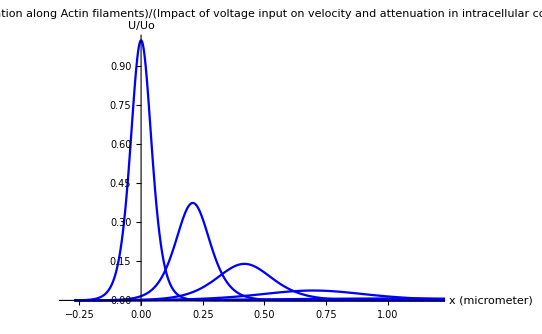

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot2=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data2=Cases[SolNormTot2,Line[{x__}]->x,∞];
```

{{-0.27,0.000318286},{-0.268476,0.000335696},{-0.266953,0.000354058},{-0.263905,0.00039385},{-0.262382,0.000415393},{-0.260858,0.000438114},{-0.257811,0.00048735},{-0.256287,0.000514006},{-0.254763,0.000542119},{-0.251716,0.000603041},{-0.250192,0.000636022},{-0.248668,0.000670806},{-0.245621,0.000746184},{-0.244097,0.000786991},{-0.242574,0.000830028},{-0.239526,0.000923289},{-0.238003,0.000973777},{-0.236479,0.00102702},{-0.233432,0.00114241},{-0.231908,0.00120487},{-0.230384,0.00127074},{-0.227337,0.00141349},{-0.225813,0.00149076},{-0.22429,0.00157225},{-0.221242,0.00174884},{-0.219719,0.00184443},{-0.218195,0.00194524},{-0.215148,0.00216366},{-0.213624,0.0022819},{-0.2121,0.00240659},{-0.209053,0.00267676},{-0.207529,0.00282299},{-0.206006,0.0029772},{-0.202958,0.00331132},{-0.201435,0.00349216},{-0.199911,0.00368286},{-0.196864,0.00409601},{-0.19534,0.00431961},{-0.193816,0.00455539},{-0.190769,0.00506617},{-0.189245,0.00534259},{-0.187722,0.00563405},{-0.184674,0.00626539},{-0.183151,0.00660703},{-0.181627,0.00696724},{-0.17858,0.00774739},{-0.177056,0.00816951},{-0.175532,0.00861452},{-0.172485,0.00957824},{-0.170833,0.0101447},{-0.169181,0.0107445},{-0.165877,0.012052},{-0.164226,0.0127638},{-0.162574,0.0135174},{-0.15927,0.0151597},{-0.157618,0.0160536},{-0.155966,0.0169997},{-0.152663,0.019061},{-0.151011,0.0201826},{-0.149359,0.0213694},{-0.146055,0.023954},{-0.144404,0.0253598},{-0.142752,0.0268469},{-0.139448,0.0300838},{-0.137796,0.0318435},{-0.136144,0.0337043},{-0.132841,0.0377519},{-0.131189,0.0399507},{-0.129537,0.0422749},{-0.126233,0.0473265},{-0.124582,0.0500685},{-0.12293,0.0529649},{-0.119626,0.0592542},{-0.117974,0.0626645},{-0.116322,0.0662641},{-0.113019,0.0740705},{-0.111367,0.0782978},{-0.109715,0.0827556},{-0.106411,0.092408},{-0.10476,0.0976263},{-0.103108,0.103123},{-0.099804,0.115},{-0.0981522,0.121408},{-0.0965003,0.128148},{-0.0931967,0.142676},{-0.0915448,0.150494},{-0.089893,0.158701},{-0.0865893,0.176338},{-0.0849375,0.185798},{-0.0832856,0.195705},{-0.079982,0.216915},{-0.0783301,0.228245},{-0.0766783,0.240076},{-0.0733746,0.265285},{-0.0667673,0.322148},{-0.0652249,0.336691},{-0.0636825,0.351718},{-0.0605978,0.383218},{-0.0544283,0.451813},{-0.0528859,0.470058},{-0.0513436,0.488706},{-0.0482588,0.527112},{-0.0420893,0.607461},{-0.040547,0.628052},{-0.0390046,0.648748},{-0.0359198,0.690233},{-0.0297504,0.771796},{-0.028208,0.791486},{-0.0266656,0.810745},{-0.0235809,0.847654},{-0.0220385,0.865145},{-0.0204961,0.881888},{-0.0174114,0.912813},{-0.015869,0.926844},{-0.0143266,0.939823},{-0.0127843,0.951683},{-0.0112419,0.962361},{-0.00969952,0.971799},{-0.00815715,0.979943},{-0.00661477,0.98675},{-0.0050724,0.99218},{-0.00353003,0.996203},{-0.00198766,0.998794},{-0.000445286,0.999939},{0.00109709,0.999632},{0.00263946,0.997875},{0.00418183,0.994676},{0.0057242,0.990056},{0.00726657,0.98404},{0.00880895,0.976662},{0.0103513,0.967965},{0.0118937,0.957997},{0.0134361,0.946812},{0.0149784,0.934471},{0.0165208,0.921039},{0.0196055,0.891183},{0.0211479,0.874909},{0.0226903,0.85784},{0.025775,0.821638},{0.0319445,0.743194},{0.0334566,0.723178},{0.0349688,0.70299},{0.037993,0.662353},{0.0440415,0.58163},{0.0455536,0.561854},{0.0470657,0.542324},{0.0500899,0.504144},{0.0561384,0.432079},{0.0576505,0.415081},{0.0591626,0.398521},{0.0621869,0.366752},{0.063699,0.351555},{0.0652111,0.336823},{0.0682353,0.308755},{0.0697474,0.295417},{0.0712596,0.282538},{0.0742838,0.258139},{0.0803323,0.214575},{0.0818444,0.204725},{0.0833565,0.19527},{0.0863807,0.177508},{0.0878928,0.169179},{0.089405,0.161202},{0.0924292,0.146261},{0.0939413,0.139275},{0.0954534,0.132597},{0.0984777,0.12012},{0.0999898,0.1143},{0.101502,0.108744},{0.104526,0.0983857},{0.106038,0.093563},{0.10755,0.0889651},{0.110575,0.0804064},{0.112087,0.0764279},{0.113599,0.0726385},{0.116623,0.0655943},{0.118135,0.062324},{0.119647,0.0592115},{0.122672,0.0534321},{0.124184,0.0507518},{0.125696,0.0482024},{0.12872,0.0434729},{0.13036,0.0411005},{0.132001,0.038855},{0.135281,0.0347188},{0.136921,0.032816},{0.138562,0.0310159},{0.141842,0.0277022},{0.143483,0.0261787},{0.145123,0.024738},{0.148403,0.0220874},{0.150044,0.0208694},{0.151684,0.0197179},{0.154964,0.0176004},{0.156605,0.0166277},{0.158245,0.0157084},{0.161526,0.0140184},{0.163166,0.0132423},{0.164806,0.012509},{0.168087,0.0111612},{0.169727,0.0105425},{0.171367,0.00995793},{0.174648,0.00888379},{0.176288,0.00839079},{0.177928,0.00792505},{0.181209,0.0070694},{0.182849,0.00667676},{0.18449,0.00630585},{0.18777,0.00562453},{0.18941,0.00531192},{0.191051,0.00501664},{0.194331,0.0044743},{0.195971,0.00422548},{0.197612,0.00399048},{0.200892,0.00355888},{0.202533,0.00336088},{0.204173,0.00317388},{0.207453,0.00283048},{0.209094,0.00267295},{0.210734,0.00252418},{0.214015,0.00225099},{0.215655,0.00212568},{0.217295,0.00200734},{0.220576,0.00179004},{0.222216,0.00169037},{0.223856,0.00159624},{0.227137,0.00142341},{0.228777,0.00134414},{0.230417,0.00126928},{0.233698,0.00113183},{0.235229,0.00107289},{0.23676,0.00101701},{0.239821,0.000913829},{0.241352,0.000866232},{0.242883,0.000821113},{0.245944,0.000737801},{0.247475,0.000699369},{0.249006,0.000662939},{0.252068,0.00059567},{0.253599,0.00056464},{0.255129,0.000535226},{0.258191,0.000480913},{0.259722,0.000455859},{0.261253,0.000432111},{0.264314,0.00038826},{0.265845,0.000368032},{0.267376,0.000348858},{0.270437,0.000313455},{0.271968,0.000297124},{0.273499,0.000281643},{0.276561,0.00025306},{0.278092,0.000239875},{0.279622,0.000227377},{0.282684,0.000204301},{0.284215,0.000193656},{0.285746,0.000183566},{0.288807,0.000164936},{0.290338,0.000156342},{0.291869,0.000148196},{0.294931,0.000133155},{0.296461,0.000126217},{0.297992,0.00011964},{0.301054,0.000107498},{0.302585,0.000101896},{0.304115,0.000096587},{0.307177,0.0000867838},{0.308708,0.0000822619},{0.310239,0.0000779756},{0.3133,0.0000700613},{0.314831,0.0000664107},{0.316362,0.0000629503},{0.319424,0.000056561},{0.320954,0.0000536138},{0.322485,0.0000508202},{0.325547,0.000045662},{0.327078,0.0000432827},{0.328608,0.0000410274},{0.33167,0.0000368632},{0.333329,0.0000347862},{0.334988,0.0000328262},{0.338306,0.0000292312},{0.339965,0.0000275842},{0.341624,0.00002603},{0.344942,0.0000231794},{0.346601,0.0000218733},{0.34826,0.0000206409},{0.351578,0.0000183804},{0.353237,0.0000173448},{0.354896,0.0000163675},{0.358214,0.000014575},{0.359873,0.0000137538},{0.361532,0.0000129788},{0.36485,0.0000115574},{0.366509,0.0000109062},{0.368168,0.0000102917},{0.371486,9.16463×10^-6},{0.373145,8.64825×10^-6},{0.374804,8.16097×10^-6},{0.378122,7.26722×10^-6},{0.37978,6.85775×10^-6},{0.381439,6.47135×10^-6},{0.384757,5.76264×10^-6},{0.386416,5.43794×10^-6},{0.388075,5.13154×10^-6},{0.391393,4.56956×10^-6},{0.393052,4.31209×10^-6},{0.394711,4.06912×10^-6},{0.398029,3.62349×10^-6},{0.399688,3.41932×10^-6},{0.401347,3.22666×10^-6},{0.404665,2.87329×10^-6},{0.406324,2.7114×10^-6},{0.407983,2.55862×10^-6},{0.411301,2.27841×10^-6},{0.41296,2.15004×10^-6},{0.414619,2.02889×10^-6},{0.417937,1.8067×10^-6},{0.419596,1.7049×10^-6},{0.421255,1.60884×10^-6},{0.424573,1.43264×10^-6},{0.426232,1.35192×10^-6},{0.427891,1.27575×10^-6},{0.431209,1.13603×10^-6},{0.432868,1.07202×10^-6},{0.434527,1.01162×10^-6},{0.437845,9.00832×10^-7},{0.439473,8.50974×10^-7},{0.441102,8.03875×10^-7},{0.44436,7.17354×10^-7},{0.445988,6.77651×10^-7},{0.447617,6.40146×10^-7},{0.450875,5.71247×10^-7},{0.452503,5.3963×10^-7},{0.454132,5.09764×10^-7},{0.457389,4.54898×10^-7},{0.459018,4.29721×10^-7},{0.460647,4.05937×10^-7},{0.463904,3.62246×10^-7},{0.465533,3.42197×10^-7},{0.467162,3.23258×10^-7},{0.470419,2.88466×10^-7},{0.472048,2.725×10^-7},{0.473677,2.57418×10^-7},{0.476934,2.29712×10^-7},{0.478563,2.16998×10^-7},{0.480192,2.04988×10^-7},{0.483449,1.82925×10^-7},{0.485078,1.72801×10^-7},{0.486706,1.63237×10^-7},{0.489964,1.45668×10^-7},{0.491593,1.37606×10^-7},{0.493221,1.2999×10^-7},{0.496479,1.15999×10^-7},{0.498108,1.09579×10^-7},{0.499736,1.03514×10^-7},{0.502994,9.23728×10^-8},{0.504622,8.72603×10^-8},{0.506251,8.24307×10^-8},{0.509509,7.35587×10^-8},{0.511137,6.94875×10^-8},{0.512766,6.56416×10^-8},{0.516023,5.85766×10^-8},{0.517652,5.53346×10^-8},{0.519281,5.2272×10^-8},{0.522538,4.6646×10^-8},{0.524167,4.40643×10^-8},{0.525796,4.16255×10^-8},{0.529053,3.71453×10^-8},{0.530682,3.50895×10^-8},{0.532311,3.31474×10^-8},{0.535568,2.95797×10^-8},{0.537197,2.79426×10^-8},{0.538826,2.63961×10^-8},{0.542083,2.35551×10^-8},{0.543602,2.23367×10^-8},{0.545122,2.11813×10^-8},{0.54816,1.90468×10^-8},{0.549679,1.80616×10^-8},{0.551199,1.71274×10^-8},{0.554237,1.54014×10^-8},{0.555756,1.46047×10^-8},{0.557276,1.38493×10^-8},{0.560314,1.24537×10^-8},{0.561833,1.18095×10^-8},{0.563353,1.11987×10^-8},{0.566391,1.00701×10^-8},{0.56791,9.54925×10^-9},{0.56943,9.05532×10^-9},{0.572468,8.14278×10^-9},{0.573987,7.72159×10^-9},{0.575507,7.3222×10^-9},{0.578545,6.58431×10^-9},{0.580065,6.24374×10^-9},{0.581584,5.92078×10^-9},{0.584622,5.32412×10^-9},{0.586142,5.04873×10^-9},{0.587661,4.78759×10^-9},{0.590699,4.30512×10^-9},{0.592219,4.08244×10^-9},{0.593738,3.87128×10^-9},{0.596776,3.48115×10^-9},{0.598296,3.30109×10^-9},{0.599815,3.13034×10^-9},{0.602853,2.81489×10^-9},{0.604373,2.66929×10^-9},{0.605892,2.53122×10^-9},{0.60893,2.27614×10^-9},{0.61045,2.1584×10^-9},{0.611969,2.04676×10^-9},{0.615007,1.8405×10^-9},{0.616527,1.7453×10^-9},{0.618046,1.65503×10^-9},{0.621085,1.48824×10^-9},{0.622604,1.41126×10^-9},{0.624123,1.33827×10^-9},{0.627162,1.2034×10^-9},{0.628681,1.14116×10^-9},{0.6302,1.08213×10^-9},{0.633239,9.73081×10^-10},{0.634758,9.22748×10^-10},{0.636277,8.75019×10^-10},{0.639316,7.8684×10^-10},{0.640963,7.42806×10^-10},{0.64261,7.01235×10^-10},{0.645905,6.24944×10^-10},{0.647553,5.8997×10^-10},{0.6492,5.56953×10^-10},{0.652495,4.96359×10^-10},{0.654142,4.6858×10^-10},{0.65579,4.42357×10^-10},{0.659085,3.9423×10^-10},{0.660732,3.72168×10^-10},{0.66238,3.5134×10^-10},{0.665674,3.13115×10^-10},{0.667322,2.95592×10^-10},{0.668969,2.7905×10^-10},{0.672264,2.4869×10^-10},{0.673911,2.34773×10^-10},{0.675559,2.21634×10^-10},{0.678854,1.97521×10^-10},{0.680501,1.86467×10^-10},{0.682149,1.76032×10^-10},{0.685443,1.5688×10^-10},{0.687091,1.48101×10^-10},{0.688738,1.39812×10^-10},{0.692033,1.24601×10^-10},{0.693681,1.17628×10^-10},{0.695328,1.11045×10^-10},{0.698623,9.89639×10^-11},{0.70027,9.34255×10^-11},{0.701918,8.81971×10^-11},{0.705213,7.86016×10^-11},{0.70686,7.42027×10^-11},{0.708507,7.00501×10^-11},{0.711802,6.24289×10^-11},{0.71345,5.89352×10^-11},{0.715097,5.56369×10^-11},{0.718392,4.95839×10^-11},{0.720039,4.6809×10^-11},{0.721687,4.41893×10^-11},{0.724982,3.93817×10^-11},{0.726629,3.71778×10^-11},{0.728276,3.50972×10^-11},{0.731571,3.12787×10^-11},{0.733219,2.95283×10^-11},{0.734866,2.78757×10^-11},{0.738161,2.4843×10^-11},{0.739808,2.34527×10^-11},{0.741456,2.21402×10^-11},{0.744751,1.97314×10^-11},{0.746289,1.86986×10^-11},{0.747827,1.77198×10^-11},{0.750902,1.59133×10^-11},{0.75244,1.50803×10^-11},{0.753978,1.4291×10^-11},{0.757054,1.2834×10^-11},{0.758592,1.21622×10^-11},{0.76013,1.15256×10^-11},{0.763206,1.03506×10^-11},{0.764744,9.80878×10^-12},{0.766282,9.29535×10^-12},{0.769358,8.3477×10^-12},{0.770896,7.91074×10^-12},{0.772434,7.49666×10^-12},{0.77551,6.73238×10^-12},{0.777048,6.37998×10^-12},{0.778586,6.04602×10^-12},{0.781662,5.42964×10^-12},{0.7832,5.14543×10^-12},{0.784738,4.87609×10^-12},{0.787813,4.37898×10^-12},{0.789351,4.14976×10^-12},{0.790889,3.93255×10^-12},{0.793965,3.53163×10^-12},{0.795503,3.34677×10^-12},{0.797041,3.17158×10^-12},{0.800117,2.84824×10^-12},{0.801655,2.69915×10^-12},{0.803193,2.55787×10^-12},{0.806269,2.2971×10^-12},{0.807807,2.17686×10^-12},{0.809345,2.06291×10^-12},{0.812421,1.8526×10^-12},{0.813959,1.75563×10^-12},{0.815497,1.66373×10^-12},{0.818573,1.49411×10^-12},{0.820111,1.4159×10^-12},{0.821649,1.34179×10^-12},{0.824724,1.205×10^-12},{0.826262,1.14192×10^-12},{0.8278,1.08215×10^-12},{0.830876,9.71824×10^-13},{0.832414,9.20954×10^-13},{0.833952,8.72747×10^-13},{0.837028,7.83772×10^-13},{0.838566,7.42746×10^-13},{0.840104,7.03867×10^-13},{0.84318,6.32109×10^-13},{0.844688,5.99655×10^-13},{0.846195,5.68868×10^-13},{0.849211,5.11954×10^-13},{0.850718,4.8567×10^-13},{0.852226,4.60735×10^-13},{0.855242,4.14639×10^-13},{0.856749,3.93351×10^-13},{0.858257,3.73156×10^-13},{0.861272,3.35823×10^-13},{0.86278,3.18581×10^-13},{0.864288,3.02225×10^-13},{0.867303,2.71988×10^-13},{0.868811,2.58024×10^-13},{0.870319,2.44776×10^-13},{0.873334,2.20287×10^-13},{0.874842,2.08977×10^-13},{0.876349,1.98248×10^-13},{0.879365,1.78414×10^-13},{0.880873,1.69254×10^-13},{0.88238,1.60564×10^-13},{0.885396,1.445×10^-13},{0.886903,1.37081×10^-13},{0.888411,1.30043×10^-13},{0.891426,1.17033×10^-13},{0.892934,1.11024×10^-13},{0.894442,1.05324×10^-13},{0.897457,9.47866×10^-14},{0.898965,8.99201×10^-14},{0.900473,8.53034×10^-14},{0.903488,7.67691×10^-14},{0.904996,7.28276×10^-14},{0.906503,6.90885×10^-14},{0.909519,6.21764×10^-14},{0.911027,5.89842×10^-14},{0.912534,5.59558×10^-14},{0.91555,5.03576×10^-14},{0.917057,4.77722×10^-14},{0.918565,4.53195×10^-14},{0.92158,4.07854×10^-14},{0.923088,3.86914×10^-14},{0.924596,3.67049×10^-14},{0.927611,3.30327×10^-14},{0.929119,3.13367×10^-14},{0.930627,2.97279×10^-14},{0.933642,2.67537×10^-14},{0.93515,2.53801×10^-14},{0.936658,2.4077×10^-14},{0.939673,2.16682×10^-14},{0.941309,2.04638×10^-14},{0.942945,1.93264×10^-14},{0.946216,1.72377×10^-14},{0.947852,1.62796×10^-14},{0.949488,1.53747×10^-14},{0.95276,1.37131×10^-14},{0.954396,1.29509×10^-14},{0.956032,1.2231×10^-14},{0.959303,1.09092×10^-14},{0.960939,1.03028×10^-14},{0.962575,9.73016×10^-15},{0.965847,8.67857×10^-15},{0.967483,8.19619×10^-15},{0.969118,7.74063×10^-15},{0.97239,6.90406×10^-15},{0.974026,6.52031×10^-15},{0.975662,6.1579×10^-15},{0.978934,5.49238×10^-15},{0.98057,5.1871×10^-15},{0.982205,4.89879×10^-15},{0.985477,4.36935×10^-15},{0.988749,3.89713×10^-15},{0.992021,3.47595×10^-15},{0.995292,3.10028×10^-15},{0.998564,2.76522×10^-15},{1.00184,2.46637×10^-15},{1.00511,2.19981×10^-15},{1.00838,1.96207×10^-15},{1.01165,1.75002×10^-15},{1.01492,1.56088×10^-15},{1.01819,1.39219×10^-15},{1.02147,1.24173×10^-15},{1.02474,1.10753×10^-15},{1.02801,9.87831×10^-16},{1.03128,8.81071×10^-16},{1.03782,7.00918×10^-16},{1.04437,5.57601×10^-16},{1.04589,5.28627×10^-16},{1.04742,5.01159×10^-16},{1.05047,4.5043×10^-16},{1.05658,3.63857×10^-16},{1.05811,3.44951×10^-16},{1.05963,3.27027×10^-16},{1.06269,2.93924×10^-16},{1.06879,2.37432×10^-16},{1.07032,2.25095×10^-16},{1.07184,2.13398×10^-16},{1.0749,1.91798×10^-16},{1.081,1.54934×10^-16},{1.09321,1.01101×10^-16},{1.09474,9.58475×10^-17},{1.09627,9.08671×10^-17},{1.09932,8.16693×10^-17},{1.10542,6.59724×10^-17},{1.11764,4.30497×10^-17},{1.14206,1.8331×10^-17},{1.14371,1.73008×10^-17},{1.14537,1.63285×10^-17},{1.14868,1.45448×10^-17},{1.15529,1.15406×10^-17},{1.16853,7.26556×10^-18},{1.195,2.87973×10^-18},{1.24795,4.52395×10^-19},{1.35191,1.19467×10^-20},{1.44886,4.03031×10^-22},{1.55401,1.0207×10^-23},{1.65216,3.30234×10^-25},{1.7585,8.02073×10^-27},{1.86292,2.08451×10^-28},{1.96032,6.92078×10^-30},{2.06593,1.72495×10^-31},{2.16454,5.49236×10^-33},{2.26121,1.87128×10^-34},{2.36608,4.78618×10^-36},{2.46394,1.56387×10^-37},{2.57001,3.83603×10^-39},{2.67414,1.00684×10^-40},{2.77126,3.37599×10^-42},{2.87659,8.49789×10^-44},{2.97491,2.73264×10^-45},{3.0713,9.40269×10^-47},{3.17588,2.4288×10^-48},{3.27346,8.01478×10^-50},{3.37925,1.98546×10^-51},{3.47803,6.28339×10^-53},{3.57487,2.12776×10^-54},{3.67991,5.40907×10^-56},{3.77795,1.75664×10^-57},{3.88419,4.28266×10^-59},{3.9885,1.11723×10^-60},{4.0858,3.72333×10^-62},{4.1913,9.31516×10^-64},{4.2898,2.97722×10^-65},{4.38636,1.01819×10^-66},{4.49112,2.61408×10^-68},{4.58887,8.57369×10^-70},{4.59058,8.07758×10^-70},{4.59228,7.61017×10^-70},{4.59569,6.75493×10^-70},{4.60252,5.32198×10^-70},{4.61616,3.30353×10^-70},{4.64344,1.27289×10^-70},{4.64514,1.19923×10^-70},{4.64685,1.12984×10^-70},{4.65026,1.00286×10^-70},{4.65708,7.90123×10^-71},{4.67072,4.90456×10^-71},{4.67242,4.62076×10^-71},{4.67413,4.35338×10^-71},{4.67754,3.86414×10^-71},{4.68436,3.04443×10^-71},{4.68606,2.86826×10^-71},{4.68777,2.70229×10^-71},{4.69118,2.3986×10^-71},{4.69288,2.25981×10^-71},{4.69459,2.12904×10^-71},{4.69629,2.00585×10^-71},{4.698,1.88978×10^-71},{-0.27,0.0000523169},{-0.268476,0.0000540509},{-0.266953,0.0000558423},{-0.263905,0.0000596053},{-0.262382,0.0000615808},{-0.260858,0.0000636218},{-0.257811,0.0000679089},{-0.256287,0.0000701595},{-0.254763,0.0000724848},{-0.251716,0.0000773691},{-0.245621,0.000088147},{-0.244097,0.0000910684},{-0.242574,0.0000940866},{-0.239526,0.000100426},{-0.238003,0.000103754},{-0.236479,0.000107193},{-0.233432,0.000114416},{-0.231908,0.000118207},{-0.230384,0.000122125},{-0.227337,0.000130354},{-0.221242,0.000148511},{-0.219719,0.000153433},{-0.218195,0.000158517},{-0.215148,0.000169197},{-0.213624,0.000174804},{-0.2121,0.000180597},{-0.209053,0.000192764},{-0.207529,0.000199152},{-0.206006,0.000205751},{-0.202958,0.000219613},{-0.196864,0.000250199},{-0.19534,0.000258489},{-0.193816,0.000267054},{-0.190769,0.000285044},{-0.189245,0.000294489},{-0.187722,0.000304246},{-0.184674,0.00032474},{-0.183151,0.000335499},{-0.181627,0.000346614},{-0.17858,0.000369961},{-0.172485,0.000421476},{-0.170833,0.000436633},{-0.169181,0.000452335},{-0.165877,0.000485453},{-0.164226,0.000502909},{-0.162574,0.000520993},{-0.15927,0.000559134},{-0.157618,0.000579238},{-0.155966,0.000600064},{-0.152663,0.000643988},{-0.146055,0.000741707},{-0.144404,0.000768369},{-0.142752,0.000795988},{-0.139448,0.000854237},{-0.137796,0.000884939},{-0.136144,0.000916743},{-0.132841,0.000983817},{-0.131189,0.00101917},{-0.129537,0.00105579},{-0.126233,0.00113302},{-0.119626,0.00130482},{-0.117974,0.00135169},{-0.116322,0.00140024},{-0.113019,0.00150261},{-0.111367,0.00155657},{-0.109715,0.00161246},{-0.106411,0.00173032},{-0.10476,0.00179243},{-0.103108,0.00185677},{-0.099804,0.00199244},{-0.0931967,0.00229414},{-0.0915448,0.00237643},{-0.089893,0.00246166},{-0.0865893,0.00264137},{-0.0849375,0.00273607},{-0.0832856,0.00283415},{-0.079982,0.00304094},{-0.0783301,0.00314991},{-0.0766783,0.00326276},{-0.0733746,0.00350067},{-0.0667673,0.00402953},{-0.0652249,0.004164},{-0.0636825,0.00430294},{-0.0605978,0.00459479},{-0.0590554,0.00474801},{-0.0575131,0.0049063},{-0.0544283,0.00523878},{-0.0528859,0.00541332},{-0.0513436,0.00559363},{-0.0482588,0.00597231},{-0.0420893,0.0068076},{-0.040547,0.0070339},{-0.0390046,0.00726765},{-0.0359198,0.00775847},{-0.0343775,0.00801604},{-0.0328351,0.00828207},{-0.0297504,0.00884057},{-0.028208,0.00913362},{-0.0266656,0.00943626},{-0.0235809,0.0100715},{-0.0174114,0.0114712},{-0.015869,0.01185},{-0.0143266,0.0122411},{-0.0112419,0.0130619},{-0.00969952,0.0134922},{-0.00815715,0.0139365},{-0.0050724,0.0148686},{-0.00353003,0.0153572},{-0.00198766,0.0158616},{0.00109709,0.0169194},{0.00726657,0.0192454},{0.00880895,0.0198739},{0.0103513,0.0205224},{0.0134361,0.0218814},{0.0149784,0.0225933},{0.0165208,0.0233275},{0.0196055,0.0248658},{0.0211479,0.0256712},{0.0226903,0.0265017},{0.025775,0.0282409},{0.0319445,0.032053},{0.0334566,0.0330597},{0.0349688,0.0340964},{0.037993,0.0362632},{0.0440415,0.040993},{0.0455536,0.0422631},{0.0470657,0.0435698},{0.0500899,0.0462974},{0.0561384,0.0522339},{0.0576505,0.0538238},{0.0591626,0.055458},{0.0621869,0.0588628},{0.0682353,0.0662456},{0.0697474,0.0682164},{0.0712596,0.0702391},{0.0742838,0.074444},{0.0803323,0.0835178},{0.0818444,0.0859296},{0.0833565,0.0884006},{0.0863807,0.0935226},{0.0924292,0.104507},{0.0939413,0.107411},{0.0954534,0.110379},{0.0984777,0.116509},{0.104526,0.129551},{0.106038,0.132975},{0.10755,0.136464},{0.110575,0.143636},{0.116623,0.158742},{0.12872,0.191763},{0.13036,0.196494},{0.132001,0.201277},{0.135281,0.210983},{0.141842,0.230845},{0.154964,0.27122},{0.156605,0.276209},{0.158245,0.281162},{0.161526,0.290931},{0.168087,0.309697},{0.169727,0.31418},{0.171367,0.318564},{0.174648,0.326999},{0.176288,0.331034},{0.177928,0.334937},{0.181209,0.342312},{0.182849,0.34577},{0.18449,0.349064},{0.18613,0.352187},{0.18777,0.355133},{0.18941,0.357894},{0.191051,0.360464},{0.192691,0.362838},{0.194331,0.36501},{0.195971,0.366974},{0.197612,0.368727},{0.199252,0.370263},{0.200892,0.37158},{0.202533,0.372673},{0.204173,0.373541},{0.205813,0.374181},{0.207453,0.374592},{0.209094,0.374772},{0.210734,0.374721},{0.212374,0.37444},{0.214015,0.373928},{0.215655,0.373188},{0.217295,0.372221},{0.218935,0.371029},{0.220576,0.369616},{0.222216,0.367984},{0.223856,0.366138},{0.225497,0.364082},{0.227137,0.361821},{0.228777,0.35936},{0.230417,0.356705},{0.233698,0.350838},{0.235229,0.347857},{0.23676,0.344731},{0.239821,0.338062},{0.245944,0.323239},{0.247475,0.319262},{0.249006,0.31519},{0.252068,0.306787},{0.258191,0.289134},{0.259722,0.284582},{0.261253,0.279988},{0.264314,0.270697},{0.270437,0.25187},{0.282684,0.214403},{0.284215,0.209825},{0.285746,0.205283},{0.288807,0.19632},{0.294931,0.178955},{0.296461,0.174745},{0.297992,0.170591},{0.301054,0.162459},{0.307177,0.146935},{0.308708,0.143214},{0.310239,0.139559},{0.3133,0.132447},{0.319424,0.119026},{0.320954,0.115839},{0.322485,0.112717},{0.325547,0.106674},{0.33167,0.0953698},{0.333329,0.0924832},{0.334988,0.08967},{0.338306,0.08426},{0.344942,0.0742756},{0.346601,0.071947},{0.34826,0.0696829},{0.351578,0.0653435},{0.358214,0.0573844},{0.359873,0.0555371},{0.361532,0.0537443},{0.36485,0.0503169},{0.366509,0.0486798},{0.368168,0.0470921},{0.371486,0.04406},{0.373145,0.0426132},{0.374804,0.0412109},{0.378122,0.0385354},{0.384757,0.0336686},{0.386416,0.0325464},{0.388075,0.0314598},{0.391393,0.0293897},{0.393052,0.0284042},{0.394711,0.0274504},{0.398029,0.0256343},{0.399688,0.0247702},{0.401347,0.0239343},{0.404665,0.0223434},{0.411301,0.0194632},{0.41296,0.0188015},{0.414619,0.0181618},{0.417937,0.0169454},{0.419596,0.0163674},{0.421255,0.0158086},{0.424573,0.0147465},{0.426232,0.014242},{0.427891,0.0137545},{0.431209,0.0128279},{0.437845,0.0111551},{0.439473,0.0107785},{0.441102,0.0104144},{0.44436,0.00972229},{0.445988,0.00939345},{0.447617,0.00907558},{0.450875,0.00847139},{0.452503,0.00818438},{0.454132,0.00790699},{0.457389,0.00737982},{0.463904,0.00642766},{0.465533,0.00620931},{0.467162,0.00599831},{0.470419,0.00559742},{0.472048,0.00540706},{0.473677,0.00522313},{0.476934,0.00487371},{0.478563,0.00470781},{0.480192,0.00454752},{0.483449,0.00424303},{0.489964,0.00369356},{0.491593,0.00356764},{0.493221,0.00344599},{0.496479,0.00321494},{0.498108,0.00310526},{0.499736,0.00299931},{0.502994,0.0027981},{0.504622,0.00270259},{0.506251,0.00261034},{0.509509,0.00243513},{0.516023,0.00211911},{0.517652,0.00204672},{0.519281,0.00197679},{0.522538,0.00184401},{0.524167,0.00178099},{0.525796,0.00172012},{0.529053,0.00160454},{0.530682,0.00154969},{0.532311,0.00149671},{0.535568,0.00139611},{0.542083,0.00121471},{0.543602,0.00117591},{0.545122,0.00113835},{0.54816,0.00106678},{0.549679,0.0010327},{0.551199,0.000999708},{0.554237,0.000936847},{0.555756,0.000906912},{0.557276,0.000877933},{0.560314,0.000822721},{0.566391,0.000722484},{0.56791,0.000699392},{0.56943,0.000677038},{0.572468,0.000634449},{0.573987,0.000614169},{0.575507,0.000594537},{0.578545,0.000557133},{0.580065,0.000539323},{0.581584,0.000522082},{0.584622,0.000489234},{0.590699,0.000429604},{0.592219,0.000415868},{0.593738,0.000402571},{0.596776,0.000377239},{0.598296,0.000365176},{0.599815,0.0003535},{0.602853,0.000331254},{0.604373,0.000320661},{0.605892,0.000310407},{0.60893,0.000290872},{0.615007,0.000255411},{0.616527,0.000247243},{0.618046,0.000239336},{0.621085,0.000224272},{0.622604,0.0002171},{0.624123,0.000210156},{0.627162,0.000196929},{0.628681,0.00019063},{0.6302,0.000184533},{0.633239,0.000172918},{0.639316,0.000151834},{0.640963,0.000146575},{0.64261,0.000141499},{0.645905,0.000131866},{0.647553,0.000127299},{0.6492,0.00012289},{0.652495,0.000114524},{0.654142,0.000110557},{0.65579,0.000106728},{0.659085,0.0000994624},{0.665674,0.0000863812},{0.667322,0.0000833891},{0.668969,0.0000805006},{0.672264,0.0000750202},{0.673911,0.0000724216},{0.675559,0.000069913},{0.678854,0.0000651534},{0.680501,0.0000628965},{0.682149,0.0000607178},{0.685443,0.0000565841},{0.692033,0.0000491419},{0.693681,0.0000474396},{0.695328,0.0000457963},{0.698623,0.0000426784},{0.70027,0.0000412},{0.701918,0.0000397728},{0.705213,0.000037065},{0.70686,0.0000357811},{0.708507,0.0000345416},{0.711802,0.0000321899},{0.718392,0.000027956},{0.720039,0.0000269876},{0.721687,0.0000260527},{0.724982,0.000024279},{0.726629,0.0000234379},{0.728276,0.000022626},{0.731571,0.0000210855},{0.733219,0.0000203551},{0.734866,0.00001965},{0.738161,0.0000183121},{0.744751,0.0000159035},{0.746289,0.0000153886},{0.747827,0.0000148904},{0.750902,0.0000139417},{0.75244,0.0000134903},{0.753978,0.0000130535},{0.757054,0.0000122219},{0.758592,0.0000118262},{0.76013,0.0000114433},{0.763206,0.0000107143},{0.769358,9.39262×10^-6},{0.770896,9.08851×10^-6},{0.772434,8.79424×10^-6},{0.77551,8.23398×10^-6},{0.777048,7.96738×10^-6},{0.778586,7.70941×10^-6},{0.781662,7.21827×10^-6},{0.7832,6.98455×10^-6},{0.784738,6.75841×10^-6},{0.787813,6.32784×10^-6},{0.793965,5.54726×10^-6},{0.795503,5.36765×10^-6},{0.797041,5.19386×10^-6},{0.800117,4.86297×10^-6},{0.801655,4.70551×10^-6},{0.803193,4.55316×10^-6},{0.806269,4.26309×10^-6},{0.807807,4.12506×10^-6},{0.809345,3.99149×10^-6},{0.812421,3.7372×10^-6},{0.818573,3.27619×10^-6},{0.820111,3.17012×10^-6},{0.821649,3.06747×10^-6},{0.824724,2.87205×10^-6},{0.826262,2.77906×10^-6},{0.8278,2.68908×10^-6},{0.830876,2.51776×10^-6},{0.832414,2.43624×10^-6},{0.833952,2.35736×10^-6},{0.837028,2.20718×10^-6},{0.84318,1.93491×10^-6},{0.844688,1.87347×10^-6},{0.846195,1.81398×10^-6},{0.849211,1.70062×10^-6},{0.850718,1.64662×10^-6},{0.852226,1.59434×10^-6},{0.855242,1.4947×10^-6},{0.856749,1.44724×10^-6},{0.858257,1.40129×10^-6},{0.861272,1.31372×10^-6},{0.867303,1.15465×10^-6},{0.868811,1.11799×10^-6},{0.870319,1.08249×10^-6},{0.873334,1.01484×10^-6},{0.874842,9.82615×10^-7},{0.876349,9.51416×10^-7},{0.879365,8.91957×10^-7},{0.880873,8.63636×10^-7},{0.88238,8.36214×10^-7},{0.885396,7.83955×10^-7},{0.891426,6.89031×10^-7},{0.892934,6.67153×10^-7},{0.894442,6.4597×10^-7},{0.897457,6.056×10^-7},{0.898965,5.86371×10^-7},{0.900473,5.67753×10^-7},{0.903488,5.32271×10^-7},{0.904996,5.15371×10^-7},{0.906503,4.99007×10^-7},{0.909519,4.67822×10^-7},{0.91555,4.11176×10^-7},{0.917057,3.9812×10^-7},{0.918565,3.85479×10^-7},{0.92158,3.61389×10^-7},{0.923088,3.49914×10^-7},{0.924596,3.38804×10^-7},{0.927611,3.1763×10^-7},{0.929119,3.07545×10^-7},{0.930627,2.9778×10^-7},{0.933642,2.7917×10^-7},{0.939673,2.45367×10^-7},{0.941309,2.36926×10^-7},{0.942945,2.28775×10^-7},{0.946216,2.13304×10^-7},{0.947852,2.05966×10^-7},{0.949488,1.9888×10^-7},{0.95276,1.85431×10^-7},{0.954396,1.79051×10^-7},{0.956032,1.72891×10^-7},{0.959303,1.612×10^-7},{0.965847,1.40135×10^-7},{0.967483,1.35314×10^-7},{0.969118,1.30658×10^-7},{0.97239,1.21823×10^-7},{0.974026,1.17632×10^-7},{0.975662,1.13585×10^-7},{0.978934,1.05904×10^-7},{0.98057,1.0226×10^-7},{0.982205,9.87421×10^-8},{0.985477,9.20648×10^-8},{0.992021,8.00343×10^-8},{0.993656,7.72808×10^-8},{0.995292,7.46221×10^-8},{0.998564,6.95758×10^-8},{1.0002,6.71822×10^-8},{1.00184,6.48709×10^-8},{1.00511,6.0484×10^-8},{1.00674,5.84032×10^-8},{1.00838,5.63939×10^-8},{1.01165,5.25803×10^-8},{1.01819,4.57094×10^-8},{1.01983,4.41368×10^-8},{1.02147,4.26184×10^-8},{1.02474,3.97364×10^-8},{1.02637,3.83693×10^-8},{1.02801,3.70492×10^-8},{1.03128,3.45438×10^-8},{1.03292,3.33554×10^-8},{1.03455,3.22079×10^-8},{1.03782,3.00298×10^-8},{1.04437,2.61057×10^-8},{1.04589,2.52667×10^-8},{1.04742,2.44546×10^-8},{1.05047,2.2908×10^-8},{1.052,2.21718×10^-8},{1.05353,2.14592×10^-8},{1.05658,2.0102×10^-8},{1.05811,1.9456×10^-8},{1.05963,1.88307×10^-8},{1.06269,1.76397×10^-8},{1.06879,1.5479×10^-8},{1.07032,1.49815×10^-8},{1.07184,1.45001×10^-8},{1.0749,1.3583×10^-8},{1.07642,1.31465×10^-8},{1.07795,1.27239×10^-8},{1.081,1.19192×10^-8},{1.08253,1.15361×10^-8},{1.08405,1.11654×10^-8},{1.08711,1.04592×10^-8},{1.09321,9.17808×10^-9},{1.09474,8.88311×10^-9},{1.09627,8.59761×10^-9},{1.09932,8.05386×10^-9},{1.10085,7.79501×10^-9},{1.10237,7.54449×10^-9},{1.10542,7.06734×10^-9},{1.10695,6.8402×10^-9},{1.10848,6.62037×10^-9},{1.11153,6.20166×10^-9},{1.11764,5.44202×10^-9},{1.11916,5.26712×10^-9},{1.12069,5.09784×10^-9},{1.12374,4.77543×10^-9},{1.12527,4.62195×10^-9},{1.12679,4.4734×10^-9},{1.12985,4.19048×10^-9},{1.13137,4.05581×10^-9},{1.1329,3.92546×10^-9},{1.13595,3.67719×10^-9},{1.14206,3.22677×10^-9},{1.14371,3.11451×10^-9},{1.14537,3.00616×10^-9},{1.14868,2.80063×10^-9},{1.15033,2.70319×10^-9},{1.15199,2.60915×10^-9},{1.15529,2.43076×10^-9},{1.15695,2.3462×10^-9},{1.1586,2.26457×10^-9},{1.16191,2.10974×10^-9},{1.16853,1.83112×10^-9},{1.17019,1.76742×10^-9},{1.17184,1.70593×10^-9},{1.17515,1.58929×10^-9},{1.1768,1.534×10^-9},{1.17846,1.48064×10^-9},{1.18177,1.3794×10^-9},{1.18342,1.33142×10^-9},{1.18508,1.2851×10^-9},{1.18839,1.19723×10^-9},{1.195,1.03912×10^-9},{1.19666,1.00297×10^-9},{1.19831,9.68077×10^-10},{1.20162,9.0189×10^-10},{1.20328,8.70513×10^-10},{1.20493,8.40228×10^-10},{1.20824,7.82782×10^-10},{1.2099,7.55549×10^-10},{1.21155,7.29263×10^-10},{1.21486,6.79404×10^-10},{1.22148,5.89678×10^-10},{1.22313,5.69163×10^-10},{1.22479,5.49362×10^-10},{1.2281,5.11803×10^-10},{1.22975,4.93997×10^-10},{1.2314,4.76811×10^-10},{1.23471,4.44211×10^-10},{1.23637,4.28757×10^-10},{1.23802,4.13841×10^-10},{1.24133,3.85547×10^-10},{1.24795,3.34629×10^-10},{1.24957,3.23197×10^-10},{1.2512,3.12155×10^-10},{1.25445,2.9119×10^-10},{1.25607,2.81241×10^-10},{1.2577,2.71633×10^-10},{1.26094,2.53389×10^-10},{1.26257,2.44732×10^-10},{1.26419,2.36371×10^-10},{1.26744,2.20496×10^-10},{1.27394,1.91872×10^-10},{1.27556,1.85317×10^-10},{1.27719,1.78986×10^-10},{1.28044,1.66965×10^-10},{1.28206,1.6126×10^-10},{1.28368,1.55751×10^-10},{1.28693,1.4529×10^-10},{1.28856,1.40326×10^-10},{1.29018,1.35532×10^-10},{1.29343,1.2643×10^-10},{1.29993,1.10017×10^-10},{1.30155,1.06259×10^-10},{1.30318,1.02628×10^-10},{1.30643,9.57355×10^-11},{1.30805,9.24647×10^-11},{1.30967,8.93056×10^-11},{1.31292,8.33076×10^-11},{1.31455,8.04615×10^-11},{1.31617,7.77125×10^-11},{1.31942,7.24931×10^-11},{1.32592,6.30825×10^-11},{1.32754,6.09273×10^-11},{1.32917,5.88457×10^-11},{1.33241,5.48935×10^-11},{1.33404,5.30181×10^-11},{1.33566,5.12067×10^-11},{1.33891,4.77676×10^-11},{1.34054,4.61356×10^-11},{1.34216,4.45594×10^-11},{1.34541,4.15667×10^-11},{1.35191,3.61707×10^-11},{1.35342,3.50169×10^-11},{1.35494,3.38999×10^-11},{1.35797,3.17716×10^-11},{1.35948,3.07581×10^-11},{1.361,2.97769×10^-11},{1.36402,2.79075×10^-11},{1.36554,2.70172×10^-11},{1.36705,2.61554×10^-11},{1.37008,2.45133×10^-11},{1.37614,2.1532×10^-11},{1.37766,2.08451×10^-11},{1.37917,2.01802×10^-11},{1.3822,1.89132×10^-11},{1.38372,1.83099×10^-11},{1.38523,1.77258×10^-11},{1.38826,1.6613×10^-11},{1.38978,1.6083×10^-11},{1.39129,1.557×10^-11},{1.39432,1.45925×10^-11},{1.40038,1.28177×10^-11},{1.4019,1.24088×10^-11},{1.40341,1.2013×10^-11},{1.40644,1.12588×10^-11},{1.40796,1.08997×10^-11},{1.40947,1.0552×10^-11},{1.4125,9.8895×10^-12},{1.41401,9.57403×10^-12},{1.41553,9.26862×10^-12},{1.41856,8.68672×10^-12},{1.42462,7.63023×10^-12},{1.42613,7.38683×10^-12},{1.42765,7.15119×10^-12},{1.43068,6.70223×10^-12},{1.43219,6.48843×10^-12},{1.43371,6.28145×10^-12},{1.43674,5.88709×10^-12},{1.43825,5.6993×10^-12},{1.43977,5.51749×10^-12},{1.4428,5.1711×10^-12},{1.44886,4.54218×10^-12},{1.4505,4.38524×10^-12},{1.45214,4.23373×10^-12},{1.45543,3.94622×10^-12},{1.45707,3.80987×10^-12},{1.45871,3.67824×10^-12},{1.462,3.42845×10^-12},{1.46364,3.30999×10^-12},{1.46529,3.19563×10^-12},{1.46857,2.97862×10^-12},{1.47514,2.58781×10^-12},{1.47679,2.49839×10^-12},{1.47843,2.41207×10^-12},{1.48172,2.24827×10^-12},{1.48336,2.17059×10^-12},{1.485,2.09559×10^-12},{1.48829,1.95329×10^-12},{1.48993,1.8858×10^-12},{1.49157,1.82064×10^-12},{1.49486,1.697×10^-12},{1.50143,1.47435×10^-12},{1.50308,1.42341×10^-12},{1.50472,1.37423×10^-12},{1.508,1.2809×10^-12},{1.50965,1.23665×10^-12},{1.51129,1.19392×10^-12},{1.51458,1.11284×10^-12},{1.51622,1.07439×10^-12},{1.51786,1.03727×10^-12},{1.52115,9.6683×10^-13},{1.52772,8.39976×10^-13},{1.52936,8.10954×10^-13},{1.53101,7.82934×10^-13},{1.53429,7.29766×10^-13},{1.53594,7.04552×10^-13},{1.53758,6.80209×10^-13},{1.54086,6.34017×10^-13},{1.54251,6.12111×10^-13},{1.54415,5.90962×10^-13},{1.54744,5.5083×10^-13},{1.55401,4.78558×10^-13},{1.55554,4.63107×10^-13},{1.55708,4.48155×10^-13},{1.56014,4.19683×10^-13},{1.56168,4.06132×10^-13},{1.56321,3.9302×10^-13},{1.56628,3.68051×10^-13},{1.56781,3.56167×10^-13},{1.56934,3.44668×10^-13},{1.57241,3.22771×10^-13},{1.57855,2.83061×10^-13},{1.58008,2.73922×10^-13},{1.58161,2.65078×10^-13},{1.58468,2.48237×10^-13},{1.58621,2.40223×10^-13},{1.58775,2.32466×10^-13},{1.59081,2.17698×10^-13},{1.59235,2.10669×10^-13},{1.59388,2.03867×10^-13},{1.59695,1.90915×10^-13},{1.60308,1.67427×10^-13},{1.60462,1.62022×10^-13},{1.60615,1.56791×10^-13},{1.60922,1.46829×10^-13},{1.61075,1.42089×10^-13},{1.61228,1.37501×10^-13},{1.61535,1.28766×10^-13},{1.61688,1.24608×10^-13},{1.61842,1.20585×10^-13},{1.62148,1.12924×10^-13},{1.62762,9.90314×10^-14},{1.62915,9.58339×10^-14},{1.63069,9.27398×10^-14},{1.63375,8.68479×10^-14},{1.63529,8.40438×10^-14},{1.63682,8.13303×10^-14},{1.63989,7.61633×10^-14},{1.64142,7.37042×10^-14},{1.64295,7.13245×10^-14},{1.64602,6.67932×10^-14},{1.65216,5.85759×10^-14},{1.65382,5.65294×10^-14},{1.65548,5.45544×10^-14},{1.6588,5.0809×10^-14},{1.66046,4.90338×10^-14},{1.66213,4.73207×10^-14},{1.66545,4.40719×10^-14},{1.66711,4.25322×10^-14},{1.66877,4.10462×10^-14},{1.6721,3.82282×10^-14},{1.67874,3.31593×10^-14},{1.6804,3.20008×10^-14},{1.68207,3.08828×10^-14},{1.68539,2.87625×10^-14},{1.68705,2.77577×10^-14},{1.68871,2.67879×10^-14},{1.69204,2.49488×10^-14},{1.6937,2.40771×10^-14},{1.69536,2.32359×10^-14},{1.69868,2.16407×10^-14},{1.70533,1.87712×10^-14},{1.70699,1.81154×10^-14},{1.70865,1.74825×10^-14},{1.71198,1.62822×10^-14},{1.71364,1.57134×10^-14},{1.7153,1.51644×10^-14},{1.71862,1.41233×10^-14},{1.72029,1.36299×10^-14},{1.72195,1.31537×10^-14},{1.72527,1.22506×10^-14},{1.73192,1.06262×10^-14},{1.73524,9.8967×10^-15},{1.73856,9.21724×10^-15},{1.74189,8.58444×10^-15},{1.74521,7.99508×10^-15},{1.74853,7.44618×10^-15},{1.75186,6.93497×10^-15},{1.7585,6.01542×10^-15},{1.76177,5.6097×10^-15},{1.76503,5.23134×10^-15},{1.76829,4.8785×10^-15},{1.77156,4.54945×10^-15},{1.77482,4.2426×10^-15},{1.77808,3.95645×10^-15},{1.78461,3.44074×10^-15},{1.78787,3.20867×10^-15},{1.79113,2.99226×10^-15},{1.7944,2.79044×10^-15},{1.79766,2.60223×10^-15},{1.80419,2.26304×10^-15},{1.81071,1.96806×10^-15},{1.81724,1.71153×10^-15},{1.82376,1.48844×10^-15},{1.83029,1.29443×10^-15},{1.83681,1.12571×10^-15},{1.84334,9.78974×10^-16},{1.84987,8.51369×10^-16},{1.8515,8.22156×10^-16},{1.85313,7.93946×10^-16},{1.85639,7.40396×10^-16},{1.86292,6.43889×10^-16},{1.87509,4.96184×10^-16},{1.88727,3.82363×10^-16},{1.88879,3.70109×10^-16},{1.89031,3.58248×10^-16},{1.89336,3.35654×10^-16},{1.89945,2.94651×10^-16},{1.91162,2.2706×10^-16},{1.91314,2.19783×10^-16},{1.91467,2.12739×10^-16},{1.91771,1.99322×10^-16},{1.9238,1.74974×10^-16},{1.93597,1.34836×10^-16},{1.96032,8.00699×10^-17},{1.96197,7.72916×10^-17},{1.96362,7.46096×10^-17},{1.96693,6.95217×10^-17},{1.97353,6.03632×10^-17},{1.98673,4.55066×10^-17},{2.01313,2.58631×10^-17},{2.06593,8.35393×10^-18},{2.16454,1.01257×10^-18},{2.26121,1.27926×10^-19},{2.36608,1.35599×10^-20},{2.46394,1.6698×10^-21},{2.57001,1.7252×10^-22},{2.67414,1.85784×10^-23},{2.77126,2.32431×10^-24},{2.87659,2.43972×10^-25},{2.97491,2.9751×10^-26},{3.0713,3.78147×10^-27},{3.17588,4.03257×10^-28},{3.27346,4.99595×10^-29},{3.37925,5.19298×10^-30},{3.47803,6.2709×10^-31},{3.57487,7.89296×10^-32},{3.67991,8.33514×10^-33},{3.77795,1.02259×10^-33},{3.88419,1.05257×10^-34},{3.9885,1.12927×10^-35},{4.0858,1.40754×10^-36},{4.1913,1.47192×10^-37},{4.2898,1.78823×10^-38},{4.38636,2.26443×10^-39},{4.49112,2.40579×10^-40},{4.58887,2.96941×10^-41},{4.59058,2.86301×10^-41},{4.59228,2.76042×10^-41},{4.59569,2.56613×10^-41},{4.60252,2.21763×10^-41},{4.61616,1.65618×10^-41},{4.64344,9.23724×10^-42},{4.64514,8.90625×10^-42},{4.64685,8.58711×10^-42},{4.65026,7.98273×10^-42},{4.65708,6.89859×10^-42},{4.67072,5.15203×10^-42},{4.67242,4.96742×10^-42},{4.67413,4.78942×10^-42},{4.67754,4.45233×10^-42},{4.68436,3.84766×10^-42},{4.68606,3.70979×10^-42},{4.68777,3.57685×10^-42},{4.69118,3.32511×10^-42},{4.69288,3.20596×10^-42},{4.69459,3.09108×10^-42},{4.69629,2.98032×10^-42},{4.698,2.87352×10^-42},{-0.27,0.0000677659},{-0.268476,0.0000691321},{-0.266953,0.0000705258},{-0.263905,0.0000733981},{-0.257811,0.0000794982},{-0.256287,0.0000811009},{-0.254763,0.0000827358},{-0.251716,0.0000861052},{-0.245621,0.0000932611},{-0.244097,0.0000951411},{-0.242574,0.0000970589},{-0.239526,0.000101011},{-0.233432,0.000109406},{-0.221242,0.000128344},{-0.219719,0.000130931},{-0.218195,0.00013357},{-0.215148,0.000139008},{-0.209053,0.000150558},{-0.207529,0.000153593},{-0.206006,0.000156688},{-0.202958,0.000163067},{-0.196864,0.000176615},{-0.19534,0.000180175},{-0.193816,0.000183805},{-0.190769,0.000191288},{-0.184674,0.000207179},{-0.172485,0.000243027},{-0.170833,0.000248339},{-0.169181,0.000253768},{-0.165877,0.000264984},{-0.15927,0.000288923},{-0.157618,0.000295238},{-0.155966,0.000301691},{-0.152663,0.000315022},{-0.146055,0.000343476},{-0.144404,0.000350982},{-0.142752,0.000358651},{-0.139448,0.000374496},{-0.132841,0.000408314},{-0.119626,0.000485371},{-0.117974,0.000495972},{-0.116322,0.000506804},{-0.113019,0.000529182},{-0.106411,0.00057694},{-0.10476,0.000589537},{-0.103108,0.000602408},{-0.099804,0.000628998},{-0.0931967,0.000685742},{-0.0915448,0.000700708},{-0.089893,0.000716001},{-0.0865893,0.000747591},{-0.079982,0.000815002},{-0.0667673,0.000968544},{-0.0652249,0.000988247},{-0.0636825,0.00100835},{-0.0605978,0.00104979},{-0.0544283,0.00113781},{-0.0528859,0.00116095},{-0.0513436,0.00118455},{-0.0482588,0.00123319},{-0.0420893,0.00133653},{-0.040547,0.00136368},{-0.0390046,0.00139138},{-0.0359198,0.00144848},{-0.0297504,0.00156975},{-0.0174114,0.0018434},{-0.015869,0.00188078},{-0.0143266,0.00191891},{-0.0112419,0.0019975},{-0.0050724,0.00216438},{-0.00353003,0.00220821},{-0.00198766,0.00225293},{0.00109709,0.00234508},{0.00726657,0.00254073},{0.00880895,0.00259212},{0.0103513,0.00264454},{0.0134361,0.00275255},{0.0196055,0.00298183},{0.0319445,0.00349853},{0.0334566,0.00356764},{0.0349688,0.0036381},{0.037993,0.00378317},{0.0440415,0.00409062},{0.0455536,0.00417125},{0.0470657,0.00425345},{0.0500899,0.00442266},{0.0561384,0.00478117},{0.0576505,0.00487517},{0.0591626,0.00497098},{0.0621869,0.00516819},{0.0682353,0.0055859},{0.0803323,0.0065228},{0.0818444,0.0066502},{0.0833565,0.00678003},{0.0863807,0.00704713},{0.0924292,0.00761241},{0.0939413,0.00776047},{0.0954534,0.00791133},{0.0984777,0.00822162},{0.104526,0.00887796},{0.106038,0.0090498},{0.10755,0.00922485},{0.110575,0.0095848},{0.116623,0.0103457},{0.12872,0.0120449},{0.13036,0.0122949},{0.132001,0.0125498},{0.135281,0.0130747},{0.141842,0.0141877},{0.143483,0.0144796},{0.145123,0.0147772},{0.148403,0.0153897},{0.154964,0.0166867},{0.156605,0.0170266},{0.158245,0.0173729},{0.161526,0.0180852},{0.168087,0.0195915},{0.181209,0.0229544},{0.182849,0.0234096},{0.18449,0.023873},{0.18777,0.0248245},{0.194331,0.0268295},{0.195971,0.0273526},{0.197612,0.0278846},{0.200892,0.028976},{0.207453,0.0312703},{0.209094,0.0318677},{0.210734,0.0324748},{0.214015,0.0337185},{0.220576,0.0363262},{0.233698,0.0420384},{0.235229,0.0427489},{0.23676,0.0434688},{0.239821,0.0449367},{0.245944,0.0479854},{0.258191,0.0545332},{0.282684,0.0693367},{0.284215,0.0703301},{0.285746,0.0713305},{0.288807,0.0733516},{0.294931,0.0774686},{0.307177,0.0859416},{0.33167,0.103217},{0.333329,0.10437},{0.334988,0.105518},{0.338306,0.107793},{0.344942,0.112246},{0.346601,0.113334},{0.34826,0.114411},{0.351578,0.11653},{0.358214,0.120598},{0.359873,0.121577},{0.361532,0.122537},{0.36485,0.124405},{0.371486,0.127903},{0.373145,0.128724},{0.374804,0.129522},{0.378122,0.131048},{0.384757,0.133798},{0.386416,0.134419},{0.388075,0.135012},{0.391393,0.136114},{0.393052,0.136621},{0.394711,0.137099},{0.398029,0.137965},{0.399688,0.138351},{0.401347,0.138706},{0.403006,0.13903},{0.404665,0.139322},{0.406324,0.139582},{0.407983,0.13981},{0.409642,0.140005},{0.411301,0.140167},{0.41296,0.140296},{0.414619,0.140393},{0.416278,0.140456},{0.417937,0.140486},{0.419596,0.140483},{0.421255,0.140447},{0.422914,0.140377},{0.424573,0.140275},{0.426232,0.14014},{0.427891,0.139971},{0.42955,0.13977},{0.431209,0.139537},{0.432868,0.139271},{0.434527,0.138973},{0.436186,0.138643},{0.437845,0.138282},{0.439473,0.137897},{0.441102,0.137483},{0.44436,0.136566},{0.445988,0.136065},{0.447617,0.135536},{0.450875,0.134395},{0.452503,0.133785},{0.454132,0.133148},{0.457389,0.131799},{0.463904,0.128811},{0.465533,0.128008},{0.467162,0.127183},{0.470419,0.125472},{0.476934,0.121822},{0.489964,0.113766},{0.491593,0.112702},{0.493221,0.111627},{0.496479,0.109449},{0.502994,0.104997},{0.516023,0.0958542},{0.542083,0.0776141},{0.543602,0.0765831},{0.545122,0.0755577},{0.54816,0.0735245},{0.554237,0.069535},{0.566391,0.0619069},{0.56791,0.0609894},{0.56943,0.0600803},{0.572468,0.0582878},{0.578545,0.0548082},{0.590699,0.0482839},{0.592219,0.0475099},{0.593738,0.0467451},{0.596776,0.0452434},{0.602853,0.0423511},{0.615007,0.0370053},{0.616527,0.0363775},{0.618046,0.0357585},{0.621085,0.0345467},{0.627162,0.0322264},{0.639316,0.027983},{0.640963,0.027447},{0.64261,0.02692},{0.645905,0.0258928},{0.652495,0.0239423},{0.654142,0.0234757},{0.65579,0.0230173},{0.659085,0.0221247},{0.665674,0.0204331},{0.667322,0.020029},{0.668969,0.0196323},{0.672264,0.0188605},{0.678854,0.0174003},{0.692033,0.0147903},{0.693681,0.0144912},{0.695328,0.0141978},{0.698623,0.0136277},{0.705213,0.012552},{0.70686,0.012296},{0.708507,0.0120449},{0.711802,0.0115574},{0.718392,0.0106383},{0.720039,0.0104197},{0.721687,0.0102054},{0.724982,0.00978949},{0.731571,0.00900609},{0.744751,0.00761703},{0.746289,0.00746916},{0.747827,0.00732409},{0.750902,0.00704212},{0.757054,0.00650954},{0.758592,0.00638266},{0.76013,0.00625819},{0.763206,0.00601633},{0.769358,0.00555972},{0.770896,0.00545098},{0.772434,0.00534432},{0.77551,0.0051371},{0.781662,0.00474604},{0.793965,0.00404967},{0.795503,0.00397003},{0.797041,0.00389193},{0.800117,0.00374025},{0.806269,0.00345417},{0.807807,0.0033861},{0.809345,0.00331935},{0.812421,0.00318972},{0.818573,0.0029453},{0.820111,0.00288715},{0.821649,0.00283014},{0.824724,0.00271943},{0.830876,0.00251071},{0.84318,0.00213975},{0.844688,0.00209821},{0.846195,0.00205747},{0.849211,0.00197832},{0.855242,0.00182899},{0.856749,0.00179344},{0.858257,0.00175858},{0.861272,0.00169086},{0.867303,0.00156311},{0.868811,0.0015327},{0.870319,0.00150288},{0.873334,0.00144496},{0.879365,0.00133569},{0.891426,0.00114123},{0.892934,0.00111899},{0.894442,0.00109719},{0.897457,0.00105484},{0.903488,0.000974973},{0.904996,0.000955966},{0.906503,0.000937329},{0.909519,0.000901133},{0.91555,0.000832868},{0.917057,0.000816624},{0.918565,0.000800695},{0.92158,0.000769761},{0.927611,0.000711423},{0.939673,0.000607647},{0.941309,0.000594788},{0.942945,0.000582201},{0.946216,0.000557818},{0.95276,0.000512068},{0.954396,0.000501228},{0.956032,0.000490618},{0.959303,0.000470064},{0.965847,0.0004315},{0.967483,0.000422363},{0.969118,0.00041342},{0.97239,0.000396096},{0.978934,0.000363592},{0.992021,0.00030636},{0.993656,0.00029987},{0.995292,0.000293517},{0.998564,0.000281212},{1.00511,0.000258128},{1.00674,0.000252658},{1.00838,0.000247305},{1.01165,0.000236936},{1.01819,0.000217483},{1.01983,0.000212875},{1.02147,0.000208364},{1.02474,0.000199626},{1.03128,0.000183234},{1.04437,0.000154376},{1.04589,0.000151321},{1.04742,0.000148326},{1.05047,0.000142513},{1.05658,0.000131561},{1.05811,0.000128957},{1.05963,0.000126404},{1.06269,0.00012145},{1.06879,0.000112116},{1.07032,0.000109897},{1.07184,0.000107722},{1.0749,0.000103499},{1.081,0.0000955444},{1.09321,0.0000814214},{1.09474,0.0000798096},{1.09627,0.0000782297},{1.09932,0.000075163},{1.10542,0.0000693855},{1.10695,0.0000680119},{1.10848,0.0000666655},{1.11153,0.000064052},{1.11764,0.0000591284},{1.11916,0.0000579578},{1.12069,0.0000568104},{1.12374,0.0000545832},{1.12985,0.0000503873},{1.14206,0.0000429383},{1.14371,0.0000420175},{1.14537,0.0000411166},{1.14868,0.0000393721},{1.15529,0.0000361021},{1.15695,0.0000353279},{1.1586,0.0000345704},{1.16191,0.0000331036},{1.16853,0.0000303542},{1.17019,0.0000297032},{1.17184,0.0000290663},{1.17515,0.000027833},{1.18177,0.0000255213},{1.195,0.0000214578},{1.19666,0.0000209977},{1.19831,0.0000205474},{1.20162,0.0000196756},{1.20824,0.0000180413},{1.2099,0.0000176544},{1.21155,0.0000172758},{1.21486,0.0000165428},{1.22148,0.0000151687},{1.22313,0.0000148434},{1.22479,0.0000145251},{1.2281,0.0000139088},{1.23471,0.0000127535},{1.24795,0.0000107229},{1.24957,0.0000104971},{1.2512,0.000010276},{1.25445,9.8478×10^-6},{1.26094,9.04415×10^-6},{1.26257,8.8537×10^-6},{1.26419,8.66726×10^-6},{1.26744,8.30608×10^-6},{1.27394,7.62824×10^-6},{1.27556,7.4676×10^-6},{1.27719,7.31035×10^-6},{1.28044,7.00571×10^-6},{1.28693,6.43399×10^-6},{1.29993,5.42671×10^-6},{1.30155,5.31243×10^-6},{1.30318,5.20056×10^-6},{1.30643,4.98384×10^-6},{1.31292,4.57712×10^-6},{1.31455,4.48073×10^-6},{1.31617,4.38638×10^-6},{1.31942,4.20358×10^-6},{1.32592,3.86054×10^-6},{1.32754,3.77924×10^-6},{1.32917,3.69966×10^-6},{1.33241,3.54548×10^-6},{1.33891,3.25614×10^-6},{1.35191,2.74636×10^-6},{1.35342,2.69239×10^-6},{1.35494,2.63948×10^-6},{1.35797,2.53675×10^-6},{1.36402,2.34313×10^-6},{1.36554,2.29708×10^-6},{1.36705,2.25193×10^-6},{1.37008,2.16429×10^-6},{1.37614,1.9991×10^-6},{1.37766,1.95981×10^-6},{1.37917,1.92129×10^-6},{1.3822,1.84652×10^-6},{1.38826,1.70558×10^-6},{1.40038,1.45516×10^-6},{1.4019,1.42656×10^-6},{1.40341,1.39852×10^-6},{1.40644,1.34409×10^-6},{1.4125,1.24151×10^-6},{1.41401,1.21711×10^-6},{1.41553,1.19319×10^-6},{1.41856,1.14675×10^-6},{1.42462,1.05922×10^-6},{1.42613,1.0384×10^-6},{1.42765,1.018×10^-6},{1.43068,9.78376×10^-7},{1.43674,9.03701×10^-7},{1.44886,7.71014×10^-7},{1.4505,7.54593×10^-7},{1.45214,7.38522×10^-7},{1.45543,7.07398×10^-7},{1.462,6.49031×10^-7},{1.46364,6.35208×10^-7},{1.46529,6.2168×10^-7},{1.46857,5.9548×10^-7},{1.47514,5.46348×10^-7},{1.47679,5.34711×10^-7},{1.47843,5.23323×10^-7},{1.48172,5.01269×10^-7},{1.48829,4.59909×10^-7},{1.50143,3.87147×10^-7},{1.50308,3.78901×10^-7},{1.50472,3.70831×10^-7},{1.508,3.55203×10^-7},{1.51458,3.25896×10^-7},{1.51622,3.18955×10^-7},{1.51786,3.12162×10^-7},{1.52115,2.99006×10^-7},{1.52772,2.74335×10^-7},{1.52936,2.68493×10^-7},{1.53101,2.62774×10^-7},{1.53429,2.517×10^-7},{1.54086,2.30933×10^-7},{1.55401,1.94396×10^-7},{1.55554,1.90529×10^-7},{1.55708,1.86739×10^-7},{1.56014,1.79383×10^-7},{1.56628,1.65529×10^-7},{1.56781,1.62236×10^-7},{1.56934,1.59009×10^-7},{1.57241,1.52745×10^-7},{1.57855,1.40949×10^-7},{1.58008,1.38145×10^-7},{1.58161,1.35397×10^-7},{1.58468,1.30063×10^-7},{1.59081,1.20018×10^-7},{1.60308,1.02196×10^-7},{1.60462,1.00163×10^-7},{1.60615,9.81705×10^-8},{1.60922,9.43034×10^-8},{1.61535,8.70203×10^-8},{1.61688,8.52892×10^-8},{1.61842,8.35925×10^-8},{1.62148,8.02997×10^-8},{1.62762,7.40981×10^-8},{1.62915,7.2624×10^-8},{1.63069,7.11793×10^-8},{1.63375,6.83755×10^-8},{1.63989,6.30948×10^-8},{1.65216,5.37254×10^-8},{1.65382,5.25683×10^-8},{1.65548,5.14361×10^-8},{1.6588,4.92443×10^-8},{1.66545,4.51369×10^-8},{1.66711,4.41648×10^-8},{1.66877,4.32135×10^-8},{1.6721,4.13721×10^-8},{1.67874,3.79213×10^-8},{1.6804,3.71046×10^-8},{1.68207,3.63054×10^-8},{1.68539,3.47584×10^-8},{1.69204,3.18593×10^-8},{1.70533,2.67663×10^-8},{1.70699,2.61898×10^-8},{1.70865,2.56257×10^-8},{1.71198,2.45337×10^-8},{1.71862,2.24874×10^-8},{1.72029,2.20031×10^-8},{1.72195,2.15292×10^-8},{1.72527,2.06118×10^-8},{1.73192,1.88926×10^-8},{1.73358,1.84857×10^-8},{1.73524,1.80875×10^-8},{1.73856,1.73168×10^-8},{1.74521,1.58724×10^-8},{1.7585,1.33351×10^-8},{1.76014,1.3053×10^-8},{1.76177,1.2777×10^-8},{1.76503,1.22422×10^-8},{1.77156,1.12389×10^-8},{1.77319,1.10012×10^-8},{1.77482,1.07685×10^-8},{1.77808,1.03178×10^-8},{1.78461,9.47226×10^-9},{1.78624,9.27192×10^-9},{1.78787,9.07582×10^-9},{1.79113,8.69597×10^-9},{1.79766,7.98331×10^-9},{1.81071,6.7284×10^-9},{1.81234,6.5861×10^-9},{1.81397,6.4468×10^-9},{1.81724,6.17699×10^-9},{1.82376,5.67076×10^-9},{1.82539,5.55082×10^-9},{1.82703,5.43342×10^-9},{1.83029,5.20602×10^-9},{1.83681,4.77937×10^-9},{1.83845,4.67828×10^-9},{1.84008,4.57934×10^-9},{1.84334,4.38768×10^-9},{1.84987,4.0281×10^-9},{1.86292,3.39492×10^-9},{1.86444,3.32788×10^-9},{1.86596,3.26217×10^-9},{1.86901,3.13462×10^-9},{1.87509,2.89429×10^-9},{1.87662,2.83714×10^-9},{1.87814,2.78112×10^-9},{1.88118,2.67238×10^-9},{1.88727,2.46748×10^-9},{1.88879,2.41876×10^-9},{1.89031,2.371×10^-9},{1.89336,2.2783×10^-9},{1.89945,2.10362×10^-9},{1.91162,1.79341×10^-9},{1.91314,1.758×10^-9},{1.91467,1.72329×10^-9},{1.91771,1.6559×10^-9},{1.9238,1.52894×10^-9},{1.92532,1.49875×10^-9},{1.92684,1.46916×10^-9},{1.92988,1.41172×10^-9},{1.93597,1.30348×10^-9},{1.93749,1.27774×10^-9},{1.93902,1.25251×10^-9},{1.94206,1.20354×10^-9},{1.94815,1.11126×10^-9},{1.96032,9.47391×10^-10},{1.96197,9.27126×10^-10},{1.96362,9.07295×10^-10},{1.96693,8.68897×10^-10},{1.97353,7.96906×10^-10},{1.97518,7.7986×10^-10},{1.97683,7.63179×10^-10},{1.98013,7.3088×10^-10},{1.98673,6.70325×10^-10},{1.98838,6.55986×10^-10},{1.99003,6.41955×10^-10},{1.99333,6.14786×10^-10},{1.99993,5.63849×10^-10},{2.01313,4.74287×10^-10},{2.01478,4.64142×10^-10},{2.01643,4.54214×10^-10},{2.01973,4.34991×10^-10},{2.02633,3.98951×10^-10},{2.02798,3.90417×10^-10},{2.02963,3.82066×10^-10},{2.03293,3.65896×10^-10},{2.03953,3.35581×10^-10},{2.04118,3.28403×10^-10},{2.04283,3.21378×10^-10},{2.04613,3.07777×10^-10},{2.05273,2.82277×10^-10},{2.06593,2.3744×10^-10},{2.06747,2.32694×10^-10},{2.06902,2.28044×10^-10},{2.0721,2.1902×10^-10},{2.07826,2.02029×10^-10},{2.0798,1.97992×10^-10},{2.08134,1.94035×10^-10},{2.08442,1.86357×10^-10},{2.09059,1.719×10^-10},{2.09213,1.68464×10^-10},{2.09367,1.65098×10^-10},{2.09675,1.58565×10^-10},{2.10291,1.46264×10^-10},{2.11524,1.24451×10^-10},{2.11678,1.21964×10^-10},{2.11832,1.19526×10^-10},{2.1214,1.14797×10^-10},{2.12756,1.05891×10^-10},{2.1291,1.03775×10^-10},{2.13064,1.01701×10^-10},{2.13372,9.76765×10^-11},{2.13989,9.00991×10^-11},{2.14143,8.82985×10^-11},{2.14297,8.65338×10^-11},{2.14605,8.31096×10^-11},{2.15221,7.66623×10^-11},{2.16454,6.52294×10^-11},{2.16605,6.39511×10^-11},{2.16756,6.26979×10^-11},{2.17058,6.02646×10^-11},{2.17662,5.56778×10^-11},{2.17813,5.45867×10^-11},{2.17964,5.3517×10^-11},{2.18266,5.144×10^-11},{2.18871,4.75248×10^-11},{2.19022,4.65935×10^-11},{2.19173,4.56804×10^-11},{2.19475,4.39076×10^-11},{2.20079,4.05657×10^-11},{2.21287,3.46256×10^-11},{2.21438,3.39471×10^-11},{2.21589,3.32818×10^-11},{2.21891,3.19902×10^-11},{2.22496,2.95554×10^-11},{2.22647,2.89762×10^-11},{2.22798,2.84084×10^-11},{2.231,2.73058×10^-11},{2.23704,2.52275×10^-11},{2.23855,2.47332×10^-11},{2.24006,2.42485×10^-11},{2.24308,2.33074×10^-11},{2.24912,2.15334×10^-11},{2.26121,1.83803×10^-11},{2.26284,1.79899×10^-11},{2.26448,1.76077×10^-11},{2.26776,1.68676×10^-11},{2.27431,1.54795×10^-11},{2.27595,1.51507×10^-11},{2.27759,1.48288×10^-11},{2.28087,1.42056×10^-11},{2.28742,1.30365×10^-11},{2.28906,1.27596×10^-11},{2.2907,1.24885×10^-11},{2.29398,1.19636×10^-11},{2.30053,1.0979×10^-11},{2.31364,9.24631×10^-12},{2.31528,9.04991×10^-12},{2.31692,8.85767×10^-12},{2.3202,8.48537×10^-12},{2.32675,7.78704×10^-12},{2.32839,7.62164×10^-12},{2.33003,7.45974×10^-12},{2.3333,7.14619×10^-12},{2.33986,6.55808×10^-12},{2.3415,6.41878×10^-12},{2.34314,6.28243×10^-12},{2.34641,6.01837×10^-12},{2.35297,5.52307×10^-12},{2.36608,4.65141×10^-12},{2.3676,4.55914×10^-12},{2.36913,4.46871×10^-12},{2.37219,4.29317×10^-12},{2.37831,3.96253×10^-12},{2.37984,3.88392×10^-12},{2.38137,3.80688×10^-12},{2.38443,3.65735×10^-12},{2.39054,3.37567×10^-12},{2.39207,3.30871×10^-12},{2.3936,3.24307×10^-12},{2.39666,3.11568×10^-12},{2.40277,2.87572×10^-12},{2.41501,2.44982×10^-12},{2.41654,2.40122×10^-12},{2.41807,2.35359×10^-12},{2.42112,2.26114×10^-12},{2.42724,2.087×10^-12},{2.42877,2.0456×10^-12},{2.4303,2.00502×10^-12},{2.43336,1.92626×10^-12},{2.43947,1.77791×10^-12},{2.441,1.74264×10^-12},{2.44253,1.70807×10^-12},{2.44559,1.64098×10^-12},{2.45171,1.5146×10^-12},{2.46394,1.29028×10^-12},{2.4656,1.26256×10^-12},{2.46725,1.23544×10^-12},{2.47057,1.18293×10^-12},{2.4772,1.08452×10^-12},{2.47886,1.06122×10^-12},{2.48051,1.03842×10^-12},{2.48383,9.9429×10^-13},{2.49046,9.11569×10^-13},{2.49211,8.91987×10^-13},{2.49377,8.72826×10^-13},{2.49709,8.3573×10^-13},{2.50372,7.662×10^-13},{2.51697,6.44014×10^-13},{2.51863,6.3018×10^-13},{2.52029,6.16643×10^-13},{2.5236,5.90434×10^-13},{2.53023,5.41313×10^-13},{2.53189,5.29684×10^-13},{2.53355,5.18306×10^-13},{2.53686,4.96277×10^-13},{2.54349,4.54989×10^-13},{2.54515,4.45215×10^-13},{2.5468,4.35651×10^-13},{2.55012,4.17136×10^-13},{2.55675,3.82432×10^-13},{2.57001,3.21445×10^-13},{2.57163,3.14665×10^-13},{2.57326,3.08027×10^-13},{2.57651,2.9517×10^-13},{2.58302,2.71042×10^-13},{2.58465,2.65325×10^-13},{2.58628,2.59728×10^-13},{2.58953,2.48887×10^-13},{2.59604,2.28542×10^-13},{2.59767,2.23722×10^-13},{2.59929,2.19003×10^-13},{2.60255,2.09861×10^-13},{2.60906,1.92707×10^-13},{2.62207,1.6249×10^-13},{2.6237,1.59063×10^-13},{2.62533,1.55708×10^-13},{2.62858,1.49208×10^-13},{2.63509,1.37012×10^-13},{2.63672,1.34122×10^-13},{2.63834,1.31293×10^-13},{2.6416,1.25812×10^-13},{2.6481,1.15528×10^-13},{2.64973,1.13091×10^-13},{2.65136,1.10706×10^-13},{2.65461,1.06085×10^-13},{2.66112,9.74132×10^-14},{2.67414,8.21387×10^-14},{2.67565,8.05216×10^-14},{2.67717,7.89362×10^-14},{2.68021,7.58586×10^-14},{2.68628,7.00586×10^-14},{2.6878,6.86793×10^-14},{2.68931,6.73271×10^-14},{2.69235,6.47021×10^-14},{2.69842,5.97551×10^-14},{2.69994,5.85786×10^-14},{2.70145,5.74253×10^-14},{2.70449,5.51864×10^-14},{2.71056,5.09669×10^-14},{2.7227,4.34712×10^-14},{2.72422,4.26154×10^-14},{2.72573,4.17763×10^-14},{2.72877,4.01475×10^-14},{2.73484,3.70779×10^-14},{2.73636,3.63479×10^-14},{2.73788,3.56323×10^-14},{2.74091,3.4243×10^-14},{2.74698,3.16249×10^-14},{2.75002,3.03919×10^-14},{2.75305,2.92069×10^-14},{2.75912,2.69738×10^-14},{2.77126,2.30068×10^-14},{2.77455,2.20356×10^-14},{2.77784,2.11055×10^-14},{2.78443,1.93613×10^-14},{2.78772,1.8544×10^-14},{2.79101,1.77613×10^-14},{2.79759,1.62935×10^-14},{2.80089,1.56057×10^-14},{2.80418,1.4947×10^-14},{2.81076,1.37117×10^-14},{2.82393,1.15391×10^-14},{2.82722,1.1052×10^-14},{2.83051,1.05855×10^-14},{2.83709,9.7107×10^-15},{2.84038,9.3008×10^-15},{2.84367,8.9082×10^-15},{2.85026,8.17202×10^-15},{2.85355,7.82707×10^-15},{2.85684,7.49668×10^-15},{2.86342,6.87715×10^-15},{2.87659,5.78745×10^-15},{2.88273,5.33972×10^-15},{2.88888,4.92663×10^-15},{2.89502,4.54549×10^-15},{2.90117,4.19384×10^-15},{2.90731,3.86939×10^-15},{2.91346,3.57005×10^-15},{2.92575,3.03904×10^-15},{2.93189,2.80393×10^-15},{2.93804,2.58701×10^-15},{2.94418,2.38687×10^-15},{2.95033,2.20222×10^-15},{2.96262,1.87466×10^-15},{2.97491,1.59582×10^-15},{2.98696,1.36278×10^-15},{2.99901,1.16376×10^-15},{3.01105,9.93811×10^-16},{3.0231,8.48679×10^-16},{3.03515,7.24741×10^-16},{3.0472,6.18903×10^-16},{3.04871,6.0681×10^-16},{3.05021,5.94953×10^-16},{3.05322,5.71929×10^-16},{3.05925,5.28521×10^-16},{3.0713,4.51338×10^-16},{3.09744,3.20414×10^-16},{3.12359,2.27469×10^-16},{3.12522,2.2265×10^-16},{3.12686,2.17933×10^-16},{3.13013,2.08797×10^-16},{3.13666,1.91658×10^-16},{3.14974,1.61485×10^-16},{3.17588,1.14642×10^-16},{3.17741,1.12374×10^-16},{3.17893,1.10151×10^-16},{3.18198,1.05837×10^-16},{3.18808,9.77081×10^-17},{3.20028,8.32758×10^-17},{3.22467,6.04916×10^-17},{3.27346,3.1919×10^-17},{3.37925,7.9814×10^-18},{3.47803,2.18764×10^-18},{3.57487,6.15023×10^-19},{3.67991,1.55285×10^-19},{3.77795,4.2977×10^-20},{3.88419,1.06823×10^-20},{3.9885,2.72341×10^-21},{4.0858,7.61074×10^-22},{4.1913,1.91014×10^-22},{4.2898,5.25496×10^-23},{4.38636,1.48283×10^-23},{4.49112,3.75785×10^-24},{4.58887,1.04388×10^-24},{4.59058,1.02082×10^-24},{4.59228,9.98266×10^-25},{4.59569,9.54642×10^-25},{4.60252,8.7303×10^-25},{4.61616,7.3014×10^-25},{4.64344,5.10694×10^-25},{4.64514,4.9941×10^-25},{4.64685,4.88376×10^-25},{4.65026,4.67035×10^-25},{4.65708,4.27108×10^-25},{4.67072,3.57203×10^-25},{4.67242,3.49311×10^-25},{4.67413,3.41593×10^-25},{4.67754,3.26665×10^-25},{4.68436,2.98739×10^-25},{4.68606,2.92139×10^-25},{4.68777,2.85684×10^-25},{4.69118,2.732×10^-25},{4.69288,2.67164×10^-25},{4.69459,2.61261×10^-25},{4.69629,2.55489×10^-25},{4.698,2.49844×10^-25},{-0.27,0.000208508},{-0.268476,0.000210677},{-0.266953,0.000212869},{-0.263905,0.000217322},{-0.257811,0.000226507},{-0.245621,0.000246056},{-0.244097,0.000248615},{-0.242574,0.0002512},{-0.239526,0.000256452},{-0.233432,0.000267285},{-0.221242,0.000290339},{-0.219719,0.000293357},{-0.218195,0.000296406},{-0.215148,0.000302599},{-0.209053,0.000315374},{-0.196864,0.000342557},{-0.172485,0.000404115},{-0.170833,0.000408664},{-0.169181,0.000413263},{-0.165877,0.000422617},{-0.15927,0.000441961},{-0.146055,0.000483328},{-0.144404,0.000488763},{-0.142752,0.000494258},{-0.139448,0.000505433},{-0.132841,0.000528541},{-0.119626,0.000577949},{-0.117974,0.000584439},{-0.116322,0.000591001},{-0.113019,0.000604346},{-0.106411,0.000631938},{-0.0931967,0.000690923},{-0.0915448,0.000698669},{-0.089893,0.000706502},{-0.0865893,0.000722429},{-0.079982,0.000755358},{-0.0667673,0.000825736},{-0.0652249,0.000834361},{-0.0636825,0.000843076},{-0.0605978,0.000860776},{-0.0544283,0.000897286},{-0.0420893,0.000974955},{-0.040547,0.000985119},{-0.0390046,0.000995387},{-0.0359198,0.00101624},{-0.0297504,0.00105925},{-0.0174114,0.00115072},{-0.015869,0.00116269},{-0.0143266,0.00117478},{-0.0112419,0.00119933},{-0.0050724,0.00124996},{0.00726657,0.00135759},{0.0319445,0.00160084},{0.0334566,0.00161706},{0.0349688,0.00163344},{0.037993,0.00166669},{0.0440415,0.00173518},{0.0561384,0.0018805},{0.0576505,0.00189948},{0.0591626,0.00191864},{0.0621869,0.00195754},{0.0682353,0.00203764},{0.0803323,0.00220752},{0.0818444,0.00222969},{0.0833565,0.00225208},{0.0863807,0.00229752},{0.0924292,0.00239108},{0.104526,0.00258935},{0.12872,0.00303442},{0.13036,0.00306711},{0.132001,0.00310014},{0.135281,0.00316722},{0.141842,0.00330556},{0.154964,0.00359967},{0.156605,0.00363813},{0.158245,0.00367698},{0.161526,0.00375587},{0.168087,0.00391846},{0.181209,0.00426373},{0.182849,0.00430884},{0.18449,0.0043544},{0.18777,0.00444687},{0.194331,0.00463733},{0.207453,0.00504122},{0.233698,0.00594782},{0.235229,0.00600503},{0.23676,0.00606274},{0.239821,0.00617967},{0.245944,0.00641964},{0.258191,0.00692482},{0.259722,0.00699039},{0.261253,0.00705652},{0.264314,0.00719043},{0.270437,0.00746501},{0.282684,0.00804182},{0.284215,0.00811658},{0.285746,0.00819194},{0.288807,0.00834446},{0.294931,0.00865683},{0.307177,0.00931148},{0.33167,0.0107448},{0.333329,0.010848},{0.334988,0.010952},{0.338306,0.0111624},{0.344942,0.0115929},{0.358214,0.0124923},{0.384757,0.0144459},{0.386416,0.0145748},{0.388075,0.0147045},{0.391393,0.0149663},{0.398029,0.0154992},{0.411301,0.0166015},{0.437845,0.0189426},{0.439473,0.0190917},{0.441102,0.0192414},{0.44436,0.0195424},{0.450875,0.0201509},{0.463904,0.0213916},{0.489964,0.0239436},{0.491593,0.0241052},{0.493221,0.0242669},{0.496479,0.0245907},{0.502994,0.0252391},{0.516023,0.0265351},{0.542083,0.0290852},{0.543602,0.0292306},{0.545122,0.0293755},{0.54816,0.0296639},{0.554237,0.0302338},{0.566391,0.0313422},{0.56791,0.0314774},{0.56943,0.0316117},{0.572468,0.0318779},{0.578545,0.0323994},{0.590699,0.0333945},{0.592219,0.033514},{0.593738,0.0336323},{0.596776,0.0338653},{0.602853,0.0343166},{0.604373,0.0344262},{0.605892,0.0345344},{0.60893,0.0347469},{0.615007,0.0351551},{0.616527,0.0352535},{0.618046,0.0353505},{0.621085,0.0355398},{0.627162,0.0359},{0.628681,0.0359861},{0.6302,0.0360705},{0.633239,0.0362344},{0.639316,0.0365421},{0.640963,0.0366208},{0.64261,0.0366974},{0.645905,0.0368444},{0.647553,0.0369147},{0.6492,0.0369829},{0.652495,0.0371128},{0.654142,0.0371745},{0.65579,0.037234},{0.659085,0.0373464},{0.660732,0.0373992},{0.66238,0.0374498},{0.665674,0.0375442},{0.667322,0.037588},{0.668969,0.0376295},{0.670617,0.0376687},{0.672264,0.0377055},{0.673911,0.0377401},{0.675559,0.0377723},{0.677206,0.0378022},{0.678854,0.0378297},{0.680501,0.0378549},{0.682149,0.0378777},{0.683796,0.0378981},{0.685443,0.0379162},{0.687091,0.0379319},{0.688738,0.0379452},{0.690386,0.0379561},{0.692033,0.0379646},{0.693681,0.0379708},{0.695328,0.0379745},{0.696975,0.0379759},{0.698623,0.0379749},{0.70027,0.0379715},{0.701918,0.0379657},{0.703565,0.0379575},{0.705213,0.0379469},{0.70686,0.0379339},{0.708507,0.0379186},{0.710155,0.0379009},{0.711802,0.0378808},{0.71345,0.0378583},{0.715097,0.0378335},{0.716744,0.0378063},{0.718392,0.0377768},{0.720039,0.0377449},{0.721687,0.0377107},{0.724982,0.0376353},{0.726629,0.0375942},{0.728276,0.0375507},{0.731571,0.037457},{0.733219,0.0374067},{0.734866,0.0373542},{0.738161,0.0372425},{0.744751,0.0369926},{0.746289,0.0369293},{0.747827,0.0368641},{0.750902,0.0367283},{0.757054,0.0364349},{0.758592,0.0363571},{0.76013,0.0362776},{0.763206,0.0361134},{0.769358,0.0357649},{0.770896,0.0356737},{0.772434,0.0355809},{0.77551,0.0353905},{0.781662,0.0349914},{0.793965,0.0341239},{0.795503,0.0340094},{0.797041,0.0338936},{0.800117,0.0336582},{0.806269,0.0331731},{0.818573,0.03215},{0.84318,0.0299324},{0.844688,0.0297906},{0.846195,0.0296482},{0.849211,0.029362},{0.855242,0.0287837},{0.867303,0.0276084},{0.891426,0.0252163},{0.892934,0.0250661},{0.894442,0.024916},{0.897457,0.024616},{0.903488,0.0240169},{0.91555,0.0228257},{0.939673,0.0204948},{0.941309,0.0203401},{0.942945,0.0201859},{0.946216,0.019879},{0.95276,0.0192716},{0.965847,0.0180849},{0.992021,0.0158379},{0.993656,0.0157035},{0.995292,0.0155698},{0.998564,0.0153048},{1.00511,0.0147837},{1.01819,0.0137783},{1.04437,0.0119176},{1.04589,0.0118153},{1.04742,0.0117136},{1.05047,0.0115124},{1.05658,0.0111181},{1.06879,0.0103617},{1.07032,0.0102702},{1.07184,0.0101793},{1.0749,0.0099995},{1.081,0.00964773},{1.09321,0.00897502},{1.09474,0.00889377},{1.09627,0.00881315},{1.09932,0.00865378},{1.10542,0.00834239},{1.11764,0.00774845},{1.14206,0.00667062},{1.14371,0.00660267},{1.14537,0.00653533},{1.14868,0.00640251},{1.15529,0.00614412},{1.16853,0.00565544},{1.17019,0.00559691},{1.17184,0.00553894},{1.17515,0.00542463},{1.18177,0.00520248},{1.195,0.00478313},{1.19666,0.00473297},{1.19831,0.0046833},{1.20162,0.00458542},{1.20824,0.00439533},{1.22148,0.00403708},{1.24795,0.00340149},{1.24957,0.00336575},{1.2512,0.00333038},{1.25445,0.00326068},{1.26094,0.00312544},{1.27394,0.00287087},{1.27556,0.00284048},{1.27719,0.0028104},{1.28044,0.00275116},{1.28693,0.00263626},{1.29993,0.00242015},{1.30155,0.00239437},{1.30318,0.00236886},{1.30643,0.00231862},{1.31292,0.00222121},{1.32592,0.00203816},{1.35191,0.00171501},{1.35342,0.0016978},{1.35494,0.00168076},{1.35797,0.00164717},{1.36402,0.00158197},{1.37614,0.00145904},{1.37766,0.00144435},{1.37917,0.0014298},{1.3822,0.00140114},{1.38826,0.00134549},{1.40038,0.00124063},{1.4019,0.0012281},{1.40341,0.00121569},{1.40644,0.00119125},{1.4125,0.00114381},{1.42462,0.00105444},{1.44886,0.000895854},{1.4505,0.000885999},{1.45214,0.000876252},{1.45543,0.000857075},{1.462,0.000819956},{1.47514,0.000750423},{1.47679,0.000742153},{1.47843,0.000733972},{1.48172,0.000717879},{1.48829,0.000686733},{1.50143,0.000628402},{1.50308,0.000621465},{1.50472,0.000614604},{1.508,0.000601106},{1.51458,0.000574988},{1.52772,0.000526082},{1.52936,0.000520266},{1.53101,0.000514515},{1.53429,0.000503201},{1.54086,0.000481309},{1.55401,0.000440324},{1.55554,0.000435774},{1.55708,0.000431271},{1.56014,0.000422403},{1.56628,0.000405207},{1.57855,0.000372878},{1.58008,0.000369021},{1.58161,0.000365205},{1.58468,0.000357689},{1.59081,0.000343116},{1.60308,0.000315719},{1.60462,0.000312452},{1.60615,0.000309218},{1.60922,0.000302849},{1.61535,0.000290502},{1.62762,0.000267292},{1.65216,0.00022627},{1.65382,0.00022373},{1.65548,0.000221219},{1.6588,0.000216281},{1.66545,0.000206732},{1.67874,0.000188877},{1.6804,0.000186757},{1.68207,0.000184659},{1.68539,0.000180535},{1.69204,0.000172561},{1.70533,0.000157651},{1.70699,0.00015588},{1.70865,0.000154129},{1.71198,0.000150686},{1.71862,0.000144027},{1.73192,0.000131579},{1.73358,0.0001301},{1.73524,0.000128638},{1.73856,0.000125763},{1.74521,0.000120204},{1.7585,0.000109812},{1.76014,0.0001086},{1.76177,0.000107401},{1.76503,0.000105044},{1.77156,0.000100482},{1.78461,0.0000919439},{1.78624,0.0000909288},{1.78787,0.000089925},{1.79113,0.0000879505},{1.79766,0.0000841304},{1.81071,0.0000769802},{1.81234,0.0000761303},{1.81397,0.0000752897},{1.81724,0.0000736362},{1.82376,0.0000704372},{1.83681,0.0000644499},{1.83845,0.0000637381},{1.84008,0.0000630342},{1.84334,0.0000616497},{1.84987,0.000058971},{1.86292,0.0000539576},{1.86444,0.0000534015},{1.86596,0.000052851},{1.86901,0.0000517671},{1.87509,0.0000496654},{1.88727,0.0000457144},{1.88879,0.0000452431},{1.89031,0.0000447767},{1.89336,0.0000438583},{1.89945,0.0000420775},{1.91162,0.0000387298},{1.91314,0.0000383305},{1.91467,0.0000379353},{1.91771,0.0000371572},{1.9238,0.0000356483},{1.93597,0.0000328119},{1.96032,0.000027798},{1.96197,0.0000274874},{1.96362,0.0000271802},{1.96693,0.0000265761},{1.97353,0.000025408},{1.98673,0.0000232234},{1.98838,0.0000229638},{1.99003,0.0000227072},{1.99333,0.0000222025},{1.99993,0.0000212266},{2.01313,0.0000194014},{2.01478,0.0000191846},{2.01643,0.0000189702},{2.01973,0.0000185485},{2.02633,0.0000177331},{2.03953,0.0000162083},{2.04118,0.0000160271},{2.04283,0.000015848},{2.04613,0.0000154957},{2.05273,0.0000148145},{2.06593,0.0000135406},{2.06747,0.0000133992},{2.06902,0.0000132594},{2.0721,0.000012984},{2.07826,0.0000124502},{2.09059,0.0000114477},{2.09213,0.0000113282},{2.09367,0.0000112099},{2.09675,0.0000109771},{2.10291,0.0000105258},{2.11524,9.67821×10^-6},{2.11678,9.57717×10^-6},{2.11832,9.47719×10^-6},{2.1214,9.28034×10^-6},{2.12756,8.89883×10^-6},{2.13989,8.18222×10^-6},{2.16454,6.91745×10^-6},{2.16605,6.84664×10^-6},{2.16756,6.77656×10^-6},{2.17058,6.63854×10^-6},{2.17662,6.37087×10^-6},{2.18871,5.86748×10^-6},{2.19022,5.80742×10^-6},{2.19173,5.74797×10^-6},{2.19475,5.6309×10^-6},{2.20079,5.40386×10^-6},{2.21287,4.97687×10^-6},{2.21438,4.92593×10^-6},{2.21589,4.8755×10^-6},{2.21891,4.7762×10^-6},{2.22496,4.58362×10^-6},{2.23704,4.22144×10^-6},{2.26121,3.58067×10^-6},{2.26284,3.54092×10^-6},{2.26448,3.50161×10^-6},{2.26776,3.42431×10^-6},{2.27431,3.27478×10^-6},{2.28742,2.99502×10^-6},{2.28906,2.96178×10^-6},{2.2907,2.9289×10^-6},{2.29398,2.86424×10^-6},{2.30053,2.73916×10^-6},{2.31364,2.50516×10^-6},{2.31528,2.47735×10^-6},{2.31692,2.44985×10^-6},{2.3202,2.39577×10^-6},{2.32675,2.29115×10^-6},{2.33986,2.09542×10^-6},{2.3415,2.07216×10^-6},{2.34314,2.04916×10^-6},{2.34641,2.00392×10^-6},{2.35297,1.91641×10^-6},{2.36608,1.75269×10^-6},{2.3676,1.73453×10^-6},{2.36913,1.71655×10^-6},{2.37219,1.68116×10^-6},{2.37831,1.61255×10^-6},{2.39054,1.48362×10^-6},{2.39207,1.46824×10^-6},{2.3936,1.45303×10^-6},{2.39666,1.42307×10^-6},{2.40277,1.36499×10^-6},{2.41501,1.25585×10^-6},{2.41654,1.24283×10^-6},{2.41807,1.22996×10^-6},{2.42112,1.2046×10^-6},{2.42724,1.15543×10^-6},{2.43947,1.06305×10^-6},{2.46394,8.99847×10^-7},{2.4656,8.89745×10^-7},{2.46725,8.79756×10^-7},{2.47057,8.60113×10^-7},{2.4772,8.22134×10^-7},{2.49046,7.51133×10^-7},{2.49211,7.42701×10^-7},{2.49377,7.34363×10^-7},{2.49709,7.17966×10^-7},{2.50372,6.86264×10^-7},{2.51697,6.26997×10^-7},{2.51863,6.19958×10^-7},{2.52029,6.12998×10^-7},{2.5236,5.99311×10^-7},{2.53023,5.72848×10^-7},{2.54349,5.23376×10^-7},{2.54515,5.175×10^-7},{2.5468,5.1169×10^-7},{2.55012,5.00266×10^-7},{2.55675,4.78176×10^-7},{2.57001,4.3688×10^-7},{2.57163,4.32064×10^-7},{2.57326,4.27301×10^-7},{2.57651,4.17933×10^-7},{2.58302,3.99808×10^-7},{2.59604,3.65883×10^-7},{2.59767,3.6185×10^-7},{2.59929,3.57861×10^-7},{2.60255,3.50015×10^-7},{2.60906,3.34836×10^-7},{2.62207,3.06424×10^-7},{2.6237,3.03046×10^-7},{2.62533,2.99705×10^-7},{2.62858,2.93135×10^-7},{2.63509,2.80422×10^-7},{2.6481,2.56627×10^-7},{2.64973,2.53798×10^-7},{2.65136,2.51001×10^-7},{2.65461,2.45498×10^-7},{2.66112,2.34851×10^-7},{2.67414,2.14923×10^-7},{2.67565,2.12712×10^-7},{2.67717,2.10524×10^-7},{2.68021,2.06216×10^-7},{2.68628,1.97862×10^-7},{2.69842,1.82156×10^-7},{2.69994,1.80283×10^-7},{2.70145,1.78429×10^-7},{2.70449,1.74777×10^-7},{2.71056,1.67697×10^-7},{2.7227,1.54385×10^-7},{2.72422,1.52797×10^-7},{2.72573,1.51226×10^-7},{2.72877,1.48131×10^-7},{2.73484,1.4213×10^-7},{2.74698,1.30848×10^-7},{2.77126,1.10899×10^-7},{2.77291,1.09663×10^-7},{2.77455,1.0844×10^-7},{2.77784,1.06036×10^-7},{2.78443,1.01386×10^-7},{2.79759,9.26882×10^-8},{2.79924,9.16548×10^-8},{2.80089,9.0633×10^-8},{2.80418,8.86233×10^-8},{2.81076,8.47367×10^-8},{2.82393,7.74674×10^-8},{2.82557,7.66037×10^-8},{2.82722,7.57497×10^-8},{2.83051,7.40701×10^-8},{2.83709,7.08217×10^-8},{2.85026,6.47461×10^-8},{2.8519,6.40243×10^-8},{2.85355,6.33105×10^-8},{2.85684,6.19067×10^-8},{2.86342,5.91918×10^-8},{2.87659,5.41139×10^-8},{2.87813,5.35505×10^-8},{2.87966,5.2993×10^-8},{2.88273,5.18953×10^-8},{2.88888,4.97676×10^-8},{2.90117,4.57704×10^-8},{2.90271,4.52939×10^-8},{2.90424,4.48224×10^-8},{2.90731,4.38939×10^-8},{2.91346,4.20943×10^-8},{2.92575,3.87134×10^-8},{2.92729,3.83104×10^-8},{2.92882,3.79115×10^-8},{2.93189,3.71262×10^-8},{2.93804,3.56041×10^-8},{2.95033,3.27445×10^-8},{2.97491,2.76958×10^-8},{2.97642,2.74132×10^-8},{2.97792,2.71333×10^-8},{2.98093,2.65823×10^-8},{2.98696,2.55134×10^-8},{2.99901,2.3503×10^-8},{3.00051,2.32631×10^-8},{3.00202,2.30257×10^-8},{3.00503,2.2558×10^-8},{3.01105,2.1651×10^-8},{3.0231,1.99449×10^-8},{3.02461,1.97413×10^-8},{3.02611,1.95398×10^-8},{3.02913,1.9143×10^-8},{3.03515,1.83733×10^-8},{3.0472,1.69255×10^-8},{3.0713,1.43631×10^-8},{3.07293,1.42041×10^-8},{3.07456,1.40469×10^-8},{3.07783,1.37376×10^-8},{3.08437,1.31392×10^-8},{3.09744,1.20196×10^-8},{3.09908,1.18866×10^-8},{3.10071,1.1755×10^-8},{3.10398,1.14961×10^-8},{3.11052,1.09954×10^-8},{3.12359,1.00585×10^-8},{3.12522,9.94714×10^-9},{3.12686,9.83701×10^-9},{3.13013,9.62041×10^-9},{3.13666,9.2014×10^-9},{3.14974,8.41734×10^-9},{3.15137,8.32415×10^-9},{3.153,8.23199×10^-9},{3.15627,8.05073×10^-9},{3.16281,7.70009×10^-9},{3.17588,7.04395×10^-9},{3.17741,6.97117×10^-9},{3.17893,6.89913×10^-9},{3.18198,6.75729×10^-9},{3.18808,6.48229×10^-9},{3.20028,5.96541×10^-9},{3.2018,5.90376×10^-9},{3.20333,5.84276×10^-9},{3.20638,5.72263×10^-9},{3.21248,5.48974×10^-9},{3.22467,5.052×10^-9},{3.2262,4.9998×10^-9},{3.22772,4.94814×10^-9},{3.23077,4.8464×10^-9},{3.23687,4.64917×10^-9},{3.24907,4.27846×10^-9},{3.27346,3.62335×10^-9},{3.27512,3.58278×10^-9},{3.27677,3.54267×10^-9},{3.28008,3.46378×10^-9},{3.28669,3.31123×10^-9},{3.29991,3.02599×10^-9},{3.30156,2.99211×10^-9},{3.30322,2.9586×10^-9},{3.30652,2.89272×10^-9},{3.31313,2.76532×10^-9},{3.32636,2.52711×10^-9},{3.32801,2.49881×10^-9},{3.32966,2.47083×10^-9},{3.33297,2.41581×10^-9},{3.33958,2.30942×10^-9},{3.3528,2.11048×10^-9},{3.35446,2.08685×10^-9},{3.35611,2.06348×10^-9},{3.35941,2.01753×10^-9},{3.36603,1.92867×10^-9},{3.37925,1.76253×10^-9},{3.38079,1.7441×10^-9},{3.38234,1.72586×10^-9},{3.38542,1.68994×10^-9},{3.3916,1.62034×10^-9},{3.40394,1.48962×10^-9},{3.40549,1.47404×10^-9},{3.40703,1.45862×10^-9},{3.41012,1.42827×10^-9},{3.41629,1.36945×10^-9},{3.42864,1.25897×10^-9},{3.43018,1.2458×10^-9},{3.43172,1.23277×10^-9},{3.43481,1.20711×10^-9},{3.44099,1.1574×10^-9},{3.45333,1.06403×10^-9},{3.47803,8.99271×10^-10},{3.47954,8.90049×10^-10},{3.48105,8.80921×10^-10},{3.48408,8.62945×10^-10},{3.49013,8.28087×10^-10},{3.50224,7.62537×10^-10},{3.50375,7.54717×10^-10},{3.50526,7.46977×10^-10},{3.50829,7.31735×10^-10},{3.51434,7.02177×10^-10},{3.52645,6.46594×10^-10},{3.52796,6.39963×10^-10},{3.52947,6.334×10^-10},{3.5325,6.20475×10^-10},{3.53855,5.95411×10^-10},{3.55066,5.4828×10^-10},{3.57487,4.64914×10^-10},{3.57651,4.59745×10^-10},{3.57815,4.54633×10^-10},{3.58143,4.44579×10^-10},{3.588,4.25133×10^-10},{3.60113,3.88756×10^-10},{3.60277,3.84433×10^-10},{3.60441,3.80158×10^-10},{3.6077,3.71751×10^-10},{3.61426,3.55491×10^-10},{3.62739,3.25072×10^-10},{3.62903,3.21458×10^-10},{3.63067,3.17884×10^-10},{3.63396,3.10854×10^-10},{3.64052,2.97257×10^-10},{3.65365,2.71822×10^-10},{3.65529,2.68799×10^-10},{3.65694,2.6581×10^-10},{3.66022,2.59932×10^-10},{3.66678,2.48563×10^-10},{3.67991,2.27294×10^-10},{3.68145,2.24934×10^-10},{3.68298,2.22599×10^-10},{3.68604,2.18001×10^-10},{3.69217,2.09089×10^-10},{3.70442,1.92341×10^-10},{3.70596,1.90345×10^-10},{3.70749,1.88369×10^-10},{3.71055,1.84478×10^-10},{3.71668,1.76936×10^-10},{3.72893,1.62764×10^-10},{3.73047,1.61074×10^-10},{3.732,1.59402×10^-10},{3.73506,1.5611×10^-10},{3.74119,1.49727×10^-10},{3.75344,1.37735×10^-10},{3.77795,1.16555×10^-10},{3.77961,1.15244×10^-10},{3.78127,1.13948×10^-10},{3.78459,1.114×10^-10},{3.79123,1.06473×10^-10},{3.80451,9.7263×10^-11},{3.80617,9.61693×10^-11},{3.80783,9.50879×10^-11},{3.81115,9.29613×10^-11},{3.81779,8.88499×10^-11},{3.83107,8.11645×10^-11},{3.83273,8.02518×10^-11},{3.83439,7.93494×10^-11},{3.83771,7.75748×10^-11},{3.84435,7.41439×10^-11},{3.85763,6.77306×10^-11},{3.85929,6.69689×10^-11},{3.86095,6.62159×10^-11},{3.86427,6.4735×10^-11},{3.87091,6.1872×10^-11},{3.88419,5.65201×10^-11},{3.88582,5.58961×10^-11},{3.88745,5.52789×10^-11},{3.89071,5.4065×10^-11},{3.89723,5.17164×10^-11},{3.91027,4.7321×10^-11},{3.9119,4.67985×10^-11},{3.91353,4.62818×10^-11},{3.91679,4.52654×10^-11},{3.92331,4.32991×10^-11},{3.93635,3.96191×10^-11},{3.93798,3.91817×10^-11},{3.93961,3.8749×10^-11},{3.94287,3.78981×10^-11},{3.94938,3.62518×10^-11},{3.96242,3.31708×10^-11},{3.96405,3.28045×10^-11},{3.96568,3.24423×10^-11},{3.96894,3.17298×10^-11},{3.97546,3.03515×10^-11},{3.9885,2.77719×10^-11},{3.99002,2.74858×10^-11},{3.99154,2.72026×10^-11},{3.99458,2.66449×10^-11},{4.00066,2.55636×10^-11},{4.01282,2.35309×10^-11},{4.01434,2.32884×10^-11},{4.01586,2.30485×10^-11},{4.01891,2.2576×10^-11},{4.02499,2.16598×10^-11},{4.03715,1.99375×10^-11},{4.03867,1.97321×10^-11},{4.04019,1.95288×10^-11},{4.04323,1.91284×10^-11},{4.04931,1.83522×10^-11},{4.06147,1.68929×10^-11},{4.0858,1.43132×10^-11},{4.08745,1.41533×10^-11},{4.0891,1.39953×10^-11},{4.09239,1.36845×10^-11},{4.09899,1.30833×10^-11},{4.11217,1.19592×10^-11},{4.11382,1.18256×10^-11},{4.11547,1.16936×10^-11},{4.11877,1.14339×10^-11},{4.12536,1.09316×10^-11},{4.13855,9.99234×10^-12},{4.1402,9.88075×10^-12},{4.14185,9.77041×10^-12},{4.14514,9.55341×10^-12},{4.15174,9.13377×10^-12},{4.16492,8.34897×10^-12},{4.16657,8.25573×10^-12},{4.16822,8.16354×10^-12},{4.17152,7.98223×10^-12},{4.17811,7.6316×10^-12},{4.1913,6.97587×10^-12},{4.19284,6.90311×10^-12},{4.19438,6.83112×10^-12},{4.19746,6.68937×10^-12},{4.20361,6.41463×10^-12},{4.21592,5.89855×10^-12},{4.21746,5.83703×10^-12},{4.219,5.77616×10^-12},{4.22208,5.6563×10^-12},{4.22824,5.42399×10^-12},{4.24055,4.98761×10^-12},{4.24209,4.9356×10^-12},{4.24363,4.88412×10^-12},{4.2467,4.78277×10^-12},{4.25286,4.58634×10^-12},{4.26517,4.21736×10^-12},{4.2898,3.56605×10^-12},{4.29131,3.52959×10^-12},{4.29281,3.49349×10^-12},{4.29583,3.42241×10^-12},{4.30187,3.28456×10^-12},{4.31394,3.02529×10^-12},{4.31544,2.99436×10^-12},{4.31695,2.96374×10^-12},{4.31997,2.90343×10^-12},{4.32601,2.78649×10^-12},{4.33808,2.56653×10^-12},{4.33958,2.54029×10^-12},{4.34109,2.51431×10^-12},{4.34411,2.46315×10^-12},{4.35015,2.36394×10^-12},{4.36222,2.17734×10^-12},{4.38636,1.84717×10^-12},{4.38799,1.82668×10^-12},{4.38963,1.80642×10^-12},{4.3929,1.76658×10^-12},{4.39945,1.68951×10^-12},{4.41255,1.54532×10^-12},{4.41418,1.52818×10^-12},{4.41582,1.51124×10^-12},{4.41909,1.4779×10^-12},{4.42564,1.41343×10^-12},{4.43874,1.2928×10^-12},{4.44037,1.27846×10^-12},{4.44201,1.26429×10^-12},{4.44528,1.2364×10^-12},{4.45183,1.18246×10^-12},{4.46493,1.08154×10^-12},{4.46656,1.06955×10^-12},{4.4682,1.05769×10^-12},{4.47148,1.03436×10^-12},{4.47802,9.89236×10^-13},{4.49112,9.04807×10^-13},{4.49265,8.95441×10^-13},{4.49417,8.86172×10^-13},{4.49723,8.6792×10^-13},{4.50334,8.32537×10^-13},{4.51556,7.66038×10^-13},{4.51708,7.58109×10^-13},{4.51861,7.50261×10^-13},{4.52167,7.34808×10^-13},{4.52778,7.04852×10^-13},{4.54,6.48552×10^-13},{4.54152,6.41839×10^-13},{4.54305,6.35194×10^-13},{4.54611,6.22112×10^-13},{4.55222,5.9675×10^-13},{4.56444,5.49085×10^-13},{4.58887,4.64872×10^-13},{4.59058,4.59504×10^-13},{4.59228,4.54197×10^-13},{4.59569,4.43767×10^-13},{4.60252,4.2362×10^-13},{4.61616,3.86028×10^-13},{4.61786,3.8157×10^-13},{4.61957,3.77163×10^-13},{4.62298,3.68502×10^-13},{4.6298,3.51772×10^-13},{4.64344,3.20556×10^-13},{4.64514,3.16854×10^-13},{4.64685,3.13195×10^-13},{4.65026,3.06003×10^-13},{4.65708,2.9211×10^-13},{4.67072,2.66189×10^-13},{4.67242,2.63114×10^-13},{4.67413,2.60076×10^-13},{4.67754,2.54104×10^-13},{4.68436,2.42567×10^-13},{4.68606,2.39766×10^-13},{4.68777,2.36997×10^-13},{4.69118,2.31555×10^-13},{4.69288,2.2888×10^-13},{4.69459,2.26237×10^-13},{4.69629,2.23624×10^-13},{4.698,2.21042×10^-13},{-0.27,0.000545981},{-0.268476,0.000548394},{-0.266953,0.000550817},{-0.263905,0.000555695},{-0.257811,0.000565575},{-0.245621,0.000585842},{-0.221242,0.000628479},{-0.219719,0.00063124},{-0.218195,0.000634012},{-0.215148,0.000639592},{-0.209053,0.000650893},{-0.196864,0.000674066},{-0.172485,0.000722782},{-0.170833,0.0007262},{-0.169181,0.000729634},{-0.165877,0.000736548},{-0.15927,0.000750563},{-0.146055,0.000779349},{-0.119626,0.000840064},{-0.117974,0.000844003},{-0.116322,0.000847958},{-0.113019,0.000855921},{-0.106411,0.000872057},{-0.0931967,0.000905185},{-0.0667673,0.000974976},{-0.0652249,0.000979199},{-0.0636825,0.000983439},{-0.0605978,0.000991969},{-0.0544283,0.00100924},{-0.0420893,0.0010446},{-0.0174114,0.00111876},{-0.015869,0.00112355},{-0.0143266,0.00112836},{-0.0112419,0.00113804},{-0.0050724,0.00115762},{0.00726657,0.00119769},{0.0319445,0.00128161},{0.0334566,0.00128692},{0.0349688,0.00129225},{0.037993,0.00130297},{0.0440415,0.00132465},{0.0561384,0.00136896},{0.0803323,0.00146155},{0.12872,0.00166327},{0.13036,0.0016705},{0.132001,0.00167777},{0.135281,0.00169238},{0.141842,0.00172193},{0.154964,0.00178234},{0.181209,0.00190851},{0.233698,0.00218288},{0.235229,0.00219133},{0.23676,0.00219981},{0.239821,0.00221684},{0.245944,0.00225122},{0.258191,0.00232122},{0.282684,0.00246624},{0.33167,0.00277631},{0.437845,0.00353661},{0.542083,0.00438012},{0.639316,0.00520953},{0.744751,0.00607624},{0.746289,0.00608812},{0.747827,0.00609997},{0.750902,0.00612358},{0.757054,0.00617041},{0.769358,0.00626247},{0.793965,0.00643947},{0.795503,0.00645019},{0.797041,0.00646087},{0.800117,0.0064821},{0.806269,0.00652404},{0.818573,0.00660572},{0.84318,0.00675973},{0.844688,0.00676873},{0.846195,0.00677769},{0.849211,0.00679544},{0.855242,0.0068303},{0.867303,0.00689743},{0.868811,0.00690556},{0.870319,0.00691365},{0.873334,0.00692964},{0.879365,0.00696094},{0.891426,0.00702069},{0.892934,0.00702789},{0.894442,0.00703502},{0.897457,0.00704911},{0.903488,0.00707654},{0.91555,0.00712835},{0.917057,0.00713453},{0.918565,0.00714065},{0.92158,0.00715269},{0.927611,0.00717598},{0.939673,0.00721933},{0.941309,0.00722488},{0.942945,0.00723034},{0.946216,0.00724102},{0.95276,0.00726139},{0.954396,0.00726628},{0.956032,0.00727108},{0.959303,0.00728044},{0.965847,0.00729814},{0.967483,0.00730236},{0.969118,0.00730649},{0.97239,0.0073145},{0.978934,0.00732948},{0.98057,0.00733302},{0.982205,0.00733646},{0.985477,0.00734309},{0.992021,0.00735532},{0.993656,0.00735815},{0.995292,0.0073609},{0.998564,0.00736614},{1.0002,0.00736863},{1.00184,0.00737103},{1.00511,0.00737556},{1.00674,0.00737769},{1.00838,0.00737974},{1.01165,0.00738357},{1.01329,0.00738535},{1.01492,0.00738704},{1.01819,0.00739015},{1.01983,0.00739158},{1.02147,0.00739291},{1.0231,0.00739416},{1.02474,0.00739532},{1.02637,0.00739638},{1.02801,0.00739736},{1.02965,0.00739825},{1.03128,0.00739905},{1.03292,0.00739976},{1.03455,0.00740038},{1.03619,0.00740091},{1.03782,0.00740136},{1.03946,0.00740171},{1.0411,0.00740197},{1.04273,0.00740214},{1.04437,0.00740223},{1.04589,0.00740222},{1.04742,0.00740214},{1.04895,0.00740198},{1.05047,0.00740175},{1.052,0.00740143},{1.05353,0.00740104},{1.05505,0.00740057},{1.05658,0.00740002},{1.05811,0.00739939},{1.05963,0.00739869},{1.06116,0.00739791},{1.06269,0.00739704},{1.06421,0.00739611},{1.06574,0.00739509},{1.06879,0.00739283},{1.07032,0.00739158},{1.07184,0.00739025},{1.0749,0.00738737},{1.07642,0.00738581},{1.07795,0.00738417},{1.081,0.00738067},{1.08253,0.0073788},{1.08405,0.00737686},{1.08711,0.00737274},{1.09321,0.00736358},{1.09474,0.00736109},{1.09627,0.00735854},{1.09932,0.00735319},{1.10542,0.0073416},{1.10695,0.00733851},{1.10848,0.00733534},{1.11153,0.00732879},{1.11764,0.00731479},{1.11916,0.0073111},{1.12069,0.00730734},{1.12374,0.0072996},{1.12985,0.00728322},{1.14206,0.00724698},{1.14371,0.00724172},{1.14537,0.00723637},{1.14868,0.00722542},{1.15529,0.00720253},{1.16853,0.00715283},{1.17019,0.00714626},{1.17184,0.00713961},{1.17515,0.00712607},{1.18177,0.00709804},{1.195,0.00703832},{1.19666,0.00703052},{1.19831,0.00702264},{1.20162,0.00700667},{1.20824,0.00697385},{1.22148,0.00690481},{1.24795,0.00675383},{1.24957,0.00674403},{1.2512,0.00673418},{1.25445,0.0067143},{1.26094,0.00667384},{1.27394,0.00659026},{1.29993,0.00641318},{1.35191,0.00602563},{1.44886,0.00522637},{1.55401,0.00433017},{1.65216,0.00353774},{1.7585,0.00277613},{1.76014,0.00276538},{1.76177,0.00275465},{1.76503,0.00273329},{1.77156,0.00269092},{1.78461,0.00260759},{1.81071,0.00244662},{1.86292,0.00214745},{1.86444,0.00213918},{1.86596,0.00213094},{1.86901,0.00211452},{1.87509,0.002082},{1.88727,0.00201817},{1.91162,0.00189528},{1.96032,0.00166813},{1.96197,0.00166086},{1.96362,0.00165361},{1.96693,0.0016392},{1.97353,0.0016107},{1.98673,0.00155498},{2.01313,0.00144855},{2.01478,0.00144211},{2.01643,0.00143571},{2.01973,0.00142296},{2.02633,0.00139777},{2.03953,0.00134857},{2.06593,0.00125477},{2.06747,0.00124948},{2.06902,0.00124421},{2.0721,0.00123373},{2.07826,0.00121302},{2.09059,0.00117252},{2.11524,0.00109519},{2.11678,0.00109051},{2.11832,0.00108586},{2.1214,0.0010766},{2.12756,0.00105829},{2.13989,0.00102254},{2.16454,0.00095435},{2.16605,0.000950311},{2.16756,0.000946289},{2.17058,0.000938291},{2.17662,0.000922483},{2.18871,0.000891606},{2.21287,0.000832723},{2.21438,0.000829167},{2.21589,0.000825624},{2.21891,0.000818582},{2.22496,0.000804666},{2.23704,0.000777498},{2.26121,0.000725733},{2.26284,0.000722344},{2.26448,0.000718969},{2.26776,0.000712265},{2.27431,0.000699035},{2.28742,0.000673269},{2.31364,0.000624421},{2.31528,0.000621483},{2.31692,0.000618558},{2.3202,0.000612748},{2.32675,0.000601283},{2.33986,0.000578965},{2.36608,0.000536688},{2.3676,0.000534316},{2.36913,0.000531954},{2.37219,0.00052726},{2.37831,0.000517992},{2.39054,0.000499923},{2.41501,0.000465591},{2.41654,0.000463522},{2.41807,0.000461463},{2.42112,0.00045737},{2.42724,0.00044929},{2.43947,0.000433542},{2.46394,0.000403636},{2.4656,0.000401684},{2.46725,0.000399742},{2.47057,0.000395884},{2.4772,0.000388277},{2.49046,0.000373486},{2.51697,0.000345533},{2.51863,0.000343855},{2.52029,0.000342185},{2.5236,0.00033887},{2.53023,0.000332332},{2.54349,0.000319624},{2.57001,0.000295617},{2.57163,0.000294203},{2.57326,0.000292796},{2.57651,0.00029},{2.58302,0.000284488},{2.59604,0.00027377},{2.62207,0.000253508},{2.6237,0.000252292},{2.62533,0.000251082},{2.62858,0.000248678},{2.63509,0.000243937},{2.6481,0.000234722},{2.67414,0.000217306},{2.67565,0.000216331},{2.67717,0.00021536},{2.68021,0.000213432},{2.68628,0.000209626},{2.69842,0.000202213},{2.7227,0.000188154},{2.72422,0.000187308},{2.72573,0.000186465},{2.72877,0.000184792},{2.73484,0.00018149},{2.74698,0.00017506},{2.77126,0.000162868},{2.77291,0.000162072},{2.77455,0.000161281},{2.77784,0.000159709},{2.78443,0.000156612},{2.79759,0.000150593},{2.82393,0.000139235},{2.82557,0.000138554},{2.82722,0.000137876},{2.83051,0.000136531},{2.83709,0.000133879},{2.85026,0.000128726},{2.87659,0.000119004},{2.87813,0.00011846},{2.87966,0.000117918},{2.88273,0.000116842},{2.88888,0.000114719},{2.90117,0.000110587},{2.92575,0.000102761},{2.92729,0.000102291},{2.92882,0.000101822},{2.93189,0.000100892},{2.93804,0.0000990568},{2.95033,0.0000954853},{2.97491,0.0000887217},{2.97642,0.0000883231},{2.97792,0.0000879263},{2.98093,0.0000871381},{2.98696,0.0000855826},{2.99901,0.0000825539},{3.0231,0.0000768126},{3.02461,0.0000764672},{3.02611,0.0000761234},{3.02913,0.0000754404},{3.03515,0.0000740927},{3.0472,0.0000714686},{3.0713,0.0000664948},{3.07293,0.0000661702},{3.07456,0.0000658472},{3.07783,0.000065206},{3.08437,0.000063942},{3.09744,0.0000614868},{3.12359,0.0000568546},{3.12522,0.0000565769},{3.12686,0.0000563005},{3.13013,0.0000557519},{3.13666,0.0000546705},{3.14974,0.00005257},{3.17588,0.0000486073},{3.17741,0.0000483857},{3.17893,0.000048165},{3.18198,0.0000477267},{3.18808,0.000046862},{3.20028,0.0000451791},{3.22467,0.0000419919},{3.2262,0.0000418003},{3.22772,0.0000416096},{3.23077,0.0000412308},{3.23687,0.0000404834},{3.24907,0.000039029},{3.27346,0.0000362746},{3.27512,0.0000360951},{3.27677,0.0000359166},{3.28008,0.0000355621},{3.28669,0.0000348636},{3.29991,0.0000335073},{3.32636,0.0000309507},{3.32801,0.0000307976},{3.32966,0.0000306452},{3.33297,0.0000303426},{3.33958,0.0000297464},{3.3528,0.0000285888},{3.37925,0.0000264068},{3.38079,0.0000262847},{3.38234,0.0000261632},{3.38542,0.0000259219},{3.3916,0.0000254458},{3.40394,0.0000245197},{3.42864,0.0000227672},{3.43018,0.000022662},{3.43172,0.0000225572},{3.43481,0.000022349},{3.44099,0.0000219385},{3.45333,0.0000211398},{3.47803,0.0000196286},{3.47954,0.0000195396},{3.48105,0.000019451},{3.48408,0.000019275},{3.49013,0.0000189277},{3.50224,0.0000182518},{3.52645,0.0000169715},{3.52796,0.0000168945},{3.52947,0.0000168179},{3.5325,0.0000166657},{3.53855,0.0000163653},{3.55066,0.0000157808},{3.57487,0.0000146737},{3.57651,0.0000146015},{3.57815,0.0000145296},{3.58143,0.000014387},{3.588,0.000014106},{3.60113,0.0000135603},{3.62739,0.0000125313},{3.62903,0.0000124696},{3.63067,0.0000124083},{3.63396,0.0000122865},{3.64052,0.0000120465},{3.65365,0.0000115803},{3.67991,0.0000107015},{3.68145,0.0000106523},{3.68298,0.0000106034},{3.68604,0.0000105062},{3.69217,0.0000103145},{3.70442,9.9415×10^-6},{3.72893,9.23545×10^-6},{3.73047,9.19302×10^-6},{3.732,9.15079×10^-6},{3.73506,9.06691×10^-6},{3.74119,8.90144×10^-6},{3.75344,8.5795×10^-6},{3.77795,7.97013×10^-6},{3.77961,7.93045×10^-6},{3.78127,7.89098×10^-6},{3.78459,7.81261×10^-6},{3.79123,7.65822×10^-6},{3.80451,7.35851×10^-6},{3.83107,6.7938×10^-6},{3.83273,6.75998×10^-6},{3.83439,6.72633×10^-6},{3.83771,6.65953×10^-6},{3.84435,6.52791×10^-6},{3.85763,6.27241×10^-6},{3.88419,5.79102×10^-6},{3.88582,5.76272×10^-6},{3.88745,5.73455×10^-6},{3.89071,5.67863×10^-6},{3.89723,5.56841×10^-6},{3.91027,5.35435×10^-6},{3.93635,4.9506×10^-6},{3.93798,4.9264×10^-6},{3.93961,4.90232×10^-6},{3.94287,4.85451×10^-6},{3.94938,4.76028×10^-6},{3.96242,4.57728×10^-6},{3.9885,4.23211×10^-6},{3.99002,4.2128×10^-6},{3.99154,4.19359×10^-6},{3.99458,4.15542×10^-6},{4.00066,4.08013×10^-6},{4.01282,3.93361×10^-6},{4.03715,3.65617×10^-6},{4.03867,3.6395×10^-6},{4.04019,3.6229×10^-6},{4.04323,3.58992×10^-6},{4.04931,3.52487×10^-6},{4.06147,3.39829×10^-6},{4.0858,3.1586×10^-6},{4.08745,3.14298×10^-6},{4.0891,3.12744×10^-6},{4.09239,3.09659×10^-6},{4.09899,3.03579×10^-6},{4.11217,2.91776×10^-6},{4.13855,2.69528×10^-6},{4.1402,2.68195×10^-6},{4.14185,2.66869×10^-6},{4.14514,2.64236×10^-6},{4.15174,2.59049×10^-6},{4.16492,2.48976×10^-6},{4.1913,2.29991×10^-6},{4.19284,2.2893×10^-6},{4.19438,2.27872×10^-6},{4.19746,2.25773×10^-6},{4.20361,2.21632×10^-6},{4.21592,2.13576×10^-6},{4.24055,1.98332×10^-6},{4.24209,1.97416×10^-6},{4.24363,1.96505×10^-6},{4.2467,1.94694×10^-6},{4.25286,1.91123×10^-6},{4.26517,1.84176×10^-6},{4.2898,1.7103×10^-6},{4.29131,1.70256×10^-6},{4.29281,1.69485×10^-6},{4.29583,1.67954×10^-6},{4.30187,1.64933×10^-6},{4.31394,1.59054×10^-6},{4.33808,1.47916×10^-6},{4.33958,1.47246×10^-6},{4.34109,1.4658×10^-6},{4.34411,1.45256×10^-6},{4.35015,1.42643×10^-6},{4.36222,1.37558×10^-6},{4.38636,1.27926×10^-6},{4.38799,1.27297×10^-6},{4.38963,1.26672×10^-6},{4.3929,1.25431×10^-6},{4.39945,1.22985×10^-6},{4.41255,1.18236×10^-6},{4.43874,1.0928×10^-6},{4.44037,1.08744×10^-6},{4.44201,1.0821×10^-6},{4.44528,1.07149×10^-6},{4.45183,1.0506×10^-6},{4.46493,1.01003×10^-6},{4.49112,9.33525×10^-7},{4.49265,9.29246×10^-7},{4.49417,9.24987×10^-7},{4.49723,9.16528×10^-7},{4.50334,8.9984×10^-7},{4.51556,8.67371×10^-7},{4.54,8.05906×10^-7},{4.54152,8.02212×10^-7},{4.54305,7.98535×10^-7},{4.54611,7.91232×10^-7},{4.55222,7.76826×10^-7},{4.56444,7.48796×10^-7},{4.58887,6.95732×10^-7},{4.59058,6.92174×10^-7},{4.59228,6.88633×10^-7},{4.59569,6.81607×10^-7},{4.60252,6.67768×10^-7},{4.61616,6.40927×10^-7},{4.64344,5.90439×10^-7},{4.64514,5.87418×10^-7},{4.64685,5.84414×10^-7},{4.65026,5.78451×10^-7},{4.65708,5.66706×10^-7},{4.67072,5.43927×10^-7},{4.67242,5.41145×10^-7},{4.67413,5.38377×10^-7},{4.67754,5.32883×10^-7},{4.68436,5.22064×10^-7},{4.68606,5.19394×10^-7},{4.68777,5.16737×10^-7},{4.69118,5.11464×10^-7},{4.69288,5.08848×10^-7},{4.69459,5.06245×10^-7},{4.69629,5.03656×10^-7},{4.698,5.0108×10^-7},{-0.27,0.0000500131},{-0.268476,0.000050019},{-0.266953,0.0000500248},{-0.263905,0.0000500365},{-0.257811,0.0000500597},{-0.245621,0.0000501062},{-0.221242,0.0000501986},{-0.172485,0.000050381},{-0.0667673,0.0000507661},{0.0319445,0.0000511123},{0.12872,0.0000514389},{0.233698,0.0000517782},{0.33167,0.0000520805},{0.437845,0.0000523921},{0.542083,0.0000526813},{0.639316,0.0000529358},{0.744751,0.0000531948},{0.84318,0.0000534203},{0.939673,0.0000536258},{1.04437,0.0000538311},{1.14206,0.0000540058},{1.24795,0.0000541766},{1.35191,0.0000543251},{1.44886,0.0000544464},{1.4505,0.0000544483},{1.45214,0.0000544502},{1.45543,0.000054454},{1.462,0.0000544615},{1.47514,0.0000544764},{1.50143,0.0000545051},{1.55401,0.0000545589},{1.55554,0.0000545604},{1.55708,0.0000545619},{1.56014,0.0000545649},{1.56628,0.0000545708},{1.57855,0.0000545823},{1.60308,0.0000546047},{1.60462,0.000054606},{1.60615,0.0000546074},{1.60922,0.0000546101},{1.61535,0.0000546154},{1.62762,0.0000546259},{1.65216,0.000054646},{1.65382,0.0000546474},{1.65548,0.0000546487},{1.6588,0.0000546513},{1.66545,0.0000546565},{1.67874,0.0000546666},{1.70533,0.0000546859},{1.70699,0.0000546871},{1.70865,0.0000546883},{1.71198,0.0000546906},{1.71862,0.0000546951},{1.73192,0.000054704},{1.7585,0.0000547207},{1.76014,0.0000547217},{1.76177,0.0000547227},{1.76503,0.0000547246},{1.77156,0.0000547284},{1.78461,0.0000547359},{1.81071,0.0000547498},{1.81234,0.0000547506},{1.81397,0.0000547515},{1.81724,0.0000547531},{1.82376,0.0000547563},{1.83681,0.0000547625},{1.86292,0.0000547739},{1.86444,0.0000547746},{1.86596,0.0000547752},{1.86901,0.0000547764},{1.87509,0.0000547788},{1.88727,0.0000547835},{1.88879,0.000054784},{1.89031,0.0000547846},{1.89336,0.0000547857},{1.89945,0.0000547879},{1.91162,0.000054792},{1.91314,0.0000547924},{1.91467,0.0000547929},{1.91771,0.0000547939},{1.9238,0.0000547958},{1.93597,0.0000547993},{1.93749,0.0000547998},{1.93902,0.0000548002},{1.94206,0.000054801},{1.94815,0.0000548026},{1.96032,0.0000548056},{1.96197,0.000054806},{1.96362,0.0000548064},{1.96693,0.0000548071},{1.97353,0.0000548086},{1.97518,0.0000548089},{1.97683,0.0000548093},{1.98013,0.0000548099},{1.98673,0.0000548112},{1.98838,0.0000548115},{1.99003,0.0000548118},{1.99333,0.0000548124},{1.99993,0.0000548135},{2.01313,0.0000548155},{2.01478,0.0000548158},{2.01643,0.000054816},{2.01973,0.0000548164},{2.02633,0.0000548172},{2.02798,0.0000548174},{2.02963,0.0000548176},{2.03293,0.0000548179},{2.03953,0.0000548186},{2.04118,0.0000548187},{2.04283,0.0000548188},{2.04613,0.0000548191},{2.04778,0.0000548192},{2.04943,0.0000548194},{2.05273,0.0000548196},{2.05438,0.0000548197},{2.05603,0.0000548198},{2.05933,0.00005482},{2.06098,0.0000548201},{2.06263,0.0000548202},{2.06593,0.0000548203},{2.06747,0.0000548204},{2.06902,0.0000548204},{2.07056,0.0000548205},{2.0721,0.0000548205},{2.07364,0.0000548206},{2.07518,0.0000548206},{2.07672,0.0000548207},{2.07826,0.0000548207},{2.08442,0.0000548208},{2.09059,0.0000548208},{2.09367,0.0000548208},{2.09675,0.0000548207},{2.09829,0.0000548207},{2.09983,0.0000548207},{2.10137,0.0000548207},{2.10291,0.0000548206},{2.10445,0.0000548206},{2.10599,0.0000548205},{2.10753,0.0000548205},{2.10907,0.0000548204},{2.11061,0.0000548204},{2.11215,0.0000548203},{2.11524,0.0000548202},{2.11678,0.0000548201},{2.11832,0.00005482},{2.1214,0.0000548198},{2.12294,0.0000548197},{2.12448,0.0000548196},{2.12756,0.0000548194},{2.1291,0.0000548193},{2.13064,0.0000548192},{2.13372,0.000054819},{2.13989,0.0000548184},{2.14143,0.0000548183},{2.14297,0.0000548181},{2.14605,0.0000548178},{2.15221,0.0000548171},{2.15375,0.0000548169},{2.15529,0.0000548168},{2.15838,0.0000548164},{2.16454,0.0000548155},{2.16605,0.0000548153},{2.16756,0.0000548151},{2.17058,0.0000548147},{2.17662,0.0000548137},{2.18871,0.0000548117},{2.19022,0.0000548114},{2.19173,0.0000548111},{2.19475,0.0000548105},{2.20079,0.0000548093},{2.21287,0.0000548067},{2.21438,0.0000548063},{2.21589,0.000054806},{2.21891,0.0000548053},{2.22496,0.0000548038},{2.23704,0.0000548007},{2.26121,0.0000547935},{2.26284,0.000054793},{2.26448,0.0000547925},{2.26776,0.0000547914},{2.27431,0.0000547892},{2.28742,0.0000547846},{2.31364,0.0000547744},{2.31528,0.0000547738},{2.31692,0.0000547731},{2.3202,0.0000547717},{2.32675,0.0000547689},{2.33986,0.000054763},{2.36608,0.0000547503},{2.3676,0.0000547495},{2.36913,0.0000547488},{2.37219,0.0000547472},{2.37831,0.000054744},{2.39054,0.0000547373},{2.41501,0.0000547233},{2.41654,0.0000547224},{2.41807,0.0000547214},{2.42112,0.0000547196},{2.42724,0.0000547158},{2.43947,0.0000547081},{2.46394,0.0000546919},{2.4656,0.0000546907},{2.46725,0.0000546896},{2.47057,0.0000546873},{2.4772,0.0000546826},{2.49046,0.000054673},{2.51697,0.0000546529},{2.57001,0.0000546088},{2.57163,0.0000546074},{2.57326,0.000054606},{2.57651,0.0000546031},{2.58302,0.0000545972},{2.59604,0.0000545853},{2.62207,0.0000545606},{2.67414,0.0000545075},{2.77126,0.0000543955},{2.87659,0.000054255},{2.97491,0.0000541063},{3.0713,0.0000539441},{3.17588,0.0000537501},{3.27346,0.0000535523},{3.37925,0.00005332},{3.47803,0.0000530865},{3.57487,0.0000528423},{3.67991,0.0000525607},{3.77795,0.0000522826},{3.88419,0.0000519648},{3.9885,0.0000516366},{4.0858,0.0000513165},{4.1913,0.0000509546},{4.2898,0.0000506031},{4.38636,0.0000502463},{4.49112,0.0000498459},{4.58887,0.0000494602},{4.59058,0.0000494534},{4.59228,0.0000494466},{4.59569,0.0000494329},{4.60252,0.0000494055},{4.61616,0.0000493506},{4.64344,0.0000492401},{4.64514,0.0000492332},{4.64685,0.0000492262},{4.65026,0.0000492123},{4.65708,0.0000491845},{4.67072,0.0000491287},{4.67242,0.0000491217},{4.67413,0.0000491147},{4.67754,0.0000491008},{4.68436,0.0000490727},{4.68606,0.0000490657},{4.68777,0.0000490587},{4.69118,0.0000490446},{4.69288,0.0000490376},{4.69459,0.0000490306},{4.69629,0.0000490236},{4.698,0.0000490165}}

## Soliton

#### regular Plot

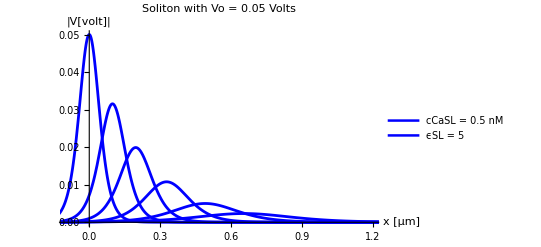

```mathematica
solSP22=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.05}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP22Data=Cases[solSP22,Line[{x__}]->x,∞];
```

{{-0.27,0.0000159142},{-0.26952,0.0000161837},{-0.269039,0.0000164576},{-0.268079,0.0000170196},{-0.266158,0.0000182016},{-0.265677,0.0000185098},{-0.265197,0.0000188231},{-0.264237,0.0000194658},{-0.262315,0.0000208177},{-0.261835,0.0000211701},{-0.261355,0.0000215285},{-0.260394,0.0000222636},{-0.258473,0.0000238098},{-0.254631,0.0000272317},{-0.25415,0.0000276926},{-0.25367,0.0000281614},{-0.25271,0.0000291228},{-0.250788,0.0000311453},{-0.250308,0.0000316724},{-0.249828,0.0000322085},{-0.248867,0.0000333081},{-0.246946,0.0000356211},{-0.246466,0.000036224},{-0.245986,0.0000368371},{-0.245025,0.0000380946},{-0.243104,0.0000407398},{-0.239262,0.0000465938},{-0.238741,0.0000474493},{-0.23822,0.0000483204},{-0.237179,0.000050111},{-0.235096,0.0000538936},{-0.234575,0.000054883},{-0.234055,0.0000558906},{-0.233013,0.0000579616},{-0.230931,0.0000623364},{-0.23041,0.0000634807},{-0.229889,0.0000646461},{-0.228848,0.0000670412},{-0.226765,0.0000721009},{-0.2226,0.0000833936},{-0.222079,0.0000849241},{-0.221558,0.0000864828},{-0.220517,0.0000896863},{-0.218434,0.0000964533},{-0.217913,0.0000982233},{-0.217393,0.000100026},{-0.216351,0.00010373},{-0.214269,0.000111556},{-0.213748,0.000113603},{-0.213227,0.000115687},{-0.212186,0.000119971},{-0.210103,0.00012902},{-0.205938,0.000149214},{-0.205451,0.000151768},{-0.204965,0.000154366},{-0.203993,0.000159695},{-0.202048,0.00017091},{-0.201562,0.000173834},{-0.201076,0.000176809},{-0.200103,0.000182911},{-0.198159,0.000195753},{-0.197672,0.000199102},{-0.197186,0.000202508},{-0.196214,0.000209495},{-0.194269,0.0002242},{-0.19038,0.00025677},{-0.189893,0.000261159},{-0.189407,0.000265624},{-0.188435,0.000274783},{-0.18649,0.000294057},{-0.186004,0.000299082},{-0.185518,0.000304193},{-0.184545,0.000314678},{-0.182601,0.00033674},{-0.182115,0.000342493},{-0.181628,0.000348343},{-0.180656,0.000360344},{-0.178711,0.000385596},{-0.174822,0.000441508},{-0.174345,0.000448893},{-0.173869,0.0004564},{-0.172915,0.000471793},{-0.171009,0.000504146},{-0.170532,0.000512573},{-0.170055,0.00052114},{-0.169102,0.000538705},{-0.167196,0.000575619},{-0.166719,0.000585234},{-0.166242,0.000595009},{-0.165289,0.000615047},{-0.163382,0.000657158},{-0.159569,0.000750159},{-0.159093,0.000762667},{-0.158616,0.000775382},{-0.157663,0.000801446},{-0.155756,0.000856208},{-0.155279,0.000870468},{-0.154803,0.000884964},{-0.153849,0.000914677},{-0.151943,0.0009771},{-0.151466,0.000993353},{-0.15099,0.00100987},{-0.150036,0.00104374},{-0.14813,0.00111487},{-0.144317,0.00127181},{-0.143799,0.0012947},{-0.143282,0.001318},{-0.142248,0.00136585},{-0.14018,0.00146675},{-0.139663,0.0014931},{-0.139146,0.00151991},{-0.138112,0.00157497},{-0.136044,0.00169105},{-0.135527,0.00172136},{-0.13501,0.0017522},{-0.133976,0.00181552},{-0.131907,0.00194896},{-0.127771,0.00224529},{-0.127254,0.0022853},{-0.126737,0.002326},{-0.125703,0.00240953},{-0.123635,0.00258546},{-0.123118,0.00263136},{-0.122601,0.00267806},{-0.121567,0.00277386},{-0.119498,0.00297556},{-0.118981,0.00302817},{-0.118464,0.00308167},{-0.11743,0.00319143},{-0.115362,0.00342238},{-0.111226,0.00393348},{-0.110743,0.00399767},{-0.110261,0.00406286},{-0.109295,0.00419629},{-0.107365,0.0044758},{-0.106883,0.00454839},{-0.1064,0.00462211},{-0.105435,0.00477295},{-0.103505,0.00508872},{-0.103022,0.00517069},{-0.10254,0.00525391},{-0.101575,0.00542413},{-0.0996447,0.00578021},{-0.0957844,0.00655876},{-0.0953018,0.00666264},{-0.0948193,0.00676803},{-0.0938542,0.00698345},{-0.0919241,0.00743327},{-0.0880638,0.00841297},{-0.0875812,0.0085433},{-0.0870987,0.00867543},{-0.0861336,0.00894519},{-0.0842034,0.00950721},{-0.0803431,0.0107252},{-0.0798202,0.0109001},{-0.0792972,0.0110776},{-0.0782514,0.0114399},{-0.0761596,0.0121948},{-0.0719761,0.0138297},{-0.0714532,0.0140461},{-0.0709302,0.0142652},{-0.0698843,0.0147116},{-0.0677926,0.0156374},{-0.0636091,0.0176223},{-0.0630861,0.0178829},{-0.0625632,0.0181463},{-0.0615173,0.0186814},{-0.0594256,0.0197844},{-0.055242,0.0221178},{-0.046875,0.0272386},{-0.0463616,0.0275692},{-0.0458482,0.0279014},{-0.0448214,0.02857},{-0.0427678,0.0299225},{-0.0386606,0.0326686},{-0.0381472,0.0330139},{-0.0376338,0.0333593},{-0.036607,0.03405},{-0.0345534,0.0354274},{-0.0304462,0.0381397},{-0.0299328,0.0384721},{-0.0294194,0.0388027},{-0.0283926,0.0394575},{-0.0263389,0.040738},{-0.0258255,0.0410512},{-0.0253121,0.0413614},{-0.0242853,0.0419719},{-0.0222317,0.0431497},{-0.0217183,0.0434342},{-0.0212049,0.0437146},{-0.0201781,0.044262},{-0.0181245,0.0452995},{-0.0176111,0.0455461},{-0.0170977,0.0457874},{-0.0160709,0.0462533},{-0.0140173,0.0471147},{-0.0135384,0.0473014},{-0.0130595,0.0474826},{-0.0121017,0.0478279},{-0.0116228,0.0479919},{-0.0111439,0.0481499},{-0.0101861,0.0484479},{-0.00970723,0.0485877},{-0.00922833,0.0487213},{-0.00827054,0.0489695},{-0.00779164,0.049084},{-0.00731274,0.0491919},{-0.00635495,0.0493881},{-0.00587605,0.0494762},{-0.00539716,0.0495577},{-0.00491826,0.0496323},{-0.00443936,0.0497001},{-0.00396047,0.0497612},{-0.00348157,0.0498153},{-0.00300267,0.0498625},{-0.00252378,0.0499028},{-0.00204488,0.0499362},{-0.00156598,0.0499626},{-0.00108708,0.049982},{-0.000608188,0.0499943},{-0.000129291,0.0499997},{0.000349606,0.0499981},{0.000828503,0.0499895},{0.0013074,0.0499739},{0.0017863,0.0499513},{0.00226519,0.0499217},{0.00274409,0.0498851},{0.00322299,0.0498417},{0.00370188,0.0497912},{0.00418078,0.0497339},{0.00465968,0.0496698},{0.00513857,0.0495988},{0.00561747,0.049521},{0.00609637,0.0494365},{0.00657527,0.0493453},{0.00705416,0.0492475},{0.00753306,0.0491431},{0.00801196,0.0490321},{0.00896975,0.0487908},{0.00944865,0.0486606},{0.00992754,0.0485242},{0.0108853,0.0482328},{0.0113642,0.0480779},{0.0118431,0.0479172},{0.0128009,0.0475781},{0.0132798,0.0473999},{0.0137587,0.0472162},{0.0147165,0.0468323},{0.0166321,0.0460014},{0.0171514,0.0457624},{0.0176707,0.0455178},{0.0187093,0.0450122},{0.0207865,0.0439398},{0.0249408,0.0415837},{0.0254601,0.0412723},{0.0259794,0.0409577},{0.027018,0.0403193},{0.0290952,0.0390104},{0.0332496,0.0362965},{0.0337689,0.0359511},{0.0342882,0.0356047},{0.0353268,0.0349096},{0.0374039,0.0335139},{0.0415583,0.0307267},{0.0498671,0.0253457},{0.0503518,0.0250449},{0.0508366,0.024746},{0.0518062,0.0241536},{0.0537454,0.022992},{0.0576237,0.0207689},{0.0581085,0.0205009},{0.0585933,0.0202352},{0.0595629,0.0197106},{0.061502,0.0186893},{0.0653804,0.0167601},{0.0658652,0.0165298},{0.0663499,0.0163018},{0.0673195,0.0158529},{0.0692587,0.0149839},{0.073137,0.013359},{0.0736218,0.0131663},{0.0741066,0.0129759},{0.0750762,0.012602},{0.0770154,0.011881},{0.0808937,0.0105436},{0.0813689,0.0103889},{0.0818442,0.0102363},{0.0827947,0.00993687},{0.0846957,0.00936098},{0.0884977,0.00829729},{0.088973,0.00817225},{0.0894483,0.00804892},{0.0903988,0.00780729},{0.0922998,0.00734369},{0.0961018,0.00649124},{0.0965771,0.00639136},{0.0970523,0.0062929},{0.0980028,0.0061002},{0.0999038,0.00573117},{0.100379,0.00564222},{0.100854,0.00555458},{0.101805,0.0053831},{0.103706,0.00505496},{0.104181,0.00497593},{0.104656,0.00489806},{0.105607,0.00474577},{0.107508,0.00445456},{0.11131,0.00392237},{0.111826,0.00385506},{0.112341,0.00378885},{0.113373,0.00365969},{0.115435,0.00341395},{0.115951,0.00335504},{0.116466,0.00329711},{0.117498,0.00318414},{0.11956,0.00296931},{0.120076,0.00291784},{0.120592,0.00286723},{0.121623,0.00276855},{0.123686,0.00258099},{0.127811,0.00224225},{0.128327,0.00220308},{0.128842,0.00216458},{0.129873,0.00208955},{0.131936,0.00194705},{0.132452,0.00191294},{0.132967,0.00187941},{0.133999,0.00181408},{0.136061,0.00169003},{0.136577,0.00166035},{0.137093,0.00163117},{0.138124,0.00157433},{0.140187,0.00146643},{0.144312,0.00127202},{0.144793,0.00125107},{0.145274,0.00123046},{0.146236,0.00119024},{0.148161,0.00111366},{0.148642,0.00109529},{0.149123,0.00107722},{0.150086,0.00104196},{0.15201,0.000974827},{0.152491,0.000958724},{0.152972,0.000942885},{0.153935,0.000911979},{0.155859,0.000853148},{0.159708,0.000746542},{0.16019,0.000734182},{0.160671,0.000722025},{0.161633,0.000698307},{0.163558,0.000653168},{0.164039,0.000642344},{0.16452,0.000631698},{0.165482,0.000610929},{0.167407,0.000571406},{0.167888,0.000561929},{0.168369,0.000552608},{0.169331,0.000534426},{0.171256,0.000499826},{0.175105,0.000437174},{0.175627,0.00042931},{0.176148,0.000421586},{0.177191,0.000406551},{0.179278,0.000378066},{0.179799,0.00037126},{0.180321,0.000364577},{0.181364,0.000351569},{0.18345,0.000326922},{0.183972,0.000321035},{0.184493,0.000315253},{0.185536,0.000303999},{0.187622,0.000282678},{0.191795,0.000244407},{0.192316,0.000240002},{0.192838,0.000235676},{0.193881,0.000227256},{0.195967,0.000211306},{0.196489,0.000207496},{0.19701,0.000203755},{0.198053,0.000196473},{0.20014,0.00018268},{0.200661,0.000179385},{0.201183,0.00017615},{0.202226,0.000169853},{0.204312,0.000157926},{0.208484,0.000136521},{0.208996,0.000134103},{0.209508,0.000131727},{0.210532,0.000127101},{0.21258,0.000118329},{0.213092,0.000116233},{0.213604,0.000114173},{0.214628,0.000110163},{0.216676,0.000102559},{0.217188,0.000100742},{0.2177,0.0000989562},{0.218724,0.0000954797},{0.220773,0.0000888886},{0.224869,0.000077039},{0.225381,0.0000756733},{0.225893,0.0000743319},{0.226917,0.0000717199},{0.228965,0.0000667679},{0.229477,0.0000655842},{0.229989,0.0000644216},{0.231013,0.0000621576},{0.233061,0.0000578654},{0.233573,0.0000568395},{0.234085,0.0000558317},{0.235109,0.0000538695},{0.237157,0.0000501494},{0.241253,0.0000434618},{0.24173,0.0000427426},{0.242208,0.0000420353},{0.243163,0.0000406557},{0.245073,0.0000380307},{0.245551,0.0000374014},{0.246028,0.0000367825},{0.246983,0.0000355752},{0.248893,0.0000332781},{0.249371,0.0000327274},{0.249848,0.0000321858},{0.250803,0.0000311293},{0.252713,0.0000291193},{0.256533,0.00002548},{0.257011,0.0000250583},{0.257488,0.0000246436},{0.258443,0.0000238346},{0.260353,0.0000222955},{0.260831,0.0000219265},{0.261308,0.0000215636},{0.262263,0.0000208557},{0.264173,0.0000195089},{0.264651,0.000019186},{0.265128,0.0000188685},{0.266083,0.000018249},{0.267993,0.0000170705},{0.271813,0.0000149369},{0.272331,0.0000146689},{0.272849,0.0000144058},{0.273885,0.0000138935},{0.275957,0.0000129231},{0.276474,0.0000126912},{0.276992,0.0000124635},{0.278028,0.0000120204},{0.2801,0.0000111807},{0.280618,0.0000109801},{0.281136,0.0000107832},{0.282171,0.0000103997},{0.284243,9.67327×10^-6},{0.288386,8.36904×10^-6},{0.288904,8.2189×10^-6},{0.289422,8.07144×10^-6},{0.290458,7.78443×10^-6},{0.292529,7.24065×10^-6},{0.293047,7.11075×10^-6},{0.293565,6.98317×10^-6},{0.294601,6.73485×10^-6},{0.296673,6.26439×10^-6},{0.297191,6.152×10^-6},{0.297709,6.04162×10^-6},{0.298744,5.82678×10^-6},{0.300816,5.41975×10^-6},{0.304959,4.68899×10^-6},{0.305443,4.61042×10^-6},{0.305926,4.53317×10^-6},{0.306893,4.38252×10^-6},{0.308826,4.09609×10^-6},{0.30931,4.02745×10^-6},{0.309793,3.95997×10^-6},{0.31076,3.82837×10^-6},{0.312694,3.57816×10^-6},{0.313177,3.5182×10^-6},{0.31366,3.45925×10^-6},{0.314627,3.34429×10^-6},{0.316561,3.12571×10^-6},{0.320428,2.73048×10^-6},{0.320911,2.68472×10^-6},{0.321395,2.63974×10^-6},{0.322362,2.55201×10^-6},{0.324295,2.38522×10^-6},{0.324779,2.34525×10^-6},{0.325262,2.30595×10^-6},{0.326229,2.22932×10^-6},{0.328162,2.08361×10^-6},{0.328646,2.0487×10^-6},{0.329129,2.01437×10^-6},{0.330096,1.94743×10^-6},{0.33203,1.82014×10^-6},{0.335897,1.58999×10^-6},{0.336421,1.56114×10^-6},{0.336944,1.53281×10^-6},{0.337992,1.4777×10^-6},{0.340087,1.37333×10^-6},{0.340611,1.34842×10^-6},{0.341135,1.32395×10^-6},{0.342182,1.27634×10^-6},{0.344278,1.1862×10^-6},{0.344801,1.16468×10^-6},{0.345325,1.14354×10^-6},{0.346373,1.10242×10^-6},{0.348468,1.02456×10^-6},{0.352658,8.84955×10^-7},{0.353182,8.68898×10^-7},{0.353706,8.53132×10^-7},{0.354754,8.22454×10^-7},{0.356849,7.64368×10^-7},{0.357373,7.50499×10^-7},{0.357896,7.36882×10^-7},{0.358944,7.10384×10^-7},{0.361039,6.60213×10^-7},{0.361563,6.48234×10^-7},{0.362087,6.36472×10^-7},{0.363134,6.13585×10^-7},{0.36523,5.7025×10^-7},{0.36942,4.92546×10^-7},{0.369934,4.8377×10^-7},{0.370448,4.75151×10^-7},{0.371477,4.5837×10^-7},{0.373534,4.26566×10^-7},{0.374048,4.18966×10^-7},{0.374563,4.11501×10^-7},{0.375591,3.96968×10^-7},{0.377648,3.69424×10^-7},{0.378162,3.62842×10^-7},{0.378677,3.56378×10^-7},{0.379705,3.43792×10^-7},{0.381762,3.19937×10^-7},{0.385876,2.7708×10^-7},{0.386391,2.72143×10^-7},{0.386905,2.67294×10^-7},{0.387933,2.57854×10^-7},{0.38999,2.39963×10^-7},{0.390505,2.35687×10^-7},{0.391019,2.31488×10^-7},{0.392047,2.23313×10^-7},{0.394104,2.07818×10^-7},{0.394619,2.04115×10^-7},{0.395133,2.00479×10^-7},{0.396162,1.93398×10^-7},{0.398219,1.79979×10^-7},{0.402333,1.5587×10^-7},{0.402812,1.53277×10^-7},{0.403292,1.50728×10^-7},{0.404252,1.45756×10^-7},{0.406171,1.36299×10^-7},{0.40665,1.34032×10^-7},{0.40713,1.31803×10^-7},{0.40809,1.27455×10^-7},{0.410009,1.19185×10^-7},{0.410489,1.17203×10^-7},{0.410968,1.15254×10^-7},{0.411928,1.11452×10^-7},{0.413847,1.0422×10^-7},{0.417685,9.11345×10^-8},{0.418165,8.96188×10^-8},{0.418644,8.81283×10^-8},{0.419604,8.52213×10^-8},{0.421523,7.96917×10^-8},{0.422003,7.83663×10^-8},{0.422482,7.7063×10^-8},{0.423442,7.45209×10^-8},{0.425361,6.96856×10^-8},{0.425841,6.85267×10^-8},{0.426321,6.7387×10^-8},{0.42728,6.51641×10^-8},{0.429199,6.09359×10^-8},{0.433037,5.32848×10^-8},{0.433557,5.23247×10^-8},{0.434077,5.13818×10^-8},{0.435118,4.95468×10^-8},{0.437198,4.60709×10^-8},{0.437719,4.52408×10^-8},{0.438239,4.44256×10^-8},{0.439279,4.2839×10^-8},{0.44136,3.98337×10^-8},{0.44188,3.91159×10^-8},{0.4424,3.84111×10^-8},{0.44344,3.70393×10^-8},{0.445521,3.44409×10^-8},{0.449682,2.97781×10^-8},{0.450202,2.92415×10^-8},{0.450722,2.87146×10^-8},{0.451763,2.76891×10^-8},{0.453843,2.57466×10^-8},{0.454364,2.52827×10^-8},{0.454884,2.48271×10^-8},{0.455924,2.39405×10^-8},{0.458005,2.2261×10^-8},{0.458525,2.18598×10^-8},{0.459045,2.14659×10^-8},{0.460085,2.06993×10^-8},{0.462166,1.92472×10^-8},{0.466327,1.66414×10^-8},{0.466813,1.63613×10^-8},{0.467298,1.60859×10^-8},{0.46827,1.55488×10^-8},{0.470212,1.4528×10^-8},{0.470698,1.42834×10^-8},{0.471184,1.4043×10^-8},{0.472155,1.35741×10^-8},{0.474098,1.26829×10^-8},{0.474583,1.24694×10^-8},{0.475069,1.22595×10^-8},{0.47604,1.18502×10^-8},{0.477983,1.10722×10^-8},{0.481868,9.66603×10^-9},{0.482354,9.50331×10^-9},{0.482839,9.34333×10^-9},{0.483811,9.0314×10^-9},{0.485753,8.43844×10^-9},{0.486239,8.29639×10^-9},{0.486724,8.15673×10^-9},{0.487696,7.88441×10^-9},{0.489638,7.36676×10^-9},{0.490124,7.24275×10^-9},{0.49061,7.12082×10^-9},{0.491581,6.88309×10^-9},{0.493524,6.43118×10^-9},{0.497409,5.61442×10^-9},{0.497885,5.52175×10^-9},{0.498361,5.4306×10^-9},{0.499313,5.25281×10^-9},{0.501218,4.91448×10^-9},{0.501694,4.83336×10^-9},{0.50217,4.75358×10^-9},{0.503122,4.59795×10^-9},{0.505027,4.3018×10^-9},{0.505503,4.23079×10^-9},{0.505979,4.16096×10^-9},{0.506931,4.02473×10^-9},{0.508836,3.7655×10^-9},{0.512644,3.29606×10^-9},{0.513121,3.24166×10^-9},{0.513597,3.18815×10^-9},{0.514549,3.08377×10^-9},{0.516453,2.88515×10^-9},{0.516929,2.83752×10^-9},{0.517406,2.79069×10^-9},{0.518358,2.69932×10^-9},{0.520262,2.52546×10^-9},{0.520738,2.48377×10^-9},{0.521214,2.44278×10^-9},{0.522167,2.3628×10^-9},{0.524071,2.21062×10^-9},{0.52788,1.93502×10^-9},{0.528397,1.9004×10^-9},{0.528913,1.86639×10^-9},{0.529946,1.80019×10^-9},{0.532012,1.67476×10^-9},{0.532529,1.64479×10^-9},{0.533045,1.61536×10^-9},{0.534078,1.55806×10^-9},{0.536144,1.4495×10^-9},{0.536661,1.42356×10^-9},{0.537177,1.39809×10^-9},{0.53821,1.3485×10^-9},{0.540276,1.25454×10^-9},{0.544408,1.0858×10^-9},{0.544925,1.06637×10^-9},{0.545442,1.04729×10^-9},{0.546475,1.01014×10^-9},{0.548541,9.39756×10^-10},{0.549057,9.22939×10^-10},{0.549574,9.06424×10^-10},{0.550607,8.74275×10^-10},{0.552673,8.13356×10^-10},{0.553189,7.98802×10^-10},{0.553706,7.84508×10^-10},{0.554739,7.56683×10^-10},{0.556805,7.03958×10^-10},{0.560937,6.09274×10^-10},{0.561419,5.99093×10^-10},{0.561901,5.89083×10^-10},{0.562865,5.69562×10^-10},{0.564793,5.32438×10^-10},{0.565275,5.23542×10^-10},{0.565757,5.14794×10^-10},{0.566721,4.97734×10^-10},{0.568649,4.65292×10^-10},{0.569131,4.57518×10^-10},{0.569613,4.49873×10^-10},{0.570577,4.34965×10^-10},{0.572505,4.06614×10^-10},{0.576361,3.55336×10^-10},{0.576843,3.49399×10^-10},{0.577325,3.43561×10^-10},{0.578289,3.32176×10^-10},{0.580217,3.10525×10^-10},{0.580699,3.05336×10^-10},{0.581181,3.00234×10^-10},{0.582145,2.90285×10^-10},{0.584073,2.71364×10^-10},{0.584555,2.6683×10^-10},{0.585037,2.62372×10^-10},{0.586001,2.53677×10^-10},{0.587929,2.37142×10^-10},{0.591785,2.07236×10^-10},{0.592308,2.03486×10^-10},{0.59283,1.99804×10^-10},{0.593875,1.92638×10^-10},{0.595965,1.79067×10^-10},{0.596487,1.75827×10^-10},{0.59701,1.72645×10^-10},{0.598054,1.66453×10^-10},{0.600144,1.54727×10^-10},{0.600666,1.51927×10^-10},{0.601189,1.49178×10^-10},{0.602234,1.43827×10^-10},{0.604323,1.33695×10^-10},{0.608502,1.15522×10^-10},{0.609025,1.13432×10^-10},{0.609547,1.11379×10^-10},{0.610592,1.07384×10^-10},{0.612682,9.98196×10^-11},{0.613204,9.80132×10^-11},{0.613727,9.62395×10^-11},{0.614771,9.27878×10^-11},{0.616861,8.62513×10^-11},{0.617383,8.46904×10^-11},{0.617906,8.31578×10^-11},{0.618951,8.01753×10^-11},{0.62104,7.45273×10^-11},{0.62522,6.4397×10^-11},{0.625732,6.32527×10^-11},{0.626245,6.21288×10^-11},{0.627271,5.99404×10^-11},{0.629322,5.57922×10^-11},{0.629835,5.48009×10^-11},{0.630348,5.38271×10^-11},{0.631374,5.19312×10^-11},{0.633425,4.83373×10^-11},{0.633938,4.74784×10^-11},{0.634451,4.66347×10^-11},{0.635477,4.49921×10^-11},{0.637528,4.18784×10^-11},{0.641631,3.62826×10^-11},{0.642144,3.56379×10^-11},{0.642657,3.50046×10^-11},{0.643683,3.37717×10^-11},{0.645734,3.14345×10^-11},{0.646247,3.0876×10^-11},{0.64676,3.03273×10^-11},{0.647786,2.92591×10^-11},{0.649837,2.72342×10^-11},{0.65035,2.67503×10^-11},{0.650863,2.6275×10^-11},{0.651889,2.53495×10^-11},{0.65394,2.35952×10^-11},{0.658043,2.04424×10^-11},{0.658522,2.01034×10^-11},{0.659,1.977×10^-11},{0.659957,1.91197×10^-11},{0.66187,1.78826×10^-11},{0.662349,1.7586×10^-11},{0.662827,1.72944×10^-11},{0.663784,1.67256×10^-11},{0.665697,1.56434×10^-11},{0.666175,1.53839×10^-11},{0.666654,1.51288×10^-11},{0.667611,1.46312×10^-11},{0.669524,1.36845×10^-11},{0.673351,1.19709×10^-11},{0.673829,1.17724×10^-11},{0.674308,1.15772×10^-11},{0.675264,1.11964×10^-11},{0.677178,1.04719×10^-11},{0.677656,1.02983×10^-11},{0.678135,1.01275×10^-11},{0.679091,9.79438×10^-12},{0.681005,9.16066×10^-12},{0.681483,9.00874×10^-12},{0.681961,8.85934×10^-12},{0.682918,8.56794×10^-12},{0.684832,8.01356×10^-12},{0.688659,7.01011×10^-12},{0.689177,6.88413×10^-12},{0.689696,6.76041×10^-12},{0.690734,6.5196×10^-12},{0.692809,6.06341×10^-12},{0.693327,5.95445×10^-12},{0.693846,5.84743×10^-12},{0.694884,5.63915×10^-12},{0.696959,5.24457×10^-12},{0.697478,5.15031×10^-12},{0.697996,5.05775×10^-12},{0.699034,4.8776×10^-12},{0.701109,4.5363×10^-12},{0.705259,3.92369×10^-12},{0.705778,3.85317×10^-12},{0.706297,3.78392×10^-12},{0.707334,3.64914×10^-12},{0.709409,3.3938×10^-12},{0.709928,3.33281×10^-12},{0.710447,3.27292×10^-12},{0.711484,3.15633×10^-12},{0.713559,2.93548×10^-12},{0.714078,2.88272×10^-12},{0.714597,2.83092×10^-12},{0.715634,2.73008×10^-12},{0.717709,2.53905×10^-12},{0.72186,2.19616×10^-12},{0.722344,2.15929×10^-12},{0.722828,2.12305×10^-12},{0.723797,2.05237×10^-12},{0.725734,1.91799×10^-12},{0.726218,1.8858×10^-12},{0.726702,1.85414×10^-12},{0.727671,1.79242×10^-12},{0.729608,1.67506×10^-12},{0.730092,1.64694×10^-12},{0.730576,1.6193×10^-12},{0.731545,1.56539×10^-12},{0.733482,1.4629×10^-12},{0.737356,1.27761×10^-12},{0.73784,1.25616×10^-12},{0.738324,1.23507×10^-12},{0.739293,1.19396×10^-12},{0.74123,1.11578×10^-12},{0.741714,1.09705×10^-12},{0.742198,1.07864×10^-12},{0.743167,1.04273×10^-12},{0.745104,9.74459×10^-13},{0.745588,9.58101×10^-13},{0.746073,9.42018×10^-13},{0.747041,9.10658×10^-13},{0.748978,8.51034×10^-13},{0.752852,7.43242×10^-13},{0.753327,7.31009×10^-13},{0.753802,7.18978×10^-13},{0.754751,6.95506×10^-13},{0.75665,6.50836×10^-13},{0.757125,6.40124×10^-13},{0.757599,6.29589×10^-13},{0.758549,6.09035×10^-13},{0.760448,5.69919×10^-13},{0.760922,5.60539×10^-13},{0.761397,5.51313×10^-13},{0.762347,5.33315×10^-13},{0.764246,4.99062×10^-13},{0.768043,4.37015×10^-13},{0.768518,4.29822×10^-13},{0.768993,4.22748×10^-13},{0.769942,4.08947×10^-13},{0.771841,3.82682×10^-13},{0.772316,3.76384×10^-13},{0.772791,3.70189×10^-13},{0.77374,3.58104×10^-13},{0.775639,3.35104×10^-13},{0.776114,3.29589×10^-13},{0.776588,3.24164×10^-13},{0.777538,3.13581×10^-13},{0.779437,2.93441×10^-13},{0.783234,2.56958×10^-13},{0.78375,2.52373×10^-13},{0.784265,2.47869×10^-13},{0.785295,2.391×10^-13},{0.787355,2.22483×10^-13},{0.787871,2.18513×10^-13},{0.788386,2.14613×10^-13},{0.789416,2.07021×10^-13},{0.791476,1.92634×10^-13},{0.791991,1.89196×10^-13},{0.792507,1.85819×10^-13},{0.793537,1.79246×10^-13},{0.795597,1.66789×10^-13},{0.799718,1.44412×10^-13},{0.800233,1.41834×10^-13},{0.800749,1.39303×10^-13},{0.801779,1.34375×10^-13},{0.803839,1.25037×10^-13},{0.804354,1.22805×10^-13},{0.80487,1.20613×10^-13},{0.8059,1.16347×10^-13},{0.80796,1.08261×10^-13},{0.808475,1.06329×10^-13},{0.808991,1.04431×10^-13},{0.810021,1.00737×10^-13},{0.812081,9.3736×10^-14},{0.816202,8.11599×10^-14},{0.816683,7.98077×10^-14},{0.817163,7.8478×10^-14},{0.818125,7.58847×10^-14},{0.820047,7.09524×10^-14},{0.820528,6.97702×10^-14},{0.821008,6.86078×10^-14},{0.82197,6.63407×10^-14},{0.823892,6.20287×10^-14},{0.824373,6.09952×10^-14},{0.824853,5.9979×10^-14},{0.825815,5.7997×10^-14},{0.827737,5.42274×10^-14},{0.831582,4.74072×10^-14},{0.832543,4.58406×10^-14},{0.833504,4.43258×10^-14},{0.835427,4.14448×10^-14},{0.836388,4.00753×10^-14},{0.837349,3.8751×10^-14},{0.839272,3.62323×10^-14},{0.840233,3.5035×10^-14},{0.841194,3.38773×10^-14},{0.843117,3.16753×10^-14},{0.846962,2.76915×10^-14},{0.848004,2.6701×10^-14},{0.849046,2.57458×10^-14},{0.85113,2.39368×10^-14},{0.852172,2.30805×10^-14},{0.853214,2.22549×10^-14},{0.855298,2.06912×10^-14},{0.85634,1.9951×10^-14},{0.857382,1.92373×10^-14},{0.859466,1.78856×10^-14},{0.863634,1.54605×10^-14},{0.864676,1.49074×10^-14},{0.865718,1.43742×10^-14},{0.867802,1.33642×10^-14},{0.868844,1.28861×10^-14},{0.869886,1.24251×10^-14},{0.87197,1.15521×10^-14},{0.873012,1.11388×10^-14},{0.874055,1.07404×10^-14},{0.876139,9.98572×10^-15},{0.880307,8.63174×10^-15},{0.882253,8.06405×10^-15},{0.884199,7.5337×10^-15},{0.886145,7.03823×10^-15},{0.888091,6.57534×10^-15},{0.890037,6.14289×10^-15},{0.891983,5.73889×10^-15},{0.895875,5.00885×10^-15},{0.897821,4.67943×10^-15},{0.899767,4.37167×10^-15},{0.901713,4.08416×10^-15},{0.903659,3.81555×10^-15},{0.905605,3.56461×10^-15},{0.907551,3.33018×10^-15},{0.911443,2.90654×10^-15},{0.915259,2.54358×10^-15},{0.919075,2.22594×10^-15},{0.922891,1.94797×10^-15},{0.926707,1.70471×10^-15},{0.930522,1.49182×10^-15},{0.934338,1.30553×10^-15},{0.938154,1.14249×10^-15},{0.94197,9.99821×10^-16},{0.946109,8.65134×10^-16},{0.950248,7.48592×10^-16},{0.950765,7.35174×10^-16},{0.951282,7.21997×10^-16},{0.952317,6.96347×10^-16},{0.954387,6.47748×10^-16},{0.958526,5.6049×10^-16},{0.966804,4.19653×10^-16},{0.975082,3.14205×10^-16},{0.975564,3.08946×10^-16},{0.976047,3.03774×10^-16},{0.977013,2.9369×10^-16},{0.978945,2.74515×10^-16},{0.982808,2.39838×10^-16},{0.990533,1.83072×10^-16},{1.00599,1.06667×10^-16},{1.03947,3.30823×10^-17},{1.07235,1.04816×10^-17},{1.10302,3.58743×10^-18},{1.13628,1.12173×10^-18},{1.16733,3.78894×10^-19},{1.19776,1.30742×10^-19},{1.23079,4.12152×10^-20},{1.2616,1.40355×10^-20},{1.26214,1.37742×10^-20},{1.26268,1.35178×10^-20},{1.26375,1.30193×10^-20},{1.2659,1.20767×10^-20},{1.2702,1.03913×10^-20},{1.2788,7.69322×10^-21},{1.27934,7.55002×10^-21},{1.27988,7.40949×10^-21},{1.28095,7.13622×10^-21},{1.2831,6.61955×10^-21},{1.2874,5.69572×10^-21},{1.28794,5.5897×10^-21},{1.28848,5.48566×10^-21},{1.28955,5.28334×10^-21},{1.2917,4.90082×10^-21},{1.29224,4.8096×10^-21},{1.29278,4.72007×10^-21},{1.29385,4.54599×10^-21},{1.29439,4.46138×10^-21},{1.29493,4.37833×10^-21},{1.29546,4.29684×10^-21},{1.296,4.21686×10^-21},{-0.27,4.54902×10^-6},{-0.26952,4.61009×10^-6},{-0.269039,4.67198×10^-6},{-0.268079,4.79825×10^-6},{-0.266158,5.06114×10^-6},{-0.262315,5.6309×10^-6},{-0.261835,5.70649×10^-6},{-0.261355,5.78309×10^-6},{-0.260394,5.93939×10^-6},{-0.258473,6.26479×10^-6},{-0.254631,6.97004×10^-6},{-0.25415,7.0636×10^-6},{-0.25367,7.15842×10^-6},{-0.25271,7.3519×10^-6},{-0.250788,7.75467×10^-6},{-0.246946,8.62761×10^-6},{-0.246466,8.74342×10^-6},{-0.245986,8.86079×10^-6},{-0.245025,9.10027×10^-6},{-0.243104,9.59881×10^-6},{-0.239262,0.0000106793},{-0.238741,0.0000108348},{-0.23822,0.0000109926},{-0.237179,0.000011315},{-0.235096,0.0000119885},{-0.230931,0.0000134582},{-0.23041,0.0000136541},{-0.229889,0.0000138529},{-0.228848,0.0000142592},{-0.226765,0.0000151079},{-0.2226,0.0000169599},{-0.222079,0.0000172068},{-0.221558,0.0000174573},{-0.220517,0.0000179693},{-0.218434,0.0000190388},{-0.214269,0.0000213725},{-0.213748,0.0000216836},{-0.213227,0.0000219992},{-0.212186,0.0000226444},{-0.210103,0.000023992},{-0.205938,0.0000269326},{-0.205451,0.0000272984},{-0.204965,0.0000276693},{-0.203993,0.0000284262},{-0.202048,0.0000300026},{-0.198159,0.0000334224},{-0.197672,0.0000338764},{-0.197186,0.0000343365},{-0.196214,0.0000352757},{-0.194269,0.0000372317},{-0.19038,0.0000414749},{-0.189893,0.0000420382},{-0.189407,0.0000426092},{-0.188435,0.0000437745},{-0.18649,0.0000462014},{-0.182601,0.0000514661},{-0.182115,0.000052165},{-0.181628,0.0000528733},{-0.180656,0.0000543191},{-0.178711,0.0000573301},{-0.174822,0.0000638616},{-0.174345,0.0000647115},{-0.173869,0.0000655727},{-0.172915,0.0000673297},{-0.171009,0.000070986},{-0.167196,0.0000789042},{-0.166719,0.0000799541},{-0.166242,0.0000810179},{-0.165289,0.0000831881},{-0.163382,0.0000877044},{-0.159569,0.0000974846},{-0.159093,0.0000987813},{-0.158616,0.000100095},{-0.157663,0.000102776},{-0.155756,0.000108353},{-0.151943,0.000120432},{-0.151466,0.000122033},{-0.15099,0.000123656},{-0.150036,0.000126966},{-0.14813,0.000133854},{-0.144317,0.000148768},{-0.143799,0.000150914},{-0.143282,0.000153091},{-0.142248,0.000157539},{-0.14018,0.000166826},{-0.136044,0.00018707},{-0.135527,0.000189767},{-0.13501,0.000192502},{-0.133976,0.000198092},{-0.131907,0.000209762},{-0.127771,0.000235196},{-0.127254,0.000238584},{-0.126737,0.00024202},{-0.125703,0.000249042},{-0.123635,0.000263701},{-0.119498,0.000295644},{-0.118981,0.000299899},{-0.118464,0.000304214},{-0.11743,0.000313032},{-0.115362,0.000331437},{-0.111226,0.000371537},{-0.110743,0.000376518},{-0.110261,0.000381566},{-0.109295,0.000391864},{-0.107365,0.000413297},{-0.103505,0.000459716},{-0.103022,0.000465871},{-0.10254,0.000472108},{-0.101575,0.000484831},{-0.0996447,0.000511306},{-0.0957844,0.000568633},{-0.0953018,0.000576232},{-0.0948193,0.000583933},{-0.0938542,0.00059964},{-0.0919241,0.000632321},{-0.0880638,0.000703062},{-0.0875812,0.000712437},{-0.0870987,0.000721937},{-0.0861336,0.000741312},{-0.0842034,0.000781616},{-0.0803431,0.000868824},{-0.0798202,0.000881353},{-0.0792972,0.00089406},{-0.0782514,0.000920017},{-0.0761596,0.000974178},{-0.0719761,0.00109208},{-0.0714532,0.00110777},{-0.0709302,0.00112368},{-0.0698843,0.00115618},{-0.0677926,0.00122396},{-0.0636091,0.00137141},{-0.0630861,0.00139103},{-0.0625632,0.00141091},{-0.0615173,0.00145152},{-0.0594256,0.00153618},{-0.055242,0.00172017},{-0.0547191,0.00174463},{-0.0541962,0.00176942},{-0.0531503,0.00182003},{-0.0510585,0.00192549},{-0.046875,0.00215443},{-0.0463616,0.00218428},{-0.0458482,0.00221452},{-0.0448214,0.00227621},{-0.0427678,0.00240458},{-0.0386606,0.00268244},{-0.0381472,0.00271926},{-0.0376338,0.00275656},{-0.036607,0.00283262},{-0.0345534,0.00299076},{-0.0304462,0.00333245},{-0.0299328,0.00337766},{-0.0294194,0.00342345},{-0.0283926,0.00351678},{-0.0263389,0.00371063},{-0.0222317,0.00412857},{-0.0217183,0.00418377},{-0.0212049,0.00423966},{-0.0201781,0.00435351},{-0.0181245,0.00458967},{-0.0140173,0.00509743},{-0.0135384,0.00515984},{-0.0130595,0.00522293},{-0.0121017,0.00535121},{-0.0101861,0.00561627},{-0.00635495,0.00618169},{-0.00587605,0.00625578},{-0.00539716,0.00633065},{-0.00443936,0.00648274},{-0.00252378,0.00679648},{0.0013074,0.00746331},{0.0017863,0.00755045},{0.00226519,0.00763844},{0.00322299,0.00781701},{0.00513857,0.00818459},{0.00896975,0.00896241},{0.0166321,0.0106935},{0.0171514,0.0108194},{0.0176707,0.0109464},{0.0187093,0.0112036},{0.0207865,0.0117312},{0.0249408,0.0128378},{0.0332496,0.0152459},{0.0498671,0.0206412},{0.0503518,0.0208046},{0.0508366,0.020968},{0.0518062,0.0212948},{0.0537454,0.0219477},{0.0576237,0.0232429},{0.0581085,0.0234032},{0.0585933,0.023563},{0.0595629,0.023881},{0.061502,0.0245096},{0.0653804,0.0257292},{0.0658652,0.0258774},{0.0663499,0.0260245},{0.0673195,0.0263152},{0.0692587,0.0268821},{0.073137,0.0279482},{0.0736218,0.0280744},{0.0741066,0.0281988},{0.0750762,0.0284425},{0.0770154,0.0289077},{0.0775001,0.0290192},{0.0779849,0.0291287},{0.0789545,0.0293416},{0.0808937,0.0297418},{0.0813689,0.0298346},{0.0818442,0.0299251},{0.0827947,0.0300995},{0.0832699,0.0301834},{0.0837452,0.030265},{0.0846957,0.0304211},{0.085171,0.0304956},{0.0856462,0.0305678},{0.0865967,0.0307048},{0.087072,0.0307696},{0.0875472,0.030832},{0.0884977,0.0309492},{0.088973,0.031004},{0.0894483,0.0310562},{0.0899235,0.0311058},{0.0903988,0.0311529},{0.090874,0.0311973},{0.0913493,0.0312391},{0.0922998,0.0313148},{0.092775,0.0313487},{0.0932503,0.0313798},{0.0937255,0.0314083},{0.0942008,0.0314341},{0.094676,0.0314572},{0.0951513,0.0314775},{0.0956266,0.0314952},{0.0961018,0.0315101},{0.0965771,0.0315222},{0.0970523,0.0315317},{0.0975276,0.0315383},{0.0980028,0.0315423},{0.0984781,0.0315435},{0.0989533,0.0315419},{0.0994286,0.0315376},{0.0999038,0.0315306},{0.100379,0.0315208},{0.100854,0.0315083},{0.10133,0.031493},{0.101805,0.0314751},{0.10228,0.0314544},{0.102755,0.0314309},{0.103231,0.0314048},{0.103706,0.031376},{0.104181,0.0313445},{0.104656,0.0313103},{0.105132,0.0312734},{0.105607,0.0312339},{0.106082,0.0311918},{0.106557,0.031147},{0.107508,0.0310496},{0.107983,0.0309971},{0.108458,0.030942},{0.109409,0.0308241},{0.11131,0.0305587},{0.111826,0.0304799},{0.112341,0.0303984},{0.113373,0.030227},{0.115435,0.0298521},{0.115951,0.0297518},{0.116466,0.029649},{0.117498,0.029436},{0.11956,0.0289814},{0.120076,0.0288621},{0.120592,0.0287405},{0.121623,0.0284909},{0.123686,0.0279672},{0.127811,0.026832},{0.128327,0.0266827},{0.128842,0.026532},{0.129873,0.0262264},{0.131936,0.0255996},{0.136061,0.0242942},{0.144312,0.0215567},{0.144793,0.0213946},{0.145274,0.0212325},{0.146236,0.0209081},{0.148161,0.0202598},{0.15201,0.0189711},{0.159708,0.0164678},{0.16019,0.016316},{0.160671,0.0161649},{0.161633,0.0158647},{0.163558,0.0152726},{0.167407,0.0141251},{0.175105,0.0119923},{0.175627,0.0118561},{0.176148,0.011721},{0.177191,0.0114541},{0.179278,0.0109333},{0.18345,0.00994474},{0.183972,0.00982612},{0.184493,0.00970859},{0.185536,0.00947683},{0.187622,0.0090264},{0.191795,0.00817713},{0.192316,0.00807574},{0.192838,0.00797539},{0.193881,0.00777779},{0.195967,0.00739489},{0.20014,0.00667696},{0.200661,0.00659158},{0.201183,0.00650716},{0.202226,0.00634113},{0.204312,0.00602016},{0.208484,0.00542102},{0.208996,0.00535129},{0.209508,0.00528237},{0.210532,0.00514691},{0.21258,0.00488538},{0.216676,0.00439825},{0.217188,0.0043406},{0.2177,0.00428364},{0.218724,0.00417178},{0.220773,0.00395613},{0.224869,0.00355556},{0.225381,0.00350824},{0.225893,0.00346152},{0.226917,0.00336981},{0.228965,0.00319322},{0.233061,0.00286592},{0.233573,0.00282732},{0.234085,0.00278922},{0.235109,0.00271447},{0.237157,0.00257066},{0.241253,0.0023046},{0.24173,0.00227536},{0.242208,0.00224648},{0.243163,0.00218977},{0.245073,0.00208046},{0.248893,0.00187742},{0.249371,0.00185343},{0.249848,0.00182974},{0.250803,0.00178323},{0.252713,0.00169363},{0.256533,0.00152737},{0.257011,0.00150774},{0.257488,0.00148835},{0.258443,0.00145031},{0.260353,0.00137705},{0.264173,0.00124123},{0.264651,0.0012252},{0.265128,0.00120937},{0.266083,0.00117832},{0.267993,0.00111855},{0.271813,0.00100779},{0.272331,0.000993634},{0.272849,0.00097967},{0.273885,0.000952318},{0.275957,0.00089985},{0.2801,0.000803315},{0.280618,0.000791991},{0.281136,0.000780824},{0.282171,0.000758955},{0.284243,0.000717016},{0.288386,0.000639891},{0.288904,0.000630847},{0.289422,0.000621929},{0.290458,0.000604467},{0.292529,0.000570986},{0.296673,0.000509439},{0.297191,0.000502224},{0.297709,0.00049511},{0.298744,0.00048118},{0.300816,0.000454478},{0.304959,0.000405407},{0.305443,0.000400037},{0.305926,0.000394736},{0.306893,0.000384345},{0.308826,0.00036437},{0.312694,0.000327466},{0.313177,0.000323122},{0.31366,0.000318836},{0.314627,0.000310432},{0.316561,0.000294281},{0.320428,0.000264445},{0.320911,0.000260934},{0.321395,0.000257469},{0.322362,0.000250677},{0.324295,0.000237622},{0.328162,0.000213511},{0.328646,0.000210674},{0.329129,0.000207875},{0.330096,0.000202386},{0.33203,0.000191839},{0.335897,0.000172361},{0.336421,0.000169879},{0.336944,0.000167432},{0.337992,0.000162645},{0.340087,0.000153475},{0.344278,0.000136654},{0.344801,0.000134685},{0.345325,0.000132745},{0.346373,0.000128947},{0.348468,0.000121673},{0.352658,0.000108332},{0.353182,0.00010677},{0.353706,0.000105231},{0.354754,0.000102219},{0.356849,0.0000964512},{0.361039,0.0000858717},{0.361563,0.0000846335},{0.362087,0.0000834131},{0.363134,0.0000810248},{0.36523,0.0000764511},{0.36942,0.000068063},{0.369934,0.000067099},{0.370448,0.0000661487},{0.371477,0.0000642882},{0.373534,0.0000607226},{0.377648,0.0000541732},{0.378162,0.0000534058},{0.378677,0.0000526493},{0.379705,0.0000511682},{0.381762,0.0000483297},{0.385876,0.0000431161},{0.386391,0.0000425052},{0.386905,0.000041903},{0.387933,0.000040724},{0.38999,0.0000384645},{0.394104,0.0000343145},{0.394619,0.0000338283},{0.395133,0.0000333489},{0.396162,0.0000324105},{0.398219,0.0000306121},{0.402333,0.0000273089},{0.402812,0.0000269477},{0.403292,0.0000265913},{0.404252,0.0000258925},{0.406171,0.0000245494},{0.410009,0.0000220687},{0.410489,0.0000217768},{0.410968,0.0000214887},{0.411928,0.0000209239},{0.413847,0.0000198385},{0.417685,0.0000178337},{0.418165,0.0000175978},{0.418644,0.000017365},{0.419604,0.0000169086},{0.421523,0.0000160314},{0.425361,0.0000144112},{0.425841,0.0000142206},{0.426321,0.0000140324},{0.42728,0.0000136636},{0.429199,0.0000129547},{0.433037,0.0000116454},{0.433557,0.0000114785},{0.434077,0.0000113139},{0.435118,0.0000109918},{0.437198,0.0000103749},{0.44136,9.24299×10^-6},{0.44188,9.11048×10^-6},{0.4424,8.97986×10^-6},{0.44344,8.72422×10^-6},{0.445521,8.23455×10^-6},{0.449682,7.33613×10^-6},{0.450202,7.23095×10^-6},{0.450722,7.12727×10^-6},{0.451763,6.92436×10^-6},{0.453843,6.53571×10^-6},{0.458005,5.82262×10^-6},{0.458525,5.73913×10^-6},{0.459045,5.65685×10^-6},{0.460085,5.4958×10^-6},{0.462166,5.18732×10^-6},{0.466327,4.62134×10^-6},{0.466813,4.55944×10^-6},{0.467298,4.49838×10^-6},{0.46827,4.37869×10^-6},{0.470212,4.14878×10^-6},{0.474098,3.72454×10^-6},{0.474583,3.67465×10^-6},{0.475069,3.62543×10^-6},{0.47604,3.52897×10^-6},{0.477983,3.34367×10^-6},{0.481868,3.00176×10^-6},{0.482354,2.96155×10^-6},{0.482839,2.92189×10^-6},{0.483811,2.84414×10^-6},{0.485753,2.6948×10^-6},{0.489638,2.41923×10^-6},{0.490124,2.38683×10^-6},{0.49061,2.35486×10^-6},{0.491581,2.2922×10^-6},{0.493524,2.17185×10^-6},{0.497409,1.94975×10^-6},{0.497885,1.92415×10^-6},{0.498361,1.89888×10^-6},{0.499313,1.84933×10^-6},{0.501218,1.75408×10^-6},{0.505027,1.57805×10^-6},{0.505503,1.55733×10^-6},{0.505979,1.53687×10^-6},{0.506931,1.49677×10^-6},{0.508836,1.41968×10^-6},{0.512644,1.27721×10^-6},{0.513121,1.26043×10^-6},{0.513597,1.24388×10^-6},{0.514549,1.21142×10^-6},{0.516453,1.14903×10^-6},{0.520262,1.03372×10^-6},{0.520738,1.02014×10^-6},{0.521214,1.00674×10^-6},{0.522167,9.80475×10^-7},{0.524071,9.29975×10^-7},{0.52788,8.36645×10^-7},{0.528397,8.24732×10^-7},{0.528913,8.12988×10^-7},{0.529946,7.90001×10^-7},{0.532012,7.45957×10^-7},{0.536144,6.65099×10^-7},{0.536661,6.55629×10^-7},{0.537177,6.46293×10^-7},{0.53821,6.28019×10^-7},{0.540276,5.93005×10^-7},{0.544408,5.28726×10^-7},{0.544925,5.21198×10^-7},{0.545442,5.13776×10^-7},{0.546475,4.99249×10^-7},{0.548541,4.71415×10^-7},{0.552673,4.20316×10^-7},{0.553189,4.14331×10^-7},{0.553706,4.08431×10^-7},{0.554739,3.96882×10^-7},{0.556805,3.74755×10^-7},{0.560937,3.34134×10^-7},{0.561419,3.29691×10^-7},{0.561901,3.25308×10^-7},{0.562865,3.16716×10^-7},{0.564793,3.00207×10^-7},{0.568649,2.69725×10^-7},{0.569131,2.6614×10^-7},{0.569613,2.62601×10^-7},{0.570577,2.55666×10^-7},{0.572505,2.42339×10^-7},{0.576361,2.17733×10^-7},{0.576843,2.14838×10^-7},{0.577325,2.11982×10^-7},{0.578289,2.06383×10^-7},{0.580217,1.95625×10^-7},{0.584073,1.75762×10^-7},{0.584555,1.73425×10^-7},{0.585037,1.7112×10^-7},{0.586001,1.666×10^-7},{0.587929,1.57916×10^-7},{0.591785,1.41882×10^-7},{0.592308,1.39839×10^-7},{0.59283,1.37825×10^-7},{0.593875,1.33884×10^-7},{0.595965,1.26337×10^-7},{0.600144,1.12495×10^-7},{0.600666,1.10875×10^-7},{0.601189,1.09278×10^-7},{0.602234,1.06154×10^-7},{0.604323,1.0017×10^-7},{0.608502,8.91949×10^-8},{0.609025,8.79105×10^-8},{0.609547,8.66445×10^-8},{0.610592,8.4167×10^-8},{0.612682,7.94225×10^-8},{0.616861,7.07208×10^-8},{0.617383,6.97023×10^-8},{0.617906,6.86986×10^-8},{0.618951,6.67342×10^-8},{0.62104,6.29724×10^-8},{0.62522,5.6073×10^-8},{0.625732,5.52801×10^-8},{0.626245,5.44985×10^-8},{0.627271,5.29682×10^-8},{0.629322,5.00354×10^-8},{0.633425,4.46478×10^-8},{0.633938,4.40165×10^-8},{0.634451,4.33942×10^-8},{0.635477,4.21757×10^-8},{0.637528,3.98404×10^-8},{0.641631,3.55506×10^-8},{0.642144,3.50479×10^-8},{0.642657,3.45524×10^-8},{0.643683,3.35822×10^-8},{0.645734,3.17227×10^-8},{0.649837,2.8307×10^-8},{0.65035,2.79068×10^-8},{0.650863,2.75122×10^-8},{0.651889,2.67396×10^-8},{0.65394,2.52591×10^-8},{0.658043,2.25393×10^-8},{0.658522,2.22419×10^-8},{0.659,2.19484×10^-8},{0.659957,2.13731×10^-8},{0.66187,2.02671×10^-8},{0.665697,1.8224×10^-8},{0.666175,1.79836×10^-8},{0.666654,1.77463×10^-8},{0.667611,1.72811×10^-8},{0.669524,1.63869×10^-8},{0.673351,1.4735×10^-8},{0.673829,1.45405×10^-8},{0.674308,1.43487×10^-8},{0.675264,1.39725×10^-8},{0.677178,1.32495×10^-8},{0.681005,1.19139×10^-8},{0.681483,1.17567×10^-8},{0.681961,1.16016×10^-8},{0.682918,1.12974×10^-8},{0.684832,1.07129×10^-8},{0.688659,9.6329×10^-9},{0.689177,9.49514×10^-9},{0.689696,9.35935×10^-9},{0.690734,9.09357×10^-9},{0.692809,8.58444×10^-9},{0.696959,7.65009×10^-9},{0.697478,7.54069×10^-9},{0.697996,7.43285×10^-9},{0.699034,7.22178×10^-9},{0.701109,6.81744×10^-9},{0.705259,6.07542×10^-9},{0.705778,5.98853×10^-9},{0.706297,5.90289×10^-9},{0.707334,5.73526×10^-9},{0.709409,5.41416×10^-9},{0.713559,4.82487×10^-9},{0.714078,4.75587×10^-9},{0.714597,4.68786×10^-9},{0.715634,4.55473×10^-9},{0.717709,4.29972×10^-9},{0.72186,3.83173×10^-9},{0.722344,3.78055×10^-9},{0.722828,3.73006×10^-9},{0.723797,3.63109×10^-9},{0.725734,3.44095×10^-9},{0.729608,3.09002×10^-9},{0.730092,3.04875×10^-9},{0.730576,3.00803×10^-9},{0.731545,2.92822×10^-9},{0.733482,2.77489×10^-9},{0.737356,2.49189×10^-9},{0.73784,2.45861×10^-9},{0.738324,2.42577×10^-9},{0.739293,2.36141×10^-9},{0.74123,2.23775×10^-9},{0.745104,2.00954×10^-9},{0.745588,1.9827×10^-9},{0.746073,1.95621×10^-9},{0.747041,1.90431×10^-9},{0.748978,1.80459×10^-9},{0.752852,1.62055×10^-9},{0.753327,1.59933×10^-9},{0.753802,1.57839×10^-9},{0.754751,1.53732×10^-9},{0.75665,1.45836×10^-9},{0.760448,1.31241×10^-9},{0.760922,1.29522×10^-9},{0.761397,1.27826×10^-9},{0.762347,1.24501×10^-9},{0.764246,1.18106×10^-9},{0.768043,1.06286×10^-9},{0.768518,1.04894×10^-9},{0.768993,1.03521×10^-9},{0.769942,1.00827×10^-9},{0.771841,9.56489×10^-10},{0.775639,8.60763×10^-10},{0.776114,8.49491×10^-10},{0.776588,8.38367×10^-10},{0.777538,8.16555×10^-10},{0.779437,7.74617×10^-10},{0.783234,6.97093×10^-10},{0.78375,6.87193×10^-10},{0.784265,6.77434×10^-10},{0.785295,6.5833×10^-10},{0.787355,6.21722×10^-10},{0.791476,5.54502×10^-10},{0.791991,5.46627×10^-10},{0.792507,5.38864×10^-10},{0.793537,5.23668×10^-10},{0.795597,4.94549×10^-10},{0.799718,4.41078×10^-10},{0.800233,4.34814×10^-10},{0.800749,4.28639×10^-10},{0.801779,4.16551×10^-10},{0.803839,3.93388×10^-10},{0.80796,3.50855×10^-10},{0.808475,3.45872×10^-10},{0.808991,3.4096×10^-10},{0.810021,3.31345×10^-10},{0.812081,3.1292×10^-10},{0.816202,2.79087×10^-10},{0.816683,2.75387×10^-10},{0.817163,2.71737×10^-10},{0.818125,2.6458×10^-10},{0.820047,2.50827×10^-10},{0.823892,2.25429×10^-10},{0.824373,2.2244×10^-10},{0.824853,2.19492×10^-10},{0.825815,2.13711×10^-10},{0.827737,2.02602×10^-10},{0.831582,1.82087×10^-10},{0.832063,1.79673×10^-10},{0.832543,1.77291×10^-10},{0.833504,1.72622×10^-10},{0.835427,1.63649×10^-10},{0.839272,1.47078×10^-10},{0.839752,1.45129×10^-10},{0.840233,1.43205×10^-10},{0.841194,1.39433×10^-10},{0.843117,1.32185×10^-10},{0.846962,1.18801×10^-10},{0.847483,1.17094×10^-10},{0.848004,1.15413×10^-10},{0.849046,1.12121×10^-10},{0.85113,1.05817×10^-10},{0.855298,9.42527×10^-11},{0.855819,9.2899×10^-11},{0.85634,9.15647×10^-11},{0.857382,8.89534×10^-11},{0.859466,8.3952×10^-11},{0.863634,7.47771×10^-11},{0.864155,7.37031×10^-11},{0.864676,7.26446×10^-11},{0.865718,7.05728×10^-11},{0.867802,6.66049×10^-11},{0.87197,5.93258×10^-11},{0.872491,5.84738×10^-11},{0.873012,5.76339×10^-11},{0.874055,5.59903×10^-11},{0.876139,5.28423×10^-11},{0.880307,4.70673×10^-11},{0.880793,4.64357×10^-11},{0.88128,4.58127×10^-11},{0.882253,4.45915×10^-11},{0.884199,4.2246×10^-11},{0.888091,3.79185×10^-11},{0.888577,3.74097×10^-11},{0.889064,3.69078×10^-11},{0.890037,3.5924×10^-11},{0.891983,3.40344×10^-11},{0.895875,3.05481×10^-11},{0.896362,3.01382×10^-11},{0.896848,2.97338×10^-11},{0.897821,2.89412×10^-11},{0.899767,2.74189×10^-11},{0.903659,2.46103×10^-11},{0.904146,2.42801×10^-11},{0.904632,2.39543×10^-11},{0.905605,2.33158×10^-11},{0.907551,2.20893×10^-11},{0.911443,1.98266×10^-11},{0.91192,1.95658×10^-11},{0.912397,1.93084×10^-11},{0.913351,1.88036×10^-11},{0.915259,1.78334×10^-11},{0.919075,1.60406×10^-11},{0.919552,1.58296×10^-11},{0.920029,1.56213×10^-11},{0.920983,1.5213×10^-11},{0.922891,1.44281×10^-11},{0.926707,1.29776×10^-11},{0.927184,1.28069×10^-11},{0.927661,1.26384×10^-11},{0.928614,1.2308×10^-11},{0.930522,1.16729×10^-11},{0.934338,1.04995×10^-11},{0.934815,1.03613×10^-11},{0.935292,1.0225×10^-11},{0.936246,9.95772×10^-12},{0.938154,9.44393×10^-12},{0.94197,8.49453×10^-12},{0.942487,8.37337×10^-12},{0.943004,8.25394×10^-12},{0.944039,8.02017×10^-12},{0.946109,7.57231×10^-12},{0.950248,6.75021×10^-12},{0.950765,6.65393×10^-12},{0.951282,6.55903×10^-12},{0.952317,6.37326×10^-12},{0.954387,6.01736×10^-12},{0.958526,5.36408×10^-12},{0.959043,5.28757×10^-12},{0.95956,5.21216×10^-12},{0.960595,5.06454×10^-12},{0.962665,4.78172×10^-12},{0.966804,4.26259×10^-12},{0.967321,4.20179×10^-12},{0.967838,4.14186×10^-12},{0.968873,4.02455×10^-12},{0.970943,3.79981×10^-12},{0.975082,3.38728×10^-12},{0.975564,3.34217×10^-12},{0.976047,3.29766×10^-12},{0.977013,3.21041×10^-12},{0.978945,3.04277×10^-12},{0.982808,2.73329×10^-12},{0.98329,2.69689×10^-12},{0.983773,2.66097×10^-12},{0.984739,2.59057×10^-12},{0.98667,2.4553×10^-12},{0.990533,2.20557×10^-12},{0.991016,2.1762×10^-12},{0.991499,2.14722×10^-12},{0.992465,2.09041×10^-12},{0.994396,1.98125×10^-12},{0.998259,1.77974×10^-12},{0.998742,1.75604×10^-12},{0.999225,1.73265×10^-12},{1.00019,1.68681×10^-12},{1.00212,1.59873×10^-12},{1.00599,1.43613×10^-12},{1.00651,1.41541×10^-12},{1.00703,1.39499×10^-12},{1.00808,1.35504×10^-12},{1.01017,1.27854×10^-12},{1.01436,1.13824×10^-12},{1.01488,1.12182×10^-12},{1.0154,1.10564×10^-12},{1.01645,1.07397×10^-12},{1.01854,1.01334×10^-12},{1.02273,9.0214×10^-13},{1.02325,8.89127×10^-13},{1.02378,8.76302×10^-13},{1.02482,8.51205×10^-13},{1.02692,8.03145×10^-13},{1.0311,7.15014×10^-13},{1.03163,7.047×10^-13},{1.03215,6.94536×10^-13},{1.0332,6.74644×10^-13},{1.03529,6.36553×10^-13},{1.03947,5.66703×10^-13},{1.03999,5.58676×10^-13},{1.0405,5.50764×10^-13},{1.04153,5.35273×10^-13},{1.04358,5.05587×10^-13},{1.04769,4.51062×10^-13},{1.04821,4.44673×10^-13},{1.04872,4.38375×10^-13},{1.04975,4.26046×10^-13},{1.0518,4.02417×10^-13},{1.05591,3.59018×10^-13},{1.05643,3.53934×10^-13},{1.05694,3.48921×10^-13},{1.05797,3.39107×10^-13},{1.06002,3.203×10^-13},{1.06413,2.85757×10^-13},{1.06465,2.8171×10^-13},{1.06516,2.7772×10^-13},{1.06619,2.69909×10^-13},{1.06824,2.5494×10^-13},{1.07235,2.27446×10^-13},{1.07283,2.2444×10^-13},{1.07331,2.21473×10^-13},{1.07427,2.15657×10^-13},{1.07619,2.04478×10^-13},{1.08002,1.8383×10^-13},{1.0805,1.814×10^-13},{1.08098,1.79002×10^-13},{1.08194,1.74301×10^-13},{1.08385,1.65267×10^-13},{1.08769,1.48578×10^-13},{1.08817,1.46614×10^-13},{1.08865,1.44676×10^-13},{1.08961,1.40877×10^-13},{1.09152,1.33575×10^-13},{1.09536,1.20086×10^-13},{1.09584,1.18499×10^-13},{1.09631,1.16932×10^-13},{1.09727,1.13862×10^-13},{1.09919,1.0796×10^-13},{1.10302,9.70579×10^-14},{1.10354,9.56676×10^-14},{1.10406,9.42972×10^-14},{1.1051,9.16151×10^-14},{1.10718,8.64774×10^-14},{1.11134,7.70504×10^-14},{1.11186,7.59466×10^-14},{1.11238,7.48588×10^-14},{1.11342,7.27295×10^-14},{1.11549,6.86509×10^-14},{1.11965,6.11671×10^-14},{1.12069,5.94273×10^-14},{1.12173,5.7737×10^-14},{1.12381,5.44992×10^-14},{1.12797,4.85581×10^-14},{1.129,4.71769×10^-14},{1.13004,4.5835×10^-14},{1.13212,4.32647×10^-14},{1.13628,3.85483×10^-14},{1.13725,3.75237×10^-14},{1.13822,3.65263×10^-14},{1.14016,3.46103×10^-14},{1.14404,3.10747×10^-14},{1.14501,3.02487×10^-14},{1.14598,2.94447×10^-14},{1.14792,2.79002×10^-14},{1.1518,2.505×10^-14},{1.15277,2.43841×10^-14},{1.15374,2.3736×10^-14},{1.15568,2.24909×10^-14},{1.15957,2.01933×10^-14},{1.16054,1.96566×10^-14},{1.16151,1.91341×10^-14},{1.16345,1.81305×10^-14},{1.16733,1.62783×10^-14},{1.16923,1.54408×10^-14},{1.17113,1.46464×10^-14},{1.17494,1.3178×10^-14},{1.17684,1.25×10^-14},{1.17874,1.18569×10^-14},{1.18255,1.06682×10^-14},{1.18445,1.01193×10^-14},{1.18635,9.59868×10^-15},{1.19016,8.63639×10^-15},{1.19206,8.19205×10^-15},{1.19396,7.77057×10^-15},{1.19776,6.99155×10^-15},{1.19983,6.60214×10^-15},{1.20189,6.23443×10^-15},{1.20602,5.55929×10^-15},{1.20808,5.24966×10^-15},{1.21015,4.95727×10^-15},{1.21428,4.42045×10^-15},{1.2184,3.94175×10^-15},{1.22253,3.5149×10^-15},{1.22666,3.13426×10^-15},{1.23079,2.79485×10^-15},{1.23464,2.51137×10^-15},{1.23849,2.25664×10^-15},{1.24234,2.02775×10^-15},{1.24619,1.82208×10^-15},{1.25005,1.63726×10^-15},{1.2539,1.4712×10^-15},{1.25775,1.32197×10^-15},{1.2616,1.18788×10^-15},{1.2702,9.35565×10^-16},{1.2788,7.36841×10^-16},{1.2874,5.80329×10^-16},{1.296,4.57061×10^-16},{-0.27,2.69467×10^-6},{-0.26952,2.72336×10^-6},{-0.269039,2.75236×10^-6},{-0.268079,2.81129×10^-6},{-0.266158,2.93295×10^-6},{-0.262315,3.19231×10^-6},{-0.261835,3.2263×10^-6},{-0.261355,3.26065×10^-6},{-0.260394,3.33046×10^-6},{-0.258473,3.4746×10^-6},{-0.254631,3.78185×10^-6},{-0.25415,3.82211×10^-6},{-0.25367,3.86281×10^-6},{-0.25271,3.94551×10^-6},{-0.250788,4.11626×10^-6},{-0.246946,4.48024×10^-6},{-0.239262,5.3076×10^-6},{-0.238741,5.36889×10^-6},{-0.23822,5.43089×10^-6},{-0.237179,5.55705×10^-6},{-0.235096,5.81823×10^-6},{-0.230931,6.37798×10^-6},{-0.23041,6.45163×10^-6},{-0.229889,6.52613×10^-6},{-0.228848,6.67773×10^-6},{-0.226765,6.99157×10^-6},{-0.2226,7.66418×10^-6},{-0.222079,7.75268×10^-6},{-0.221558,7.84221×10^-6},{-0.220517,8.02437×10^-6},{-0.218434,8.40148×10^-6},{-0.214269,9.2097×10^-6},{-0.213748,9.31605×10^-6},{-0.213227,9.42362×10^-6},{-0.212186,9.64251×10^-6},{-0.210103,0.0000100956},{-0.205938,0.0000110668},{-0.205451,0.0000111861},{-0.204965,0.0000113066},{-0.203993,0.0000115516},{-0.202048,0.0000120577},{-0.198159,0.0000131374},{-0.197672,0.0000132789},{-0.197186,0.000013422},{-0.196214,0.0000137129},{-0.194269,0.0000143136},{-0.19038,0.0000155952},{-0.189893,0.0000157632},{-0.189407,0.0000159331},{-0.188435,0.0000162783},{-0.18649,0.0000169914},{-0.182601,0.0000185126},{-0.174822,0.0000219754},{-0.174345,0.0000222075},{-0.173869,0.0000224421},{-0.172915,0.0000229187},{-0.171009,0.0000239023},{-0.167196,0.0000259981},{-0.166719,0.0000262726},{-0.166242,0.0000265501},{-0.165289,0.0000271138},{-0.163382,0.0000282774},{-0.159569,0.0000307564},{-0.159093,0.0000310812},{-0.158616,0.0000314094},{-0.157663,0.0000320762},{-0.155756,0.0000334526},{-0.151943,0.0000363849},{-0.144317,0.0000430424},{-0.143799,0.0000435354},{-0.143282,0.0000440342},{-0.142248,0.0000450488},{-0.14018,0.0000471488},{-0.136044,0.0000516464},{-0.135527,0.000052238},{-0.13501,0.0000528363},{-0.133976,0.0000540535},{-0.131907,0.0000565725},{-0.127771,0.0000619678},{-0.127254,0.0000626773},{-0.126737,0.000063395},{-0.125703,0.0000648551},{-0.123635,0.0000678767},{-0.119498,0.0000743479},{-0.118981,0.000075199},{-0.118464,0.0000760598},{-0.11743,0.0000778109},{-0.115362,0.0000814349},{-0.111226,0.0000891959},{-0.110743,0.000090148},{-0.110261,0.0000911103},{-0.109295,0.0000930658},{-0.107365,0.0000971032},{-0.103505,0.00010571},{-0.103022,0.000106838},{-0.10254,0.000107978},{-0.101575,0.000110294},{-0.0996447,0.000115077},{-0.0957844,0.000125271},{-0.0953018,0.000126607},{-0.0948193,0.000127957},{-0.0938542,0.000130701},{-0.0919241,0.000136365},{-0.0880638,0.000148439},{-0.0803431,0.000175872},{-0.0798202,0.000177903},{-0.0792972,0.000179957},{-0.0782514,0.000184137},{-0.0761596,0.000192788},{-0.0719761,0.000211324},{-0.0714532,0.000213762},{-0.0709302,0.000216228},{-0.0698843,0.000221245},{-0.0677926,0.00023163},{-0.0636091,0.000253876},{-0.0630861,0.000256802},{-0.0625632,0.000259761},{-0.0615173,0.000265782},{-0.0594256,0.000278243},{-0.055242,0.00030493},{-0.0547191,0.00030844},{-0.0541962,0.000311989},{-0.0531503,0.000319211},{-0.0510585,0.000334155},{-0.046875,0.000366155},{-0.0463616,0.000370286},{-0.0458482,0.000374463},{-0.0448214,0.000382956},{-0.0427678,0.000400521},{-0.0386606,0.000438075},{-0.0381472,0.000443008},{-0.0376338,0.000447995},{-0.036607,0.000458138},{-0.0345534,0.000479108},{-0.0304462,0.000523932},{-0.0299328,0.000529818},{-0.0294194,0.000535769},{-0.0283926,0.000547871},{-0.0263389,0.000572887},{-0.0222317,0.000626343},{-0.0217183,0.000633361},{-0.0212049,0.000640457},{-0.0201781,0.000654883},{-0.0181245,0.000684699},{-0.0140173,0.000748386},{-0.0135384,0.00075618},{-0.0130595,0.000764053},{-0.0121017,0.000780042},{-0.0101861,0.000813008},{-0.00635495,0.000883082},{-0.00587605,0.000892246},{-0.00539716,0.000901503},{-0.00443936,0.000920299},{-0.00252378,0.000959044},{0.0013074,0.00104136},{0.0017863,0.00105212},{0.00226519,0.00106299},{0.00322299,0.00108506},{0.00513857,0.00113053},{0.00896975,0.00122709},{0.0166321,0.00144467},{0.0171514,0.00146068},{0.0176707,0.00147687},{0.0187093,0.00150977},{0.0207865,0.00157768},{0.0249408,0.00172237},{0.0254601,0.00174132},{0.0259794,0.00176047},{0.027018,0.00179938},{0.0290952,0.00187965},{0.0332496,0.00205047},{0.0337689,0.00207283},{0.0342882,0.00209541},{0.0353268,0.00214128},{0.0374039,0.00223585},{0.0415583,0.00243684},{0.0498671,0.00289006},{0.0503518,0.00291876},{0.0508366,0.00294772},{0.0518062,0.00300642},{0.0537454,0.00312704},{0.0576237,0.0033815},{0.0581085,0.00341458},{0.0585933,0.00344796},{0.0595629,0.00351559},{0.061502,0.0036544},{0.0653804,0.00394667},{0.0658652,0.00398461},{0.0663499,0.00402287},{0.0673195,0.00410035},{0.0692587,0.00425922},{0.073137,0.00459292},{0.0808937,0.00532695},{0.0813689,0.0053749},{0.0818442,0.00542321},{0.0827947,0.00552089},{0.0846957,0.00572049},{0.0884977,0.0061369},{0.0961018,0.00703938},{0.0965771,0.00709888},{0.0970523,0.00715874},{0.0980028,0.00727955},{0.0999038,0.00752549},{0.103706,0.00803447},{0.11131,0.00911826},{0.111826,0.00919477},{0.112341,0.00927165},{0.113373,0.00942649},{0.115435,0.00974037},{0.11956,0.0103839},{0.127811,0.0117234},{0.128327,0.0118089},{0.128842,0.0118947},{0.129873,0.0120666},{0.131936,0.012412},{0.136061,0.0131072},{0.144312,0.0144955},{0.144793,0.0145755},{0.145274,0.0146555},{0.146236,0.0148148},{0.148161,0.015131},{0.15201,0.0157513},{0.152491,0.0158274},{0.152972,0.0159033},{0.153935,0.0160538},{0.155859,0.0163503},{0.159708,0.0169219},{0.16019,0.0169911},{0.160671,0.0170597},{0.161633,0.0171954},{0.163558,0.0174599},{0.167407,0.0179581},{0.167888,0.0180173},{0.168369,0.0180758},{0.169331,0.0181905},{0.171256,0.0184106},{0.175105,0.0188118},{0.175627,0.0188619},{0.176148,0.0189109},{0.177191,0.0190058},{0.179278,0.0191825},{0.179799,0.0192239},{0.180321,0.0192641},{0.181364,0.0193411},{0.18345,0.0194809},{0.183972,0.0195129},{0.184493,0.0195436},{0.185536,0.0196014},{0.186058,0.0196285},{0.186579,0.0196543},{0.187622,0.0197021},{0.188144,0.0197242},{0.188665,0.0197449},{0.189187,0.0197644},{0.189709,0.0197826},{0.19023,0.0197996},{0.190752,0.0198152},{0.191273,0.0198295},{0.191795,0.0198426},{0.192316,0.0198543},{0.192838,0.0198647},{0.193359,0.0198739},{0.193881,0.0198817},{0.194402,0.0198882},{0.194924,0.0198934},{0.195446,0.0198973},{0.195967,0.0198998},{0.196489,0.0199011},{0.19701,0.019901},{0.197532,0.0198996},{0.198053,0.0198969},{0.198575,0.0198929},{0.199096,0.0198876},{0.199618,0.019881},{0.20014,0.019873},{0.200661,0.0198637},{0.201183,0.0198532},{0.201704,0.0198413},{0.202226,0.0198281},{0.202747,0.0198137},{0.203269,0.0197979},{0.204312,0.0197625},{0.204833,0.0197429},{0.205355,0.019722},{0.206398,0.0196764},{0.20692,0.0196517},{0.207441,0.0196258},{0.208484,0.0195702},{0.208996,0.0195411},{0.209508,0.0195108},{0.210532,0.0194468},{0.21258,0.0193049},{0.213092,0.0192666},{0.213604,0.0192272},{0.214628,0.0191451},{0.216676,0.018968},{0.217188,0.0189211},{0.2177,0.0188731},{0.218724,0.0187743},{0.220773,0.0185646},{0.224869,0.0181008},{0.225381,0.0180389},{0.225893,0.0179762},{0.226917,0.0178483},{0.228965,0.0175833},{0.233061,0.0170191},{0.241253,0.0157803},{0.24173,0.0157045},{0.242208,0.0156284},{0.243163,0.0154753},{0.245073,0.0151657},{0.248893,0.0145356},{0.256533,0.0132511},{0.257011,0.0131704},{0.257488,0.0130898},{0.258443,0.0129285},{0.260353,0.0126065},{0.264173,0.0119664},{0.271813,0.0107144},{0.272331,0.0106314},{0.272849,0.0105486},{0.273885,0.010384},{0.275957,0.0100583},{0.2801,0.00942254},{0.288386,0.00822115},{0.288904,0.00814941},{0.289422,0.00807808},{0.290458,0.00793667},{0.292529,0.00765886},{0.296673,0.00712357},{0.304959,0.00613569},{0.305443,0.00608147},{0.305926,0.00602763},{0.306893,0.00592106},{0.308826,0.0057124},{0.312694,0.00531277},{0.313177,0.00526446},{0.31366,0.0052165},{0.314627,0.00512168},{0.316561,0.0049363},{0.320428,0.00458237},{0.320911,0.00453968},{0.321395,0.00449732},{0.322362,0.00441363},{0.324295,0.00425025},{0.328162,0.00393914},{0.335897,0.00337645},{0.336421,0.00334107},{0.336944,0.00330603},{0.337992,0.00323694},{0.340087,0.00310266},{0.344278,0.00284916},{0.344801,0.00281885},{0.345325,0.00278882},{0.346373,0.00272966},{0.348468,0.00261478},{0.352658,0.00239834},{0.353182,0.00237248},{0.353706,0.00234689},{0.354754,0.00229648},{0.356849,0.00219867},{0.361039,0.00201468},{0.36942,0.00168947},{0.369934,0.00167123},{0.370448,0.00165318},{0.371477,0.00161765},{0.373534,0.00154875},{0.377648,0.00141929},{0.378162,0.00140386},{0.378677,0.00138859},{0.379705,0.00135853},{0.381762,0.00130027},{0.385876,0.00119091},{0.386391,0.00117789},{0.386905,0.001165},{0.387933,0.00113963},{0.38999,0.00109049},{0.394104,0.0009983},{0.402333,0.000836146},{0.402812,0.00082753},{0.403292,0.000819002},{0.404252,0.000802201},{0.406171,0.000769607},{0.410009,0.000708265},{0.410489,0.000700942},{0.410968,0.000693695},{0.411928,0.000679419},{0.413847,0.000651728},{0.417685,0.000599635},{0.418165,0.000593418},{0.418644,0.000587265},{0.419604,0.000575147},{0.421523,0.000551646},{0.425361,0.000507447},{0.433037,0.000429274},{0.433557,0.00042443},{0.434077,0.00041964},{0.435118,0.00041022},{0.437198,0.000392004},{0.44136,0.000357939},{0.44188,0.000353893},{0.4424,0.000349892},{0.44344,0.000342024},{0.445521,0.00032681},{0.449682,0.000298368},{0.450202,0.00029499},{0.450722,0.00029165},{0.451763,0.000285082},{0.453843,0.000272384},{0.458005,0.000248648},{0.458525,0.00024583},{0.459045,0.000243043},{0.460085,0.000237563},{0.462166,0.000226969},{0.466327,0.00020717},{0.466813,0.000204974},{0.467298,0.000202802},{0.46827,0.000198525},{0.470212,0.000190239},{0.474098,0.000174685},{0.474583,0.000172832},{0.475069,0.000170999},{0.47604,0.00016739},{0.477983,0.000160398},{0.481868,0.000147275},{0.482354,0.000145712},{0.482839,0.000144165},{0.483811,0.000141121},{0.485753,0.000135222},{0.489638,0.000124153},{0.497409,0.000104651},{0.497885,0.000103561},{0.498361,0.000102482},{0.499313,0.000100357},{0.501218,0.0000962392},{0.505027,0.0000885022},{0.505503,0.0000875797},{0.505979,0.0000866669},{0.506931,0.0000848696},{0.508836,0.0000813859},{0.512644,0.0000748407},{0.513121,0.0000740604},{0.513597,0.0000732882},{0.514549,0.0000717679},{0.516453,0.000068821},{0.520262,0.0000632847},{0.52788,0.0000535106},{0.528397,0.0000529053},{0.528913,0.0000523068},{0.529946,0.0000511301},{0.532012,0.0000488554},{0.536144,0.0000446046},{0.536661,0.0000441},{0.537177,0.000043601},{0.53821,0.0000426199},{0.540276,0.0000407234},{0.544408,0.0000371796},{0.544925,0.0000367588},{0.545442,0.0000363428},{0.546475,0.0000355249},{0.548541,0.0000339439},{0.552673,0.0000309895},{0.553189,0.0000306388},{0.553706,0.000030292},{0.554739,0.0000296102},{0.556805,0.0000282921},{0.560937,0.0000258294},{0.561419,0.0000255564},{0.561901,0.0000252864},{0.562865,0.0000247548},{0.564793,0.0000237248},{0.568649,0.0000217916},{0.569131,0.0000215613},{0.569613,0.0000213334},{0.570577,0.0000208849},{0.572505,0.0000200159},{0.576361,0.0000183847},{0.576843,0.0000181904},{0.577325,0.0000179982},{0.578289,0.0000176197},{0.580217,0.0000168865},{0.584073,0.0000155103},{0.591785,0.0000130851},{0.592308,0.0000129353},{0.59283,0.0000127871},{0.593875,0.0000124959},{0.595965,0.0000119333},{0.600144,0.0000108828},{0.600666,0.0000107582},{0.601189,0.000010635},{0.602234,0.0000103928},{0.604323,9.9248×10^-6},{0.608502,9.05109×10^-6},{0.609025,8.94743×10^-6},{0.609547,8.84496×10^-6},{0.610592,8.64352×10^-6},{0.612682,8.25429×10^-6},{0.616861,7.52762×10^-6},{0.617383,7.4414×10^-6},{0.617906,7.35617×10^-6},{0.618951,7.18863×10^-6},{0.62104,6.8649×10^-6},{0.62522,6.26053×10^-6},{0.625732,6.19012×10^-6},{0.626245,6.12051×10^-6},{0.627271,5.98362×10^-6},{0.629322,5.71897×10^-6},{0.633425,5.22425×10^-6},{0.633938,5.16549×10^-6},{0.634451,5.1074×10^-6},{0.635477,4.99317×10^-6},{0.637528,4.77232×10^-6},{0.641631,4.35948×10^-6},{0.642144,4.31045×10^-6},{0.642657,4.26197×10^-6},{0.643683,4.16665×10^-6},{0.645734,3.98235×10^-6},{0.649837,3.63784×10^-6},{0.65035,3.59693×10^-6},{0.650863,3.55647×10^-6},{0.651889,3.47693×10^-6},{0.65394,3.32313×10^-6},{0.658043,3.03565×10^-6},{0.658522,3.00379×10^-6},{0.659,2.97227×10^-6},{0.659957,2.91021×10^-6},{0.66187,2.78996×10^-6},{0.665697,2.56416×10^-6},{0.666175,2.53726×10^-6},{0.666654,2.51063×10^-6},{0.667611,2.45821×10^-6},{0.669524,2.35664×10^-6},{0.673351,2.1659×10^-6},{0.673829,2.14318×10^-6},{0.674308,2.12068×10^-6},{0.675264,2.07641×10^-6},{0.677178,1.99061×10^-6},{0.681005,1.8295×10^-6},{0.688659,1.54534×10^-6},{0.689177,1.52776×10^-6},{0.689696,1.51038×10^-6},{0.690734,1.47622×10^-6},{0.692809,1.41018×10^-6},{0.696959,1.28684×10^-6},{0.697478,1.2722×10^-6},{0.697996,1.25773×10^-6},{0.699034,1.22928×10^-6},{0.701109,1.17429×10^-6},{0.705259,1.07158×10^-6},{0.705778,1.05939×10^-6},{0.706297,1.04734×10^-6},{0.707334,1.02365×10^-6},{0.709409,9.77858×10^-7},{0.713559,8.92331×10^-7},{0.714078,8.8218×10^-7},{0.714597,8.72144×10^-7},{0.715634,8.52414×10^-7},{0.717709,8.14284×10^-7},{0.72186,7.43063×10^-7},{0.722344,7.35169×10^-7},{0.722828,7.27359×10^-7},{0.723797,7.11987×10^-7},{0.725734,6.82212×10^-7},{0.729608,6.26344×10^-7},{0.730092,6.1969×10^-7},{0.730576,6.13107×10^-7},{0.731545,6.0015×10^-7},{0.733482,5.75051×10^-7},{0.737356,5.27959×10^-7},{0.73784,5.2235×10^-7},{0.738324,5.16801×10^-7},{0.739293,5.05879×10^-7},{0.74123,4.84723×10^-7},{0.745104,4.45027×10^-7},{0.752852,3.75123×10^-7},{0.753327,3.71216×10^-7},{0.753802,3.6735×10^-7},{0.754751,3.59737×10^-7},{0.75665,3.44983×10^-7},{0.760448,3.17265×10^-7},{0.760922,3.1396×10^-7},{0.761397,3.1069×10^-7},{0.762347,3.04252×10^-7},{0.764246,2.91773×10^-7},{0.768043,2.6833×10^-7},{0.768518,2.65536×10^-7},{0.768993,2.6277×10^-7},{0.769942,2.57325×10^-7},{0.771841,2.46771×10^-7},{0.775639,2.26943×10^-7},{0.783234,1.9194×10^-7},{0.78375,1.89772×10^-7},{0.784265,1.87628×10^-7},{0.785295,1.83413×10^-7},{0.787355,1.75265×10^-7},{0.791476,1.60038×10^-7},{0.791991,1.5823×10^-7},{0.792507,1.56442×10^-7},{0.793537,1.52928×10^-7},{0.795597,1.46134×10^-7},{0.799718,1.33438×10^-7},{0.800233,1.3193×10^-7},{0.800749,1.3044×10^-7},{0.801779,1.2751×10^-7},{0.803839,1.21845×10^-7},{0.80796,1.11259×10^-7},{0.808475,1.10002×10^-7},{0.808991,1.0876×10^-7},{0.810021,1.06316×10^-7},{0.812081,1.01593×10^-7},{0.816202,9.27666×10^-8},{0.816683,9.17885×10^-8},{0.817163,9.08207×10^-8},{0.818125,8.89156×10^-8},{0.820047,8.52244×10^-8},{0.823892,7.82954×10^-8},{0.824373,7.74699×10^-8},{0.824853,7.6653×10^-8},{0.825815,7.50451×10^-8},{0.827737,7.19297×10^-8},{0.831582,6.60816×10^-8},{0.832063,6.53849×10^-8},{0.832543,6.46954×10^-8},{0.833504,6.33383×10^-8},{0.835427,6.0709×10^-8},{0.839272,5.57731×10^-8},{0.846962,4.70727×10^-8},{0.847483,4.65349×10^-8},{0.848004,4.60032×10^-8},{0.849046,4.49581×10^-8},{0.85113,4.29384×10^-8},{0.855298,3.91672×10^-8},{0.855819,3.87197×10^-8},{0.85634,3.82773×10^-8},{0.857382,3.74077×10^-8},{0.859466,3.57272×10^-8},{0.863634,3.25893×10^-8},{0.864155,3.2217×10^-8},{0.864676,3.18489×10^-8},{0.865718,3.11253×10^-8},{0.867802,2.97271×10^-8},{0.87197,2.71162×10^-8},{0.872491,2.68064×10^-8},{0.873012,2.65001×10^-8},{0.874055,2.5898×10^-8},{0.876139,2.47346×10^-8},{0.880307,2.25622×10^-8},{0.880793,2.23214×10^-8},{0.88128,2.20832×10^-8},{0.882253,2.16143×10^-8},{0.884199,2.07063×10^-8},{0.888091,1.9003×10^-8},{0.888577,1.88002×10^-8},{0.889064,1.85996×10^-8},{0.890037,1.82047×10^-8},{0.891983,1.74399×10^-8},{0.895875,1.60053×10^-8},{0.896362,1.58345×10^-8},{0.896848,1.56655×10^-8},{0.897821,1.53329×10^-8},{0.899767,1.46887×10^-8},{0.903659,1.34805×10^-8},{0.911443,1.13539×10^-8},{0.91192,1.12351×10^-8},{0.912397,1.11175×10^-8},{0.913351,1.08861×10^-8},{0.915259,1.04375×10^-8},{0.919075,9.59507×10^-9},{0.919552,9.49466×10^-9},{0.920029,9.3953×10^-9},{0.920983,9.1997×10^-9},{0.922891,8.82062×10^-9},{0.926707,8.10869×10^-9},{0.927184,8.02383×10^-9},{0.927661,7.93987×10^-9},{0.928614,7.77457×10^-9},{0.930522,7.45421×10^-9},{0.934338,6.85256×10^-9},{0.94197,5.79103×10^-9},{0.942487,5.72532×10^-9},{0.943004,5.66037×10^-9},{0.944039,5.53265×10^-9},{0.946109,5.28581×10^-9},{0.950248,4.82466×10^-9},{0.950765,4.76992×10^-9},{0.951282,4.7158×10^-9},{0.952317,4.6094×10^-9},{0.954387,4.40375×10^-9},{0.958526,4.01956×10^-9},{0.959043,3.97395×10^-9},{0.95956,3.92886×10^-9},{0.960595,3.84022×10^-9},{0.962665,3.66888×10^-9},{0.966804,3.3488×10^-9},{0.967321,3.31081×10^-9},{0.967838,3.27324×10^-9},{0.968873,3.19939×10^-9},{0.970943,3.05664×10^-9},{0.975082,2.78998×10^-9},{0.975564,2.76042×10^-9},{0.976047,2.73118×10^-9},{0.977013,2.67362×10^-9},{0.978945,2.56212×10^-9},{0.982808,2.35288×10^-9},{0.98329,2.32796×10^-9},{0.983773,2.3033×10^-9},{0.984739,2.25476×10^-9},{0.98667,2.16072×10^-9},{0.990533,1.98426×10^-9},{0.991016,1.96324×10^-9},{0.991499,1.94245×10^-9},{0.992465,1.90151×10^-9},{0.994396,1.82221×10^-9},{0.998259,1.67339×10^-9},{1.00599,1.41123×10^-9},{1.00651,1.39504×10^-9},{1.00703,1.37903×10^-9},{1.00808,1.34756×10^-9},{1.01017,1.28677×10^-9},{1.01436,1.17329×10^-9},{1.01488,1.15983×10^-9},{1.0154,1.14652×10^-9},{1.01645,1.12036×10^-9},{1.01854,1.06982×10^-9},{1.02273,9.75469×10^-10},{1.02325,9.64276×10^-10},{1.02378,9.53212×10^-10},{1.02482,9.31463×10^-10},{1.02692,8.89441×10^-10},{1.0311,8.11001×10^-10},{1.03163,8.01695×10^-10},{1.03215,7.92496×10^-10},{1.0332,7.74414×10^-10},{1.03529,7.39478×10^-10},{1.03947,6.74263×10^-10},{1.03999,6.66667×10^-10},{1.0405,6.59156×10^-10},{1.04153,6.44387×10^-10},{1.04358,6.15835×10^-10},{1.04769,5.62469×10^-10},{1.04821,5.56132×10^-10},{1.04872,5.49867×10^-10},{1.04975,5.37547×10^-10},{1.0518,5.13728×10^-10},{1.05591,4.69211×10^-10},{1.05643,4.63925×10^-10},{1.05694,4.58698×10^-10},{1.05797,4.48421×10^-10},{1.06002,4.28552×10^-10},{1.06413,3.91415×10^-10},{1.06465,3.87006×10^-10},{1.06516,3.82645×10^-10},{1.06619,3.74072×10^-10},{1.06824,3.57497×10^-10},{1.07235,3.26518×10^-10},{1.07283,3.23085×10^-10},{1.07331,3.19688×10^-10},{1.07427,3.13002×10^-10},{1.07619,3.00045×10^-10},{1.08002,2.75718×10^-10},{1.0805,2.72819×10^-10},{1.08098,2.69951×10^-10},{1.08194,2.64304×10^-10},{1.08385,2.53363×10^-10},{1.08769,2.32821×10^-10},{1.08817,2.30373×10^-10},{1.08865,2.27951×10^-10},{1.08961,2.23183×10^-10},{1.09152,2.13944×10^-10},{1.09536,1.96598×10^-10},{1.10302,1.66011×10^-10},{1.10354,1.6412×10^-10},{1.10406,1.62249×10^-10},{1.1051,1.58573×10^-10},{1.10718,1.51468×10^-10},{1.11134,1.38199×10^-10},{1.11186,1.36624×10^-10},{1.11238,1.35067×10^-10},{1.11342,1.32006×10^-10},{1.11549,1.26092×10^-10},{1.11965,1.15046×10^-10},{1.12017,1.13735×10^-10},{1.12069,1.12439×10^-10},{1.12173,1.09891×10^-10},{1.12381,1.04967×10^-10},{1.12797,9.57714×10^-11},{1.12849,9.46801×10^-11},{1.129,9.36013×10^-11},{1.13004,9.14803×10^-11},{1.13212,8.73814×10^-11},{1.13628,7.97264×10^-11},{1.13676,7.88779×10^-11},{1.13725,7.80385×10^-11},{1.13822,7.63863×10^-11},{1.14016,7.31862×10^-11},{1.14404,6.71825×10^-11},{1.14453,6.64676×10^-11},{1.14501,6.57602×10^-11},{1.14598,6.4368×10^-11},{1.14792,6.16713×10^-11},{1.1518,5.66123×10^-11},{1.15229,5.60098×10^-11},{1.15277,5.54137×10^-11},{1.15374,5.42406×10^-11},{1.15568,5.19682×10^-11},{1.15957,4.77051×10^-11},{1.16733,4.01993×10^-11},{1.1678,3.97799×10^-11},{1.16828,3.93648×10^-11},{1.16923,3.85476×10^-11},{1.17113,3.69638×10^-11},{1.17494,3.39887×10^-11},{1.17541,3.36341×10^-11},{1.17589,3.32831×10^-11},{1.17684,3.25922×10^-11},{1.17874,3.12531×10^-11},{1.18255,2.87376×10^-11},{1.18302,2.84377×10^-11},{1.1835,2.8141×10^-11},{1.18445,2.75568×10^-11},{1.18635,2.64246×10^-11},{1.19016,2.42978×10^-11},{1.19776,2.05439×10^-11},{1.19828,2.03114×10^-11},{1.1988,2.00816×10^-11},{1.19983,1.96297×10^-11},{1.20189,1.87562×10^-11},{1.20602,1.7124×10^-11},{1.20654,1.69303×10^-11},{1.20705,1.67387×10^-11},{1.20808,1.6362×10^-11},{1.21015,1.5634×10^-11},{1.21428,1.42735×10^-11},{1.21479,1.4112×10^-11},{1.21531,1.39523×10^-11},{1.21634,1.36384×10^-11},{1.2184,1.30315×10^-11},{1.22253,1.18975×10^-11},{1.22305,1.17629×10^-11},{1.22356,1.16298×10^-11},{1.2246,1.13681×10^-11},{1.22666,1.08622×10^-11},{1.23079,9.91699×10^-12},{1.23127,9.81224×10^-12},{1.23175,9.7086×10^-12},{1.23271,9.50458×10^-12},{1.23464,9.10932×10^-12},{1.23849,8.36744×10^-12},{1.23897,8.27905×10^-12},{1.23945,8.1916×10^-12},{1.24042,8.01947×10^-12},{1.24234,7.68597×10^-12},{1.24619,7.06×10^-12},{1.24668,6.98543×10^-12},{1.24716,6.91164×10^-12},{1.24812,6.7664×10^-12},{1.25005,6.48502×10^-12},{1.2539,5.95686×10^-12},{1.25438,5.89394×10^-12},{1.25486,5.83168×10^-12},{1.25582,5.70914×10^-12},{1.25775,5.47172×10^-12},{1.2616,5.02608×10^-12},{1.26214,4.96686×10^-12},{1.26268,4.90833×10^-12},{1.26375,4.79333×10^-12},{1.2659,4.57136×10^-12},{1.2702,4.15777×10^-12},{1.27074,4.10878×10^-12},{1.27128,4.06036×10^-12},{1.27235,3.96523×10^-12},{1.2745,3.78161×10^-12},{1.2788,3.43947×10^-12},{1.27934,3.39894×10^-12},{1.27988,3.35889×10^-12},{1.28095,3.28019×10^-12},{1.2831,3.12829×10^-12},{1.2874,2.84526×10^-12},{1.28794,2.81174×10^-12},{1.28848,2.7786×10^-12},{1.28955,2.7135×10^-12},{1.2917,2.58784×10^-12},{1.29224,2.55735×10^-12},{1.29278,2.52721×10^-12},{1.29385,2.468×10^-12},{1.29439,2.43892×10^-12},{1.29493,2.41018×10^-12},{1.29546,2.38178×10^-12},{1.296,2.35371×10^-12},{-0.27,2.6515×10^-6},{-0.26952,2.67224×10^-6},{-0.269039,2.69314×10^-6},{-0.268079,2.73544×10^-6},{-0.266158,2.82203×10^-6},{-0.262315,3.00352×10^-6},{-0.261835,3.02702×10^-6},{-0.261355,3.05069×10^-6},{-0.260394,3.0986×10^-6},{-0.258473,3.19669×10^-6},{-0.254631,3.40228×10^-6},{-0.25415,3.42889×10^-6},{-0.25367,3.45571×10^-6},{-0.25271,3.50997×10^-6},{-0.250788,3.62108×10^-6},{-0.246946,3.85396×10^-6},{-0.239262,4.36559×10^-6},{-0.238741,4.40262×10^-6},{-0.23822,4.43996×10^-6},{-0.237179,4.5156×10^-6},{-0.235096,4.67076×10^-6},{-0.230931,4.99725×10^-6},{-0.23041,5.03964×10^-6},{-0.229889,5.08238×10^-6},{-0.228848,5.16896×10^-6},{-0.226765,5.34657×10^-6},{-0.2226,5.72029×10^-6},{-0.222079,5.7688×10^-6},{-0.221558,5.81773×10^-6},{-0.220517,5.91683×10^-6},{-0.218434,6.12013×10^-6},{-0.214269,6.5479×10^-6},{-0.205938,7.49522×10^-6},{-0.205451,7.55455×10^-6},{-0.204965,7.61436×10^-6},{-0.203993,7.73539×10^-6},{-0.202048,7.98325×10^-6},{-0.198159,8.50305×10^-6},{-0.197672,8.57036×10^-6},{-0.197186,8.63821×10^-6},{-0.196214,8.77551×10^-6},{-0.194269,9.05669×10^-6},{-0.19038,9.64635×10^-6},{-0.189893,9.7227×10^-6},{-0.189407,9.79966×10^-6},{-0.188435,9.95542×10^-6},{-0.18649,0.0000102744},{-0.182601,0.0000109433},{-0.174822,0.0000124145},{-0.174345,0.0000125108},{-0.173869,0.0000126079},{-0.172915,0.0000128043},{-0.171009,0.0000132063},{-0.167196,0.0000140486},{-0.166719,0.0000141576},{-0.166242,0.0000142674},{-0.165289,0.0000144896},{-0.163382,0.0000149445},{-0.159569,0.0000158976},{-0.159093,0.0000160209},{-0.158616,0.0000161452},{-0.157663,0.0000163966},{-0.155756,0.0000169113},{-0.151943,0.0000179897},{-0.144317,0.0000203569},{-0.143799,0.0000205283},{-0.143282,0.000020701},{-0.142248,0.0000210509},{-0.14018,0.0000217685},{-0.136044,0.0000232779},{-0.135527,0.0000234738},{-0.13501,0.0000236713},{-0.133976,0.0000240713},{-0.131907,0.0000248918},{-0.127771,0.0000266175},{-0.127254,0.0000268414},{-0.126737,0.0000270672},{-0.125703,0.0000275246},{-0.123635,0.0000284626},{-0.119498,0.0000304355},{-0.111226,0.0000348002},{-0.110743,0.0000350733},{-0.110261,0.0000353485},{-0.109295,0.0000359054},{-0.107365,0.0000370456},{-0.103505,0.0000394356},{-0.103022,0.000039745},{-0.10254,0.0000400568},{-0.101575,0.0000406877},{-0.0996447,0.0000419795},{-0.0957844,0.0000446872},{-0.0953018,0.0000450377},{-0.0948193,0.0000453909},{-0.0938542,0.0000461057},{-0.0919241,0.0000475691},{-0.0880638,0.0000506364},{-0.0803431,0.0000573755},{-0.0798202,0.0000578631},{-0.0792972,0.0000583548},{-0.0782514,0.0000593507},{-0.0761596,0.0000613936},{-0.0719761,0.0000656921},{-0.0714532,0.0000662501},{-0.0709302,0.0000668128},{-0.0698843,0.0000679526},{-0.0677926,0.0000702906},{-0.0636091,0.0000752099},{-0.0630861,0.0000758485},{-0.0625632,0.0000764925},{-0.0615173,0.0000777968},{-0.0594256,0.0000804722},{-0.055242,0.0000861012},{-0.046875,0.0000985624},{-0.0463616,0.000099383},{-0.0458482,0.00010021},{-0.0448214,0.000101886},{-0.0427678,0.000105321},{-0.0386606,0.00011254},{-0.0381472,0.000113476},{-0.0376338,0.00011442},{-0.036607,0.000116332},{-0.0345534,0.000120251},{-0.0304462,0.000128488},{-0.0299328,0.000129556},{-0.0294194,0.000130633},{-0.0283926,0.000132814},{-0.0263389,0.000137285},{-0.0222317,0.00014668},{-0.0140173,0.000167428},{-0.0135384,0.000168724},{-0.0130595,0.000170029},{-0.0121017,0.000172671},{-0.0101861,0.000178076},{-0.00635495,0.000189396},{-0.00587605,0.00019086},{-0.00539716,0.000192335},{-0.00443936,0.00019532},{-0.00252378,0.000201427},{0.0013074,0.000214216},{0.0017863,0.00021587},{0.00226519,0.000217537},{0.00322299,0.000220908},{0.00513857,0.000227808},{0.00896975,0.000242252},{0.0166321,0.000273909},{0.0171514,0.000276197},{0.0176707,0.000278503},{0.0187093,0.000283173},{0.0207865,0.000292746},{0.0249408,0.000312859},{0.0254601,0.000315467},{0.0259794,0.000318097},{0.027018,0.00032342},{0.0290952,0.000334332},{0.0332496,0.000357254},{0.0337689,0.000360225},{0.0342882,0.000363221},{0.0353268,0.000369287},{0.0374039,0.000381718},{0.0415583,0.000407824},{0.0498671,0.000465393},{0.0503518,0.000468987},{0.0508366,0.000472608},{0.0518062,0.000479933},{0.0537454,0.000494916},{0.0576237,0.000526263},{0.0581085,0.000530315},{0.0585933,0.000534397},{0.0595629,0.000542654},{0.061502,0.000559542},{0.0653804,0.000594864},{0.0658652,0.000599428},{0.0663499,0.000604027},{0.0673195,0.000613327},{0.0692587,0.000632346},{0.073137,0.000672112},{0.0808937,0.000759017},{0.0813689,0.000764679},{0.0818442,0.000770383},{0.0827947,0.000781912},{0.0846957,0.000805471},{0.0884977,0.000854647},{0.0961018,0.000961743},{0.0965771,0.000968845},{0.0970523,0.000975996},{0.0980028,0.00099045},{0.0999038,0.00101997},{0.103706,0.00108152},{0.11131,0.00121529},{0.111826,0.00122491},{0.112341,0.00123459},{0.113373,0.00125417},{0.115435,0.0012942},{0.11956,0.00137787},{0.127811,0.0015604},{0.128327,0.00157251},{0.128842,0.00158471},{0.129873,0.00160937},{0.131936,0.00165975},{0.136061,0.00176481},{0.144312,0.00199308},{0.144793,0.00200717},{0.145274,0.00202134},{0.146236,0.00204997},{0.148161,0.00210828},{0.15201,0.00222929},{0.159708,0.00248947},{0.16019,0.00250656},{0.160671,0.00252375},{0.161633,0.00255843},{0.163558,0.00262899},{0.167407,0.002775},{0.175105,0.00308707},{0.175627,0.00310919},{0.176148,0.00313145},{0.177191,0.00317633},{0.179278,0.00326762},{0.18345,0.00345633},{0.191795,0.00385838},{0.208484,0.0047593},{0.208996,0.00478889},{0.209508,0.00481859},{0.210532,0.00487831},{0.21258,0.00499906},{0.216676,0.00524552},{0.224869,0.00575659},{0.241253,0.00683245},{0.24173,0.00686446},{0.242208,0.00689649},{0.243163,0.00696061},{0.245073,0.00708897},{0.248893,0.00734583},{0.256533,0.00785651},{0.257011,0.00788814},{0.257488,0.00791973},{0.258443,0.00798275},{0.260353,0.00810813},{0.264173,0.00835573},{0.271813,0.00883388},{0.272331,0.00886528},{0.272849,0.00889653},{0.273885,0.00895858},{0.275957,0.00908076},{0.2801,0.00931678},{0.280618,0.00934544},{0.281136,0.00937389},{0.282171,0.0094302},{0.284243,0.00954027},{0.288386,0.00974959},{0.288904,0.00977468},{0.289422,0.00979952},{0.290458,0.00984844},{0.292529,0.00994315},{0.293047,0.00996616},{0.293565,0.00998889},{0.294601,0.0100335},{0.296673,0.0101194},{0.297191,0.0101402},{0.297709,0.0101606},{0.298744,0.0102006},{0.300816,0.010277},{0.304959,0.0104145},{0.305443,0.0104292},{0.305926,0.0104436},{0.306893,0.0104715},{0.308826,0.0105238},{0.30931,0.0105361},{0.309793,0.0105481},{0.31076,0.0105713},{0.312694,0.0106138},{0.313177,0.0106237},{0.31366,0.0106332},{0.314627,0.0106513},{0.315111,0.0106599},{0.315594,0.0106682},{0.316561,0.0106838},{0.317044,0.0106911},{0.317528,0.0106981},{0.318494,0.0107112},{0.318978,0.0107172},{0.319461,0.0107229},{0.320428,0.0107333},{0.320911,0.0107381},{0.321395,0.0107425},{0.321878,0.0107465},{0.322362,0.0107503},{0.322845,0.0107537},{0.323328,0.0107568},{0.323812,0.0107595},{0.324295,0.0107619},{0.324779,0.010764},{0.325262,0.0107658},{0.325745,0.0107672},{0.326229,0.0107683},{0.326712,0.0107691},{0.327196,0.0107695},{0.327679,0.0107697},{0.328162,0.0107694},{0.328646,0.0107689},{0.329129,0.010768},{0.329613,0.0107668},{0.330096,0.0107652},{0.330579,0.0107634},{0.331063,0.0107611},{0.331546,0.0107586},{0.33203,0.0107557},{0.332513,0.0107525},{0.332996,0.010749},{0.33348,0.0107452},{0.333963,0.010741},{0.334447,0.0107365},{0.33493,0.0107316},{0.335897,0.010721},{0.336421,0.0107147},{0.336944,0.010708},{0.337992,0.0106934},{0.338516,0.0106856},{0.33904,0.0106774},{0.340087,0.0106598},{0.340611,0.0106505},{0.341135,0.0106408},{0.342182,0.0106203},{0.344278,0.0105748},{0.344801,0.0105625},{0.345325,0.0105499},{0.346373,0.0105236},{0.348468,0.0104667},{0.348992,0.0104516},{0.349516,0.0104362},{0.350563,0.0104043},{0.352658,0.0103365},{0.353182,0.0103187},{0.353706,0.0103006},{0.354754,0.0102634},{0.356849,0.0101852},{0.361039,0.0100143},{0.361563,0.00999164},{0.362087,0.00996867},{0.363134,0.00992191},{0.36523,0.00982513},{0.36942,0.00961921},{0.369934,0.00959286},{0.370448,0.0095663},{0.371477,0.0095125},{0.373534,0.00940234},{0.377648,0.00917251},{0.385876,0.00868045},{0.402333,0.00761175},{0.433037,0.00558475},{0.433557,0.00555209},{0.434077,0.00551952},{0.435118,0.00545466},{0.437198,0.00532607},{0.44136,0.00507365},{0.449682,0.00458956},{0.450202,0.00456028},{0.450722,0.00453111},{0.451763,0.00447315},{0.453843,0.00435866},{0.458005,0.00413555},{0.466327,0.00371343},{0.466813,0.0036898},{0.467298,0.00366628},{0.46827,0.00361958},{0.470212,0.00352752},{0.474098,0.00334874},{0.481868,0.00301242},{0.482354,0.00299233},{0.482839,0.00297234},{0.483811,0.0029327},{0.485753,0.00285472},{0.489638,0.00270385},{0.497409,0.00242204},{0.497885,0.00240562},{0.498361,0.00238929},{0.499313,0.00235692},{0.501218,0.00229331},{0.505027,0.00217053},{0.512644,0.00194214},{0.513121,0.0019286},{0.513597,0.00191514},{0.514549,0.00188848},{0.516453,0.00183616},{0.520262,0.00173539},{0.52788,0.00154874},{0.528397,0.00153677},{0.528913,0.00152489},{0.529946,0.00150138},{0.532012,0.00145535},{0.536144,0.00136718},{0.536661,0.00135652},{0.537177,0.00134593},{0.53821,0.00132498},{0.540276,0.00128399},{0.544408,0.00120554},{0.544925,0.00119605},{0.545442,0.00118664},{0.546475,0.00116802},{0.548541,0.00113159},{0.552673,0.00106193},{0.560937,0.000934602},{0.561419,0.000927642},{0.561901,0.000920732},{0.562865,0.000907059},{0.564793,0.000880291},{0.568649,0.000829003},{0.576361,0.000734891},{0.576843,0.000729364},{0.577325,0.000723877},{0.578289,0.000713021},{0.580217,0.00069178},{0.584073,0.000651115},{0.591785,0.000576616},{0.592308,0.000571881},{0.59283,0.000567183},{0.593875,0.0005579},{0.595965,0.000539775},{0.600144,0.000505229},{0.600666,0.000501065},{0.601189,0.000496935},{0.602234,0.000488774},{0.604323,0.000472843},{0.608502,0.000442488},{0.609025,0.00043883},{0.609547,0.000435202},{0.610592,0.000428034},{0.612682,0.000414043},{0.616861,0.000387392},{0.62522,0.000339044},{0.625732,0.000336279},{0.626245,0.000333536},{0.627271,0.000328115},{0.629322,0.000317534},{0.633425,0.000297369},{0.633938,0.000294939},{0.634451,0.000292528},{0.635477,0.000287765},{0.637528,0.000278467},{0.641631,0.000260753},{0.642144,0.000258618},{0.642657,0.000256501},{0.643683,0.000252317},{0.645734,0.000244152},{0.649837,0.000228596},{0.658043,0.000200367},{0.658522,0.000198832},{0.659,0.000197309},{0.659957,0.000194298},{0.66187,0.000188411},{0.665697,0.000177162},{0.666175,0.000175804},{0.666654,0.000174456},{0.667611,0.00017179},{0.669524,0.00016658},{0.673351,0.000156625},{0.673829,0.000155423},{0.674308,0.00015423},{0.675264,0.000151871},{0.677178,0.00014726},{0.681005,0.000138452},{0.688659,0.000122376},{0.689177,0.000121357},{0.689696,0.000120345},{0.690734,0.000118347},{0.692809,0.00011445},{0.696959,0.000107035},{0.697478,0.000106142},{0.697996,0.000105257},{0.699034,0.000103508},{0.701109,0.000100098},{0.705259,0.0000936082},{0.705778,0.000092827},{0.706297,0.0000920523},{0.707334,0.0000905223},{0.709409,0.0000875376},{0.713559,0.0000818593},{0.72186,0.00007158},{0.722344,0.0000710217},{0.722828,0.0000704677},{0.723797,0.0000693726},{0.725734,0.0000672331},{0.729608,0.0000631493},{0.730092,0.0000626565},{0.730576,0.0000621676},{0.731545,0.0000612011},{0.733482,0.0000593129},{0.737356,0.0000557089},{0.73784,0.0000552741},{0.738324,0.0000548426},{0.739293,0.0000539897},{0.74123,0.0000523234},{0.745104,0.0000491432},{0.752852,0.0000433497},{0.753327,0.0000430178},{0.753802,0.0000426884},{0.754751,0.0000420371},{0.75665,0.0000407642},{0.760448,0.0000383326},{0.760922,0.0000380391},{0.761397,0.0000377477},{0.762347,0.0000371717},{0.764246,0.0000360459},{0.768043,0.0000338953},{0.768518,0.0000336356},{0.768993,0.000033378},{0.769942,0.0000328685},{0.771841,0.0000318728},{0.775639,0.0000299709},{0.783234,0.0000265003},{0.78375,0.00002628},{0.784265,0.0000260616},{0.785295,0.0000256301},{0.787355,0.0000247884},{0.791476,0.000023187},{0.791991,0.0000229942},{0.792507,0.000022803},{0.793537,0.0000224254},{0.795597,0.0000216889},{0.799718,0.0000202875},{0.800233,0.0000201188},{0.800749,0.0000199515},{0.801779,0.0000196211},{0.803839,0.0000189766},{0.80796,0.0000177503},{0.816202,0.0000155302},{0.816683,0.0000154097},{0.817163,0.0000152901},{0.818125,0.0000150536},{0.820047,0.0000145917},{0.823892,0.0000137098},{0.824373,0.0000136034},{0.824853,0.0000134978},{0.825815,0.000013289},{0.827737,0.0000128812},{0.831582,0.0000121026},{0.832063,0.0000120087},{0.832543,0.0000119155},{0.833504,0.0000117312},{0.835427,0.0000113711},{0.839272,0.0000106838},{0.846962,9.43119×10^-6},{0.847483,9.35184×10^-6},{0.848004,9.27316×10^-6},{0.849046,9.11777×10^-6},{0.85113,8.81475×10^-6},{0.855298,8.23858×10^-6},{0.855819,8.16926×10^-6},{0.85634,8.10052×10^-6},{0.857382,7.96478×10^-6},{0.859466,7.70007×10^-6},{0.863634,7.19674×10^-6},{0.864155,7.13618×10^-6},{0.864676,7.07613×10^-6},{0.865718,6.95754×10^-6},{0.867802,6.7263×10^-6},{0.87197,6.2866×10^-6},{0.880307,5.49154×10^-6},{0.880793,5.44837×10^-6},{0.88128,5.40555×10^-6},{0.882253,5.3209×10^-6},{0.884199,5.15557×10^-6},{0.888091,4.84015×10^-6},{0.888577,4.8021×10^-6},{0.889064,4.76436×10^-6},{0.890037,4.68975×10^-6},{0.891983,4.54403×10^-6},{0.895875,4.26601×10^-6},{0.896362,4.23248×10^-6},{0.896848,4.19921×10^-6},{0.897821,4.13345×10^-6},{0.899767,4.00501×10^-6},{0.903659,3.75997×10^-6},{0.911443,3.31395×10^-6},{0.91192,3.2884×10^-6},{0.912397,3.26306×10^-6},{0.913351,3.21295×10^-6},{0.915259,3.11504×10^-6},{0.919075,2.92806×10^-6},{0.919552,2.90549×10^-6},{0.920029,2.8831×10^-6},{0.920983,2.83883×10^-6},{0.922891,2.75231×10^-6},{0.926707,2.58711×10^-6},{0.927184,2.56717×10^-6},{0.927661,2.54738×10^-6},{0.928614,2.50826×10^-6},{0.930522,2.43182×10^-6},{0.934338,2.28585×10^-6},{0.94197,2.01967×10^-6},{0.942487,2.00279×10^-6},{0.943004,1.98605×10^-6},{0.944039,1.95299×10^-6},{0.946109,1.88851×10^-6},{0.950248,1.76587×10^-6},{0.950765,1.75111×10^-6},{0.951282,1.73647×10^-6},{0.952317,1.70756×10^-6},{0.954387,1.65119×10^-6},{0.958526,1.54396×10^-6},{0.959043,1.53105×10^-6},{0.95956,1.51825×10^-6},{0.960595,1.49298×10^-6},{0.962665,1.44369×10^-6},{0.966804,1.34993×10^-6},{0.975082,1.18029×10^-6},{0.975564,1.17108×10^-6},{0.976047,1.16194×10^-6},{0.977013,1.14388×10^-6},{0.978945,1.10859×10^-6},{0.982808,1.04124×10^-6},{0.98329,1.03312×10^-6},{0.983773,1.02506×10^-6},{0.984739,1.00912×10^-6},{0.98667,9.77992×10^-7},{0.990533,9.18582×10^-7},{0.991016,9.11414×10^-7},{0.991499,9.04302×10^-7},{0.992465,8.90244×10^-7},{0.994396,8.6278×10^-7},{0.998259,8.10369×10^-7},{1.00599,7.14903×10^-7},{1.00651,7.0886×10^-7},{1.00703,7.02867×10^-7},{1.00808,6.91034×10^-7},{1.01017,6.67963×10^-7},{1.01436,6.24104×10^-7},{1.01488,6.18828×10^-7},{1.0154,6.13597×10^-7},{1.01645,6.03267×10^-7},{1.01854,5.83125×10^-7},{1.02273,5.44837×10^-7},{1.02325,5.40231×10^-7},{1.02378,5.35665×10^-7},{1.02482,5.26646×10^-7},{1.02692,5.09063×10^-7},{1.0311,4.75638×10^-7},{1.03947,4.15227×10^-7},{1.03999,4.11781×10^-7},{1.0405,4.08363×10^-7},{1.04153,4.01612×10^-7},{1.04358,3.88443×10^-7},{1.04769,3.63387×10^-7},{1.04821,3.60371×10^-7},{1.04872,3.5738×10^-7},{1.04975,3.51472×10^-7},{1.0518,3.39948×10^-7},{1.05591,3.1802×10^-7},{1.05643,3.1538×10^-7},{1.05694,3.12762×10^-7},{1.05797,3.07592×10^-7},{1.06002,2.97506×10^-7},{1.06413,2.78316×10^-7},{1.07235,2.43569×10^-7},{1.07283,2.41683×10^-7},{1.07331,2.39811×10^-7},{1.07427,2.36111×10^-7},{1.07619,2.28881×10^-7},{1.08002,2.15078×10^-7},{1.0805,2.13412×10^-7},{1.08098,2.11759×10^-7},{1.08194,2.08492×10^-7},{1.08385,2.02108×10^-7},{1.08769,1.8992×10^-7},{1.08817,1.88449×10^-7},{1.08865,1.86989×10^-7},{1.08961,1.84104×10^-7},{1.09152,1.78466×10^-7},{1.09536,1.67704×10^-7},{1.10302,1.48087×10^-7},{1.10354,1.46844×10^-7},{1.10406,1.45611×10^-7},{1.1051,1.43177×10^-7},{1.10718,1.38429×10^-7},{1.11134,1.29401×10^-7},{1.11186,1.28314×10^-7},{1.11238,1.27237×10^-7},{1.11342,1.2511×10^-7},{1.11549,1.20961×10^-7},{1.11965,1.13072×10^-7},{1.12017,1.12123×10^-7},{1.12069,1.11182×10^-7},{1.12173,1.09323×10^-7},{1.12381,1.05698×10^-7},{1.12797,9.8804×10^-8},{1.13628,8.63363×10^-8},{1.13676,8.56595×10^-8},{1.13725,8.49879×10^-8},{1.13822,8.36606×10^-8},{1.14016,8.10677×10^-8},{1.14404,7.61207×10^-8},{1.14453,7.55239×10^-8},{1.14501,7.49318×10^-8},{1.14598,7.37615×10^-8},{1.14792,7.14755×10^-8},{1.1518,6.71138×10^-8},{1.15229,6.65876×10^-8},{1.15277,6.60656×10^-8},{1.15374,6.50337×10^-8},{1.15568,6.30182×10^-8},{1.15957,5.91726×10^-8},{1.16733,5.2171×10^-8},{1.1678,5.177×10^-8},{1.16828,5.13721×10^-8},{1.16923,5.05854×10^-8},{1.17113,4.9048×10^-8},{1.17494,4.6112×10^-8},{1.17541,4.57575×10^-8},{1.17589,4.54058×10^-8},{1.17684,4.47105×10^-8},{1.17874,4.33516×10^-8},{1.18255,4.07566×10^-8},{1.18302,4.04433×10^-8},{1.1835,4.01324×10^-8},{1.18445,3.95179×10^-8},{1.18635,3.83168×10^-8},{1.19016,3.60232×10^-8},{1.19776,3.18395×10^-8},{1.19828,3.1574×10^-8},{1.1988,3.13108×10^-8},{1.19983,3.0791×10^-8},{1.20189,2.9777×10^-8},{1.20602,2.78481×10^-8},{1.20654,2.76159×10^-8},{1.20705,2.73857×10^-8},{1.20808,2.6931×10^-8},{1.21015,2.60441×10^-8},{1.21428,2.43571×10^-8},{1.21479,2.4154×10^-8},{1.21531,2.39526×10^-8},{1.21634,2.3555×10^-8},{1.2184,2.27793×10^-8},{1.22253,2.13037×10^-8},{1.23079,1.8633×10^-8},{1.23127,1.84881×10^-8},{1.23175,1.83442×10^-8},{1.23271,1.80598×10^-8},{1.23464,1.75043×10^-8},{1.23849,1.64438×10^-8},{1.23897,1.63159×10^-8},{1.23945,1.61889×10^-8},{1.24042,1.5938×10^-8},{1.24234,1.54477×10^-8},{1.24619,1.45119×10^-8},{1.24668,1.43989×10^-8},{1.24716,1.42869×10^-8},{1.24812,1.40654×10^-8},{1.25005,1.36327×10^-8},{1.2539,1.28069×10^-8},{1.2616,1.13022×10^-8},{1.26214,1.1204×10^-8},{1.26268,1.11068×10^-8},{1.26375,1.09147×10^-8},{1.2659,1.05406×10^-8},{1.2702,9.83034×10^-9},{1.27074,9.74499×10^-9},{1.27128,9.66039×10^-9},{1.27235,9.49337×10^-9},{1.2745,9.16794×10^-9},{1.2788,8.55018×10^-9},{1.27934,8.47595×10^-9},{1.27988,8.40236×10^-9},{1.28095,8.25709×10^-9},{1.2831,7.97404×10^-9},{1.2874,7.43673×10^-9},{1.28794,7.37216×10^-9},{1.28848,7.30816×10^-9},{1.28955,7.18181×10^-9},{1.2917,6.93562×10^-9},{1.29224,6.8754×10^-9},{1.29278,6.81571×10^-9},{1.29385,6.69787×10^-9},{1.29439,6.63972×10^-9},{1.29493,6.58207×10^-9},{1.29546,6.52493×10^-9},{1.296,6.46828×10^-9},{-0.27,4.43964×10^-6},{-0.26952,4.46327×10^-6},{-0.269039,4.48701×10^-6},{-0.268079,4.53489×10^-6},{-0.266158,4.63217×10^-6},{-0.262315,4.83305×10^-6},{-0.254631,5.26129×10^-6},{-0.25415,5.28929×10^-6},{-0.25367,5.31743×10^-6},{-0.25271,5.37416×10^-6},{-0.250788,5.48944×10^-6},{-0.246946,5.72747×10^-6},{-0.239262,6.23491×10^-6},{-0.238741,6.27088×10^-6},{-0.23822,6.30705×10^-6},{-0.237179,6.38003×10^-6},{-0.235096,6.52851×10^-6},{-0.230931,6.83593×10^-6},{-0.2226,7.49483×10^-6},{-0.222079,7.53806×10^-6},{-0.221558,7.58154×10^-6},{-0.220517,7.66924×10^-6},{-0.218434,7.84771×10^-6},{-0.214269,8.21719×10^-6},{-0.205938,9.00911×10^-6},{-0.205451,9.05762×10^-6},{-0.204965,9.10638×10^-6},{-0.203993,9.20469×10^-6},{-0.202048,9.40451×10^-6},{-0.198159,9.81725×10^-6},{-0.19038,0.0000106978},{-0.189893,0.0000107554},{-0.189407,0.0000108133},{-0.188435,0.00001093},{-0.18649,0.0000111672},{-0.182601,0.0000116572},{-0.174822,0.0000127026},{-0.174345,0.0000127696},{-0.173869,0.000012837},{-0.172915,0.0000129728},{-0.171009,0.0000132487},{-0.167196,0.0000138183},{-0.159569,0.0000150318},{-0.159093,0.0000151111},{-0.158616,0.0000151908},{-0.157663,0.0000153515},{-0.155756,0.0000156779},{-0.151943,0.0000163518},{-0.144317,0.0000177874},{-0.143799,0.0000178892},{-0.143282,0.0000179915},{-0.142248,0.000018198},{-0.14018,0.000018618},{-0.136044,0.0000194873},{-0.127771,0.0000213493},{-0.127254,0.0000214714},{-0.126737,0.0000215942},{-0.125703,0.0000218419},{-0.123635,0.0000223459},{-0.119498,0.0000233888},{-0.111226,0.0000256226},{-0.110743,0.0000257593},{-0.110261,0.0000258967},{-0.109295,0.0000261737},{-0.107365,0.0000267366},{-0.103505,0.0000278989},{-0.0957844,0.0000303768},{-0.0953018,0.0000305388},{-0.0948193,0.0000307016},{-0.0938542,0.0000310299},{-0.0919241,0.0000316969},{-0.0880638,0.0000330741},{-0.0803431,0.00003601},{-0.0798202,0.000036218},{-0.0792972,0.0000364272},{-0.0782514,0.0000368492},{-0.0761596,0.0000377078},{-0.0719761,0.0000394854},{-0.0636091,0.0000432949},{-0.0630861,0.0000435447},{-0.0625632,0.0000437961},{-0.0615173,0.0000443031},{-0.0594256,0.0000453346},{-0.055242,0.0000474701},{-0.046875,0.0000520458},{-0.0463616,0.0000523404},{-0.0458482,0.0000526367},{-0.0448214,0.0000532343},{-0.0427678,0.0000544499},{-0.0386606,0.0000569644},{-0.0304462,0.0000623449},{-0.0299328,0.0000626975},{-0.0294194,0.0000630521},{-0.0283926,0.0000637672},{-0.0263389,0.0000652216},{-0.0222317,0.0000682302},{-0.0140173,0.0000746668},{-0.0135384,0.0000750601},{-0.0130595,0.0000754554},{-0.0121017,0.0000762524},{-0.0101861,0.0000778714},{-0.00635495,0.0000812125},{0.0013074,0.0000883269},{0.0017863,0.0000887915},{0.00226519,0.0000892586},{0.00322299,0.0000902},{0.00513857,0.0000921124},{0.00896975,0.0000960585},{0.0166321,0.00010446},{0.0171514,0.000105055},{0.0176707,0.000105653},{0.0187093,0.00010686},{0.0207865,0.000109314},{0.0249408,0.000114392},{0.0332496,0.000125257},{0.0337689,0.000125969},{0.0342882,0.000126685},{0.0353268,0.000128129},{0.0374039,0.000131065},{0.0415583,0.000137139},{0.0498671,0.000150131},{0.0503518,0.000150925},{0.0508366,0.000151724},{0.0518062,0.000153334},{0.0537454,0.000156603},{0.0576237,0.00016335},{0.0653804,0.000177711},{0.0658652,0.000178649},{0.0663499,0.000179591},{0.0673195,0.000181491},{0.0692587,0.000185349},{0.073137,0.000193309},{0.0808937,0.000210247},{0.0813689,0.000211331},{0.0818442,0.00021242},{0.0827947,0.000214615},{0.0846957,0.000219071},{0.0884977,0.000228257},{0.0961018,0.00024777},{0.0965771,0.000249042},{0.0970523,0.000250321},{0.0980028,0.000252897},{0.0999038,0.000258127},{0.103706,0.000268904},{0.11131,0.000291785},{0.111826,0.000293403},{0.112341,0.00029503},{0.113373,0.00029831},{0.115435,0.000304976},{0.11956,0.000318744},{0.127811,0.000348101},{0.128327,0.00035002},{0.128842,0.000351949},{0.129873,0.000355837},{0.131936,0.000363739},{0.136061,0.000380052},{0.144312,0.000414804},{0.144793,0.000416922},{0.145274,0.00041905},{0.146236,0.000423337},{0.148161,0.000432037},{0.15201,0.000449952},{0.159708,0.000487918},{0.16019,0.000490389},{0.160671,0.000492872},{0.161633,0.000497873},{0.163558,0.00050802},{0.167407,0.000528901},{0.175105,0.000573106},{0.175627,0.000576223},{0.176148,0.000579356},{0.177191,0.000585668},{0.179278,0.000598487},{0.18345,0.000624912},{0.191795,0.000681039},{0.192316,0.000684697},{0.192838,0.000688373},{0.193881,0.00069578},{0.195967,0.000710813},{0.20014,0.000741776},{0.208484,0.00080742},{0.208996,0.000811614},{0.209508,0.000815828},{0.210532,0.000824315},{0.21258,0.000841528},{0.216676,0.000876925},{0.224869,0.000951729},{0.225381,0.000956586},{0.225893,0.000961466},{0.226917,0.00097129},{0.228965,0.000991204},{0.233061,0.00103211},{0.241253,0.00111833},{0.24173,0.00112354},{0.242208,0.00112877},{0.243163,0.00113929},{0.245073,0.0011606},{0.248893,0.00120422},{0.256533,0.00129559},{0.271813,0.00149541},{0.272331,0.00150259},{0.272849,0.0015098},{0.273885,0.0015243},{0.275957,0.00155362},{0.2801,0.00161356},{0.288386,0.00173867},{0.304959,0.00200973},{0.305443,0.00201804},{0.305926,0.00202638},{0.306893,0.00204313},{0.308826,0.00207688},{0.312694,0.00214547},{0.320428,0.00228679},{0.335897,0.00258469},{0.36942,0.00327989},{0.402333,0.00396658},{0.402812,0.00397613},{0.403292,0.00398565},{0.404252,0.00400464},{0.406171,0.00404234},{0.410009,0.00411656},{0.417685,0.00425956},{0.418165,0.00426823},{0.418644,0.00427687},{0.419604,0.00429404},{0.421523,0.00432796},{0.425361,0.00439403},{0.433037,0.00451844},{0.433557,0.00452646},{0.434077,0.00453444},{0.435118,0.00455023},{0.437198,0.00458113},{0.44136,0.0046402},{0.44188,0.00464732},{0.4424,0.00465437},{0.44344,0.0046683},{0.445521,0.00469542},{0.449682,0.00474657},{0.450202,0.00475267},{0.450722,0.0047587},{0.451763,0.00477056},{0.453843,0.00479347},{0.454364,0.00479902},{0.454884,0.0048045},{0.455924,0.00481526},{0.458005,0.00483592},{0.458525,0.0048409},{0.459045,0.00484582},{0.460085,0.00485542},{0.462166,0.00487376},{0.466327,0.00490683},{0.466813,0.00491037},{0.467298,0.00491385},{0.46827,0.00492059},{0.470212,0.00493328},{0.470698,0.00493628},{0.471184,0.00493922},{0.472155,0.00494488},{0.474098,0.00495537},{0.474583,0.00495782},{0.475069,0.0049602},{0.47604,0.00496475},{0.476526,0.00496692},{0.477011,0.00496902},{0.477983,0.004973},{0.478468,0.00497489},{0.478954,0.00497671},{0.479925,0.00498013},{0.480411,0.00498174},{0.480897,0.00498327},{0.481868,0.00498613},{0.482354,0.00498745},{0.482839,0.0049887},{0.483325,0.00498987},{0.483811,0.00499098},{0.484296,0.00499202},{0.484782,0.00499298},{0.485267,0.00499387},{0.485753,0.00499469},{0.486239,0.00499544},{0.486724,0.00499611},{0.48721,0.00499672},{0.487696,0.00499725},{0.488181,0.00499771},{0.488667,0.0049981},{0.489153,0.00499841},{0.489638,0.00499866},{0.490124,0.00499883},{0.49061,0.00499893},{0.491095,0.00499896},{0.491581,0.00499892},{0.492067,0.0049988},{0.492552,0.00499861},{0.493038,0.00499835},{0.493524,0.00499802},{0.494009,0.00499762},{0.494495,0.00499714},{0.494981,0.00499659},{0.495466,0.00499598},{0.495952,0.00499528},{0.496437,0.00499452},{0.496923,0.00499369},{0.497409,0.00499278},{0.497885,0.00499182},{0.498361,0.00499079},{0.499313,0.00498853},{0.499789,0.0049873},{0.500265,0.004986},{0.501218,0.00498319},{0.501694,0.00498168},{0.50217,0.0049801},{0.503122,0.00497675},{0.505027,0.00496922},{0.505503,0.00496717},{0.505979,0.00496505},{0.506931,0.00496062},{0.508836,0.00495093},{0.509312,0.00494835},{0.509788,0.00494569},{0.51074,0.00494019},{0.512644,0.00492838},{0.513121,0.00492527},{0.513597,0.00492209},{0.514549,0.00491554},{0.516453,0.00490165},{0.520262,0.00487083},{0.520738,0.0048667},{0.521214,0.0048625},{0.522167,0.00485392},{0.524071,0.00483603},{0.52788,0.00479736},{0.528397,0.00479182},{0.528913,0.00478622},{0.529946,0.00477481},{0.532012,0.00475118},{0.536144,0.00470079},{0.544408,0.00458814},{0.544925,0.0045806},{0.545442,0.00457301},{0.546475,0.00455766},{0.548541,0.0045263},{0.552673,0.00446108},{0.560937,0.00432141},{0.561419,0.00431292},{0.561901,0.00430439},{0.562865,0.00428722},{0.564793,0.00425247},{0.568649,0.00418139},{0.576361,0.00403364},{0.591785,0.00372115},{0.62522,0.00301431},{0.658043,0.00235468},{0.658522,0.00234563},{0.659,0.00233661},{0.659957,0.00231861},{0.66187,0.00228286},{0.665697,0.00221233},{0.673351,0.0020753},{0.688659,0.00181822},{0.689177,0.00180992},{0.689696,0.00180164},{0.690734,0.00178517},{0.692809,0.00175256},{0.696959,0.00168865},{0.705259,0.00156608},{0.705778,0.00155865},{0.706297,0.00155125},{0.707334,0.00153653},{0.709409,0.00150742},{0.713559,0.00145049},{0.72186,0.00134179},{0.722344,0.00133566},{0.722828,0.00132955},{0.723797,0.0013174},{0.725734,0.00129338},{0.729608,0.00124642},{0.737356,0.00115676},{0.73784,0.00115134},{0.738324,0.00114595},{0.739293,0.00113522},{0.74123,0.00111402},{0.745104,0.00107264},{0.752852,0.000993857},{0.753327,0.000989199},{0.753802,0.00098456},{0.754751,0.000975338},{0.75665,0.000957123},{0.760448,0.000921591},{0.768043,0.000854024},{0.768518,0.000849953},{0.768993,0.000845898},{0.769942,0.000837841},{0.771841,0.000821934},{0.775639,0.000790935},{0.783234,0.000732097},{0.78375,0.000728255},{0.784265,0.000724432},{0.785295,0.00071684},{0.787355,0.000701874},{0.791476,0.000672801},{0.799718,0.000617962},{0.800233,0.000614676},{0.800749,0.000611407},{0.801779,0.000604916},{0.803839,0.000592127},{0.80796,0.000567302},{0.816202,0.000520549},{0.816683,0.000517938},{0.817163,0.000515339},{0.818125,0.000510178},{0.820047,0.000500002},{0.823892,0.000480222},{0.831582,0.000442865},{0.832063,0.000440624},{0.832543,0.000438394},{0.833504,0.000433966},{0.835427,0.000425239},{0.839272,0.000408283},{0.846962,0.00037629},{0.847483,0.000374212},{0.848004,0.000372145},{0.849046,0.000368043},{0.85113,0.000359969},{0.855298,0.000344328},{0.863634,0.000314989},{0.864155,0.000313238},{0.864676,0.000311496},{0.865718,0.000308041},{0.867802,0.00030124},{0.87197,0.000288073},{0.880307,0.000263392},{0.880793,0.000262017},{0.88128,0.000260649},{0.882253,0.000257933},{0.884199,0.000252585},{0.888091,0.00024221},{0.895875,0.000222691},{0.896362,0.000221523},{0.896848,0.000220361},{0.897821,0.000218056},{0.899767,0.000213516},{0.903659,0.000204711},{0.911443,0.000188154},{0.91192,0.000187184},{0.912397,0.000186218},{0.913351,0.000184301},{0.915259,0.000180525},{0.919075,0.000173199},{0.926707,0.000159413},{0.927184,0.000158589},{0.927661,0.000157768},{0.928614,0.000156139},{0.930522,0.000152931},{0.934338,0.000146708},{0.94197,0.000135001},{0.942487,0.000134242},{0.943004,0.000133487},{0.944039,0.000131989},{0.946109,0.000129043},{0.950248,0.000123343},{0.958526,0.000112681},{0.959043,0.000112045},{0.95956,0.000111414},{0.960595,0.000110161},{0.962665,0.000107696},{0.966804,0.00010293},{0.975082,0.0000940147},{0.975564,0.000093519},{0.976047,0.0000930258},{0.977013,0.0000920472},{0.978945,0.0000901204},{0.982808,0.000086386},{0.990533,0.0000793714},{0.991016,0.0000789522},{0.991499,0.0000785352},{0.992465,0.0000777079},{0.994396,0.0000760789},{0.998259,0.0000729221},{1.00599,0.0000669933},{1.00651,0.0000666095},{1.00703,0.0000662279},{1.00808,0.0000654712},{1.01017,0.0000639834},{1.01436,0.000061108},{1.02273,0.0000557368},{1.02325,0.0000554171},{1.02378,0.0000550993},{1.02482,0.0000544691},{1.02692,0.00005323},{1.0311,0.0000508353},{1.03947,0.0000463628},{1.03999,0.0000461015},{1.0405,0.0000458417},{1.04153,0.0000453263},{1.04358,0.0000443129},{1.04769,0.0000423532},{1.05591,0.0000386891},{1.05643,0.0000384708},{1.05694,0.0000382538},{1.05797,0.0000378235},{1.06002,0.0000369772},{1.06413,0.0000353407},{1.07235,0.0000322813},{1.07283,0.0000321113},{1.07331,0.0000319422},{1.07427,0.0000316066},{1.07619,0.000030946},{1.08002,0.0000296658},{1.08769,0.0000272617},{1.08817,0.000027118},{1.08865,0.0000269752},{1.08961,0.0000266916},{1.09152,0.0000261335},{1.09536,0.0000250519},{1.10302,0.0000230208},{1.10354,0.0000228893},{1.10406,0.0000227585},{1.1051,0.0000224991},{1.10718,0.0000219892},{1.11134,0.0000210038},{1.11965,0.0000191631},{1.12017,0.0000190536},{1.12069,0.0000189446},{1.12173,0.0000187287},{1.12381,0.0000183041},{1.12797,0.0000174835},{1.13628,0.0000159508},{1.13676,0.0000158657},{1.13725,0.0000157809},{1.13822,0.0000156129},{1.14016,0.000015282},{1.14404,0.0000146413},{1.1518,0.0000134391},{1.15229,0.0000133673},{1.15277,0.0000132959},{1.15374,0.0000131543},{1.15568,0.0000128755},{1.15957,0.0000123355},{1.16733,0.0000113224},{1.1678,0.0000112631},{1.16828,0.0000112041},{1.16923,0.0000110871},{1.17113,0.0000108566},{1.17494,0.00001041},{1.18255,9.57103×10^-6},{1.18302,9.5209×10^-6},{1.1835,9.47103×10^-6},{1.18445,9.37206×10^-6},{1.18635,9.17723×10^-6},{1.19016,8.79962×10^-6},{1.19776,8.09032×10^-6},{1.19828,8.04435×10^-6},{1.1988,7.99864×10^-6},{1.19983,7.90799×10^-6},{1.20189,7.72976×10^-6},{1.20602,7.38525×10^-6},{1.21428,6.74157×10^-6},{1.21479,6.70326×10^-6},{1.21531,6.66516×10^-6},{1.21634,6.58961×10^-6},{1.2184,6.44108×10^-6},{1.22253,6.15397×10^-6},{1.23079,5.61755×10^-6},{1.23127,5.58775×10^-6},{1.23175,5.55811×10^-6},{1.23271,5.49929×10^-6},{1.23464,5.38352×10^-6},{1.23849,5.15924×10^-6},{1.24619,4.7383×10^-6},{1.24668,4.71316×10^-6},{1.24716,4.68815×10^-6},{1.24812,4.63854×10^-6},{1.25005,4.54088×10^-6},{1.2539,4.35169×10^-6},{1.2616,3.99661×10^-6},{1.26214,3.97295×10^-6},{1.26268,3.94942×10^-6},{1.26375,3.90279×10^-6},{1.2659,3.81117×10^-6},{1.2702,3.63434×10^-6},{1.2788,3.30489×10^-6},{1.27934,3.28532×10^-6},{1.27988,3.26587×10^-6},{1.28095,3.22731×10^-6},{1.2831,3.15154×10^-6},{1.2874,3.0053×10^-6},{1.28794,2.98751×10^-6},{1.28848,2.96981×10^-6},{1.28955,2.93475×10^-6},{1.2917,2.86585×10^-6},{1.29224,2.84888×10^-6},{1.29278,2.83201×10^-6},{1.29385,2.79856×10^-6},{1.29439,2.78199×10^-6},{1.29493,2.76552×10^-6},{1.29546,2.74914×10^-6},{1.296,2.73286×10^-6},{-0.27,8.77771×10^-6},{-0.26952,8.80946×10^-6},{-0.269039,8.84132×10^-6},{-0.268079,8.90539×10^-6},{-0.266158,9.03491×10^-6},{-0.262315,9.29964×10^-6},{-0.254631,9.85253×10^-6},{-0.25415,9.88815×10^-6},{-0.25367,9.92391×10^-6},{-0.25271,9.9958×10^-6},{-0.250788,0.0000101412},{-0.246946,0.0000104382},{-0.239262,0.0000110586},{-0.238741,0.000011102},{-0.23822,0.0000111455},{-0.237179,0.000011233},{-0.235096,0.0000114102},{-0.230931,0.0000117729},{-0.2226,0.0000125331},{-0.222079,0.0000125822},{-0.221558,0.0000126315},{-0.220517,0.0000127307},{-0.218434,0.0000129314},{-0.214269,0.0000133423},{-0.205938,0.0000142036},{-0.205451,0.0000142555},{-0.204965,0.0000143076},{-0.203993,0.0000144125},{-0.202048,0.0000146244},{-0.198159,0.0000150577},{-0.19038,0.0000159631},{-0.174822,0.0000179397},{-0.174345,0.0000180039},{-0.173869,0.0000180684},{-0.172915,0.0000181981},{-0.171009,0.0000184602},{-0.167196,0.0000189958},{-0.159569,0.0000201139},{-0.159093,0.0000201859},{-0.158616,0.0000202581},{-0.157663,0.0000204035},{-0.155756,0.0000206972},{-0.151943,0.0000212974},{-0.144317,0.0000225503},{-0.143799,0.0000226378},{-0.143282,0.0000227257},{-0.142248,0.0000229025},{-0.14018,0.0000232602},{-0.136044,0.0000239924},{-0.127771,0.0000255262},{-0.127254,0.0000256252},{-0.126737,0.0000257246},{-0.125703,0.0000259246},{-0.123635,0.0000263292},{-0.119498,0.0000271574},{-0.111226,0.0000288923},{-0.110743,0.0000289968},{-0.110261,0.0000291017},{-0.109295,0.0000293126},{-0.107365,0.0000297391},{-0.103505,0.0000306105},{-0.0957844,0.0000324302},{-0.0953018,0.0000325475},{-0.0948193,0.0000326651},{-0.0938542,0.0000329017},{-0.0919241,0.00003338},{-0.0880638,0.0000343573},{-0.0803431,0.000036398},{-0.0798202,0.0000365405},{-0.0792972,0.0000366836},{-0.0782514,0.0000369713},{-0.0761596,0.0000375536},{-0.0719761,0.0000387455},{-0.0636091,0.0000412429},{-0.0630861,0.0000414042},{-0.0625632,0.0000415661},{-0.0615173,0.0000418918},{-0.0594256,0.0000425509},{-0.055242,0.0000438999},{-0.046875,0.0000467262},{-0.0463616,0.0000469053},{-0.0458482,0.0000470852},{-0.0448214,0.000047447},{-0.0427678,0.0000481787},{-0.0386606,0.000049676},{-0.0304462,0.0000528098},{-0.0140173,0.0000596751},{-0.0135384,0.0000598879},{-0.0130595,0.0000601015},{-0.0121017,0.0000605308},{-0.0101861,0.0000613987},{-0.00635495,0.0000631714},{0.0013074,0.0000668694},{0.0017863,0.0000671075},{0.00226519,0.0000673464},{0.00322299,0.0000678268},{0.00513857,0.0000687976},{0.00896975,0.0000707806},{0.0166321,0.0000749167},{0.0171514,0.0000752054},{0.0176707,0.0000754953},{0.0187093,0.0000760783},{0.0207865,0.0000772576},{0.0249408,0.0000796704},{0.0332496,0.0000847201},{0.0498671,0.000095779},{0.0503518,0.000096122},{0.0508366,0.0000964662},{0.0518062,0.0000971582},{0.0537454,0.0000985568},{0.0576237,0.000101413},{0.0653804,0.000107371},{0.0808937,0.000120328},{0.0813689,0.000120748},{0.0818442,0.000121169},{0.0827947,0.000122017},{0.0846957,0.000123729},{0.0884977,0.000127223},{0.0961018,0.0001345},{0.11131,0.000150285},{0.111826,0.00015085},{0.112341,0.000151418},{0.113373,0.000152559},{0.115435,0.000154866},{0.11956,0.000159582},{0.127811,0.000169431},{0.144312,0.000190909},{0.144793,0.000191573},{0.145274,0.000192239},{0.146236,0.000193578},{0.148161,0.000196282},{0.15201,0.000201798},{0.159708,0.000213277},{0.175105,0.000238118},{0.175627,0.000239005},{0.176148,0.000239896},{0.177191,0.000241687},{0.179278,0.000245306},{0.18345,0.000252698},{0.191795,0.000268113},{0.208484,0.000301611},{0.208996,0.000302697},{0.209508,0.000303787},{0.210532,0.000305979},{0.21258,0.000310405},{0.216676,0.000319436},{0.224869,0.000338226},{0.241253,0.000378865},{0.24173,0.000380113},{0.242208,0.000381365},{0.243163,0.00038388},{0.245073,0.000388954},{0.248893,0.000399284},{0.256533,0.000420684},{0.271813,0.000466558},{0.272331,0.000468187},{0.272849,0.000469821},{0.273885,0.000473104},{0.275957,0.00047973},{0.2801,0.000493223},{0.288386,0.000521197},{0.304959,0.000581217},{0.335897,0.000708533},{0.36942,0.000869912},{0.402333,0.00105176},{0.433037,0.0012399},{0.466327,0.00145823},{0.497409,0.00166677},{0.52788,0.00186423},{0.528397,0.00186745},{0.528913,0.00187065},{0.529946,0.00187705},{0.532012,0.00188977},{0.536144,0.00191489},{0.544408,0.00196379},{0.544925,0.00196678},{0.545442,0.00196976},{0.546475,0.0019757},{0.548541,0.00198748},{0.552673,0.00201063},{0.560937,0.00205514},{0.561419,0.00205766},{0.561901,0.00206017},{0.562865,0.00206516},{0.564793,0.00207503},{0.568649,0.00209432},{0.576361,0.00213101},{0.576843,0.00213321},{0.577325,0.00213541},{0.578289,0.00213976},{0.580217,0.00214835},{0.584073,0.00216498},{0.591785,0.00219604},{0.592308,0.00219803},{0.59283,0.00220001},{0.593875,0.00220392},{0.595965,0.00221158},{0.600144,0.00222618},{0.600666,0.00222794},{0.601189,0.00222968},{0.602234,0.00223312},{0.604323,0.00223981},{0.608502,0.00225245},{0.609025,0.00225396},{0.609547,0.00225546},{0.610592,0.00225839},{0.612682,0.00226408},{0.616861,0.00227466},{0.617383,0.00227591},{0.617906,0.00227714},{0.618951,0.00227956},{0.62104,0.00228418},{0.62522,0.00229263},{0.625732,0.00229359},{0.626245,0.00229453},{0.627271,0.00229637},{0.629322,0.00229985},{0.629835,0.00230068},{0.630348,0.00230149},{0.631374,0.00230307},{0.633425,0.00230601},{0.633938,0.00230671},{0.634451,0.00230738},{0.635477,0.00230869},{0.63599,0.00230931},{0.636503,0.00230992},{0.637528,0.00231109},{0.638041,0.00231165},{0.638554,0.00231219},{0.63958,0.00231322},{0.641631,0.00231508},{0.642144,0.0023155},{0.642657,0.0023159},{0.643683,0.00231666},{0.644196,0.00231701},{0.644709,0.00231735},{0.645734,0.00231797},{0.646247,0.00231825},{0.64676,0.00231852},{0.647273,0.00231877},{0.647786,0.002319},{0.648299,0.00231921},{0.648812,0.00231941},{0.649324,0.00231959},{0.649837,0.00231976},{0.65035,0.0023199},{0.650863,0.00232003},{0.651376,0.00232014},{0.651889,0.00232024},{0.652402,0.00232031},{0.652915,0.00232037},{0.653427,0.00232041},{0.65394,0.00232044},{0.654453,0.00232044},{0.654966,0.00232043},{0.655479,0.00232041},{0.655992,0.00232036},{0.656505,0.0023203},{0.657017,0.00232022},{0.65753,0.00232013},{0.658043,0.00232001},{0.658522,0.00231989},{0.659,0.00231975},{0.659478,0.0023196},{0.659957,0.00231943},{0.660435,0.00231925},{0.660913,0.00231906},{0.66187,0.00231862},{0.662349,0.00231837},{0.662827,0.00231812},{0.663784,0.00231756},{0.664262,0.00231726},{0.66474,0.00231694},{0.665697,0.00231626},{0.666175,0.0023159},{0.666654,0.00231552},{0.667611,0.00231472},{0.668089,0.0023143},{0.668567,0.00231387},{0.669524,0.00231295},{0.670002,0.00231247},{0.670481,0.00231197},{0.671437,0.00231094},{0.673351,0.00230869},{0.673829,0.00230809},{0.674308,0.00230747},{0.675264,0.0023062},{0.677178,0.00230348},{0.677656,0.00230276},{0.678135,0.00230203},{0.679091,0.00230052},{0.681005,0.00229733},{0.681483,0.0022965},{0.681961,0.00229565},{0.682918,0.00229392},{0.684832,0.00229027},{0.688659,0.00228228},{0.689177,0.00228113},{0.689696,0.00227996},{0.690734,0.00227758},{0.692809,0.00227261},{0.696959,0.00226189},{0.697478,0.00226048},{0.697996,0.00225906},{0.699034,0.00225615},{0.701109,0.00225016},{0.705259,0.00223742},{0.705778,0.00223576},{0.706297,0.00223409},{0.707334,0.00223069},{0.709409,0.00222371},{0.713559,0.00220905},{0.72186,0.00217699},{0.722344,0.00217501},{0.722828,0.00217301},{0.723797,0.002169},{0.725734,0.00216082},{0.729608,0.00214393},{0.737356,0.00210805},{0.752852,0.00202871},{0.753327,0.00202613},{0.753802,0.00202355},{0.754751,0.00201836},{0.75665,0.00200788},{0.760448,0.00198656},{0.768043,0.00194257},{0.783234,0.00184994},{0.816202,0.00163482},{0.846962,0.00142841},{0.880307,0.00121126},{0.911443,0.001023},{0.94197,0.000856707},{0.975082,0.000699014},{0.975564,0.000696892},{0.976047,0.000694774},{0.977013,0.000690555},{0.978945,0.000682177},{0.982808,0.000665663},{0.990533,0.000633595},{1.00599,0.000573238},{1.00651,0.00057128},{1.00703,0.000569329},{1.00808,0.000565442},{1.01017,0.000557735},{1.01436,0.000542587},{1.02273,0.000513336},{1.03947,0.000458885},{1.03999,0.000457297},{1.0405,0.000455714},{1.04153,0.000452563},{1.04358,0.000446317},{1.04769,0.000434054},{1.05591,0.00041042},{1.07235,0.000366576},{1.07283,0.000365363},{1.07331,0.000364155},{1.07427,0.000361749},{1.07619,0.000356979},{1.08002,0.000347612},{1.08769,0.000329548},{1.10302,0.00029598},{1.10354,0.0002949},{1.10406,0.000293823},{1.1051,0.000291681},{1.10718,0.000287441},{1.11134,0.000279132},{1.11965,0.000263182},{1.13628,0.00023381},{1.13676,0.000233001},{1.13725,0.000232195},{1.13822,0.000230591},{1.14016,0.000227414},{1.14404,0.000221183},{1.1518,0.000209205},{1.16733,0.000187073},{1.1678,0.000186432},{1.16828,0.000185793},{1.16923,0.00018452},{1.17113,0.000182001},{1.17494,0.00017706},{1.18255,0.000167562},{1.19776,0.000150014},{1.19828,0.000149451},{1.1988,0.000148891},{1.19983,0.000147775},{1.20189,0.000145569},{1.20602,0.000141251},{1.21428,0.000132984},{1.23079,0.000117835},{1.23127,0.000117419},{1.23175,0.000117005},{1.23271,0.000116181},{1.23464,0.00011455},{1.23849,0.000111355},{1.24619,0.000105222},{1.24668,0.00010485},{1.24716,0.000104479},{1.24812,0.000103741},{1.25005,0.000102281},{1.2539,0.0000994198},{1.2616,0.0000939307},{1.26214,0.000093559},{1.26268,0.0000931887},{1.26375,0.0000924525},{1.2659,0.0000909971},{1.2702,0.0000881533},{1.2788,0.0000827246},{1.27934,0.0000823964},{1.27988,0.0000820695},{1.28095,0.0000814195},{1.2831,0.0000801347},{1.2874,0.0000776245},{1.28794,0.0000773162},{1.28848,0.0000770091},{1.28955,0.0000763985},{1.2917,0.0000751915},{1.29224,0.0000748928},{1.29278,0.0000745951},{1.29385,0.0000740034},{1.29439,0.0000737092},{1.29493,0.0000734162},{1.29546,0.0000731244},{1.296,0.0000728336}}

#### compare regular with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

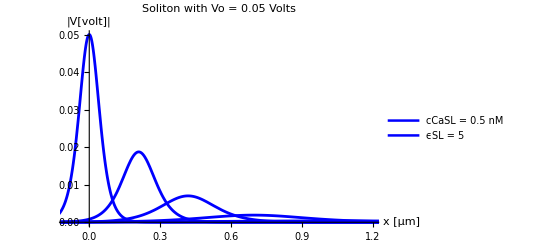

```mathematica
(*Print["Intracellular conditions at 0.05 and 0.15 molar concentration"]*)

solSP2=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.05}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP2Data=Cases[solSP2,Line[{x__}]->x,∞];
```

{{-0.27,0.0000159142},{-0.26952,0.0000161837},{-0.269039,0.0000164576},{-0.268079,0.0000170196},{-0.266158,0.0000182016},{-0.265677,0.0000185098},{-0.265197,0.0000188231},{-0.264237,0.0000194658},{-0.262315,0.0000208177},{-0.261835,0.0000211701},{-0.261355,0.0000215285},{-0.260394,0.0000222636},{-0.258473,0.0000238098},{-0.254631,0.0000272317},{-0.25415,0.0000276926},{-0.25367,0.0000281614},{-0.25271,0.0000291228},{-0.250788,0.0000311453},{-0.250308,0.0000316724},{-0.249828,0.0000322085},{-0.248867,0.0000333081},{-0.246946,0.0000356211},{-0.246466,0.000036224},{-0.245986,0.0000368371},{-0.245025,0.0000380946},{-0.243104,0.0000407398},{-0.239262,0.0000465938},{-0.238741,0.0000474493},{-0.23822,0.0000483204},{-0.237179,0.000050111},{-0.235096,0.0000538936},{-0.234575,0.000054883},{-0.234055,0.0000558906},{-0.233013,0.0000579616},{-0.230931,0.0000623364},{-0.23041,0.0000634807},{-0.229889,0.0000646461},{-0.228848,0.0000670412},{-0.226765,0.0000721009},{-0.2226,0.0000833936},{-0.222079,0.0000849241},{-0.221558,0.0000864828},{-0.220517,0.0000896863},{-0.218434,0.0000964533},{-0.217913,0.0000982233},{-0.217393,0.000100026},{-0.216351,0.00010373},{-0.214269,0.000111556},{-0.213748,0.000113603},{-0.213227,0.000115687},{-0.212186,0.000119971},{-0.210103,0.00012902},{-0.205938,0.000149214},{-0.205451,0.000151768},{-0.204965,0.000154366},{-0.203993,0.000159695},{-0.202048,0.00017091},{-0.201562,0.000173834},{-0.201076,0.000176809},{-0.200103,0.000182911},{-0.198159,0.000195753},{-0.197672,0.000199102},{-0.197186,0.000202508},{-0.196214,0.000209495},{-0.194269,0.0002242},{-0.19038,0.00025677},{-0.189893,0.000261159},{-0.189407,0.000265624},{-0.188435,0.000274783},{-0.18649,0.000294057},{-0.186004,0.000299082},{-0.185518,0.000304193},{-0.184545,0.000314678},{-0.182601,0.00033674},{-0.182115,0.000342493},{-0.181628,0.000348343},{-0.180656,0.000360344},{-0.178711,0.000385596},{-0.174822,0.000441508},{-0.174345,0.000448893},{-0.173869,0.0004564},{-0.172915,0.000471793},{-0.171009,0.000504146},{-0.170532,0.000512573},{-0.170055,0.00052114},{-0.169102,0.000538705},{-0.167196,0.000575619},{-0.166719,0.000585234},{-0.166242,0.000595009},{-0.165289,0.000615047},{-0.163382,0.000657158},{-0.159569,0.000750159},{-0.159093,0.000762667},{-0.158616,0.000775382},{-0.157663,0.000801446},{-0.155756,0.000856208},{-0.155279,0.000870468},{-0.154803,0.000884964},{-0.153849,0.000914677},{-0.151943,0.0009771},{-0.151466,0.000993353},{-0.15099,0.00100987},{-0.150036,0.00104374},{-0.14813,0.00111487},{-0.144317,0.00127181},{-0.143799,0.0012947},{-0.143282,0.001318},{-0.142248,0.00136585},{-0.14018,0.00146675},{-0.139663,0.0014931},{-0.139146,0.00151991},{-0.138112,0.00157497},{-0.136044,0.00169105},{-0.135527,0.00172136},{-0.13501,0.0017522},{-0.133976,0.00181552},{-0.131907,0.00194896},{-0.127771,0.00224529},{-0.127254,0.0022853},{-0.126737,0.002326},{-0.125703,0.00240953},{-0.123635,0.00258546},{-0.123118,0.00263136},{-0.122601,0.00267806},{-0.121567,0.00277386},{-0.119498,0.00297556},{-0.118981,0.00302817},{-0.118464,0.00308167},{-0.11743,0.00319143},{-0.115362,0.00342238},{-0.111226,0.00393348},{-0.110743,0.00399767},{-0.110261,0.00406286},{-0.109295,0.00419629},{-0.107365,0.0044758},{-0.106883,0.00454839},{-0.1064,0.00462211},{-0.105435,0.00477295},{-0.103505,0.00508872},{-0.103022,0.00517069},{-0.10254,0.00525391},{-0.101575,0.00542413},{-0.0996447,0.00578021},{-0.0957844,0.00655876},{-0.0953018,0.00666264},{-0.0948193,0.00676803},{-0.0938542,0.00698345},{-0.0919241,0.00743327},{-0.0880638,0.00841297},{-0.0875812,0.0085433},{-0.0870987,0.00867543},{-0.0861336,0.00894519},{-0.0842034,0.00950721},{-0.0803431,0.0107252},{-0.0798202,0.0109001},{-0.0792972,0.0110776},{-0.0782514,0.0114399},{-0.0761596,0.0121948},{-0.0719761,0.0138297},{-0.0714532,0.0140461},{-0.0709302,0.0142652},{-0.0698843,0.0147116},{-0.0677926,0.0156374},{-0.0636091,0.0176223},{-0.0630861,0.0178829},{-0.0625632,0.0181463},{-0.0615173,0.0186814},{-0.0594256,0.0197844},{-0.055242,0.0221178},{-0.046875,0.0272386},{-0.0463616,0.0275692},{-0.0458482,0.0279014},{-0.0448214,0.02857},{-0.0427678,0.0299225},{-0.0386606,0.0326686},{-0.0381472,0.0330139},{-0.0376338,0.0333593},{-0.036607,0.03405},{-0.0345534,0.0354274},{-0.0304462,0.0381397},{-0.0299328,0.0384721},{-0.0294194,0.0388027},{-0.0283926,0.0394575},{-0.0263389,0.040738},{-0.0258255,0.0410512},{-0.0253121,0.0413614},{-0.0242853,0.0419719},{-0.0222317,0.0431497},{-0.0217183,0.0434342},{-0.0212049,0.0437146},{-0.0201781,0.044262},{-0.0181245,0.0452995},{-0.0176111,0.0455461},{-0.0170977,0.0457874},{-0.0160709,0.0462533},{-0.0140173,0.0471147},{-0.0135384,0.0473014},{-0.0130595,0.0474826},{-0.0121017,0.0478279},{-0.0116228,0.0479919},{-0.0111439,0.0481499},{-0.0101861,0.0484479},{-0.00970723,0.0485877},{-0.00922833,0.0487213},{-0.00827054,0.0489695},{-0.00779164,0.049084},{-0.00731274,0.0491919},{-0.00635495,0.0493881},{-0.00587605,0.0494762},{-0.00539716,0.0495577},{-0.00491826,0.0496323},{-0.00443936,0.0497001},{-0.00396047,0.0497612},{-0.00348157,0.0498153},{-0.00300267,0.0498625},{-0.00252378,0.0499028},{-0.00204488,0.0499362},{-0.00156598,0.0499626},{-0.00108708,0.049982},{-0.000608188,0.0499943},{-0.000129291,0.0499997},{0.000349606,0.0499981},{0.000828503,0.0499895},{0.0013074,0.0499739},{0.0017863,0.0499513},{0.00226519,0.0499217},{0.00274409,0.0498851},{0.00322299,0.0498417},{0.00370188,0.0497912},{0.00418078,0.0497339},{0.00465968,0.0496698},{0.00513857,0.0495988},{0.00561747,0.049521},{0.00609637,0.0494365},{0.00657527,0.0493453},{0.00705416,0.0492475},{0.00753306,0.0491431},{0.00801196,0.0490321},{0.00896975,0.0487908},{0.00944865,0.0486606},{0.00992754,0.0485242},{0.0108853,0.0482328},{0.0113642,0.0480779},{0.0118431,0.0479172},{0.0128009,0.0475781},{0.0132798,0.0473999},{0.0137587,0.0472162},{0.0147165,0.0468323},{0.0166321,0.0460014},{0.0171514,0.0457624},{0.0176707,0.0455178},{0.0187093,0.0450122},{0.0207865,0.0439398},{0.0249408,0.0415837},{0.0254601,0.0412723},{0.0259794,0.0409577},{0.027018,0.0403193},{0.0290952,0.0390104},{0.0332496,0.0362965},{0.0337689,0.0359511},{0.0342882,0.0356047},{0.0353268,0.0349096},{0.0374039,0.0335139},{0.0415583,0.0307267},{0.0498671,0.0253457},{0.0503518,0.0250449},{0.0508366,0.024746},{0.0518062,0.0241536},{0.0537454,0.022992},{0.0576237,0.0207689},{0.0581085,0.0205009},{0.0585933,0.0202352},{0.0595629,0.0197106},{0.061502,0.0186893},{0.0653804,0.0167601},{0.0658652,0.0165298},{0.0663499,0.0163018},{0.0673195,0.0158529},{0.0692587,0.0149839},{0.073137,0.013359},{0.0736218,0.0131663},{0.0741066,0.0129759},{0.0750762,0.012602},{0.0770154,0.011881},{0.0808937,0.0105436},{0.0813689,0.0103889},{0.0818442,0.0102363},{0.0827947,0.00993687},{0.0846957,0.00936098},{0.0884977,0.00829729},{0.088973,0.00817225},{0.0894483,0.00804892},{0.0903988,0.00780729},{0.0922998,0.00734369},{0.0961018,0.00649124},{0.0965771,0.00639136},{0.0970523,0.0062929},{0.0980028,0.0061002},{0.0999038,0.00573117},{0.100379,0.00564222},{0.100854,0.00555458},{0.101805,0.0053831},{0.103706,0.00505496},{0.104181,0.00497593},{0.104656,0.00489806},{0.105607,0.00474577},{0.107508,0.00445456},{0.11131,0.00392237},{0.111826,0.00385506},{0.112341,0.00378885},{0.113373,0.00365969},{0.115435,0.00341395},{0.115951,0.00335504},{0.116466,0.00329711},{0.117498,0.00318414},{0.11956,0.00296931},{0.120076,0.00291784},{0.120592,0.00286723},{0.121623,0.00276855},{0.123686,0.00258099},{0.127811,0.00224225},{0.128327,0.00220308},{0.128842,0.00216458},{0.129873,0.00208955},{0.131936,0.00194705},{0.132452,0.00191294},{0.132967,0.00187941},{0.133999,0.00181408},{0.136061,0.00169003},{0.136577,0.00166035},{0.137093,0.00163117},{0.138124,0.00157433},{0.140187,0.00146643},{0.144312,0.00127202},{0.144793,0.00125107},{0.145274,0.00123046},{0.146236,0.00119024},{0.148161,0.00111366},{0.148642,0.00109529},{0.149123,0.00107722},{0.150086,0.00104196},{0.15201,0.000974827},{0.152491,0.000958724},{0.152972,0.000942885},{0.153935,0.000911979},{0.155859,0.000853148},{0.159708,0.000746542},{0.16019,0.000734182},{0.160671,0.000722025},{0.161633,0.000698307},{0.163558,0.000653168},{0.164039,0.000642344},{0.16452,0.000631698},{0.165482,0.000610929},{0.167407,0.000571406},{0.167888,0.000561929},{0.168369,0.000552608},{0.169331,0.000534426},{0.171256,0.000499826},{0.175105,0.000437174},{0.175627,0.00042931},{0.176148,0.000421586},{0.177191,0.000406551},{0.179278,0.000378066},{0.179799,0.00037126},{0.180321,0.000364577},{0.181364,0.000351569},{0.18345,0.000326922},{0.183972,0.000321035},{0.184493,0.000315253},{0.185536,0.000303999},{0.187622,0.000282678},{0.191795,0.000244407},{0.192316,0.000240002},{0.192838,0.000235676},{0.193881,0.000227256},{0.195967,0.000211306},{0.196489,0.000207496},{0.19701,0.000203755},{0.198053,0.000196473},{0.20014,0.00018268},{0.200661,0.000179385},{0.201183,0.00017615},{0.202226,0.000169853},{0.204312,0.000157926},{0.208484,0.000136521},{0.208996,0.000134103},{0.209508,0.000131727},{0.210532,0.000127101},{0.21258,0.000118329},{0.213092,0.000116233},{0.213604,0.000114173},{0.214628,0.000110163},{0.216676,0.000102559},{0.217188,0.000100742},{0.2177,0.0000989562},{0.218724,0.0000954797},{0.220773,0.0000888886},{0.224869,0.000077039},{0.225381,0.0000756733},{0.225893,0.0000743319},{0.226917,0.0000717199},{0.228965,0.0000667679},{0.229477,0.0000655842},{0.229989,0.0000644216},{0.231013,0.0000621576},{0.233061,0.0000578654},{0.233573,0.0000568395},{0.234085,0.0000558317},{0.235109,0.0000538695},{0.237157,0.0000501494},{0.241253,0.0000434618},{0.24173,0.0000427426},{0.242208,0.0000420353},{0.243163,0.0000406557},{0.245073,0.0000380307},{0.245551,0.0000374014},{0.246028,0.0000367825},{0.246983,0.0000355752},{0.248893,0.0000332781},{0.249371,0.0000327274},{0.249848,0.0000321858},{0.250803,0.0000311293},{0.252713,0.0000291193},{0.256533,0.00002548},{0.257011,0.0000250583},{0.257488,0.0000246436},{0.258443,0.0000238346},{0.260353,0.0000222955},{0.260831,0.0000219265},{0.261308,0.0000215636},{0.262263,0.0000208557},{0.264173,0.0000195089},{0.264651,0.000019186},{0.265128,0.0000188685},{0.266083,0.000018249},{0.267993,0.0000170705},{0.271813,0.0000149369},{0.272331,0.0000146689},{0.272849,0.0000144058},{0.273885,0.0000138935},{0.275957,0.0000129231},{0.276474,0.0000126912},{0.276992,0.0000124635},{0.278028,0.0000120204},{0.2801,0.0000111807},{0.280618,0.0000109801},{0.281136,0.0000107832},{0.282171,0.0000103997},{0.284243,9.67327×10^-6},{0.288386,8.36904×10^-6},{0.288904,8.2189×10^-6},{0.289422,8.07144×10^-6},{0.290458,7.78443×10^-6},{0.292529,7.24065×10^-6},{0.293047,7.11075×10^-6},{0.293565,6.98317×10^-6},{0.294601,6.73485×10^-6},{0.296673,6.26439×10^-6},{0.297191,6.152×10^-6},{0.297709,6.04162×10^-6},{0.298744,5.82678×10^-6},{0.300816,5.41975×10^-6},{0.304959,4.68899×10^-6},{0.305443,4.61042×10^-6},{0.305926,4.53317×10^-6},{0.306893,4.38252×10^-6},{0.308826,4.09609×10^-6},{0.30931,4.02745×10^-6},{0.309793,3.95997×10^-6},{0.31076,3.82837×10^-6},{0.312694,3.57816×10^-6},{0.313177,3.5182×10^-6},{0.31366,3.45925×10^-6},{0.314627,3.34429×10^-6},{0.316561,3.12571×10^-6},{0.320428,2.73048×10^-6},{0.320911,2.68472×10^-6},{0.321395,2.63974×10^-6},{0.322362,2.55201×10^-6},{0.324295,2.38522×10^-6},{0.324779,2.34525×10^-6},{0.325262,2.30595×10^-6},{0.326229,2.22932×10^-6},{0.328162,2.08361×10^-6},{0.328646,2.0487×10^-6},{0.329129,2.01437×10^-6},{0.330096,1.94743×10^-6},{0.33203,1.82014×10^-6},{0.335897,1.58999×10^-6},{0.336421,1.56114×10^-6},{0.336944,1.53281×10^-6},{0.337992,1.4777×10^-6},{0.340087,1.37333×10^-6},{0.340611,1.34842×10^-6},{0.341135,1.32395×10^-6},{0.342182,1.27634×10^-6},{0.344278,1.1862×10^-6},{0.344801,1.16468×10^-6},{0.345325,1.14354×10^-6},{0.346373,1.10242×10^-6},{0.348468,1.02456×10^-6},{0.352658,8.84955×10^-7},{0.353182,8.68898×10^-7},{0.353706,8.53132×10^-7},{0.354754,8.22454×10^-7},{0.356849,7.64368×10^-7},{0.357373,7.50499×10^-7},{0.357896,7.36882×10^-7},{0.358944,7.10384×10^-7},{0.361039,6.60213×10^-7},{0.361563,6.48234×10^-7},{0.362087,6.36472×10^-7},{0.363134,6.13585×10^-7},{0.36523,5.7025×10^-7},{0.36942,4.92546×10^-7},{0.369934,4.8377×10^-7},{0.370448,4.75151×10^-7},{0.371477,4.5837×10^-7},{0.373534,4.26566×10^-7},{0.374048,4.18966×10^-7},{0.374563,4.11501×10^-7},{0.375591,3.96968×10^-7},{0.377648,3.69424×10^-7},{0.378162,3.62842×10^-7},{0.378677,3.56378×10^-7},{0.379705,3.43792×10^-7},{0.381762,3.19937×10^-7},{0.385876,2.7708×10^-7},{0.386391,2.72143×10^-7},{0.386905,2.67294×10^-7},{0.387933,2.57854×10^-7},{0.38999,2.39963×10^-7},{0.390505,2.35687×10^-7},{0.391019,2.31488×10^-7},{0.392047,2.23313×10^-7},{0.394104,2.07818×10^-7},{0.394619,2.04115×10^-7},{0.395133,2.00479×10^-7},{0.396162,1.93398×10^-7},{0.398219,1.79979×10^-7},{0.402333,1.5587×10^-7},{0.402812,1.53277×10^-7},{0.403292,1.50728×10^-7},{0.404252,1.45756×10^-7},{0.406171,1.36299×10^-7},{0.40665,1.34032×10^-7},{0.40713,1.31803×10^-7},{0.40809,1.27455×10^-7},{0.410009,1.19185×10^-7},{0.410489,1.17203×10^-7},{0.410968,1.15254×10^-7},{0.411928,1.11452×10^-7},{0.413847,1.0422×10^-7},{0.417685,9.11345×10^-8},{0.418165,8.96188×10^-8},{0.418644,8.81283×10^-8},{0.419604,8.52213×10^-8},{0.421523,7.96917×10^-8},{0.422003,7.83663×10^-8},{0.422482,7.7063×10^-8},{0.423442,7.45209×10^-8},{0.425361,6.96856×10^-8},{0.425841,6.85267×10^-8},{0.426321,6.7387×10^-8},{0.42728,6.51641×10^-8},{0.429199,6.09359×10^-8},{0.433037,5.32848×10^-8},{0.433557,5.23247×10^-8},{0.434077,5.13818×10^-8},{0.435118,4.95468×10^-8},{0.437198,4.60709×10^-8},{0.437719,4.52408×10^-8},{0.438239,4.44256×10^-8},{0.439279,4.2839×10^-8},{0.44136,3.98337×10^-8},{0.44188,3.91159×10^-8},{0.4424,3.84111×10^-8},{0.44344,3.70393×10^-8},{0.445521,3.44409×10^-8},{0.449682,2.97781×10^-8},{0.450202,2.92415×10^-8},{0.450722,2.87146×10^-8},{0.451763,2.76891×10^-8},{0.453843,2.57466×10^-8},{0.454364,2.52827×10^-8},{0.454884,2.48271×10^-8},{0.455924,2.39405×10^-8},{0.458005,2.2261×10^-8},{0.458525,2.18598×10^-8},{0.459045,2.14659×10^-8},{0.460085,2.06993×10^-8},{0.462166,1.92472×10^-8},{0.466327,1.66414×10^-8},{0.466813,1.63613×10^-8},{0.467298,1.60859×10^-8},{0.46827,1.55488×10^-8},{0.470212,1.4528×10^-8},{0.470698,1.42834×10^-8},{0.471184,1.4043×10^-8},{0.472155,1.35741×10^-8},{0.474098,1.26829×10^-8},{0.474583,1.24694×10^-8},{0.475069,1.22595×10^-8},{0.47604,1.18502×10^-8},{0.477983,1.10722×10^-8},{0.481868,9.66603×10^-9},{0.482354,9.50331×10^-9},{0.482839,9.34333×10^-9},{0.483811,9.0314×10^-9},{0.485753,8.43844×10^-9},{0.486239,8.29639×10^-9},{0.486724,8.15673×10^-9},{0.487696,7.88441×10^-9},{0.489638,7.36676×10^-9},{0.490124,7.24275×10^-9},{0.49061,7.12082×10^-9},{0.491581,6.88309×10^-9},{0.493524,6.43118×10^-9},{0.497409,5.61442×10^-9},{0.497885,5.52175×10^-9},{0.498361,5.4306×10^-9},{0.499313,5.25281×10^-9},{0.501218,4.91448×10^-9},{0.501694,4.83336×10^-9},{0.50217,4.75358×10^-9},{0.503122,4.59795×10^-9},{0.505027,4.3018×10^-9},{0.505503,4.23079×10^-9},{0.505979,4.16096×10^-9},{0.506931,4.02473×10^-9},{0.508836,3.7655×10^-9},{0.512644,3.29606×10^-9},{0.513121,3.24166×10^-9},{0.513597,3.18815×10^-9},{0.514549,3.08377×10^-9},{0.516453,2.88515×10^-9},{0.516929,2.83752×10^-9},{0.517406,2.79069×10^-9},{0.518358,2.69932×10^-9},{0.520262,2.52546×10^-9},{0.520738,2.48377×10^-9},{0.521214,2.44278×10^-9},{0.522167,2.3628×10^-9},{0.524071,2.21062×10^-9},{0.52788,1.93502×10^-9},{0.528397,1.9004×10^-9},{0.528913,1.86639×10^-9},{0.529946,1.80019×10^-9},{0.532012,1.67476×10^-9},{0.532529,1.64479×10^-9},{0.533045,1.61536×10^-9},{0.534078,1.55806×10^-9},{0.536144,1.4495×10^-9},{0.536661,1.42356×10^-9},{0.537177,1.39809×10^-9},{0.53821,1.3485×10^-9},{0.540276,1.25454×10^-9},{0.544408,1.0858×10^-9},{0.544925,1.06637×10^-9},{0.545442,1.04729×10^-9},{0.546475,1.01014×10^-9},{0.548541,9.39756×10^-10},{0.549057,9.22939×10^-10},{0.549574,9.06424×10^-10},{0.550607,8.74275×10^-10},{0.552673,8.13356×10^-10},{0.553189,7.98802×10^-10},{0.553706,7.84508×10^-10},{0.554739,7.56683×10^-10},{0.556805,7.03958×10^-10},{0.560937,6.09274×10^-10},{0.561419,5.99093×10^-10},{0.561901,5.89083×10^-10},{0.562865,5.69562×10^-10},{0.564793,5.32438×10^-10},{0.565275,5.23542×10^-10},{0.565757,5.14794×10^-10},{0.566721,4.97734×10^-10},{0.568649,4.65292×10^-10},{0.569131,4.57518×10^-10},{0.569613,4.49873×10^-10},{0.570577,4.34965×10^-10},{0.572505,4.06614×10^-10},{0.576361,3.55336×10^-10},{0.576843,3.49399×10^-10},{0.577325,3.43561×10^-10},{0.578289,3.32176×10^-10},{0.580217,3.10525×10^-10},{0.580699,3.05336×10^-10},{0.581181,3.00234×10^-10},{0.582145,2.90285×10^-10},{0.584073,2.71364×10^-10},{0.584555,2.6683×10^-10},{0.585037,2.62372×10^-10},{0.586001,2.53677×10^-10},{0.587929,2.37142×10^-10},{0.591785,2.07236×10^-10},{0.592308,2.03486×10^-10},{0.59283,1.99804×10^-10},{0.593875,1.92638×10^-10},{0.595965,1.79067×10^-10},{0.596487,1.75827×10^-10},{0.59701,1.72645×10^-10},{0.598054,1.66453×10^-10},{0.600144,1.54727×10^-10},{0.600666,1.51927×10^-10},{0.601189,1.49178×10^-10},{0.602234,1.43827×10^-10},{0.604323,1.33695×10^-10},{0.608502,1.15522×10^-10},{0.609025,1.13432×10^-10},{0.609547,1.11379×10^-10},{0.610592,1.07384×10^-10},{0.612682,9.98196×10^-11},{0.613204,9.80132×10^-11},{0.613727,9.62395×10^-11},{0.614771,9.27878×10^-11},{0.616861,8.62513×10^-11},{0.617383,8.46904×10^-11},{0.617906,8.31578×10^-11},{0.618951,8.01753×10^-11},{0.62104,7.45273×10^-11},{0.62522,6.4397×10^-11},{0.625732,6.32527×10^-11},{0.626245,6.21288×10^-11},{0.627271,5.99404×10^-11},{0.629322,5.57922×10^-11},{0.629835,5.48009×10^-11},{0.630348,5.38271×10^-11},{0.631374,5.19312×10^-11},{0.633425,4.83373×10^-11},{0.633938,4.74784×10^-11},{0.634451,4.66347×10^-11},{0.635477,4.49921×10^-11},{0.637528,4.18784×10^-11},{0.641631,3.62826×10^-11},{0.642144,3.56379×10^-11},{0.642657,3.50046×10^-11},{0.643683,3.37717×10^-11},{0.645734,3.14345×10^-11},{0.646247,3.0876×10^-11},{0.64676,3.03273×10^-11},{0.647786,2.92591×10^-11},{0.649837,2.72342×10^-11},{0.65035,2.67503×10^-11},{0.650863,2.6275×10^-11},{0.651889,2.53495×10^-11},{0.65394,2.35952×10^-11},{0.658043,2.04424×10^-11},{0.658522,2.01034×10^-11},{0.659,1.977×10^-11},{0.659957,1.91197×10^-11},{0.66187,1.78826×10^-11},{0.662349,1.7586×10^-11},{0.662827,1.72944×10^-11},{0.663784,1.67256×10^-11},{0.665697,1.56434×10^-11},{0.666175,1.53839×10^-11},{0.666654,1.51288×10^-11},{0.667611,1.46312×10^-11},{0.669524,1.36845×10^-11},{0.673351,1.19709×10^-11},{0.673829,1.17724×10^-11},{0.674308,1.15772×10^-11},{0.675264,1.11964×10^-11},{0.677178,1.04719×10^-11},{0.677656,1.02983×10^-11},{0.678135,1.01275×10^-11},{0.679091,9.79438×10^-12},{0.681005,9.16066×10^-12},{0.681483,9.00874×10^-12},{0.681961,8.85934×10^-12},{0.682918,8.56794×10^-12},{0.684832,8.01356×10^-12},{0.688659,7.01011×10^-12},{0.689177,6.88413×10^-12},{0.689696,6.76041×10^-12},{0.690734,6.5196×10^-12},{0.692809,6.06341×10^-12},{0.693327,5.95445×10^-12},{0.693846,5.84743×10^-12},{0.694884,5.63915×10^-12},{0.696959,5.24457×10^-12},{0.697478,5.15031×10^-12},{0.697996,5.05775×10^-12},{0.699034,4.8776×10^-12},{0.701109,4.5363×10^-12},{0.705259,3.92369×10^-12},{0.705778,3.85317×10^-12},{0.706297,3.78392×10^-12},{0.707334,3.64914×10^-12},{0.709409,3.3938×10^-12},{0.709928,3.33281×10^-12},{0.710447,3.27292×10^-12},{0.711484,3.15633×10^-12},{0.713559,2.93548×10^-12},{0.714078,2.88272×10^-12},{0.714597,2.83092×10^-12},{0.715634,2.73008×10^-12},{0.717709,2.53905×10^-12},{0.72186,2.19616×10^-12},{0.722344,2.15929×10^-12},{0.722828,2.12305×10^-12},{0.723797,2.05237×10^-12},{0.725734,1.91799×10^-12},{0.726218,1.8858×10^-12},{0.726702,1.85414×10^-12},{0.727671,1.79242×10^-12},{0.729608,1.67506×10^-12},{0.730092,1.64694×10^-12},{0.730576,1.6193×10^-12},{0.731545,1.56539×10^-12},{0.733482,1.4629×10^-12},{0.737356,1.27761×10^-12},{0.73784,1.25616×10^-12},{0.738324,1.23507×10^-12},{0.739293,1.19396×10^-12},{0.74123,1.11578×10^-12},{0.741714,1.09705×10^-12},{0.742198,1.07864×10^-12},{0.743167,1.04273×10^-12},{0.745104,9.74459×10^-13},{0.745588,9.58101×10^-13},{0.746073,9.42018×10^-13},{0.747041,9.10658×10^-13},{0.748978,8.51034×10^-13},{0.752852,7.43242×10^-13},{0.753327,7.31009×10^-13},{0.753802,7.18978×10^-13},{0.754751,6.95506×10^-13},{0.75665,6.50836×10^-13},{0.757125,6.40124×10^-13},{0.757599,6.29589×10^-13},{0.758549,6.09035×10^-13},{0.760448,5.69919×10^-13},{0.760922,5.60539×10^-13},{0.761397,5.51313×10^-13},{0.762347,5.33315×10^-13},{0.764246,4.99062×10^-13},{0.768043,4.37015×10^-13},{0.768518,4.29822×10^-13},{0.768993,4.22748×10^-13},{0.769942,4.08947×10^-13},{0.771841,3.82682×10^-13},{0.772316,3.76384×10^-13},{0.772791,3.70189×10^-13},{0.77374,3.58104×10^-13},{0.775639,3.35104×10^-13},{0.776114,3.29589×10^-13},{0.776588,3.24164×10^-13},{0.777538,3.13581×10^-13},{0.779437,2.93441×10^-13},{0.783234,2.56958×10^-13},{0.78375,2.52373×10^-13},{0.784265,2.47869×10^-13},{0.785295,2.391×10^-13},{0.787355,2.22483×10^-13},{0.787871,2.18513×10^-13},{0.788386,2.14613×10^-13},{0.789416,2.07021×10^-13},{0.791476,1.92634×10^-13},{0.791991,1.89196×10^-13},{0.792507,1.85819×10^-13},{0.793537,1.79246×10^-13},{0.795597,1.66789×10^-13},{0.799718,1.44412×10^-13},{0.800233,1.41834×10^-13},{0.800749,1.39303×10^-13},{0.801779,1.34375×10^-13},{0.803839,1.25037×10^-13},{0.804354,1.22805×10^-13},{0.80487,1.20613×10^-13},{0.8059,1.16347×10^-13},{0.80796,1.08261×10^-13},{0.808475,1.06329×10^-13},{0.808991,1.04431×10^-13},{0.810021,1.00737×10^-13},{0.812081,9.3736×10^-14},{0.816202,8.11599×10^-14},{0.816683,7.98077×10^-14},{0.817163,7.8478×10^-14},{0.818125,7.58847×10^-14},{0.820047,7.09524×10^-14},{0.820528,6.97702×10^-14},{0.821008,6.86078×10^-14},{0.82197,6.63407×10^-14},{0.823892,6.20287×10^-14},{0.824373,6.09952×10^-14},{0.824853,5.9979×10^-14},{0.825815,5.7997×10^-14},{0.827737,5.42274×10^-14},{0.831582,4.74072×10^-14},{0.832543,4.58406×10^-14},{0.833504,4.43258×10^-14},{0.835427,4.14448×10^-14},{0.836388,4.00753×10^-14},{0.837349,3.8751×10^-14},{0.839272,3.62323×10^-14},{0.840233,3.5035×10^-14},{0.841194,3.38773×10^-14},{0.843117,3.16753×10^-14},{0.846962,2.76915×10^-14},{0.848004,2.6701×10^-14},{0.849046,2.57458×10^-14},{0.85113,2.39368×10^-14},{0.852172,2.30805×10^-14},{0.853214,2.22549×10^-14},{0.855298,2.06912×10^-14},{0.85634,1.9951×10^-14},{0.857382,1.92373×10^-14},{0.859466,1.78856×10^-14},{0.863634,1.54605×10^-14},{0.864676,1.49074×10^-14},{0.865718,1.43742×10^-14},{0.867802,1.33642×10^-14},{0.868844,1.28861×10^-14},{0.869886,1.24251×10^-14},{0.87197,1.15521×10^-14},{0.873012,1.11388×10^-14},{0.874055,1.07404×10^-14},{0.876139,9.98572×10^-15},{0.880307,8.63174×10^-15},{0.882253,8.06405×10^-15},{0.884199,7.5337×10^-15},{0.886145,7.03823×10^-15},{0.888091,6.57534×10^-15},{0.890037,6.14289×10^-15},{0.891983,5.73889×10^-15},{0.895875,5.00885×10^-15},{0.897821,4.67943×10^-15},{0.899767,4.37167×10^-15},{0.901713,4.08416×10^-15},{0.903659,3.81555×10^-15},{0.905605,3.56461×10^-15},{0.907551,3.33018×10^-15},{0.911443,2.90654×10^-15},{0.915259,2.54358×10^-15},{0.919075,2.22594×10^-15},{0.922891,1.94797×10^-15},{0.926707,1.70471×10^-15},{0.930522,1.49182×10^-15},{0.934338,1.30553×10^-15},{0.938154,1.14249×10^-15},{0.94197,9.99821×10^-16},{0.946109,8.65134×10^-16},{0.950248,7.48592×10^-16},{0.950765,7.35174×10^-16},{0.951282,7.21997×10^-16},{0.952317,6.96347×10^-16},{0.954387,6.47748×10^-16},{0.958526,5.6049×10^-16},{0.966804,4.19653×10^-16},{0.975082,3.14205×10^-16},{0.975564,3.08946×10^-16},{0.976047,3.03774×10^-16},{0.977013,2.9369×10^-16},{0.978945,2.74515×10^-16},{0.982808,2.39838×10^-16},{0.990533,1.83072×10^-16},{1.00599,1.06667×10^-16},{1.03947,3.30823×10^-17},{1.07235,1.04816×10^-17},{1.10302,3.58743×10^-18},{1.13628,1.12173×10^-18},{1.16733,3.78894×10^-19},{1.19776,1.30742×10^-19},{1.23079,4.12152×10^-20},{1.2616,1.40355×10^-20},{1.26214,1.37742×10^-20},{1.26268,1.35178×10^-20},{1.26375,1.30193×10^-20},{1.2659,1.20767×10^-20},{1.2702,1.03913×10^-20},{1.2788,7.69322×10^-21},{1.27934,7.55002×10^-21},{1.27988,7.40949×10^-21},{1.28095,7.13622×10^-21},{1.2831,6.61955×10^-21},{1.2874,5.69572×10^-21},{1.28794,5.5897×10^-21},{1.28848,5.48566×10^-21},{1.28955,5.28334×10^-21},{1.2917,4.90082×10^-21},{1.29224,4.8096×10^-21},{1.29278,4.72007×10^-21},{1.29385,4.54599×10^-21},{1.29439,4.46138×10^-21},{1.29493,4.37833×10^-21},{1.29546,4.29684×10^-21},{1.296,4.21686×10^-21},{-0.27,2.61584×10^-6},{-0.26952,2.64287×10^-6},{-0.269039,2.67017×10^-6},{-0.268079,2.72563×10^-6},{-0.266158,2.84002×10^-6},{-0.262315,3.0834×10^-6},{-0.261835,3.11526×10^-6},{-0.261355,3.14744×10^-6},{-0.260394,3.21281×10^-6},{-0.258473,3.34764×10^-6},{-0.254631,3.63453×10^-6},{-0.25415,3.67207×10^-6},{-0.25367,3.71001×10^-6},{-0.25271,3.78706×10^-6},{-0.250788,3.94599×10^-6},{-0.246946,4.28414×10^-6},{-0.239262,5.04986×10^-6},{-0.238741,5.10644×10^-6},{-0.23822,5.16365×10^-6},{-0.237179,5.28001×10^-6},{-0.235096,5.52064×10^-6},{-0.230931,6.03531×10^-6},{-0.23041,6.10293×10^-6},{-0.229889,6.1713×10^-6},{-0.228848,6.31036×10^-6},{-0.226765,6.59794×10^-6},{-0.2226,7.21302×10^-6},{-0.222079,7.29383×10^-6},{-0.221558,7.37555×10^-6},{-0.220517,7.54174×10^-6},{-0.218434,7.88543×10^-6},{-0.214269,8.62051×10^-6},{-0.213748,8.71708×10^-6},{-0.213227,8.81474×10^-6},{-0.212186,9.01335×10^-6},{-0.210103,9.42409×10^-6},{-0.205938,0.0000103026},{-0.205451,0.0000104103},{-0.204965,0.0000105191},{-0.203993,0.0000107403},{-0.202048,0.0000111966},{-0.198159,0.0000121681},{-0.197672,0.0000122954},{-0.197186,0.0000124239},{-0.196214,0.0000126851},{-0.194269,0.000013224},{-0.19038,0.0000143714},{-0.189893,0.0000145216},{-0.189407,0.0000146735},{-0.188435,0.0000149819},{-0.18649,0.0000156183},{-0.182601,0.0000169734},{-0.174822,0.0000200463},{-0.174345,0.0000202517},{-0.173869,0.0000204592},{-0.172915,0.0000208807},{-0.171009,0.0000217498},{-0.167196,0.000023598},{-0.166719,0.0000238398},{-0.166242,0.000024084},{-0.165289,0.0000245801},{-0.163382,0.0000256031},{-0.159569,0.0000277785},{-0.159093,0.0000280631},{-0.158616,0.0000283506},{-0.157663,0.0000289345},{-0.155756,0.0000301385},{-0.151943,0.0000326989},{-0.144317,0.00003849},{-0.143799,0.0000389179},{-0.143282,0.0000393504},{-0.142248,0.00004023},{-0.14018,0.0000420486},{-0.136044,0.0000459358},{-0.135527,0.0000464463},{-0.13501,0.0000469625},{-0.133976,0.000048012},{-0.131907,0.0000501819},{-0.127771,0.0000548199},{-0.127254,0.000055429},{-0.126737,0.0000560448},{-0.125703,0.000057297},{-0.123635,0.0000598859},{-0.119498,0.0000654192},{-0.118981,0.0000661458},{-0.118464,0.0000668805},{-0.11743,0.0000683744},{-0.115362,0.0000714628},{-0.111226,0.0000780636},{-0.110743,0.0000788722},{-0.110261,0.0000796892},{-0.109295,0.0000813486},{-0.107365,0.0000847715},{-0.103505,0.0000920544},{-0.103022,0.0000930075},{-0.10254,0.0000939706},{-0.101575,0.0000959266},{-0.0996447,0.0000999613},{-0.0957844,0.000108545},{-0.0953018,0.000109669},{-0.0948193,0.000110804},{-0.0938542,0.000113109},{-0.0919241,0.000117864},{-0.0880638,0.00012798},{-0.0803431,0.000150881},{-0.0798202,0.000152572},{-0.0792972,0.000154282},{-0.0782514,0.00015776},{-0.0761596,0.000164951},{-0.0719761,0.000180326},{-0.0714532,0.000182346},{-0.0709302,0.000184388},{-0.0698843,0.00018854},{-0.0677926,0.000197127},{-0.0636091,0.000215484},{-0.0630861,0.000217895},{-0.0625632,0.000220332},{-0.0615173,0.00022529},{-0.0594256,0.000235539},{-0.055242,0.000257448},{-0.0547191,0.000260325},{-0.0541962,0.000263234},{-0.0531503,0.00026915},{-0.0510585,0.00028138},{-0.046875,0.000307517},{-0.0463616,0.000310886},{-0.0458482,0.000314292},{-0.0448214,0.000321215},{-0.0427678,0.000335517},{-0.0386606,0.000366041},{-0.0381472,0.000370045},{-0.0376338,0.000374092},{-0.036607,0.000382319},{-0.0345534,0.000399312},{-0.0304462,0.000435572},{-0.0299328,0.000440327},{-0.0294194,0.000445133},{-0.0283926,0.000454903},{-0.0263389,0.000475081},{-0.0222317,0.000518123},{-0.0140173,0.000616055},{-0.0135384,0.000622295},{-0.0130595,0.000628597},{-0.0121017,0.00064139},{-0.0101861,0.000667749},{-0.00635495,0.000723693},{-0.00587605,0.000731002},{-0.00539716,0.000738382},{-0.00443936,0.000753363},{-0.00252378,0.000784223},{0.0013074,0.000849697},{0.0017863,0.000858247},{0.00226519,0.000866881},{0.00322299,0.000884405},{0.00513857,0.000920495},{0.00896975,0.000997029},{0.0166321,0.00116907},{0.0171514,0.00118172},{0.0176707,0.00119449},{0.0187093,0.00122045},{0.0207865,0.00127401},{0.0249408,0.001388},{0.0254601,0.00140292},{0.0259794,0.001418},{0.027018,0.00144861},{0.0290952,0.00151175},{0.0332496,0.001646},{0.0337689,0.00166356},{0.0342882,0.0016813},{0.0353268,0.00171732},{0.0374039,0.00179156},{0.0415583,0.00194925},{0.0498671,0.00230455},{0.0503518,0.00232705},{0.0508366,0.00234974},{0.0518062,0.00239575},{0.0537454,0.00249029},{0.0576237,0.00268976},{0.0581085,0.0027157},{0.0585933,0.00274187},{0.0595629,0.0027949},{0.061502,0.00290378},{0.0653804,0.00313315},{0.0658652,0.00316294},{0.0663499,0.00319298},{0.0673195,0.00325384},{0.0692587,0.00337869},{0.073137,0.00364121},{0.0808937,0.00422032},{0.0813689,0.00425825},{0.0818442,0.00429647},{0.0827947,0.00437378},{0.0846957,0.00453194},{0.0884977,0.00486268},{0.0961018,0.00558356},{0.0965771,0.00563131},{0.0970523,0.00567937},{0.0980028,0.00577646},{0.0999038,0.00597449},{0.103706,0.00638604},{0.11131,0.00727094},{0.111826,0.00733389},{0.112341,0.00739722},{0.113373,0.00752497},{0.115435,0.00778482},{0.11956,0.00832155},{0.127811,0.00945821},{0.144312,0.0119213},{0.144793,0.0119954},{0.145274,0.0120695},{0.146236,0.0122179},{0.148161,0.0125149},{0.15201,0.0131083},{0.159708,0.0142773},{0.16019,0.0143489},{0.160671,0.0144203},{0.161633,0.0145624},{0.163558,0.0148434},{0.167407,0.0153906},{0.175105,0.0164069},{0.175627,0.0164711},{0.176148,0.0165348},{0.177191,0.01666},{0.179278,0.0169021},{0.179799,0.0169608},{0.180321,0.0170187},{0.181364,0.0171323},{0.18345,0.0173498},{0.183972,0.0174021},{0.184493,0.0174536},{0.185536,0.0175539},{0.187622,0.0177438},{0.188144,0.0177889},{0.188665,0.0178332},{0.189709,0.0179188},{0.191795,0.0180783},{0.192316,0.0181157},{0.192838,0.0181521},{0.193881,0.0182217},{0.194402,0.018255},{0.194924,0.0182872},{0.195967,0.0183485},{0.196489,0.0183775},{0.19701,0.0184055},{0.198053,0.0184581},{0.198575,0.0184828},{0.199096,0.0185063},{0.20014,0.0185502},{0.200661,0.0185704},{0.201183,0.0185895},{0.201704,0.0186075},{0.202226,0.0186243},{0.202747,0.01864},{0.203269,0.0186545},{0.20379,0.018668},{0.204312,0.0186802},{0.204833,0.0186913},{0.205355,0.0187013},{0.205877,0.0187101},{0.206398,0.0187177},{0.20692,0.0187242},{0.207441,0.0187295},{0.207963,0.0187336},{0.208484,0.0187366},{0.208996,0.0187384},{0.209508,0.018739},{0.21002,0.0187386},{0.210532,0.018737},{0.211044,0.0187343},{0.211556,0.0187304},{0.212068,0.0187255},{0.21258,0.0187194},{0.213092,0.0187122},{0.213604,0.0187039},{0.214116,0.0186944},{0.214628,0.0186839},{0.21514,0.0186722},{0.215652,0.0186595},{0.216676,0.0186306},{0.217188,0.0186145},{0.2177,0.0185974},{0.218724,0.0185597},{0.219237,0.0185393},{0.219749,0.0185178},{0.220773,0.0184716},{0.221285,0.0184469},{0.221797,0.0184211},{0.222821,0.0183664},{0.224869,0.0182447},{0.225381,0.0182117},{0.225893,0.0181777},{0.226917,0.0181068},{0.228965,0.0179533},{0.229477,0.0179125},{0.229989,0.0178709},{0.231013,0.0177847},{0.233061,0.0176017},{0.233573,0.0175537},{0.234085,0.0175049},{0.235109,0.0174048},{0.237157,0.0171948},{0.241253,0.0167382},{0.24173,0.016682},{0.242208,0.0166252},{0.243163,0.01651},{0.245073,0.0162729},{0.248893,0.0157747},{0.256533,0.0147004},{0.271813,0.0123811},{0.272331,0.0123012},{0.272849,0.0122213},{0.273885,0.0120616},{0.275957,0.0117429},{0.2801,0.0111102},{0.288386,0.00987712},{0.288904,0.00980196},{0.289422,0.00972706},{0.290458,0.00957807},{0.292529,0.0092834},{0.296673,0.0087084},{0.304959,0.00762203},{0.305443,0.00756145},{0.305926,0.0075012},{0.306893,0.00738165},{0.308826,0.00714644},{0.312694,0.00669178},{0.320428,0.00584637},{0.320911,0.00579636},{0.321395,0.00574669},{0.322362,0.00564835},{0.324295,0.00545564},{0.328162,0.00508595},{0.335897,0.00440799},{0.336421,0.00436496},{0.336944,0.00432228},{0.337992,0.00423799},{0.340087,0.00407362},{0.344278,0.00376133},{0.344801,0.0037238},{0.345325,0.0036866},{0.346373,0.00361317},{0.348468,0.00347017},{0.352658,0.00319917},{0.353182,0.00316666},{0.353706,0.00313445},{0.354754,0.00307091},{0.356849,0.0029473},{0.361039,0.00271355},{0.36942,0.00229628},{0.369934,0.00227272},{0.370448,0.00224938},{0.371477,0.00220338},{0.373534,0.002114},{0.377648,0.00194535},{0.378162,0.00192518},{0.378677,0.0019052},{0.379705,0.00186585},{0.381762,0.00178942},{0.385876,0.00164539},{0.386391,0.00162818},{0.386905,0.00161114},{0.387933,0.00157757},{0.38999,0.00151243},{0.394104,0.00138978},{0.402333,0.00117253},{0.402812,0.00116093},{0.403292,0.00114944},{0.404252,0.00112679},{0.406171,0.00108279},{0.410009,0.000999711},{0.410489,0.000989773},{0.410968,0.00097993},{0.411928,0.00096053},{0.413847,0.000922845},{0.417685,0.000851747},{0.418165,0.000843245},{0.418644,0.000834825},{0.419604,0.000818232},{0.421523,0.000786006},{0.425361,0.000725237},{0.433037,0.000617194},{0.433557,0.000610474},{0.434077,0.000603825},{0.435118,0.000590742},{0.437198,0.000565405},{0.44136,0.0005179},{0.44188,0.000512246},{0.4424,0.000506653},{0.44344,0.000495646},{0.445521,0.000474335},{0.449682,0.00043439},{0.450202,0.000429637},{0.450722,0.000424935},{0.451763,0.000415683},{0.453843,0.000397773},{0.458005,0.000364212},{0.466327,0.000305277},{0.466813,0.000302146},{0.467298,0.000299047},{0.46827,0.000292943},{0.470212,0.000281104},{0.474098,0.000258831},{0.474583,0.000256173},{0.475069,0.000253543},{0.47604,0.000248361},{0.477983,0.000238312},{0.481868,0.00021941},{0.482354,0.000217155},{0.482839,0.000214922},{0.483811,0.000210526},{0.485753,0.000201999},{0.489638,0.000185963},{0.497409,0.000157592},{0.497885,0.000156002},{0.498361,0.000154427},{0.499313,0.000151324},{0.501218,0.000145304},{0.505027,0.00013397},{0.505503,0.000132617},{0.505979,0.000131277},{0.506931,0.000128638},{0.508836,0.000123517},{0.512644,0.000113878},{0.513121,0.000112727},{0.513597,0.000111587},{0.514549,0.000109343},{0.516453,0.000104988},{0.520262,0.0000967909},{0.52788,0.0000822622},{0.528397,0.0000813598},{0.528913,0.0000804673},{0.529946,0.0000787116},{0.532012,0.000075314},{0.536144,0.0000689515},{0.536661,0.0000681949},{0.537177,0.0000674466},{0.53821,0.0000659745},{0.540276,0.0000631257},{0.544408,0.0000577913},{0.544925,0.000057157},{0.545442,0.0000565296},{0.546475,0.0000552954},{0.548541,0.0000529071},{0.552673,0.0000484351},{0.553189,0.0000479034},{0.553706,0.0000473774},{0.554739,0.0000463428},{0.556805,0.0000443407},{0.560937,0.000040592},{0.561419,0.0000401759},{0.561901,0.000039764},{0.562865,0.0000389529},{0.564793,0.0000373799},{0.568649,0.0000344217},{0.569131,0.0000340688},{0.569613,0.0000337195},{0.570577,0.0000330315},{0.572505,0.0000316975},{0.576361,0.0000291886},{0.576843,0.0000288893},{0.577325,0.0000285931},{0.578289,0.0000280096},{0.580217,0.0000268782},{0.584073,0.0000247506},{0.591785,0.000020987},{0.592308,0.0000207538},{0.59283,0.0000205231},{0.593875,0.0000200696},{0.595965,0.0000191923},{0.600144,0.000017551},{0.600666,0.000017356},{0.601189,0.0000171631},{0.602234,0.0000167837},{0.604323,0.00001605},{0.608502,0.0000146774},{0.609025,0.0000145142},{0.609547,0.0000143529},{0.610592,0.0000140357},{0.612682,0.000013422},{0.616861,0.0000122741},{0.617383,0.0000121376},{0.617906,0.0000120027},{0.618951,0.0000117374},{0.62104,0.0000112242},{0.62522,0.0000102642},{0.625732,0.0000101522},{0.626245,0.0000100414},{0.627271,9.8234×10^-6},{0.629322,9.40155×10^-6},{0.633425,8.6114×10^-6},{0.633938,8.51742×10^-6},{0.634451,8.42447×10^-6},{0.635477,8.24159×10^-6},{0.637528,7.88765×10^-6},{0.641631,7.22472×10^-6},{0.642144,7.14587×10^-6},{0.642657,7.06788×10^-6},{0.643683,6.91444×10^-6},{0.645734,6.61749×10^-6},{0.649837,6.06129×10^-6},{0.65035,5.99514×10^-6},{0.650863,5.9297×10^-6},{0.651889,5.80097×10^-6},{0.65394,5.55183×10^-6},{0.658043,5.08519×10^-6},{0.658522,5.0334×10^-6},{0.659,4.98214×10^-6},{0.659957,4.88118×10^-6},{0.66187,4.68536×10^-6},{0.665697,4.31696×10^-6},{0.666175,4.273×10^-6},{0.666654,4.22948×10^-6},{0.667611,4.14377×10^-6},{0.669524,3.97753×10^-6},{0.673351,3.66478×10^-6},{0.673829,3.62746×10^-6},{0.674308,3.59051×10^-6},{0.675264,3.51775×10^-6},{0.677178,3.37662×10^-6},{0.681005,3.11112×10^-6},{0.688659,2.64109×10^-6},{0.689177,2.61194×10^-6},{0.689696,2.5831×10^-6},{0.690734,2.52638×10^-6},{0.692809,2.41665×10^-6},{0.696959,2.21128×10^-6},{0.697478,2.18686×10^-6},{0.697996,2.16272×10^-6},{0.699034,2.11523×10^-6},{0.701109,2.02336×10^-6},{0.705259,1.85141×10^-6},{0.705778,1.83097×10^-6},{0.706297,1.81075×10^-6},{0.707334,1.77099×10^-6},{0.709409,1.69407×10^-6},{0.713559,1.5501×10^-6},{0.714078,1.53299×10^-6},{0.714597,1.51606×10^-6},{0.715634,1.48277×10^-6},{0.717709,1.41837×10^-6},{0.72186,1.29783×10^-6},{0.722344,1.28445×10^-6},{0.722828,1.2712×10^-6},{0.723797,1.24513×10^-6},{0.725734,1.19457×10^-6},{0.729608,1.09952×10^-6},{0.730092,1.08819×10^-6},{0.730576,1.07697×10^-6},{0.731545,1.05488×10^-6},{0.733482,1.01204×10^-6},{0.737356,9.3152×10^-7},{0.73784,9.21916×10^-7},{0.738324,9.12411×10^-7},{0.739293,8.93694×10^-7},{0.74123,8.57404×10^-7},{0.745104,7.89186×10^-7},{0.752852,6.686×10^-7},{0.753327,6.61841×10^-7},{0.753802,6.55152×10^-7},{0.754751,6.41974×10^-7},{0.75665,6.16408×10^-7},{0.760448,5.68291×10^-7},{0.760922,5.62547×10^-7},{0.761397,5.56861×10^-7},{0.762347,5.4566×10^-7},{0.764246,5.2393×10^-7},{0.768043,4.83032×10^-7},{0.768518,4.78149×10^-7},{0.768993,4.73316×10^-7},{0.769942,4.63796×10^-7},{0.771841,4.45326×10^-7},{0.775639,4.10564×10^-7},{0.783234,3.48968×10^-7},{0.78375,3.45142×10^-7},{0.784265,3.41358×10^-7},{0.785295,3.33914×10^-7},{0.787355,3.19509×10^-7},{0.791476,2.92538×10^-7},{0.791991,2.8933×10^-7},{0.792507,2.86158×10^-7},{0.793537,2.79918×10^-7},{0.795597,2.67843×10^-7},{0.799718,2.45233×10^-7},{0.800233,2.42544×10^-7},{0.800749,2.39885×10^-7},{0.801779,2.34654×10^-7},{0.803839,2.24531×10^-7},{0.80796,2.05577×10^-7},{0.808475,2.03323×10^-7},{0.808991,2.01094×10^-7},{0.810021,1.96709×10^-7},{0.812081,1.88223×10^-7},{0.816202,1.72334×10^-7},{0.816683,1.70571×10^-7},{0.817163,1.68825×10^-7},{0.818125,1.65388×10^-7},{0.820047,1.58721×10^-7},{0.823892,1.46184×10^-7},{0.824373,1.44688×10^-7},{0.824853,1.43207×10^-7},{0.825815,1.40291×10^-7},{0.827737,1.34636×10^-7},{0.831582,1.24001×10^-7},{0.832063,1.22732×10^-7},{0.832543,1.21476×10^-7},{0.833504,1.19003×10^-7},{0.835427,1.14206×10^-7},{0.839272,1.05185×10^-7},{0.846962,8.92239×10^-8},{0.847483,8.82345×10^-8},{0.848004,8.72562×10^-8},{0.849046,8.53318×10^-8},{0.85113,8.16095×10^-8},{0.855298,7.4645×10^-8},{0.855819,7.38173×10^-8},{0.85634,7.29988×10^-8},{0.857382,7.13889×10^-8},{0.859466,6.82748×10^-8},{0.863634,6.24483×10^-8},{0.864155,6.17558×10^-8},{0.864676,6.1071×10^-8},{0.865718,5.97242×10^-8},{0.867802,5.71189×10^-8},{0.87197,5.22444×10^-8},{0.872491,5.16651×10^-8},{0.873012,5.10922×10^-8},{0.874055,4.99655×10^-8},{0.876139,4.77859×10^-8},{0.880307,4.37079×10^-8},{0.880793,4.32551×10^-8},{0.88128,4.28071×10^-8},{0.882253,4.19249×10^-8},{0.884199,4.02147×10^-8},{0.888091,3.70007×10^-8},{0.888577,3.66175×10^-8},{0.889064,3.62382×10^-8},{0.890037,3.54914×10^-8},{0.891983,3.40436×10^-8},{0.895875,3.13228×10^-8},{0.896362,3.09984×10^-8},{0.896848,3.06773×10^-8},{0.897821,3.00451×10^-8},{0.899767,2.88195×10^-8},{0.903659,2.65162×10^-8},{0.911443,2.24472×10^-8},{0.91192,2.22193×10^-8},{0.912397,2.19936×10^-8},{0.913351,2.15491×10^-8},{0.915259,2.0687×10^-8},{0.919075,1.90648×10^-8},{0.919552,1.88712×10^-8},{0.920029,1.86795×10^-8},{0.920983,1.8302×10^-8},{0.922891,1.75698×10^-8},{0.926707,1.6192×10^-8},{0.927184,1.60276×10^-8},{0.927661,1.58648×10^-8},{0.928614,1.55442×10^-8},{0.930522,1.49223×10^-8},{0.934338,1.37521×10^-8},{0.94197,1.16799×10^-8},{0.942487,1.15513×10^-8},{0.943004,1.14241×10^-8},{0.944039,1.11739×10^-8},{0.946109,1.06898×10^-8},{0.950248,9.78363×10^-9},{0.950765,9.6759×10^-9},{0.951282,9.56936×10^-9},{0.952317,9.35978×10^-9},{0.954387,8.95428×10^-9},{0.958526,8.19523×10^-9},{0.959043,8.10499×10^-9},{0.95956,8.01575×10^-9},{0.960595,7.84019×10^-9},{0.962665,7.50053×10^-9},{0.966804,6.86472×10^-9},{0.967321,6.78913×10^-9},{0.967838,6.71437×10^-9},{0.968873,6.56732×10^-9},{0.970943,6.2828×10^-9},{0.975082,5.75021×10^-9},{0.975564,5.69109×10^-9},{0.976047,5.63259×10^-9},{0.977013,5.51737×10^-9},{0.978945,5.29395×10^-9},{0.982808,4.8739×10^-9},{0.98329,4.82379×10^-9},{0.983773,4.7742×10^-9},{0.984739,4.67654×10^-9},{0.98667,4.48717×10^-9},{0.990533,4.13113×10^-9},{0.991016,4.08866×10^-9},{0.991499,4.04662×10^-9},{0.992465,3.96385×10^-9},{0.994396,3.80334×10^-9},{0.998259,3.50156×10^-9},{1.00599,2.96793×10^-9},{1.00651,2.93488×10^-9},{1.00703,2.9022×10^-9},{1.00808,2.83792×10^-9},{1.01017,2.7136×10^-9},{1.01436,2.48107×10^-9},{1.01488,2.45344×10^-9},{1.0154,2.42612×10^-9},{1.01645,2.37238×10^-9},{1.01854,2.26846×10^-9},{1.02273,2.07407×10^-9},{1.02325,2.05097×10^-9},{1.02378,2.02813×10^-9},{1.02482,1.98321×10^-9},{1.02692,1.89634×10^-9},{1.0311,1.73383×10^-9},{1.03163,1.71453×10^-9},{1.03215,1.69543×10^-9},{1.0332,1.65788×10^-9},{1.03529,1.58526×10^-9},{1.03947,1.44941×10^-9},{1.03999,1.43357×10^-9},{1.0405,1.41789×10^-9},{1.04153,1.38705×10^-9},{1.04358,1.32738×10^-9},{1.04769,1.21561×10^-9},{1.04821,1.20232×10^-9},{1.04872,1.18917×10^-9},{1.04975,1.16331×10^-9},{1.0518,1.11326×10^-9},{1.05591,1.01953×10^-9},{1.05643,1.00838×10^-9},{1.05694,9.97352×10^-10},{1.05797,9.75661×10^-10},{1.06002,9.33684×10^-10},{1.06413,8.55069×10^-10},{1.06465,8.4572×10^-10},{1.06516,8.36472×10^-10},{1.06619,8.1828×10^-10},{1.06824,7.83074×10^-10},{1.07235,7.1714×10^-10},{1.07283,7.09823×10^-10},{1.07331,7.0258×10^-10},{1.07427,6.88316×10^-10},{1.07619,6.6065×10^-10},{1.08002,6.08609×10^-10},{1.0805,6.02399×10^-10},{1.08098,5.96252×10^-10},{1.08194,5.84147×10^-10},{1.08385,5.60668×10^-10},{1.08769,5.16503×10^-10},{1.08817,5.11232×10^-10},{1.08865,5.06016×10^-10},{1.08961,4.95742×10^-10},{1.09152,4.75817×10^-10},{1.09536,4.38336×10^-10},{1.10302,3.71998×10^-10},{1.10354,3.67884×10^-10},{1.10406,3.63816×10^-10},{1.1051,3.55814×10^-10},{1.10718,3.40333×10^-10},{1.11134,3.11363×10^-10},{1.11186,3.0792×10^-10},{1.11238,3.04515×10^-10},{1.11342,2.97817×10^-10},{1.11549,2.84859×10^-10},{1.11965,2.60612×10^-10},{1.12017,2.57729×10^-10},{1.12069,2.54879×10^-10},{1.12173,2.49273×10^-10},{1.12381,2.38428×10^-10},{1.12797,2.18132×10^-10},{1.12849,2.1572×10^-10},{1.129,2.13334×10^-10},{1.13004,2.08642×10^-10},{1.13212,1.99564×10^-10},{1.13628,1.82577×10^-10},{1.13676,1.80691×10^-10},{1.13725,1.78825×10^-10},{1.13822,1.7515×10^-10},{1.14016,1.68026×10^-10},{1.14404,1.54634×10^-10},{1.14453,1.53037×10^-10},{1.14501,1.51456×10^-10},{1.14598,1.48344×10^-10},{1.14792,1.42309×10^-10},{1.1518,1.30967×10^-10},{1.15229,1.29614×10^-10},{1.15277,1.28276×10^-10},{1.15374,1.2564×10^-10},{1.15568,1.20529×10^-10},{1.15957,1.10922×10^-10},{1.16733,9.39458×10^-11},{1.1678,9.29944×10^-11},{1.16828,9.20527×10^-11},{1.16923,9.01978×10^-11},{1.17113,8.65994×10^-11},{1.17494,7.98276×10^-11},{1.17541,7.90192×10^-11},{1.17589,7.82191×10^-11},{1.17684,7.66429×10^-11},{1.17874,7.35853×10^-11},{1.18255,6.78311×10^-11},{1.18302,6.71442×10^-11},{1.1835,6.64643×10^-11},{1.18445,6.5125×10^-11},{1.18635,6.25269×10^-11},{1.19016,5.76375×10^-11},{1.19776,4.89757×10^-11},{1.19828,4.84379×10^-11},{1.1988,4.79059×10^-11},{1.19983,4.68595×10^-11},{1.20189,4.48348×10^-11},{1.20602,4.10439×10^-11},{1.20654,4.05932×10^-11},{1.20705,4.01474×10^-11},{1.20808,3.92705×10^-11},{1.21015,3.75736×10^-11},{1.21428,3.43967×10^-11},{1.21479,3.4019×10^-11},{1.21531,3.36454×10^-11},{1.21634,3.29105×10^-11},{1.2184,3.14884×10^-11},{1.22253,2.88261×10^-11},{1.22305,2.85095×10^-11},{1.22356,2.81964×10^-11},{1.2246,2.75805×10^-11},{1.22666,2.63888×10^-11},{1.23079,2.41576×10^-11},{1.23127,2.39099×10^-11},{1.23175,2.36648×10^-11},{1.23271,2.31821×10^-11},{1.23464,2.22461×10^-11},{1.23849,2.04858×10^-11},{1.23897,2.02758×10^-11},{1.23945,2.00679×10^-11},{1.24042,1.96586×10^-11},{1.24234,1.88648×10^-11},{1.24619,1.73721×10^-11},{1.24668,1.7194×10^-11},{1.24716,1.70177×10^-11},{1.24812,1.66706×10^-11},{1.25005,1.59975×10^-11},{1.2539,1.47317×10^-11},{1.2616,1.24925×10^-11},{1.26214,1.23497×10^-11},{1.26268,1.22084×10^-11},{1.26375,1.19308×10^-11},{1.2659,1.13943×10^-11},{1.2702,1.03926×10^-11},{1.27074,1.02737×10^-11},{1.27128,1.01562×10^-11},{1.27235,9.92524×10^-12},{1.2745,9.47893×10^-12},{1.2788,8.6456×10^-12},{1.27934,8.54673×10^-12},{1.27988,8.44898×10^-12},{1.28095,8.25683×10^-12},{1.2831,7.88554×10^-12},{1.2874,7.1923×10^-12},{1.28794,7.11004×10^-12},{1.28848,7.02873×10^-12},{1.28955,6.86887×10^-12},{1.2917,6.56×10^-12},{1.29224,6.48497×10^-12},{1.29278,6.41081×10^-12},{1.29385,6.26501×10^-12},{1.29439,6.19336×10^-12},{1.29493,6.12253×10^-12},{1.29546,6.05251×10^-12},{1.296,5.98329×10^-12},{-0.27,3.38829×10^-6},{-0.26952,3.40968×10^-6},{-0.269039,3.4312×10^-6},{-0.268079,3.47465×10^-6},{-0.266158,3.5632×10^-6},{-0.262315,3.74714×10^-6},{-0.254631,4.14397×10^-6},{-0.25415,4.17013×10^-6},{-0.25367,4.19644×10^-6},{-0.25271,4.24958×10^-6},{-0.250788,4.35788×10^-6},{-0.246946,4.58282×10^-6},{-0.239262,5.06813×10^-6},{-0.238741,5.10281×10^-6},{-0.23822,5.13773×10^-6},{-0.237179,5.20829×10^-6},{-0.235096,5.35233×10^-6},{-0.230931,5.65246×10^-6},{-0.2226,6.30413×10^-6},{-0.222079,6.34727×10^-6},{-0.221558,6.3907×10^-6},{-0.220517,6.47846×10^-6},{-0.218434,6.65761×10^-6},{-0.214269,7.03089×10^-6},{-0.205938,7.8414×10^-6},{-0.205451,7.89148×10^-6},{-0.204965,7.94188×10^-6},{-0.203993,8.04366×10^-6},{-0.202048,8.25114×10^-6},{-0.198159,8.68228×10^-6},{-0.19038,9.61327×10^-6},{-0.189893,9.67466×10^-6},{-0.189407,9.73645×10^-6},{-0.188435,9.86121×10^-6},{-0.18649,0.0000101155},{-0.182601,0.000010644},{-0.174822,0.0000117852},{-0.174345,0.000011859},{-0.173869,0.0000119332},{-0.172915,0.0000120831},{-0.171009,0.0000123884},{-0.167196,0.0000130226},{-0.159569,0.0000143897},{-0.159093,0.0000144798},{-0.158616,0.0000145704},{-0.157663,0.0000147533},{-0.155756,0.0000151261},{-0.151943,0.0000159002},{-0.144317,0.0000175691},{-0.143799,0.0000176884},{-0.143282,0.0000178085},{-0.142248,0.0000180511},{-0.14018,0.0000185463},{-0.136044,0.0000195778},{-0.127771,0.0000218158},{-0.127254,0.0000219638},{-0.126737,0.0000221129},{-0.125703,0.0000224141},{-0.123635,0.0000230288},{-0.119498,0.0000243091},{-0.111226,0.0000270869},{-0.110743,0.0000272584},{-0.110261,0.0000274309},{-0.109295,0.0000277793},{-0.107365,0.0000284894},{-0.103505,0.0000299643},{-0.0957844,0.0000331467},{-0.0953018,0.0000333565},{-0.0948193,0.0000335675},{-0.0938542,0.0000339937},{-0.0919241,0.0000348622},{-0.0880638,0.0000366662},{-0.0803431,0.0000405583},{-0.0798202,0.0000408364},{-0.0792972,0.0000411163},{-0.0782514,0.000041682},{-0.0761596,0.0000428366},{-0.0719761,0.0000452426},{-0.0636091,0.0000504659},{-0.0630861,0.0000508116},{-0.0625632,0.0000511597},{-0.0615173,0.000051863},{-0.0594256,0.0000532986},{-0.055242,0.0000562898},{-0.046875,0.0000627828},{-0.0463616,0.0000632046},{-0.0458482,0.0000636293},{-0.0448214,0.0000644872},{-0.0427678,0.0000662377},{-0.0386606,0.0000698818},{-0.0304462,0.000077779},{-0.0299328,0.0000783011},{-0.0294194,0.0000788266},{-0.0283926,0.0000798883},{-0.0263389,0.0000820544},{-0.0222317,0.0000865632},{-0.0140173,0.0000963325},{-0.0135384,0.0000969347},{-0.0130595,0.0000975406},{-0.0121017,0.0000987638},{-0.0101861,0.000101256},{-0.00635495,0.000106429},{0.0013074,0.000117575},{0.0017863,0.000118309},{0.00226519,0.000119047},{0.00322299,0.000120538},{0.00513857,0.000123574},{0.00896975,0.000129877},{0.0166321,0.000143453},{0.0171514,0.000144422},{0.0176707,0.000145398},{0.0187093,0.000147369},{0.0207865,0.000151391},{0.0249408,0.000159764},{0.0332496,0.000177905},{0.0337689,0.000179104},{0.0342882,0.000180311},{0.0353268,0.000182749},{0.0374039,0.000187724},{0.0415583,0.000198076},{0.0498671,0.000220498},{0.0503518,0.000221881},{0.0508366,0.000223272},{0.0518062,0.00022608},{0.0537454,0.000231802},{0.0576237,0.000243674},{0.0653804,0.000269238},{0.0658652,0.000270921},{0.0663499,0.000272613},{0.0673195,0.00027603},{0.0692587,0.000282988},{0.073137,0.000297425},{0.0808937,0.000328491},{0.0813689,0.000330494},{0.0818442,0.000332509},{0.0827947,0.000336575},{0.0846957,0.000344854},{0.0884977,0.000362009},{0.0961018,0.000398844},{0.0965771,0.000401263},{0.0970523,0.000403697},{0.0980028,0.000408607},{0.0999038,0.000418601},{0.103706,0.000439304},{0.11131,0.000483717},{0.111826,0.000486881},{0.112341,0.000490064},{0.113373,0.000496492},{0.115435,0.000509591},{0.11956,0.000536791},{0.127811,0.000595422},{0.128327,0.000599283},{0.128842,0.000603167},{0.129873,0.000611008},{0.131936,0.000626982},{0.136061,0.00066013},{0.144312,0.000731467},{0.144793,0.000735844},{0.145274,0.000740246},{0.146236,0.000749124},{0.148161,0.000767181},{0.15201,0.000804527},{0.159708,0.000884367},{0.16019,0.000889594},{0.160671,0.00089485},{0.161633,0.000905448},{0.163558,0.000926992},{0.167407,0.000971509},{0.175105,0.00106649},{0.175627,0.00107322},{0.176148,0.00107999},{0.177191,0.00109364},{0.179278,0.00112143},{0.18345,0.00117892},{0.191795,0.0013019},{0.192316,0.00130995},{0.192838,0.00131805},{0.193881,0.00133437},{0.195967,0.00136756},{0.20014,0.00143611},{0.208484,0.00158223},{0.208996,0.0015916},{0.209508,0.00160101},{0.210532,0.00161998},{0.21258,0.0016585},{0.216676,0.00173785},{0.224869,0.00190605},{0.225381,0.00191699},{0.225893,0.00192799},{0.226917,0.00195012},{0.228965,0.00199501},{0.233061,0.00208727},{0.241253,0.0022818},{0.24173,0.00229356},{0.242208,0.00230536},{0.243163,0.00232909},{0.245073,0.00237712},{0.248893,0.00247536},{0.256533,0.0026806},{0.271813,0.00312506},{0.272331,0.00314089},{0.272849,0.00315676},{0.273885,0.00318865},{0.275957,0.00325298},{0.2801,0.00338382},{0.288386,0.0036536},{0.304959,0.00421943},{0.335897,0.00530718},{0.336421,0.00532517},{0.336944,0.00534313},{0.337992,0.00537894},{0.340087,0.0054501},{0.344278,0.00559033},{0.352658,0.0058604},{0.353182,0.00587674},{0.353706,0.00589301},{0.354754,0.00592533},{0.356849,0.00598907},{0.361039,0.0061127},{0.36942,0.00634251},{0.369934,0.00635577},{0.370448,0.00636893},{0.371477,0.00639494},{0.373534,0.00644568},{0.377648,0.00654181},{0.378162,0.00655331},{0.378677,0.00656468},{0.379705,0.00658708},{0.381762,0.0066304},{0.385876,0.00671097},{0.386391,0.00672046},{0.386905,0.00672981},{0.387933,0.00674812},{0.38999,0.0067831},{0.390505,0.00679151},{0.391019,0.00679977},{0.392047,0.00681588},{0.394104,0.0068464},{0.394619,0.00685367},{0.395133,0.0068608},{0.396162,0.00687462},{0.398219,0.00690051},{0.398733,0.00690661},{0.399247,0.00691256},{0.400276,0.00692402},{0.402333,0.00694513},{0.402812,0.0069497},{0.403292,0.00695414},{0.404252,0.00696262},{0.404731,0.00696666},{0.405211,0.00697056},{0.406171,0.00697797},{0.40665,0.00698147},{0.40713,0.00698484},{0.40809,0.00699116},{0.40857,0.00699412},{0.409049,0.00699694},{0.410009,0.00700217},{0.410489,0.00700458},{0.410968,0.00700685},{0.411448,0.00700899},{0.411928,0.00701099},{0.412408,0.00701285},{0.412887,0.00701457},{0.413367,0.00701615},{0.413847,0.0070176},{0.414327,0.00701891},{0.414806,0.00702008},{0.415286,0.00702111},{0.415766,0.007022},{0.416246,0.00702275},{0.416725,0.00702337},{0.417205,0.00702385},{0.417685,0.00702419},{0.418165,0.00702438},{0.418644,0.00702445},{0.419124,0.00702437},{0.419604,0.00702415},{0.420084,0.00702379},{0.420563,0.0070233},{0.421043,0.00702267},{0.421523,0.00702189},{0.422003,0.00702098},{0.422482,0.00701993},{0.422962,0.00701875},{0.423442,0.00701742},{0.423922,0.00701596},{0.424401,0.00701436},{0.425361,0.00701074},{0.425841,0.00700872},{0.426321,0.00700657},{0.42728,0.00700185},{0.42776,0.00699929},{0.42824,0.00699658},{0.429199,0.00699077},{0.429679,0.00698766},{0.430159,0.00698441},{0.431118,0.00697751},{0.433037,0.00696209},{0.433557,0.00695755},{0.434077,0.00695284},{0.435118,0.00694296},{0.437198,0.00692133},{0.437719,0.00691554},{0.438239,0.00690959},{0.439279,0.00689725},{0.44136,0.00687074},{0.44188,0.00686373},{0.4424,0.00685658},{0.44344,0.00684184},{0.445521,0.0068106},{0.449682,0.00674128},{0.450202,0.00673198},{0.450722,0.00672255},{0.451763,0.00670328},{0.453843,0.00666314},{0.458005,0.00657664},{0.458525,0.00656526},{0.459045,0.00655376},{0.460085,0.00653039},{0.462166,0.00648223},{0.466327,0.00638041},{0.466813,0.00636807},{0.467298,0.00635564},{0.46827,0.0063305},{0.470212,0.00627914},{0.474098,0.00617232},{0.481868,0.00594389},{0.497409,0.00544102},{0.52788,0.00437336},{0.560937,0.00326342},{0.561419,0.00324836},{0.561901,0.00323334},{0.562865,0.00320341},{0.564793,0.00314405},{0.568649,0.00302732},{0.576361,0.00280212},{0.576843,0.00278842},{0.577325,0.00277477},{0.578289,0.0027476},{0.580217,0.0026938},{0.584073,0.0025884},{0.591785,0.00238648},{0.592308,0.00237323},{0.59283,0.00236004},{0.593875,0.00233382},{0.595965,0.00228205},{0.600144,0.00218112},{0.608502,0.00198972},{0.609025,0.00197821},{0.609547,0.00196676},{0.610592,0.00194402},{0.612682,0.00189918},{0.616861,0.00181203},{0.62522,0.00164766},{0.625732,0.00163799},{0.626245,0.00162838},{0.627271,0.00160929},{0.629322,0.00157169},{0.633425,0.00149874},{0.641631,0.00136161},{0.642144,0.00135341},{0.642657,0.00134526},{0.643683,0.00132909},{0.645734,0.00129726},{0.649837,0.00123563},{0.658043,0.00112017},{0.658522,0.00111375},{0.659,0.00110736},{0.659957,0.00109469},{0.66187,0.00106973},{0.665697,0.00102137},{0.673351,0.000930608},{0.673829,0.000925189},{0.674308,0.0009198},{0.675264,0.000909109},{0.677178,0.000888071},{0.681005,0.000847343},{0.688659,0.000771061},{0.689177,0.00076613},{0.689696,0.00076123},{0.690734,0.000751516},{0.692809,0.000732439},{0.696959,0.000695644},{0.705259,0.000627236},{0.705778,0.00062318},{0.706297,0.000619149},{0.707334,0.00061116},{0.709409,0.000595478},{0.713559,0.000565256},{0.72186,0.000509159},{0.722344,0.000506056},{0.722828,0.000502972},{0.723797,0.000496858},{0.725734,0.000484843},{0.729608,0.000461648},{0.737356,0.00041843},{0.73784,0.000415862},{0.738324,0.000413311},{0.739293,0.000408252},{0.74123,0.000398315},{0.745104,0.00037914},{0.752852,0.000343445},{0.753327,0.000341367},{0.753802,0.000339302},{0.754751,0.000335209},{0.75665,0.000327165},{0.760448,0.00031164},{0.768043,0.000282718},{0.768518,0.000281},{0.768993,0.000279293},{0.769942,0.000275908},{0.771841,0.000269259},{0.775639,0.000256429},{0.783234,0.000232543},{0.78375,0.000231004},{0.784265,0.000229476},{0.785295,0.000226449},{0.787355,0.000220513},{0.791476,0.000209095},{0.799718,0.000187979},{0.800233,0.000186732},{0.800749,0.000185492},{0.801779,0.000183038},{0.803839,0.000178224},{0.80796,0.000168969},{0.816202,0.00015186},{0.816683,0.000150917},{0.817163,0.00014998},{0.818125,0.000148123},{0.820047,0.000144476},{0.823892,0.000137448},{0.831582,0.000124391},{0.832063,0.000123617},{0.832543,0.000122847},{0.833504,0.000121323},{0.835427,0.000118331},{0.839272,0.000112564},{0.846962,0.000101853},{0.847483,0.000101165},{0.848004,0.000100482},{0.849046,0.0000991287},{0.85113,0.0000964768},{0.855298,0.0000913825},{0.863634,0.000081982},{0.864155,0.0000814274},{0.864676,0.0000808766},{0.865718,0.0000797861},{0.867802,0.0000776488},{0.87197,0.0000735434},{0.880307,0.0000659693},{0.880793,0.000065552},{0.88128,0.0000651374},{0.882253,0.000064316},{0.884199,0.000062704},{0.888091,0.0000595996},{0.895875,0.0000538427},{0.896362,0.0000535018},{0.896848,0.0000531631},{0.897821,0.0000524922},{0.899767,0.0000511754},{0.903659,0.0000486398},{0.911443,0.0000439382},{0.91192,0.0000436653},{0.912397,0.0000433941},{0.913351,0.0000428567},{0.915259,0.0000418017},{0.919075,0.0000397689},{0.926707,0.0000359942},{0.927184,0.0000357705},{0.927661,0.0000355482},{0.928614,0.0000351078},{0.930522,0.0000342431},{0.934338,0.000032577},{0.94197,0.0000294835},{0.942487,0.0000292847},{0.943004,0.0000290873},{0.944039,0.0000286964},{0.946109,0.0000279302},{0.950248,0.0000264586},{0.958526,0.0000237435},{0.959043,0.0000235834},{0.95956,0.0000234243},{0.960595,0.0000231094},{0.962665,0.0000224921},{0.966804,0.0000213066},{0.975082,0.0000191195},{0.975564,0.000018999},{0.976047,0.0000188794},{0.977013,0.0000186423},{0.978945,0.000018177},{0.982808,0.000017281},{0.990533,0.0000156191},{0.991016,0.0000155207},{0.991499,0.0000154229},{0.992465,0.0000152292},{0.994396,0.000014849},{0.998259,0.0000141168},{1.00599,0.0000127589},{1.00651,0.0000126718},{1.00703,0.0000125853},{1.00808,0.0000124141},{1.01017,0.0000120785},{1.01436,0.0000114344},{1.02273,0.0000102472},{1.02325,0.0000101773},{1.02378,0.0000101078},{1.02482,9.97022×10^-6},{1.02692,9.70068×10^-6},{1.0311,9.18326×10^-6},{1.03947,8.22969×10^-6},{1.03999,8.17451×10^-6},{1.0405,8.1197×10^-6},{1.04153,8.01118×10^-6},{1.04358,7.79847×10^-6},{1.04769,7.38984×10^-6},{1.05591,6.63566×10^-6},{1.05643,6.59116×10^-6},{1.05694,6.54696×10^-6},{1.05797,6.45945×10^-6},{1.06002,6.28793×10^-6},{1.06413,5.95841×10^-6},{1.07235,5.35026×10^-6},{1.07283,5.31678×10^-6},{1.07331,5.28351×10^-6},{1.07427,5.2176×10^-6},{1.07619,5.08823×10^-6},{1.08002,4.83902×10^-6},{1.08769,4.37662×10^-6},{1.08817,4.34923×10^-6},{1.08865,4.32202×10^-6},{1.08961,4.2681×10^-6},{1.09152,4.16226×10^-6},{1.09536,3.9584×10^-6},{1.10302,3.58012×10^-6},{1.10354,3.55584×10^-6},{1.10406,3.53171×10^-6},{1.1051,3.48396×10^-6},{1.10718,3.39038×10^-6},{1.11134,3.21069×10^-6},{1.11965,2.87937×10^-6},{1.12017,2.85984×10^-6},{1.12069,2.84043×10^-6},{1.12173,2.80202×10^-6},{1.12381,2.72676×10^-6},{1.12797,2.58223×10^-6},{1.13628,2.31575×10^-6},{1.13676,2.30108×10^-6},{1.13725,2.28651×10^-6},{1.13822,2.25763×10^-6},{1.14016,2.20096×10^-6},{1.14404,2.09185×10^-6},{1.1518,1.88959×10^-6},{1.15229,1.87761×10^-6},{1.15277,1.86572×10^-6},{1.15374,1.84215×10^-6},{1.15568,1.79591×10^-6},{1.15957,1.70688×10^-6},{1.16733,1.54184×10^-6},{1.1678,1.53226×10^-6},{1.16828,1.52274×10^-6},{1.16923,1.50388×10^-6},{1.17113,1.46687×10^-6},{1.17494,1.39554×10^-6},{1.18255,1.26312×10^-6},{1.18302,1.25527×10^-6},{1.1835,1.24748×10^-6},{1.18445,1.23203×10^-6},{1.18635,1.2017×10^-6},{1.19016,1.14327×10^-6},{1.19776,1.03478×10^-6},{1.19828,1.02781×10^-6},{1.1988,1.02089×10^-6},{1.19983,1.00718×10^-6},{1.20189,9.80305×10^-7},{1.20602,9.28695×10^-7},{1.21428,8.33483×10^-7},{1.21479,8.27867×10^-7},{1.21531,8.22289×10^-7},{1.21634,8.11246×10^-7},{1.2184,7.89602×10^-7},{1.22253,7.48032×10^-7},{1.23079,6.7134×10^-7},{1.23127,6.67119×10^-7},{1.23175,6.62923×10^-7},{1.23271,6.54612×10^-7},{1.23464,6.383×10^-7},{1.23849,6.06886×10^-7},{1.24619,5.48619×10^-7},{1.24668,5.45169×10^-7},{1.24716,5.41741×10^-7},{1.24812,5.34948×10^-7},{1.25005,5.21618×10^-7},{1.2539,4.95946×10^-7},{1.2616,4.48331×10^-7},{1.26214,4.45184×10^-7},{1.26268,4.4206×10^-7},{1.26375,4.35878×10^-7},{1.2659,4.23771×10^-7},{1.2702,4.00556×10^-7},{1.2788,3.57873×10^-7},{1.27934,3.55362×10^-7},{1.27988,3.52868×10^-7},{1.28095,3.47933×10^-7},{1.2831,3.38268×10^-7},{1.2874,3.19738×10^-7},{1.28794,3.17494×10^-7},{1.28848,3.15266×10^-7},{1.28955,3.10857×10^-7},{1.2917,3.02222×10^-7},{1.29224,3.00101×10^-7},{1.29278,2.97995×10^-7},{1.29385,2.93828×10^-7},{1.29439,2.91766×10^-7},{1.29493,2.89718×10^-7},{1.29546,2.87685×10^-7},{1.296,2.85666×10^-7},{-0.27,0.0000104254},{-0.26952,0.0000104595},{-0.269039,0.0000104936},{-0.268079,0.0000105623},{-0.266158,0.0000107011},{-0.262315,0.0000109841},{-0.254631,0.0000115726},{-0.239262,0.0000128457},{-0.238741,0.0000128912},{-0.23822,0.0000129368},{-0.237179,0.0000130286},{-0.235096,0.0000132141},{-0.230931,0.0000135931},{-0.2226,0.0000143839},{-0.205938,0.0000161055},{-0.205451,0.0000161587},{-0.204965,0.0000162121},{-0.203993,0.0000163194},{-0.202048,0.0000165361},{-0.198159,0.0000169781},{-0.19038,0.0000178977},{-0.174822,0.0000198883},{-0.174345,0.0000199526},{-0.173869,0.0000200172},{-0.172915,0.0000201469},{-0.171009,0.0000204089},{-0.167196,0.000020943},{-0.159569,0.0000220533},{-0.144317,0.0000244525},{-0.143799,0.0000245383},{-0.143282,0.0000246243},{-0.142248,0.0000247972},{-0.14018,0.0000251467},{-0.136044,0.0000258605},{-0.127771,0.000027349},{-0.111226,0.0000305857},{-0.110743,0.0000306855},{-0.110261,0.0000307858},{-0.109295,0.0000309872},{-0.107365,0.0000313939},{-0.103505,0.0000322233},{-0.0957844,0.0000339479},{-0.0803431,0.000037676},{-0.0798202,0.0000378091},{-0.0792972,0.0000379427},{-0.0782514,0.0000382113},{-0.0761596,0.0000387541},{-0.0719761,0.0000398626},{-0.0636091,0.0000421747},{-0.046875,0.0000472037},{-0.0463616,0.000047367},{-0.0458482,0.0000475308},{-0.0448214,0.0000478602},{-0.0427678,0.0000485258},{-0.0386606,0.0000498846},{-0.0304462,0.0000527156},{-0.0140173,0.0000588609},{-0.0135384,0.0000590502},{-0.0130595,0.0000592402},{-0.0121017,0.0000596218},{-0.0101861,0.0000603924},{-0.00635495,0.0000619631},{0.0013074,0.0000652259},{0.0166321,0.0000722657},{0.0171514,0.0000725169},{0.0176707,0.0000727689},{0.0187093,0.0000732756},{0.0207865,0.0000742992},{0.0249408,0.0000763887},{0.0332496,0.0000807416},{0.0498671,0.000090187},{0.0503518,0.0000904781},{0.0508366,0.0000907702},{0.0518062,0.0000913571},{0.0537454,0.000092542},{0.0576237,0.0000949569},{0.0653804,0.0000999721},{0.0808937,0.000110786},{0.0813689,0.000111135},{0.0818442,0.000111484},{0.0827947,0.000112187},{0.0846957,0.000113605},{0.0884977,0.000116493},{0.0961018,0.000122484},{0.11131,0.000135369},{0.111826,0.000135828},{0.112341,0.000136289},{0.113373,0.000137214},{0.115435,0.000139083},{0.11956,0.000142895},{0.127811,0.000150822},{0.144312,0.000167955},{0.144793,0.000168481},{0.145274,0.000169009},{0.146236,0.00017007},{0.148161,0.00017221},{0.15201,0.000176568},{0.159708,0.000185599},{0.175105,0.000204986},{0.175627,0.000205675},{0.176148,0.000206366},{0.177191,0.000207755},{0.179278,0.000210559},{0.18345,0.000216274},{0.191795,0.000228141},{0.208484,0.000253714},{0.208996,0.000254539},{0.209508,0.000255367},{0.210532,0.000257029},{0.21258,0.000260384},{0.216676,0.000267214},{0.224869,0.00028137},{0.241253,0.000311752},{0.24173,0.000312681},{0.242208,0.000313612},{0.243163,0.000315481},{0.245073,0.000319249},{0.248893,0.000326908},{0.256533,0.000342721},{0.271813,0.000376398},{0.304959,0.000459496},{0.335897,0.000550467},{0.36942,0.000664597},{0.402333,0.000792565},{0.433037,0.000925299},{0.466327,0.00108127},{0.497409,0.00123416},{0.52788,0.0013853},{0.560937,0.00154252},{0.561419,0.00154472},{0.561901,0.0015469},{0.562865,0.00155127},{0.564793,0.00155996},{0.568649,0.00157714},{0.576361,0.00161068},{0.591785,0.001674},{0.592308,0.00167605},{0.59283,0.00167809},{0.593875,0.00168215},{0.595965,0.00169018},{0.600144,0.00170589},{0.608502,0.00173587},{0.609025,0.00173767},{0.609547,0.00173947},{0.610592,0.00174304},{0.612682,0.00175008},{0.616861,0.00176375},{0.62522,0.00178938},{0.625732,0.00179088},{0.626245,0.00179237},{0.627271,0.00179531},{0.629322,0.0018011},{0.633425,0.00181222},{0.633938,0.00181356},{0.634451,0.0018149},{0.635477,0.00181755},{0.637528,0.00182272},{0.641631,0.00183261},{0.642144,0.0018338},{0.642657,0.00183498},{0.643683,0.00183731},{0.645734,0.00184185},{0.649837,0.00185043},{0.65035,0.00185146},{0.650863,0.00185248},{0.651889,0.00185448},{0.65394,0.00185835},{0.658043,0.00186559},{0.658522,0.00186639},{0.659,0.00186718},{0.659957,0.00186873},{0.66187,0.00187172},{0.662349,0.00187244},{0.662827,0.00187316},{0.663784,0.00187456},{0.665697,0.00187724},{0.666175,0.00187789},{0.666654,0.00187853},{0.667611,0.00187977},{0.669524,0.00188215},{0.673351,0.00188643},{0.673829,0.00188692},{0.674308,0.0018874},{0.675264,0.00188834},{0.677178,0.00189008},{0.677656,0.0018905},{0.678135,0.0018909},{0.679091,0.00189167},{0.681005,0.0018931},{0.681483,0.00189344},{0.681961,0.00189376},{0.682918,0.00189437},{0.683397,0.00189467},{0.683875,0.00189495},{0.684832,0.00189549},{0.68531,0.00189574},{0.685788,0.00189598},{0.686745,0.00189644},{0.687224,0.00189665},{0.687702,0.00189685},{0.688659,0.00189723},{0.689177,0.00189742},{0.689696,0.00189759},{0.690215,0.00189775},{0.690734,0.0018979},{0.691252,0.00189804},{0.691771,0.00189817},{0.69229,0.00189829},{0.692809,0.00189839},{0.693327,0.00189848},{0.693846,0.00189856},{0.694365,0.00189863},{0.694884,0.00189869},{0.695403,0.00189873},{0.695921,0.00189877},{0.69644,0.00189879},{0.696959,0.0018988},{0.697478,0.00189879},{0.697996,0.00189878},{0.698515,0.00189875},{0.699034,0.00189871},{0.699553,0.00189866},{0.700071,0.0018986},{0.70059,0.00189853},{0.701109,0.00189844},{0.701628,0.00189834},{0.702146,0.00189823},{0.702665,0.00189811},{0.703184,0.00189798},{0.703703,0.00189783},{0.704222,0.00189768},{0.705259,0.00189733},{0.705778,0.00189714},{0.706297,0.00189693},{0.707334,0.00189649},{0.707853,0.00189625},{0.708372,0.001896},{0.709409,0.00189546},{0.709928,0.00189517},{0.710447,0.00189487},{0.711484,0.00189424},{0.713559,0.00189284},{0.714078,0.00189246},{0.714597,0.00189206},{0.715634,0.00189124},{0.717709,0.00188946},{0.718228,0.00188899},{0.718747,0.00188851},{0.719784,0.0018875},{0.72186,0.00188535},{0.722344,0.00188482},{0.722828,0.00188428},{0.723797,0.00188318},{0.725734,0.00188084},{0.729608,0.0018757},{0.730092,0.00187501},{0.730576,0.00187431},{0.731545,0.00187289},{0.733482,0.00186992},{0.737356,0.00186353},{0.73784,0.00186269},{0.738324,0.00186183},{0.739293,0.0018601},{0.74123,0.00185652},{0.745104,0.00184891},{0.752852,0.00183192},{0.753327,0.0018308},{0.753802,0.00182968},{0.754751,0.0018274},{0.75665,0.00182275},{0.760448,0.00181305},{0.768043,0.00179208},{0.768518,0.0017907},{0.768993,0.00178932},{0.769942,0.00178652},{0.771841,0.00178084},{0.775639,0.00176912},{0.783234,0.00174427},{0.78375,0.00174252},{0.784265,0.00174077},{0.785295,0.00173723},{0.787355,0.00173005},{0.791476,0.00171532},{0.799718,0.00168445},{0.816202,0.00161761},{0.846962,0.00147878},{0.880307,0.00131614},{0.911443,0.00116149},{0.94197,0.00101389},{0.975082,0.000863595},{1.00599,0.000735736},{1.03947,0.000612511},{1.07235,0.000507456},{1.10302,0.000423183},{1.10354,0.000421865},{1.10406,0.000420549},{1.1051,0.000417929},{1.10718,0.000412731},{1.11134,0.000402502},{1.11965,0.000382701},{1.13628,0.000345644},{1.13676,0.000344612},{1.13725,0.000343583},{1.13822,0.000341533},{1.14016,0.000337467},{1.14404,0.000329462},{1.1518,0.000313961},{1.16733,0.000284919},{1.1678,0.000284069},{1.16828,0.000283222},{1.16923,0.000281533},{1.17113,0.000278185},{1.17494,0.000271596},{1.18255,0.000258846},{1.19776,0.000234986},{1.19828,0.000234214},{1.1988,0.000233445},{1.19983,0.000231912},{1.20189,0.000228876},{1.20602,0.000222914},{1.21428,0.000211422},{1.23079,0.000190087},{1.23127,0.000189496},{1.23175,0.000188907},{1.23271,0.000187735},{1.23464,0.00018541},{1.23849,0.000180843},{1.24619,0.000172026},{1.2616,0.000155603},{1.26214,0.000155058},{1.26268,0.000154515},{1.26375,0.000153434},{1.2659,0.000151294},{1.2702,0.000147099},{1.2788,0.000139042},{1.27934,0.000138552},{1.27988,0.000138065},{1.28095,0.000137095},{1.2831,0.000135174},{1.2874,0.000131409},{1.28794,0.000130946},{1.28848,0.000130484},{1.28955,0.000129565},{1.2917,0.000127745},{1.29224,0.000127294},{1.29278,0.000126845},{1.29385,0.000125951},{1.29439,0.000125506},{1.29493,0.000125063},{1.29546,0.000124621},{1.296,0.00012418},{-0.27,0.000027299},{-0.26952,0.000027337},{-0.269039,0.000027375},{-0.268079,0.0000274513},{-0.266158,0.0000276043},{-0.262315,0.0000279128},{-0.254631,0.0000285398},{-0.239262,0.0000298345},{-0.205938,0.0000328371},{-0.174822,0.0000358985},{-0.144317,0.0000391607},{-0.111226,0.0000430136},{-0.0803431,0.0000469263},{-0.046875,0.0000515376},{-0.0140173,0.0000564665},{0.0166321,0.0000614469},{0.0498671,0.0000672913},{0.0808937,0.0000731882},{0.11131,0.0000794039},{0.144312,0.0000866583},{0.175105,0.0000939261},{0.208484,0.000102368},{0.241253,0.000111242},{0.271813,0.000120053},{0.304959,0.000130196},{0.335897,0.000140216},{0.36942,0.000151662},{0.402333,0.000163478},{0.433037,0.000174988},{0.466327,0.000187955},{0.497409,0.000200467},{0.52788,0.000213052},{0.560937,0.000226978},{0.591785,0.000240136},{0.62522,0.000254455},{0.658043,0.000268434},{0.688659,0.000281268},{0.72186,0.000294803},{0.752852,0.000306924},{0.783234,0.000318176},{0.816202,0.000329511},{0.846962,0.000339111},{0.880307,0.000348287},{0.880793,0.000348411},{0.88128,0.000348534},{0.882253,0.00034878},{0.884199,0.000349267},{0.888091,0.000350228},{0.895875,0.000352088},{0.911443,0.000355559},{0.91192,0.00035566},{0.912397,0.00035576},{0.913351,0.000355961},{0.915259,0.000356357},{0.919075,0.000357135},{0.926707,0.000358628},{0.927184,0.000358718},{0.927661,0.000358808},{0.928614,0.000358988},{0.930522,0.000359342},{0.934338,0.000360035},{0.94197,0.000361355},{0.942487,0.000361441},{0.943004,0.000361527},{0.944039,0.000361697},{0.946109,0.000362034},{0.950248,0.000362686},{0.958526,0.000363912},{0.959043,0.000363985},{0.95956,0.000364058},{0.960595,0.000364202},{0.962665,0.000364485},{0.966804,0.000365031},{0.975082,0.000366041},{0.975564,0.000366097},{0.976047,0.000366152},{0.977013,0.000366261},{0.978945,0.000366475},{0.982808,0.000366885},{0.98329,0.000366935},{0.983773,0.000366984},{0.984739,0.000367081},{0.98667,0.000367271},{0.990533,0.000367633},{0.991016,0.000367677},{0.991499,0.00036772},{0.992465,0.000367805},{0.994396,0.00036797},{0.998259,0.000368283},{0.998742,0.000368321},{0.999225,0.000368358},{1.00019,0.000368431},{1.00212,0.000368572},{1.00599,0.000368836},{1.00651,0.00036887},{1.00703,0.000368903},{1.00808,0.000368969},{1.01017,0.000369094},{1.01069,0.000369124},{1.01122,0.000369154},{1.01226,0.000369212},{1.01436,0.000369323},{1.01488,0.00036935},{1.0154,0.000369376},{1.01645,0.000369427},{1.01854,0.000369523},{1.01907,0.000369546},{1.01959,0.000369569},{1.02064,0.000369612},{1.02273,0.000369694},{1.02325,0.000369713},{1.02378,0.000369732},{1.02482,0.000369769},{1.02535,0.000369786},{1.02587,0.000369803},{1.02692,0.000369836},{1.02744,0.000369852},{1.02796,0.000369867},{1.02901,0.000369896},{1.0311,0.000369948},{1.03163,0.00036996},{1.03215,0.000369972},{1.0332,0.000369994},{1.03372,0.000370004},{1.03424,0.000370014},{1.03529,0.000370032},{1.03581,0.00037004},{1.03633,0.000370048},{1.03686,0.000370055},{1.03738,0.000370062},{1.0379,0.000370069},{1.03843,0.000370075},{1.03895,0.00037008},{1.03947,0.000370085},{1.03999,0.00037009},{1.0405,0.000370094},{1.04102,0.000370098},{1.04153,0.000370101},{1.04204,0.000370104},{1.04256,0.000370106},{1.04307,0.000370108},{1.04358,0.00037011},{1.0441,0.000370111},{1.04461,0.000370112},{1.04513,0.000370112},{1.04564,0.000370111},{1.04615,0.000370111},{1.04667,0.00037011},{1.04718,0.000370108},{1.04769,0.000370106},{1.04821,0.000370104},{1.04872,0.000370101},{1.04924,0.000370097},{1.04975,0.000370093},{1.05026,0.000370089},{1.05078,0.000370085},{1.05129,0.000370079},{1.0518,0.000370074},{1.05232,0.000370068},{1.05283,0.000370061},{1.05386,0.000370047},{1.05437,0.000370039},{1.05489,0.000370031},{1.05591,0.000370013},{1.05643,0.000370004},{1.05694,0.000369994},{1.05797,0.000369973},{1.05848,0.000369961},{1.059,0.00036995},{1.06002,0.000369925},{1.06054,0.000369912},{1.06105,0.000369898},{1.06208,0.00036987},{1.06413,0.000369808},{1.06465,0.000369791},{1.06516,0.000369774},{1.06619,0.000369739},{1.06824,0.000369663},{1.06876,0.000369643},{1.06927,0.000369622},{1.0703,0.00036958},{1.07235,0.00036949},{1.07283,0.000369468},{1.07331,0.000369445},{1.07427,0.000369399},{1.07619,0.000369303},{1.08002,0.000369091},{1.0805,0.000369063},{1.08098,0.000369035},{1.08194,0.000368977},{1.08385,0.000368856},{1.08769,0.000368596},{1.08817,0.000368562},{1.08865,0.000368527},{1.08961,0.000368457},{1.09152,0.000368312},{1.09536,0.000368004},{1.10302,0.000367315},{1.10354,0.000367265},{1.10406,0.000367214},{1.1051,0.000367112},{1.10718,0.000366902},{1.11134,0.000366461},{1.11965,0.000365495},{1.12017,0.000365431},{1.12069,0.000365367},{1.12173,0.000365237},{1.12381,0.000364971},{1.12797,0.00036442},{1.13628,0.000363235},{1.13676,0.000363163},{1.13725,0.00036309},{1.13822,0.000362944},{1.14016,0.000362646},{1.14404,0.000362033},{1.1518,0.000360739},{1.16733,0.000357878},{1.1678,0.000357785},{1.16828,0.000357692},{1.16923,0.000357503},{1.17113,0.000357123},{1.17494,0.000356347},{1.18255,0.000354733},{1.19776,0.000351263},{1.19828,0.00035114},{1.1988,0.000351016},{1.19983,0.000350768},{1.20189,0.000350268},{1.20602,0.000349249},{1.21428,0.000347146},{1.23079,0.000342681},{1.2616,0.000333485},{1.26214,0.000333315},{1.26268,0.000333145},{1.26375,0.000332804},{1.2659,0.000332118},{1.2702,0.000330733},{1.2788,0.000327905},{1.27934,0.000327726},{1.27988,0.000327547},{1.28095,0.000327187},{1.2831,0.000326464},{1.2874,0.000325006},{1.28794,0.000324822},{1.28848,0.000324638},{1.28955,0.00032427},{1.2917,0.00032353},{1.29224,0.000323344},{1.29278,0.000323158},{1.29385,0.000322786},{1.29439,0.000322599},{1.29493,0.000322412},{1.29546,0.000322225},{1.296,0.000322037},{-0.27,0.0000257421},{-0.26952,0.0000257552},{-0.269039,0.0000257684},{-0.268079,0.0000257948},{-0.266158,0.0000258476},{-0.262315,0.0000259534},{-0.254631,0.0000261659},{-0.239262,0.0000265947},{-0.205938,0.0000275414},{-0.174822,0.0000284461},{-0.144317,0.0000293524},{-0.111226,0.0000303567},{-0.0803431,0.0000313134},{-0.046875,0.000032371},{-0.0140173,0.0000334297},{0.0166321,0.0000344347},{0.0498671,0.0000355427},{0.0808937,0.0000365935},{0.11131,0.0000376379},{0.144312,0.0000387863},{0.175105,0.0000398708},{0.208484,0.0000410592},{0.241253,0.0000422374},{0.271813,0.0000433449},{0.304959,0.0000445541},{0.335897,0.0000456885},{0.36942,0.0000469219},{0.402333,0.0000481352},{0.433037,0.000049267},{0.466327,0.0000504917},{0.497409,0.0000516309},{0.52788,0.0000527414},{0.560937,0.0000539366},{0.591785,0.0000550406},{0.62522,0.000056222},{0.658043,0.0000573637},{0.688659,0.0000584097},{0.72186,0.0000595205},{0.752852,0.0000605327},{0.783234,0.0000614992},{0.816202,0.0000625164},{0.846962,0.0000634331},{0.880307,0.0000643887},{0.911443,0.0000652424},{0.94197,0.0000660408},{0.975082,0.000066861},{1.00599,0.0000675811},{1.03947,0.0000683093},{1.07235,0.000068969},{1.10302,0.000069533},{1.13628,0.0000700865},{1.16733,0.0000705468},{1.19776,0.0000709438},{1.19828,0.00007095},{1.1988,0.0000709563},{1.19983,0.0000709687},{1.20189,0.0000709934},{1.20602,0.000071042},{1.21428,0.0000711362},{1.23079,0.0000713122},{1.23127,0.0000713171},{1.23175,0.000071322},{1.23271,0.0000713317},{1.23464,0.0000713509},{1.23849,0.0000713887},{1.24619,0.0000714615},{1.24668,0.000071466},{1.24716,0.0000714704},{1.24812,0.0000714792},{1.25005,0.0000714966},{1.2539,0.0000715307},{1.2616,0.0000715963},{1.26214,0.0000716007},{1.26268,0.0000716052},{1.26375,0.000071614},{1.2659,0.0000716313},{1.2702,0.0000716652},{1.2788,0.0000717295},{1.27934,0.0000717333},{1.27988,0.0000717372},{1.28095,0.0000717448},{1.2831,0.0000717599},{1.2874,0.0000717892},{1.28794,0.0000717928},{1.28848,0.0000717963},{1.28955,0.0000718034},{1.2917,0.0000718173},{1.29224,0.0000718207},{1.29278,0.0000718241},{1.29385,0.0000718309},{1.29439,0.0000718343},{1.29493,0.0000718376},{1.29546,0.000071841},{1.296,0.0000718443}}